# Finding Fixed Points O(ϕ^4), d=4

In the xAct file Invariant quantities for N scalar fields, we have derived the right-hand side (RHS) and left-hand side (LHS) of the Wetterich equation for spacetime dimension d=4 up to order ϕ^4.  The results are given in the two initialization cells below in the set up tab. Now we can use Mathematica without the package to work on solving the system.

## Set-up

```mathematica
Clear[ηϕ];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[βϕ1];
Clear[βϕ2];
Clear[Nphi];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"\\SavedObjects"];(*Set a directory to save results in*)
marker1=Graphics[{Blue,Disk[]}];
pe=4;
RHSphi4 = Simplify[(Nphi (-6+ηϕ) k^4)/(192 π^2)+X (-(U[pe,Nphi,  1] k^4)/(48 k^4 π^2)-(5 U[pe,Nphi,  2] k^4)/(96 k^4 π^2)+(Nphi U[pe,Nphi,  1](-8+ηϕ) k^4)/(192 k^4 π^2)+(Nphi U[pe,Nphi,  2](-8+ηϕ) k^4)/(768 k^4 π^2)+(U[pe,Nphi,  1]ηϕ k^4)/(384 k^4 π^2)+(5 U[pe,Nphi,  2]ηϕ k^4)/(768 k^4 π^2))+X^2 ((17 U[pe,Nphi,  1] U[pe,Nphi,  2] k^4)/(96 k^8 π^2)-(17 U[pe,Nphi,  1] U[pe,Nphi,  2] ηϕ k^4)/(960 k^8 π^2)-(7 (-10+ηϕ) k^4 U[pe,Nphi,  1]^2)/(960 k^8 π^2)-((-10+ηϕ) k^4 U[pe,Nphi,  2]^2)/(256 k^8 π^2)-(Nphi (-10+ηϕ) k^4 U[pe,Nphi,  2]^2)/(3840 k^8 π^2)-(Nphi (-10+ηϕ) k^4 ((U[pe,Nphi,  1]U[pe,Nphi,  2])/k^8+(2 U[pe,Nphi,  1]^2)/k^8))/(320 π^2))+S2 (-(Nphi (-10+ηϕ) k^4 U[pe,Nphi,  2]^2)/(1920 k^8 π^2)-((-10+ηϕ) k^4 ((20 U[pe,Nphi,  1] U[pe,Nphi,  2])/k^8+(4 U[pe,Nphi,  1]^2)/k^8+(21 U[pe,Nphi,  2]^2)/k^8))/(1920 π^2))](*The right-hand side of the Wetterich equation for d=4*)
```

1/(3840 k^4 π^2)(20 k^8 Nphi (-6+ηϕ)-4 (2 S2+(7+6 Nphi) X^2) (-10+ηϕ) U[4,Nphi,1]^2+5 k^4 (5+Nphi) X (-8+ηϕ) U[4,Nphi,2]-(2 (21+Nphi) S2+(15+Nphi) X^2) (-10+ηϕ) U[4,Nphi,2]^2+2 U[4,Nphi,1] (5 k^4 (1+2 Nphi) X (-8+ηϕ)-2 (10 S2+(17+3 Nphi) X^2) (-10+ηϕ) U[4,Nphi,2]))

```mathematica
Simplify[Coefficient[RHSphi4, X]]
```

((-8+ηϕ) ((2+4 Nphi) U[4,Nphi,1]+(5+Nphi) U[4,Nphi,2]))/(768 π^2)

```mathematica
LHSfinalphi4 = -X ηϕ+X^2(-(2 ηϕ U[pe,Nphi,  1])/k^4-4(U[pe,Nphi,  1]/k^4)+βϕ[pe,Nphi, 1]/k^4)+S2 (-(2 ηϕ U[pe,Nphi,  2])/k^4-4 U[pe,Nphi,  2]/k^4+βϕ[pe,Nphi, 2]/k^4);(*The left-hand side of the Wetterich equation for d=4*)
```

```mathematica
Solve[Simplify[Coefficient[RHSphi4, X]]==Coefficient[LHSfinalphi4, X], ηϕ](*Find the anomalous dimension*)
```

{{ηϕ→(8 (2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2]))/(768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2])}}

## Finding the Fixed point + Beta functions

## General solution

It is most convenient if it is possible to determine a solution for a general number of scalar fields (N_ϕ), dependent on N_ϕ.

The anomalous dimension is found by equating the order X terms, and turns out to be:

```mathematica
ηϕ= (8 (2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2]))/(768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2]);
```

This result is really nice as it corresponds to what was found for an expansion of only order X terms, when the coefficient in front of S_2 ,(U_2), is set to zero.

### Fixed points

To determine the fixed points, the beta-functions are set to zero. Then the equation can be solved order by order.

```mathematica
βϕ[4,Nphi, 1]= 0;(*Both beta functions appearing in ∂_t Subscript[F, k] are set to 0*)
βϕ[4,Nphi, 2]=0;
```

When trying to solve this, it turns out that since the equations are strongly coupled, it is most efficient to solve both in one evaluation. 
The function FPSolgen gives the solutions for U_1 and U_2 in terms of N_ϕ.

```mathematica
FPSolgen = Solve[Simplify[Coefficient[RHSphi4, X, 2]]==Coefficient[LHSfinalphi4, X, 2]&&Simplify[Coefficient[RHSphi4,S2]]==Coefficient[LHSfinalphi4, S2]/. k-> 1, {U[4,Nphi, 1], U[4,Nphi, 2]}](*In this evaluation it is easy to see the k-terms drop out. Since this takes extra time, k is set to 1, which has the same result.*)
```

### Beta functions

Now the fixed points are known, the next step is to determine the beta functions

```mathematica
Clear[βϕ] (*Since for the fixed point evaluation beta was set to zero, it must be cleared so the equation governing its evolution can be found*)
```

```mathematica
Solve[Simplify[Coefficient[RHSphi4, X, 2]]==Coefficient[LHSfinalphi4, X, 2]/. k-> 1, βϕ[4,Nphi, 1]](*Solve Subscript[β, Subscript[U, 1]]*)
```

{{βϕ[4,Nphi,1]→(5898240 π^4 U[4,Nphi,1]+184320 π^2 U[4,Nphi,1]^2+245760 Nphi π^2 U[4,Nphi,1]^2+56 U[4,Nphi,1]^3+160 Nphi U[4,Nphi,1]^3+96 Nphi^2 U[4,Nphi,1]^3+453120 π^2 U[4,Nphi,1] U[4,Nphi,2]+84480 Nphi π^2 U[4,Nphi,1] U[4,Nphi,2]+276 U[4,Nphi,1]^2 U[4,Nphi,2]+444 Nphi U[4,Nphi,1]^2 U[4,Nphi,2]+72 Nphi^2 U[4,Nphi,1]^2 U[4,Nphi,2]+57600 π^2 U[4,Nphi,2]^2+3840 Nphi π^2 U[4,Nphi,2]^2+370 U[4,Nphi,1] U[4,Nphi,2]^2+190 Nphi U[4,Nphi,1] U[4,Nphi,2]^2+16 Nphi^2 U[4,Nphi,1] U[4,Nphi,2]^2+75 U[4,Nphi,2]^3+20 Nphi U[4,Nphi,2]^3+Nphi^2 U[4,Nphi,2]^3)/(1920 π^2 (768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2]))}}

```mathematica
βϕ[U_[4, Nphi, 1], U_[4, Nphi, 2]][4,Nphi, 1]= (5898240 π^4 U[4,Nphi,1]+184320 π^2 U[4,Nphi,1]^2+245760 Nphi π^2 U[4,Nphi,1]^2+56 U[4,Nphi,1]^3+160 Nphi U[4,Nphi,1]^3+96 Nphi^2 U[4,Nphi,1]^3+453120 π^2 U[4,Nphi,1] U[4,Nphi,2]+84480 Nphi π^2 U[4,Nphi,1] U[4,Nphi,2]+276 U[4,Nphi,1]^2 U[4,Nphi,2]+444 Nphi U[4,Nphi,1]^2 U[4,Nphi,2]+72 Nphi^2 U[4,Nphi,1]^2 U[4,Nphi,2]+57600 π^2 U[4,Nphi,2]^2+3840 Nphi π^2 U[4,Nphi,2]^2+370 U[4,Nphi,1] U[4,Nphi,2]^2+190 Nphi U[4,Nphi,1] U[4,Nphi,2]^2+16 Nphi^2 U[4,Nphi,1] U[4,Nphi,2]^2+75 U[4,Nphi,2]^3+20 Nphi U[4,Nphi,2]^3+Nphi^2 U[4,Nphi,2]^3)/(1920 π^2 (768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2]));(*Saves the form of Subscript[β, Subscript[U, 1]] as a function of Subscript[U, 1] and Subscript[U, 2]*)
```

```mathematica
Solve[Simplify[Coefficient[RHSphi4, S2]]==Coefficient[LHSfinalphi4, S2]/. k-> 1, βϕ[4,Nphi, 2]](*Solve Subscript[β, Subscript[U, 2]]*)
```

{{βϕ[4,Nphi,2]→(15360 π^2 U[4,Nphi,1]^2+8 U[4,Nphi,1]^3+16 Nphi U[4,Nphi,1]^3+2949120 π^4 U[4,Nphi,2]+115200 π^2 U[4,Nphi,1] U[4,Nphi,2]+76800 Nphi π^2 U[4,Nphi,1] U[4,Nphi,2]+60 U[4,Nphi,1]^2 U[4,Nphi,2]+84 Nphi U[4,Nphi,1]^2 U[4,Nphi,2]+176640 π^2 U[4,Nphi,2]^2+23040 Nphi π^2 U[4,Nphi,2]^2+142 U[4,Nphi,1] U[4,Nphi,2]^2+106 Nphi U[4,Nphi,1] U[4,Nphi,2]^2+4 Nphi^2 U[4,Nphi,1] U[4,Nphi,2]^2+105 U[4,Nphi,2]^3+26 Nphi U[4,Nphi,2]^3+Nphi^2 U[4,Nphi,2]^3)/(960 π^2 (768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2]))}}

```mathematica
βϕ[U_[4, Nphi, 1], U_[4, Nphi, 2]][4,Nphi,  2]= (15360 π^2 U[4,Nphi,1]^2+8 U[4,Nphi,1]^3+16 Nphi U[4,Nphi,1]^3+2949120 π^4 U[4,Nphi,2]+115200 π^2 U[4,Nphi,1] U[4,Nphi,2]+76800 Nphi π^2 U[4,Nphi,1] U[4,Nphi,2]+60 U[4,Nphi,1]^2 U[4,Nphi,2]+84 Nphi U[4,Nphi,1]^2 U[4,Nphi,2]+176640 π^2 U[4,Nphi,2]^2+23040 Nphi π^2 U[4,Nphi,2]^2+142 U[4,Nphi,1] U[4,Nphi,2]^2+106 Nphi U[4,Nphi,1] U[4,Nphi,2]^2+4 Nphi^2 U[4,Nphi,1] U[4,Nphi,2]^2+105 U[4,Nphi,2]^3+26 Nphi U[4,Nphi,2]^3+Nphi^2 U[4,Nphi,2]^3)/(960 π^2 (768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2]));(*Saves the form of Subscript[β, Subscript[U, 2]] as a function of Subscript[U, 1] and Subscript[U, 2]*)
```

### Stability matrix + stability coefficients

The last step is then to find the stability coefficients, which will actually tell whether the fixed point is UV-attractive or UV-repulsive.

```mathematica
D[βϕ[U[4,Nphi, 1], U[4,Nphi, 2]][4,Nphi, 1], U[4, Nphi, 1]](*Double check if everything is defined such that the derivative works*)
```

(5898240 π^4+368640 π^2 U[4,Nphi,1]+491520 Nphi π^2 U[4,Nphi,1]+168 U[4,Nphi,1]^2+480 Nphi U[4,Nphi,1]^2+288 Nphi^2 U[4,Nphi,1]^2+453120 π^2 U[4,Nphi,2]+84480 Nphi π^2 U[4,Nphi,2]+552 U[4,Nphi,1] U[4,Nphi,2]+888 Nphi U[4,Nphi,1] U[4,Nphi,2]+144 Nphi^2 U[4,Nphi,1] U[4,Nphi,2]+370 U[4,Nphi,2]^2+190 Nphi U[4,Nphi,2]^2+16 Nphi^2 U[4,Nphi,2]^2)/(1920 π^2 (768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2]))-((2+4 Nphi) (5898240 π^4 U[4,Nphi,1]+184320 π^2 U[4,Nphi,1]^2+245760 Nphi π^2 U[4,Nphi,1]^2+56 U[4,Nphi,1]^3+160 Nphi U[4,Nphi,1]^3+96 Nphi^2 U[4,Nphi,1]^3+453120 π^2 U[4,Nphi,1] U[4,Nphi,2]+84480 Nphi π^2 U[4,Nphi,1] U[4,Nphi,2]+276 U[4,Nphi,1]^2 U[4,Nphi,2]+444 Nphi U[4,Nphi,1]^2 U[4,Nphi,2]+72 Nphi^2 U[4,Nphi,1]^2 U[4,Nphi,2]+57600 π^2 U[4,Nphi,2]^2+3840 Nphi π^2 U[4,Nphi,2]^2+370 U[4,Nphi,1] U[4,Nphi,2]^2+190 Nphi U[4,Nphi,1] U[4,Nphi,2]^2+16 Nphi^2 U[4,Nphi,1] U[4,Nphi,2]^2+75 U[4,Nphi,2]^3+20 Nphi U[4,Nphi,2]^3+Nphi^2 U[4,Nphi,2]^3))/(1920 π^2 (768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2])^2)

```mathematica
matphi4:=Table[D[βϕ[U[4,Nphi, 1], U[4,Nphi, 2]][4,Nphi, a], U[4,Nphi, b]],{a,1,2},{b,1,2}](*Generates the stability matrix*)
```

```mathematica
matphi4//MatrixForm(*Prints the stability matrix in Matrixform*)
```

((5898240 π^4+368640 π^2 U[4,Nphi,1]+491520 Nphi π^2 U[4,Nphi,1]+168 U[4,Nphi,1]^2+480 Nphi U[4,Nphi,1]^2+288 Nphi^2 U[4,Nphi,1]^2+453120 π^2 U[4,Nphi,2]+84480 Nphi π^2 U[4,Nphi,2]+552 U[4,Nphi,1] U[4,Nphi,2]+888 Nphi U[4,Nphi,1] U[4,Nphi,2]+144 Nphi^2 U[4,Nphi,1] U[4,Nphi,2]+370 U[4,Nphi,2]^2+190 Nphi U[4,Nphi,2]^2+16 Nphi^2 U[4,Nphi,2]^2)/(1920 π^2 (768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2]))-((2+4 Nphi) (5898240 π^4 U[4,Nphi,1]+184320 π^2 U[4,Nphi,1]^2+245760 Nphi π^2 U[4,Nphi,1]^2+56 U[4,Nphi,1]^3+160 Nphi U[4,Nphi,1]^3+96 Nphi^2 U[4,Nphi,1]^3+453120 π^2 U[4,Nphi,1] U[4,Nphi,2]+84480 Nphi π^2 U[4,Nphi,1] U[4,Nphi,2]+276 U[4,Nphi,1]^2 U[4,Nphi,2]+444 Nphi U[4,Nphi,1]^2 U[4,Nphi,2]+72 Nphi^2 U[4,Nphi,1]^2 U[4,Nphi,2]+57600 π^2 U[4,Nphi,2]^2+3840 Nphi π^2 U[4,Nphi,2]^2+370 U[4,Nphi,1] U[4,Nphi,2]^2+190 Nphi U[4,Nphi,1] U[4,Nphi,2]^2+16 Nphi^2 U[4,Nphi,1] U[4,Nphi,2]^2+75 U[4,Nphi,2]^3+20 Nphi U[4,Nphi,2]^3+Nphi^2 U[4,Nphi,2]^3))/(1920 π^2 (768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2])^2) | (453120 π^2 U[4,Nphi,1]+84480 Nphi π^2 U[4,Nphi,1]+276 U[4,Nphi,1]^2+444 Nphi U[4,Nphi,1]^2+72 Nphi^2 U[4,Nphi,1]^2+115200 π^2 U[4,Nphi,2]+7680 Nphi π^2 U[4,Nphi,2]+740 U[4,Nphi,1] U[4,Nphi,2]+380 Nphi U[4,Nphi,1] U[4,Nphi,2]+32 Nphi^2 U[4,Nphi,1] U[4,Nphi,2]+225 U[4,Nphi,2]^2+60 Nphi U[4,Nphi,2]^2+3 Nphi^2 U[4,Nphi,2]^2)/(1920 π^2 (768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2]))-((5+Nphi) (5898240 π^4 U[4,Nphi,1]+184320 π^2 U[4,Nphi,1]^2+245760 Nphi π^2 U[4,Nphi,1]^2+56 U[4,Nphi,1]^3+160 Nphi U[4,Nphi,1]^3+96 Nphi^2 U[4,Nphi,1]^3+453120 π^2 U[4,Nphi,1] U[4,Nphi,2]+84480 Nphi π^2 U[4,Nphi,1] U[4,Nphi,2]+276 U[4,Nphi,1]^2 U[4,Nphi,2]+444 Nphi U[4,Nphi,1]^2 U[4,Nphi,2]+72 Nphi^2 U[4,Nphi,1]^2 U[4,Nphi,2]+57600 π^2 U[4,Nphi,2]^2+3840 Nphi π^2 U[4,Nphi,2]^2+370 U[4,Nphi,1] U[4,Nphi,2]^2+190 Nphi U[4,Nphi,1] U[4,Nphi,2]^2+16 Nphi^2 U[4,Nphi,1] U[4,Nphi,2]^2+75 U[4,Nphi,2]^3+20 Nphi U[4,Nphi,2]^3+Nphi^2 U[4,Nphi,2]^3))/(1920 π^2 (768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2])^2)
(30720 π^2 U[4,Nphi,1]+24 U[4,Nphi,1]^2+48 Nphi U[4,Nphi,1]^2+115200 π^2 U[4,Nphi,2]+76800 Nphi π^2 U[4,Nphi,2]+120 U[4,Nphi,1] U[4,Nphi,2]+168 Nphi U[4,Nphi,1] U[4,Nphi,2]+142 U[4,Nphi,2]^2+106 Nphi U[4,Nphi,2]^2+4 Nphi^2 U[4,Nphi,2]^2)/(960 π^2 (768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2]))-((2+4 Nphi) (15360 π^2 U[4,Nphi,1]^2+8 U[4,Nphi,1]^3+16 Nphi U[4,Nphi,1]^3+2949120 π^4 U[4,Nphi,2]+115200 π^2 U[4,Nphi,1] U[4,Nphi,2]+76800 Nphi π^2 U[4,Nphi,1] U[4,Nphi,2]+60 U[4,Nphi,1]^2 U[4,Nphi,2]+84 Nphi U[4,Nphi,1]^2 U[4,Nphi,2]+176640 π^2 U[4,Nphi,2]^2+23040 Nphi π^2 U[4,Nphi,2]^2+142 U[4,Nphi,1] U[4,Nphi,2]^2+106 Nphi U[4,Nphi,1] U[4,Nphi,2]^2+4 Nphi^2 U[4,Nphi,1] U[4,Nphi,2]^2+105 U[4,Nphi,2]^3+26 Nphi U[4,Nphi,2]^3+Nphi^2 U[4,Nphi,2]^3))/(960 π^2 (768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2])^2) | (2949120 π^4+115200 π^2 U[4,Nphi,1]+76800 Nphi π^2 U[4,Nphi,1]+60 U[4,Nphi,1]^2+84 Nphi U[4,Nphi,1]^2+353280 π^2 U[4,Nphi,2]+46080 Nphi π^2 U[4,Nphi,2]+284 U[4,Nphi,1] U[4,Nphi,2]+212 Nphi U[4,Nphi,1] U[4,Nphi,2]+8 Nphi^2 U[4,Nphi,1] U[4,Nphi,2]+315 U[4,Nphi,2]^2+78 Nphi U[4,Nphi,2]^2+3 Nphi^2 U[4,Nphi,2]^2)/(960 π^2 (768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2]))-((5+Nphi) (15360 π^2 U[4,Nphi,1]^2+8 U[4,Nphi,1]^3+16 Nphi U[4,Nphi,1]^3+2949120 π^4 U[4,Nphi,2]+115200 π^2 U[4,Nphi,1] U[4,Nphi,2]+76800 Nphi π^2 U[4,Nphi,1] U[4,Nphi,2]+60 U[4,Nphi,1]^2 U[4,Nphi,2]+84 Nphi U[4,Nphi,1]^2 U[4,Nphi,2]+176640 π^2 U[4,Nphi,2]^2+23040 Nphi π^2 U[4,Nphi,2]^2+142 U[4,Nphi,1] U[4,Nphi,2]^2+106 Nphi U[4,Nphi,1] U[4,Nphi,2]^2+4 Nphi^2 U[4,Nphi,1] U[4,Nphi,2]^2+105 U[4,Nphi,2]^3+26 Nphi U[4,Nphi,2]^3+Nphi^2 U[4,Nphi,2]^3))/(960 π^2 (768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2])^2))

```mathematica
EVs = Eigenvalues[%];(*Determines the eigenvalues of the stability matrix*)
```

## For different values of N_ϕ

To be able to actually give a value to these solutions N_ϕ has to be defined. Doing so, shows that the solutions separates in two parts. One where the results are partly complex (only three real solutions) and one where all solutions are real. The first occurs if N_ϕ<219 and the second for N_ϕ>218.

### Tracking the solutions

```mathematica
CollFP4Sol= {}
βϕ[4, Nphi, 1]=0;(*First set beta to zero, since at the FP it has to be 0*)
βϕ[4, Nphi, 2]=0;
```

{}

```mathematica
Do[AppendTo[CollFP4Sol, Re[N[U[4, Nphi, 1]/.FPSolgen/.Nphi-> a]]], {a, 2, 250}]
```

```mathematica
CollFP4Sol
```

{{0.,-7369.86,-74.5176,6001.39,6001.39,60.1803,60.1803},{0.,-5838.98,-58.3857,3280.11,3280.11,24.9015,24.9015},{0.,-4787.1,-47.4793,2514.22,2514.22,15.8606,15.8606},{0.,-4041.4,-39.8494,2168.97,2168.97,12.3831,12.3831},{0.,-3490.97,-34.2733,1968.61,1968.61,10.7659,10.7659},{0.,-3069.94,-30.0403,1832.52,1832.52,9.92994,9.92994},{0.,-2738.27,-26.7251,1730.14,1730.14,9.46916,9.46916},{0.,-2470.59,-24.0621,1647.79,1647.79,9.20464,9.20464},{0.,-2250.18,-21.8777,1578.52,1578.52,9.04863,9.04863},{0.,-2065.64,-20.0545,1518.44,1518.44,8.95475,8.95475},{0.,-1908.91,-18.5103,1465.23,1465.23,8.89708,8.89708},{0.,-1774.19,-17.1859,1417.37,1417.37,8.86054,8.86054},{0.,-1657.16,-16.0377,1373.85,1373.85,8.83608,8.83608},{0.,-1554.56,-15.0328,1333.94,1333.94,8.81818,8.81818},{0.,-1463.89,-14.146,1297.09,1297.09,8.8034,8.8034},{0.,-1383.19,-13.3578,1262.89,1262.89,8.78962,8.78962},{0.,-1310.9,-12.6526,1231.01,1231.01,8.77554,8.77554},{0.,-1245.78,-12.018,1201.18,1201.18,8.76035,8.76035},{0.,-1186.81,-11.4439,1173.19,1173.19,8.74361,8.74361},{0.,-1133.16,-10.9221,1146.85,1146.85,8.72507,8.72507},{0.,-1084.15,-10.4457,1122.01,1122.01,8.70463,8.70463},{0.,-1039.19,-10.0091,1098.52,1098.52,8.6823,8.6823},{0.,-997.809,-9.60742,1076.28,1076.28,8.65812,8.65812},{0.,-959.595,-9.23674,1055.18,1055.18,8.63218,8.63218},{0.,-924.196,-8.89358,1035.14,1035.14,8.60458,8.60458},{0.,-891.314,-8.57497,1016.06,1016.06,8.57545,8.57545},{0.,-860.689,-8.27839,997.889,997.889,8.5449,8.5449},{0.,-832.096,-8.00161,980.549,980.549,8.51307,8.51307},{0.,-805.341,-7.74273,963.985,963.985,8.48006,8.48006},{0.,-780.252,-7.50007,948.147,948.147,8.446,8.446},{0.,-756.678,-7.27215,932.986,932.986,8.41098,8.41098},{0.,-734.485,-7.05766,918.458,918.458,8.37511,8.37511},{0.,-713.557,-6.85545,904.524,904.524,8.3385,8.3385},{0.,-693.787,-6.6645,891.148,891.148,8.30121,8.30121},{0.,-675.083,-6.48389,878.297,878.297,8.26334,8.26334},{0.,-657.36,-6.31281,865.939,865.939,8.22497,8.22497},{0.,-640.544,-6.15053,854.047,854.047,8.18615,8.18615},{0.,-624.566,-5.99637,842.594,842.594,8.14697,8.14697},{0.,-609.365,-5.84975,831.557,831.557,8.10746,8.10746},{0.,-594.887,-5.71012,820.913,820.913,8.0677,8.0677},{0.,-581.08,-5.577,810.641,810.641,8.02773,8.02773},{0.,-567.9,-5.44995,800.722,800.722,7.98759,7.98759},{0.,-555.303,-5.32855,791.138,791.138,7.94733,7.94733},{0.,-543.254,-5.21244,781.873,781.873,7.90699,7.90699},{0.,-531.716,-5.10128,772.909,772.909,7.8666,7.8666},{0.,-520.658,-4.99477,764.234,764.234,7.82619,7.82619},{0.,-510.05,-4.89261,755.833,755.833,7.78579,7.78579},{0.,-499.865,-4.79454,747.693,747.693,7.74543,7.74543},{0.,-490.08,-4.70033,739.803,739.803,7.70513,7.70513},{0.,-480.67,-4.60974,732.151,732.151,7.66492,7.66492},{0.,-471.614,-4.52258,724.726,724.726,7.62481,7.62481},{0.,-462.894,-4.43866,717.519,717.519,7.58483,7.58483},{0.,-454.489,-4.35779,710.519,710.519,7.54499,7.54499},{0.,-446.385,-4.27981,703.719,703.719,7.5053,7.5053},{0.,-438.564,-4.20458,697.109,697.109,7.46578,7.46578},{0.,-431.013,-4.13195,690.682,690.682,7.42645,7.42645},{0.,-423.717,-4.06178,684.431,684.431,7.3873,7.3873},{0.,-416.664,-3.99395,678.348,678.348,7.34837,7.34837},{0.,-409.842,-3.92835,672.426,672.426,7.30964,7.30964},{0.,-403.24,-3.86488,666.66,666.66,7.27113,7.27113},{0.,-396.847,-3.80342,661.042,661.042,7.23286,7.23286},{0.,-390.654,-3.74388,655.568,655.568,7.19482,7.19482},{0.,-384.651,-3.68618,650.233,650.233,7.15701,7.15701},{0.,-378.829,-3.63023,645.03,645.03,7.11946,7.11946},{0.,-373.181,-3.57595,639.955,639.955,7.08215,7.08215},{0.,-367.699,-3.52327,635.003,635.003,7.0451,7.0451},{0.,-362.376,-3.47212,630.17,630.17,7.00831,7.00831},{0.,-357.205,-3.42244,625.452,625.452,6.97177,6.97177},{0.,-352.179,-3.37415,620.845,620.845,6.9355,6.9355},{0.,-347.293,-3.32721,616.344,616.344,6.8995,6.8995},{0.,-342.54,-3.28156,611.947,611.947,6.86376,6.86376},{0.,-337.915,-3.23715,607.649,607.649,6.82829,6.82829},{0.,-333.414,-3.19391,603.447,603.447,6.79309,6.79309},{0.,-329.031,-3.15182,599.339,599.339,6.75816,6.75816},{0.,-324.762,-3.11083,595.32,595.32,6.7235,6.7235},{0.,-320.602,-3.07088,591.389,591.389,6.68911,6.68911},{0.,-316.548,-3.03195,587.542,587.542,6.65499,6.65499},{0.,-312.594,-2.994,583.776,583.776,6.62114,6.62114},{0.,-308.739,-2.95698,580.09,580.09,6.58756,6.58756},{0.,-304.977,-2.92086,576.48,576.48,6.55426,6.55426},{0.,-301.305,-2.88562,572.945,572.945,6.52122,6.52122},{0.,-297.722,-2.85122,569.481,569.481,6.48845,6.48845},{0.,-294.222,-2.81763,566.087,566.087,6.45594,6.45594},{0.,-290.803,-2.78482,562.761,562.761,6.42371,6.42371},{0.,-287.464,-2.75276,559.501,559.501,6.39173,6.39173},{0.,-284.199,-2.72144,556.304,556.304,6.36002,6.36002},{0.,-281.009,-2.69082,553.17,553.17,6.32858,6.32858},{0.,-277.889,-2.66088,550.095,550.095,6.29739,6.29739},{0.,-274.837,-2.6316,547.08,547.08,6.26646,6.26646},{0.,-271.852,-2.60296,544.12,544.12,6.23579,6.23579},{0.,-268.931,-2.57493,541.216,541.216,6.20537,6.20537},{0.,-266.072,-2.5475,538.366,538.366,6.17521,6.17521},{0.,-263.274,-2.52065,535.568,535.568,6.1453,6.1453},{0.,-260.533,-2.49436,532.821,532.821,6.11563,6.11563},{0.,-257.849,-2.46861,530.123,530.123,6.08622,6.08622},{0.,-255.22,-2.44339,527.473,527.473,6.05705,6.05705},{0.,-252.644,-2.41868,524.87,524.87,6.02813,6.02813},{0.,-250.119,-2.39446,522.313,522.313,5.99945,5.99945},{0.,-247.644,-2.37073,519.8,519.8,5.971,5.971},{0.,-245.218,-2.34746,517.331,517.331,5.9428,5.9428},{0.,-242.839,-2.32464,514.903,514.903,5.91483,5.91483},{0.,-240.505,-2.30226,512.517,512.517,5.88709,5.88709},{0.,-238.216,-2.28031,510.171,510.171,5.85959,5.85959},{0.,-235.97,-2.25877,507.864,507.864,5.83231,5.83231},{0.,-233.766,-2.23763,505.594,505.594,5.80526,5.80526},{0.,-231.603,-2.21689,503.363,503.363,5.77844,5.77844},{0.,-229.48,-2.19653,501.167,501.167,5.75184,5.75184},{0.,-227.395,-2.17654,499.007,499.007,5.72546,5.72546},{0.,-225.347,-2.15691,496.881,496.881,5.6993,5.6993},{0.,-223.336,-2.13763,494.789,494.789,5.67335,5.67335},{0.,-221.361,-2.11869,492.73,492.73,5.64762,5.64762},{0.,-219.42,-2.10009,490.703,490.703,5.6221,5.6221},{0.,-217.514,-2.0818,488.707,488.707,5.5968,5.5968},{0.,-215.639,-2.06384,486.742,486.742,5.5717,5.5717},{0.,-213.797,-2.04618,484.807,484.807,5.5468,5.5468},{0.,-211.987,-2.02882,482.902,482.902,5.52211,5.52211},{0.,-210.206,-2.01175,481.025,481.025,5.49762,5.49762},{0.,-208.455,-1.99497,479.176,479.176,5.47333,5.47333},{0.,-206.734,-1.97847,477.355,477.355,5.44924,5.44924},{0.,-205.04,-1.96223,475.56,475.56,5.42535,5.42535},{0.,-203.374,-1.94626,473.792,473.792,5.40165,5.40165},{0.,-201.735,-1.93055,472.049,472.049,5.37814,5.37814},{0.,-200.122,-1.91509,470.331,470.331,5.35481,5.35481},{0.,-198.534,-1.89988,468.637,468.637,5.33168,5.33168},{0.,-196.972,-1.8849,466.968,466.968,5.30874,5.30874},{0.,-195.434,-1.87016,465.322,465.322,5.28597,5.28597},{0.,-193.919,-1.85565,463.7,463.7,5.26339,5.26339},{0.,-192.428,-1.84136,462.1,462.1,5.24099,5.24099},{0.,-190.96,-1.82729,460.521,460.521,5.21877,5.21877},{0.,-189.514,-1.81344,458.965,458.965,5.19672,5.19672},{0.,-188.09,-1.79979,457.429,457.429,5.17485,5.17485},{0.,-186.687,-1.78634,455.915,455.915,5.15315,5.15315},{0.,-185.305,-1.7731,454.42,454.42,5.13162,5.13162},{0.,-183.943,-1.76005,452.946,452.946,5.11026,5.11026},{0.,-182.601,-1.74719,451.491,451.491,5.08907,5.08907},{0.,-181.278,-1.73452,450.056,450.056,5.06804,5.06804},{0.,-179.975,-1.72203,448.639,448.639,5.04718,5.04718},{0.,-178.69,-1.70972,447.24,447.24,5.02648,5.02648},{0.,-177.423,-1.69758,445.86,445.86,5.00594,5.00594},{0.,-176.174,-1.68561,444.498,444.498,4.98556,4.98556},{0.,-174.943,-1.67382,443.152,443.152,4.96533,4.96533},{0.,-173.728,-1.66218,441.824,441.824,4.94526,4.94526},{0.,-172.531,-1.65071,440.512,440.512,4.92535,4.92535},{0.,-171.35,-1.63939,439.217,439.217,4.90558,4.90558},{0.,-170.184,-1.62823,437.939,437.939,4.88597,4.88597},{0.,-169.035,-1.61722,436.675,436.675,4.86651,4.86651},{0.,-167.901,-1.60636,435.427,435.427,4.84719,4.84719},{0.,-166.782,-1.59564,434.195,434.195,4.82802,4.82802},{0.,-165.678,-1.58506,432.977,432.977,4.80899,4.80899},{0.,-164.589,-1.57463,431.774,431.774,4.79011,4.79011},{0.,-163.513,-1.56432,430.586,430.586,4.77137,4.77137},{0.,-162.452,-1.55416,429.412,429.412,4.75277,4.75277},{0.,-161.404,-1.54412,428.251,428.251,4.7343,4.7343},{0.,-160.37,-1.53422,427.104,427.104,4.71598,4.71598},{0.,-159.349,-1.52444,425.971,425.971,4.69779,4.69779},{0.,-158.341,-1.51478,424.851,424.851,4.67973,4.67973},{0.,-157.345,-1.50525,423.744,423.744,4.66181,4.66181},{0.,-156.362,-1.49583,422.649,422.649,4.64401,4.64401},{0.,-155.391,-1.48653,421.568,421.568,4.62635,4.62635},{0.,-154.433,-1.47735,420.498,420.498,4.60882,4.60882},{0.,-153.486,-1.46828,419.44,419.44,4.59141,4.59141},{0.,-152.55,-1.45932,418.395,418.395,4.57414,4.57414},{0.,-151.626,-1.45047,417.361,417.361,4.55698,4.55698},{0.,-150.713,-1.44172,416.338,416.338,4.53995,4.53995},{0.,-149.811,-1.43308,415.327,415.327,4.52304,4.52304},{0.,-148.919,-1.42455,414.327,414.327,4.50625,4.50625},{0.,-148.038,-1.41611,413.338,413.338,4.48959,4.48959},{0.,-147.168,-1.40777,412.36,412.36,4.47304,4.47304},{0.,-146.308,-1.39953,411.393,411.393,4.45661,4.45661},{0.,-145.457,-1.39139,410.435,410.435,4.44029,4.44029},{0.,-144.617,-1.38334,409.488,409.488,4.42409,4.42409},{0.,-143.786,-1.37539,408.551,408.551,4.40801,4.40801},{0.,-142.965,-1.36752,407.624,407.624,4.39204,4.39204},{0.,-142.153,-1.35975,406.707,406.707,4.37618,4.37618},{0.,-141.35,-1.35206,405.799,405.799,4.36043,4.36043},{0.,-140.556,-1.34446,404.901,404.901,4.34479,4.34479},{0.,-139.771,-1.33694,404.012,404.012,4.32925,4.32925},{0.,-138.995,-1.32951,403.133,403.133,4.31383,4.31383},{0.,-138.227,-1.32216,402.262,402.262,4.29851,4.29851},{0.,-137.468,-1.31489,401.401,401.401,4.2833,4.2833},{0.,-136.717,-1.3077,400.548,400.548,4.26819,4.26819},{0.,-135.974,-1.30058,399.704,399.704,4.25318,4.25318},{0.,-135.239,-1.29355,398.868,398.868,4.23828,4.23828},{0.,-134.512,-1.28659,398.04,398.04,4.22348,4.22348},{0.,-133.793,-1.27971,397.221,397.221,4.20878,4.20878},{0.,-133.082,-1.27289,396.41,396.41,4.19417,4.19417},{0.,-132.378,-1.26615,395.606,395.606,4.17967,4.17967},{0.,-131.682,-1.25949,394.812,394.812,4.16526,4.16526},{0.,-130.992,-1.25289,394.024,394.024,4.15095,4.15095},{0.,-130.31,-1.24636,393.244,393.244,4.13674,4.13674},{0.,-129.635,-1.23989,392.472,392.472,4.12262,4.12262},{0.,-128.967,-1.2335,391.706,391.706,4.10859,4.10859},{0.,-128.306,-1.22717,390.949,390.949,4.09466,4.09466},{0.,-127.652,-1.2209,390.2,390.2,4.08082,4.08082},{0.,-127.004,-1.2147,389.456,389.456,4.06707,4.06707},{0.,-126.363,-1.20856,388.72,388.72,4.05341,4.05341},{0.,-125.728,-1.20249,387.992,387.992,4.03983,4.03983},{0.,-125.099,-1.19647,387.269,387.269,4.02635,4.02635},{0.,-124.477,-1.19051,386.554,386.554,4.01296,4.01296},{0.,-123.861,-1.18462,385.844,385.844,3.99965,3.99965},{0.,-123.251,-1.17878,385.142,385.142,3.98642,3.98642},{0.,-122.647,-1.17299,384.446,384.446,3.97329,3.97329},{0.,-122.049,-1.16727,383.757,383.757,3.96024,3.96024},{0.,-121.457,-1.1616,383.073,383.073,3.94727,3.94727},{0.,-120.87,-1.15598,382.396,382.396,3.93438,3.93438},{0.,-120.289,-1.15042,381.725,381.725,3.92158,3.92158},{0.,-119.714,-1.14492,381.06,381.06,3.90885,3.90885},{0.,-119.144,-1.13946,380.401,380.401,3.89621,3.89621},{0.,-118.58,-1.13406,379.748,379.748,3.88365,3.88365},{0.,-118.02,-1.1287,379.1,379.1,3.87116,3.87116},{0.,-117.466,-1.1234,378.458,378.458,3.85876,3.85876},{0.,-116.918,-1.11815,377.822,377.822,3.84643,3.84643},{0.,-116.374,-1.11294,377.192,377.192,3.83418,3.83418},{0.,-115.835,-1.10779,376.567,376.567,3.82201,3.82201},{0.,-115.302,-1.10268,375.947,375.947,3.80991,3.80991},{0.,-114.773,-1.09762,375.335,375.335,3.79789,3.79789},{0.,-114.249,-1.0926,374.725,374.725,3.78594,3.78594},{0.,390.353,357.89,3.91568,3.63244,-113.73,-1.08764},{0.,397.854,349.189,3.97398,3.55054,-113.215,-1.08271},{0.,403.21,342.648,4.01329,3.48776,-112.706,-1.07783},{0.,407.528,337.152,4.04337,3.43436,-112.2,-1.07299},{0.,411.199,332.312,4.06769,3.38687,-111.7,-1.0682},{0.,414.42,327.936,4.08794,3.34359,-111.203,-1.06345},{0.,417.301,323.909,4.10512,3.3035,-110.711,-1.05874},{0.,419.911,320.158,4.11989,3.26598,-110.224,-1.05408},{0.,422.306,316.637,4.13268,3.23057,-109.74,-1.04945},{0.,424.517,313.307,4.14381,3.19695,-109.261,-1.04487},{0.,426.571,310.141,4.15354,3.16488,-108.786,-1.04032},{0.,428.494,307.119,4.16204,3.13415,-108.316,-1.03581},{0.,430.297,304.222,4.16948,3.10463,-107.849,-1.03135},{0.,431.998,301.439,4.17596,3.07619,-107.386,-1.02692},{0.,433.604,298.757,4.18161,3.04872,-106.927,-1.02253},{0.,435.129,296.168,4.18649,3.02215,-106.472,-1.01817},{0.,436.576,293.663,4.19068,2.99639,-106.021,-1.01386},{0.,437.954,291.235,4.19425,2.97138,-105.574,-1.00958},{0.,439.271,288.879,4.19724,2.94707,-105.131,-1.00533},{0.,440.526,286.589,4.19971,2.92341,-104.691,-1.00112},{0.,441.734,284.362,4.20169,2.90036,-104.255,-0.996949},{0.,442.886,282.191,4.20323,2.87788,-103.822,-0.99281},{0.,443.992,280.075,4.20435,2.85594,-103.393,-0.988706},{0.,445.06,278.011,4.20508,2.8345,-102.968,-0.984635},{0.,446.083,275.994,4.20545,2.81355,-102.546,-0.980597},{0.,447.069,274.023,4.20548,2.79305,-102.128,-0.976593},{0.,448.02,272.095,4.20519,2.77299,-101.713,-0.972621},{0.,448.936,270.209,4.20461,2.75333,-101.301,-0.968681},{0.,449.822,268.361,4.20376,2.73408,-100.893,-0.964773},{0.,450.678,266.551,4.20263,2.71519,-100.487,-0.960896},{0.,451.501,264.776,4.20127,2.69667,-100.086,-0.95705},{0.,452.304,263.036,4.19967,2.6785,-99.6869,-0.953235}}

```mathematica
TCollFP4Sol = Transpose[CollFP4Sol];
```

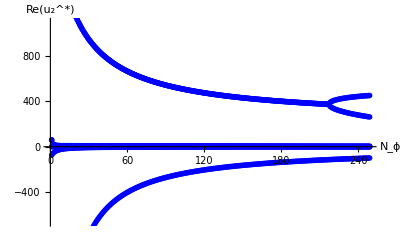

Phi4Trackingu2solsD4.jpg

```mathematica
ListPlot[TCollFP4Sol,  PlotMarkers->{marker1, 0.01},AxesLabel->{Style["N_ϕ", FontSize->14],Style["Re(u_2^*)", FontSize->14]}, TicksStyle->Directive[FontSize->13]]
Export["Phi4Trackingu2solsD4.jpg",%,"JPEG"]
```

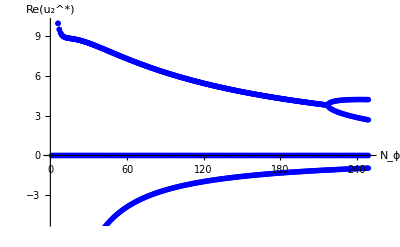

Phi4Trackingu2solsD4Zoomed.jpg

```mathematica
ListPlot[TCollFP4Sol,  PlotMarkers->{marker1, 0.01},AxesLabel->{Style["N_ϕ", FontSize->14],Style["Re(u_2^*)", FontSize->14]}, TicksStyle->Directive[FontSize->13], PlotRange->{{0,250},{-5,10}}]
Export["Phi4Trackingu2solsD4Zoomed.jpg",%,"JPEG"]
```

### 1<N_ϕ <219

To get some ideas of how the solution evolves for increasing N_ϕ, several values are calculated

#### N_ϕ = 2

The first attempt is N_ϕ=2 since this appears to be the simplest solution

```mathematica
FPSolgen/. Nphi-> 2 (*Find the value of the fixed points for Subscript[N, ϕ]=2*)
```

{{U[4,2,1]→0,U[4,2,2]→0},{U[4,2,1]→(Root-1.32 × 10^3Root[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,1]-1317.1089032394152 (132053288318570141233886055628800 π^10+8602646930064856572281172787200 π^8 Root-1.32 × 10^3Root[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,1]-1317.1089032394152+229070251730590443044507484160 π^6 (Root-1.32 × 10^3Root[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,1]-1317.1089032394152)^2+1344087800586131406197882880 π^4 (Root-1.32 × 10^3Root[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,1]-1317.1089032394152)^3+821446579125399018668032 π^2 (Root-1.32 × 10^3Root[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,1]-1317.1089032394152)^4+208379920012902144000 (Root-1.32 × 10^3Root[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,1]-1317.1089032394152)^5))/(21599407058489625617150194483200 π^10),U[4,2,2]→Root-1.32 × 10^3Root[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,1]-1317.1089032394152},{U[4,2,1]→(Root-13.3Root[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,2]-13.317458990973066 (132053288318570141233886055628800 π^10+8602646930064856572281172787200 π^8 Root-13.3Root[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,2]-13.317458990973066+229070251730590443044507484160 π^6 (Root-13.3Root[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,2]-13.317458990973066)^2+1344087800586131406197882880 π^4 (Root-13.3Root[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,2]-13.317458990973066)^3+821446579125399018668032 π^2 (Root-13.3Root[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,2]-13.317458990973066)^4+208379920012902144000 (Root-13.3Root[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,2]-13.317458990973066)^5))/(21599407058489625617150194483200 π^10),U[4,2,2]→Root-13.3Root[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,2]-13.317458990973066},{U[4,2,1]→(Root-1.85 × 10^4-1.47 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,3]-18531.53294996003 (132053288318570141233886055628800 π^10+8602646930064856572281172787200 π^8 Root-1.85 × 10^4-1.47 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,3]-18531.53294996003+229070251730590443044507484160 π^6 (Root-1.85 × 10^4-1.47 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,3]-18531.53294996003)^2+1344087800586131406197882880 π^4 (Root-1.85 × 10^4-1.47 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,3]-18531.53294996003)^3+821446579125399018668032 π^2 (Root-1.85 × 10^4-1.47 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,3]-18531.53294996003)^4+208379920012902144000 (Root-1.85 × 10^4-1.47 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,3]-18531.53294996003)^5))/(21599407058489625617150194483200 π^10),U[4,2,2]→Root-1.85 × 10^4-1.47 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,3]-18531.53294996003},{U[4,2,1]→(Root-1.85 × 10^4+1.47 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,4]-18531.53294996003 (132053288318570141233886055628800 π^10+8602646930064856572281172787200 π^8 Root-1.85 × 10^4+1.47 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,4]-18531.53294996003+229070251730590443044507484160 π^6 (Root-1.85 × 10^4+1.47 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,4]-18531.53294996003)^2+1344087800586131406197882880 π^4 (Root-1.85 × 10^4+1.47 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,4]-18531.53294996003)^3+821446579125399018668032 π^2 (Root-1.85 × 10^4+1.47 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,4]-18531.53294996003)^4+208379920012902144000 (Root-1.85 × 10^4+1.47 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,4]-18531.53294996003)^5))/(21599407058489625617150194483200 π^10),U[4,2,2]→Root-1.85 × 10^4+1.47 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,4]-18531.53294996003},{U[4,2,1]→(Root-206.-186. ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,5]-205.68777557099187 (132053288318570141233886055628800 π^10+8602646930064856572281172787200 π^8 Root-206.-186. ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,5]-205.68777557099187+229070251730590443044507484160 π^6 (Root-206.-186. ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,5]-205.68777557099187)^2+1344087800586131406197882880 π^4 (Root-206.-186. ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,5]-205.68777557099187)^3+821446579125399018668032 π^2 (Root-206.-186. ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,5]-205.68777557099187)^4+208379920012902144000 (Root-206.-186. ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,5]-205.68777557099187)^5))/(21599407058489625617150194483200 π^10),U[4,2,2]→Root-206.-186. ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,5]-205.68777557099187},{U[4,2,1]→(Root-206.+186. ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,6]-205.68777557099187 (132053288318570141233886055628800 π^10+8602646930064856572281172787200 π^8 Root-206.+186. ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,6]-205.68777557099187+229070251730590443044507484160 π^6 (Root-206.+186. ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,6]-205.68777557099187)^2+1344087800586131406197882880 π^4 (Root-206.+186. ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,6]-205.68777557099187)^3+821446579125399018668032 π^2 (Root-206.+186. ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,6]-205.68777557099187)^4+208379920012902144000 (Root-206.+186. ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,6]-205.68777557099187)^5))/(21599407058489625617150194483200 π^10),U[4,2,2]→Root-206.+186. ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+348048379084800 π^8 #1^2+9446057574400 π^6 #1^3+58333224960 π^4 #1^4+35775040 π^2 #1^5+9099 #1^6&,6]-205.68777557099187}}

```mathematica
%15/.(lhs_->rhs_):>lhs->N[rhs](*Gives the fixed point value as a number*)
```

```mathematica
ηϕ/. Nphi-> 2/.%91[[]](*Find value of the anomalous dimension for Subscript[N, ϕ]=2, the open brackets ensure evaluation of all the fixed point solutions*)
%13/. Nphi-> 2/.%91[[]](*Find eigenvalues of the stability matrix for Subscript[N, ϕ]=2, the open brackets ensure evaluation of all the fixed point solutions*)
```

ReplaceAll::reps: {%91} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(8 (10 U[4,2,1]+7 U[4,2,2]))/(768 π^2+10 U[4,2,1]+7 U[4,2,2])/.%91

ReplaceAll::reps: {%91} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{(4529848320 π^6+754974720 π^4 U[4,2,1]+7010304 π^2 U[4,2,1]^2+9600 U[4,2,1]^3+601620480 π^4 U[4,2,2]+10868736 π^2 U[4,2,1] U[4,2,2]+22640 U[4,2,1]^2 U[4,2,2]+4093440 π^2 U[4,2,2]^2+17584 U[4,2,1] U[4,2,2]^2+4508 U[4,2,2]^3-4 √(6296851552665600 π^8 U[4,2,1]^2+74144557301760 π^6 U[4,2,1]^3+489450110976 π^4 U[4,2,1]^4+1592524800 π^2 U[4,2,1]^5+2880000 U[4,2,1]^6+7027425489715200 π^8 U[4,2,1] U[4,2,2]+112738864988160 π^6 U[4,2,1]^2 U[4,2,2]+1068260917248 π^4 U[4,2,1]^3 U[4,2,2]+4467179520 π^2 U[4,2,1]^4 U[4,2,2]+10704000 U[4,2,1]^5 U[4,2,2]+2643981867417600 π^8 U[4,2,2]^2+62185757736960 π^6 U[4,2,1] U[4,2,2]^2+886019457024 π^4 U[4,2,1]^2 U[4,2,2]^2+4958134272 π^2 U[4,2,1]^3 U[4,2,2]^2+16709200 U[4,2,1]^4 U[4,2,2]^2+12991604981760 π^6 U[4,2,2]^3+331115397120 π^4 U[4,2,1] U[4,2,2]^3+2716250112 π^2 U[4,2,1]^2 U[4,2,2]^3+14092960 U[4,2,1]^3 U[4,2,2]^3+46924038144 π^4 U[4,2,2]^4+731437056 π^2 U[4,2,1] U[4,2,2]^4+6812568 U[4,2,1]^2 U[4,2,2]^4+76769280 π^2 U[4,2,2]^5+1800064 U[4,2,1] U[4,2,2]^5+204085 U[4,2,2]^6))/(1920 π^2 (768 π^2+10 U[4,2,1]+7 U[4,2,2])^2),(4529848320 π^6+754974720 π^4 U[4,2,1]+7010304 π^2 U[4,2,1]^2+9600 U[4,2,1]^3+601620480 π^4 U[4,2,2]+10868736 π^2 U[4,2,1] U[4,2,2]+22640 U[4,2,1]^2 U[4,2,2]+4093440 π^2 U[4,2,2]^2+17584 U[4,2,1] U[4,2,2]^2+4508 U[4,2,2]^3+4 √(6296851552665600 π^8 U[4,2,1]^2+74144557301760 π^6 U[4,2,1]^3+489450110976 π^4 U[4,2,1]^4+1592524800 π^2 U[4,2,1]^5+2880000 U[4,2,1]^6+7027425489715200 π^8 U[4,2,1] U[4,2,2]+112738864988160 π^6 U[4,2,1]^2 U[4,2,2]+1068260917248 π^4 U[4,2,1]^3 U[4,2,2]+4467179520 π^2 U[4,2,1]^4 U[4,2,2]+10704000 U[4,2,1]^5 U[4,2,2]+2643981867417600 π^8 U[4,2,2]^2+62185757736960 π^6 U[4,2,1] U[4,2,2]^2+886019457024 π^4 U[4,2,1]^2 U[4,2,2]^2+4958134272 π^2 U[4,2,1]^3 U[4,2,2]^2+16709200 U[4,2,1]^4 U[4,2,2]^2+12991604981760 π^6 U[4,2,2]^3+331115397120 π^4 U[4,2,1] U[4,2,2]^3+2716250112 π^2 U[4,2,1]^2 U[4,2,2]^3+14092960 U[4,2,1]^3 U[4,2,2]^3+46924038144 π^4 U[4,2,2]^4+731437056 π^2 U[4,2,1] U[4,2,2]^4+6812568 U[4,2,1]^2 U[4,2,2]^4+76769280 π^2 U[4,2,2]^5+1800064 U[4,2,1] U[4,2,2]^5+204085 U[4,2,2]^6))/(1920 π^2 (768 π^2+10 U[4,2,1]+7 U[4,2,2])^2)}/.%91

It would be easier to evaluate the above in one cell, so the references always work.  This is done below here.

```mathematica
FPSolgen/. Nphi-> 2;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ/. Nphi-> 2/.%[[]]
%13/. Nphi-> 2/.%%[[]]
```

{{U[4,2,1]→0.,U[4,2,2]→0.},{U[4,2,1]→-7369.86,U[4,2,2]→-1317.11},{U[4,2,1]→-74.5176,U[4,2,2]→-13.3175},{U[4,2,1]→6001.39+13281. ⅈ,U[4,2,2]→-18531.5-14692.5 ⅈ},{U[4,2,1]→6001.39-13281. ⅈ,U[4,2,2]→-18531.5+14692.5 ⅈ},{U[4,2,1]→60.1803+159.884 ⅈ,U[4,2,2]→-205.688-185.85 ⅈ},{U[4,2,1]→60.1803-159.884 ⅈ,U[4,2,2]→-205.688+185.85 ⅈ}}

{0.,8.80488,-0.994917,8.79187+0.381897 ⅈ,8.79187-0.381897 ⅈ,-0.976875+0.396642 ⅈ,-0.976875-0.396642 ⅈ}

{{4.,4.},{-39.3995,12.5661},{-4.45198,1.16891},{-34.3599-13.8908 ⅈ,-8.7598+20.1475 ⅈ},{-34.3599+13.8908 ⅈ,-8.7598-20.1475 ⅈ},{-4.43578+0.199388 ⅈ,-1.51288+1.64167 ⅈ},{-4.43578-0.199388 ⅈ,-1.51288-1.64167 ⅈ}}

#### N_ϕ = 3

Next value studied is N_ϕ=3

```mathematica
%7/. Nphi-> 3(*Find fixed point value for Subscript[N, ϕ]=3*)
```

{{U[4,3,1]→0,U[4,3,3]→0},{U[4,3,1]→(Root-1.37 × 10^5Root[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,1]-136793.37420924424 (132053288318570141233886055628800 π^10+8602646930064856572281172787200 π^8 Root-1.37 × 10^5Root[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,1]-136793.37420924424+1344087800586131406197882880 π^4 (Root-1.37 × 10^5Root[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,1]-136793.37420924424)^3+229070251730590443044507484160 π^6 (Root-1.37 × 10^5Root[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,1]-136793.37420924424)^3+821446579125399018668032 π^3 (Root-1.37 × 10^5Root[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,1]-136793.37420924424)^4+208379920012902144000 (Root-1.37 × 10^5Root[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,1]-136793.37420924424)^5))/(21599407058489625617150194483200 π^10),U[4,3,3]→Root-1.37 × 10^5Root[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,1]-136793.37420924424},{U[4,3,1]→(Root4.28-14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,3]4.2842886752496785 (132053288318570141233886055628800 π^10+8602646930064856572281172787200 π^8 Root4.28-14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,3]4.2842886752496785+1344087800586131406197882880 π^4 (Root4.28-14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,3]4.2842886752496785)^3+229070251730590443044507484160 π^6 (Root4.28-14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,3]4.2842886752496785)^3+821446579125399018668032 π^3 (Root4.28-14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,3]4.2842886752496785)^4+208379920012902144000 (Root4.28-14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,3]4.2842886752496785)^5))/(21599407058489625617150194483200 π^10),U[4,3,3]→Root4.28-14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,3]4.2842886752496785},{U[4,3,1]→(Root4.28-14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,3]4.2842886752496785 (132053288318570141233886055628800 π^10+8602646930064856572281172787200 π^8 Root4.28-14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,3]4.2842886752496785+1344087800586131406197882880 π^4 (Root4.28-14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,3]4.2842886752496785)^3+229070251730590443044507484160 π^6 (Root4.28-14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,3]4.2842886752496785)^3+821446579125399018668032 π^3 (Root4.28-14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,3]4.2842886752496785)^4+208379920012902144000 (Root4.28-14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,3]4.2842886752496785)^5))/(21599407058489625617150194483200 π^10),U[4,3,3]→Root4.28-14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,3]4.2842886752496785},{U[4,3,1]→(Root4.28+14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,4]4.2842886752496785 (132053288318570141233886055628800 π^10+8602646930064856572281172787200 π^8 Root4.28+14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,4]4.2842886752496785+1344087800586131406197882880 π^4 (Root4.28+14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,4]4.2842886752496785)^3+229070251730590443044507484160 π^6 (Root4.28+14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,4]4.2842886752496785)^3+821446579125399018668032 π^3 (Root4.28+14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,4]4.2842886752496785)^4+208379920012902144000 (Root4.28+14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,4]4.2842886752496785)^5))/(21599407058489625617150194483200 π^10),U[4,3,3]→Root4.28+14.9 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,4]4.2842886752496785},{U[4,3,1]→(Root7.44 × 10^3-5.10 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,5]7442.143136971164 (132053288318570141233886055628800 π^10+8602646930064856572281172787200 π^8 Root7.44 × 10^3-5.10 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,5]7442.143136971164+1344087800586131406197882880 π^4 (Root7.44 × 10^3-5.10 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,5]7442.143136971164)^3+229070251730590443044507484160 π^6 (Root7.44 × 10^3-5.10 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,5]7442.143136971164)^3+821446579125399018668032 π^3 (Root7.44 × 10^3-5.10 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,5]7442.143136971164)^4+208379920012902144000 (Root7.44 × 10^3-5.10 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,5]7442.143136971164)^5))/(21599407058489625617150194483200 π^10),U[4,3,3]→Root7.44 × 10^3-5.10 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,5]7442.143136971164},{U[4,3,1]→(Root7.44 × 10^3+5.10 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,6]7442.143136971164 (132053288318570141233886055628800 π^10+8602646930064856572281172787200 π^8 Root7.44 × 10^3+5.10 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,6]7442.143136971164+1344087800586131406197882880 π^4 (Root7.44 × 10^3+5.10 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,6]7442.143136971164)^3+229070251730590443044507484160 π^6 (Root7.44 × 10^3+5.10 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,6]7442.143136971164)^3+821446579125399018668032 π^3 (Root7.44 × 10^3+5.10 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,6]7442.143136971164)^4+208379920012902144000 (Root7.44 × 10^3+5.10 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,6]7442.143136971164)^5))/(21599407058489625617150194483200 π^10),U[4,3,3]→Root7.44 × 10^3+5.10 × 10^4 ⅈRoot[7421703487488000 π^12+5952824672256000 π^10 #1+(9446057574400 π^6+348048379084800 π^8) #1^3+58333224960 π^4 #1^4+35775040 π^3 #1^5+9099 #1^6&,6]7442.143136971164}}

```mathematica
%/.(lhs_->rhs_):>lhs->N[rhs](*Numerical value of the different FPs*)
```

{{U[4,3,1]→0.,U[4,3,3]→0.},{U[4,3,1]→3.82176×10^16,U[4,3,3]→-136793.},{U[4,3,1]→20.712-90.8263 ⅈ,U[4,3,3]→4.28429-14.9466 ⅈ},{U[4,3,1]→20.712-90.8263 ⅈ,U[4,3,3]→4.28429-14.9466 ⅈ},{U[4,3,1]→20.712+90.8263 ⅈ,U[4,3,3]→4.28429+14.9466 ⅈ},{U[4,3,1]→6.47177×10^14+4.17125×10^14 ⅈ,U[4,3,3]→7442.14-51040.9 ⅈ},{U[4,3,1]→6.47177×10^14-4.17125×10^14 ⅈ,U[4,3,3]→7442.14+51040.9 ⅈ}}

```mathematica
ηϕ/. Nphi-> 3/.%[[]](*Anomalous dimension for Subscript[N, ϕ] = 3*)
%13/. Nphi-> 3/.%%[[]](*Eigenvalues for Subscript[N, ϕ] = 3*)
```

{0.,8.,0.0928978-0.333016 ⅈ,0.0928978-0.333016 ⅈ,0.0928978+0.333016 ⅈ,8.+1.34039×10^-11 ⅈ,8.-1.34039×10^-11 ⅈ}

{{0.405285,0.405285},{-5.80764×10^19,-5.80761×10^19},{-11.3658+8.65795 ⅈ,-9.50087+13.3865 ⅈ},{-11.3658+8.65795 ⅈ,-9.50087+13.3865 ⅈ},{-11.3658-8.65795 ⅈ,-9.50087-13.3865 ⅈ},{3.86151×10^17-3.09715×10^17 ⅈ,3.86146×10^17-3.09718×10^17 ⅈ},{3.86151×10^17+3.09715×10^17 ⅈ,3.86146×10^17+3.09718×10^17 ⅈ}}

#### N_ϕ = 4

For N_ϕ = 2 a small automated process was written, that first prints the fixed point values, then the value of the anomalous dimension and lastly the eigenvalues of the stability matrix for the chosen value of N_ϕ. Here this is adapted for N_ϕ = 4.

```mathematica
FPSolgen/. Nphi-> 4;(*By setting Subscript[N, ϕ] -> 4 in all steps of the evaluation, the Subscript[N, ϕ] =4 solution is obtained*)
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ/. Nphi-> 4/.%[[]]
EVs/. Nphi-> 4/.%%[[]]
```

{{U[4,4,1]→0.,U[4,4,2]→0.},{U[4,4,1]→-4787.1,U[4,4,2]→-425.445},{U[4,4,1]→-47.4793,U[4,4,2]→-4.21964},{U[4,4,1]→2514.22+6780.04 ⅈ,U[4,4,2]→-12959.6-8932.14 ⅈ},{U[4,4,1]→2514.22-6780.04 ⅈ,U[4,4,2]→-12959.6+8932.14 ⅈ},{U[4,4,1]→15.8606+85.6938 ⅈ,U[4,4,2]→-135.445-132.805 ⅈ},{U[4,4,1]→15.8606-85.6938 ⅈ,U[4,4,2]→-135.445+132.805 ⅈ}}

{0.,8.73576,-1.06783,8.66642+0.435065 ⅈ,8.66642-0.435065 ⅈ,-1.09881+0.475378 ⅈ,-1.09881-0.475378 ⅈ}

{{4.,4.},{-36.7235,15.359},{-4.48895,1.3336},{-29.9973-12.831 ⅈ,-8.75418+27.2526 ⅈ},{-29.9973+12.831 ⅈ,-8.75418-27.2526 ⅈ},{-4.4949+0.244256 ⅈ,-1.87309+1.98878 ⅈ},{-4.4949-0.244256 ⅈ,-1.87309-1.98878 ⅈ}}

#### N_ϕ = 5

Again the  the fixed point values, then the value of the anomalous dimension and lastly the eigenvalues of the stability matrix are printed for the chosen value of N_ϕ. Here this is chosen to be N_ϕ = 5.

```mathematica
FPSolgen/. Nphi-> 5;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ/. Nphi-> 5/.%[[]]
EVs/. Nphi-> 5/.%%[[]]
```

{{U[4,5,1]→0.,U[4,5,2]→0.},{U[4,5,1]→-4041.4,U[4,5,2]→-284.961},{U[4,5,1]→-39.8494,U[4,5,2]→-2.80981},{U[4,5,1]→2168.97+5537.59 ⅈ,U[4,5,2]→-11886.-7705.22 ⅈ},{U[4,5,1]→2168.97-5537.59 ⅈ,U[4,5,2]→-11886.+7705.22 ⅈ},{U[4,5,1]→12.3831+71.1847 ⅈ,U[4,5,2]→-122.798-120.568 ⅈ},{U[4,5,1]→12.3831-71.1847 ⅈ,U[4,5,2]→-122.798+120.568 ⅈ}}

{0.,8.72034,-1.08438,8.63761+0.449147 ⅈ,8.63761-0.449147 ⅈ,-1.12699+0.496542 ⅈ,-1.12699-0.496542 ⅈ}

{{4.,4.},{-36.1672,16.2405},{-4.4974,1.3871},{-29.0854-12.6466 ⅈ,-8.23864+29.363 ⅈ},{-29.0854+12.6466 ⅈ,-8.23864-29.363 ⅈ},{-4.50857+0.256389 ⅈ,-1.95774+2.10787 ⅈ},{-4.50857-0.256389 ⅈ,-1.95774-2.10787 ⅈ}}

#### N_ϕ = 10

Again the  the fixed point values, then the value of the anomalous dimension and lastly the eigenvalues of the stability matrix are printed for the chosen value of N_ϕ. Here this is chosen to be N_ϕ = 10.

```mathematica
FPSolgen/. Nphi-> 10;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ/. Nphi-> 10/.%[[]]
EVs/. Nphi-> 10/.%%[[]]
```

{{U[4,10,1]→0.,U[4,10,2]→0.},{U[4,10,1]→-2250.18,U[4,10,2]→-77.4697},{U[4,10,1]→-21.8777,U[4,10,2]→-0.753211},{U[4,10,1]→1578.52+2987.81 ⅈ,U[4,10,2]→-9055.45-4912.49 ⅈ},{U[4,10,1]→1578.52-2987.81 ⅈ,U[4,10,2]→-9055.45+4912.49 ⅈ},{U[4,10,1]→9.04863+40.9546 ⅈ,U[4,10,2]→-92.1855-88.6153 ⅈ},{U[4,10,1]→9.04863-40.9546 ⅈ,U[4,10,2]→-92.1855+88.6153 ⅈ}}

{0.,8.68838,-1.11904,8.57606+0.481648 ⅈ,8.57606-0.481648 ⅈ,-1.18722+0.545976 ⅈ,-1.18722-0.545976 ⅈ}

{{4.,4.},{-35.0564,18.438},{-4.51519,1.51969},{-27.2344-12.3077 ⅈ,-6.14124+34.3147 ⅈ},{-27.2344+12.3077 ⅈ,-6.14124-34.3147 ⅈ},{-4.53774+0.284852 ⅈ,-2.13333+2.41722 ⅈ},{-4.53774-0.284852 ⅈ,-2.13333-2.41722 ⅈ}}

#### N_ϕ = 20

Again the  the fixed point values, then the value of the anomalous dimension and lastly the eigenvalues of the stability matrix are printed for the chosen value of N_ϕ. Here this is chosen to be N_ϕ = 20.

```mathematica
FPSolgen/. Nphi-> 20;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ/. Nphi-> 20/.%[[]]
EVs/. Nphi-> 20/.%%[[]]
```

{{U[4,20,1]→0.,U[4,20,2]→0.},{U[4,20,1]→-1186.81,U[4,20,2]→-20.1221},{U[4,20,1]→-11.4439,U[4,20,2]→-0.19403},{U[4,20,1]→1173.19+1597.67 ⅈ,U[4,20,2]→-6566.16-3138.78 ⅈ},{U[4,20,1]→1173.19-1597.67 ⅈ,U[4,20,2]→-6566.16+3138.78 ⅈ},{U[4,20,1]→8.74361+23.4203 ⅈ,U[4,20,2]→-68.8869-60.6614 ⅈ},{U[4,20,1]→8.74361-23.4203 ⅈ,U[4,20,2]→-68.8869+60.6614 ⅈ}}

{0.,8.67196,-1.13703,8.57155+0.497394 ⅈ,8.57155-0.497394 ⅈ,-1.18844+0.564512 ⅈ,-1.18844-0.564512 ⅈ}

{{4.,4.},{-34.5075,19.7828},{-4.52446,1.59971},{-26.89-12.547 ⅈ,-3.9892+35.15 ⅈ},{-26.89+12.547 ⅈ,-3.9892-35.15 ⅈ},{-4.5375+0.294625 ⅈ,-2.06172+2.5824 ⅈ},{-4.5375-0.294625 ⅈ,-2.06172-2.5824 ⅈ}}

#### N_ϕ = 100

Again the  the fixed point values, then the value of the anomalous dimension and lastly the eigenvalues of the stability matrix are printed for the chosen value of N_ϕ. Here this is chosen to be N_ϕ = 100.

```mathematica
FPSolgen/. Nphi-> 100;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ/. Nphi-> 100/.%[[]]
EVs/. Nphi-> 100/.%%[[]]
```

{{U[4,100,1]→0.,U[4,100,2]→0.},{U[4,100,1]→-247.644,U[4,100,2]→-0.828437},{U[4,100,1]→-2.37073,U[4,100,2]→-0.00793073},{U[4,100,1]→519.8+335.465 ⅈ,U[4,100,2]→-2634.47-1009.19 ⅈ},{U[4,100,1]→519.8-335.465 ⅈ,U[4,100,2]→-2634.47+1009.19 ⅈ},{U[4,100,1]→5.971+4.24408 ⅈ,U[4,100,2]→-30.6289-13.3356 ⅈ},{U[4,100,1]→5.971-4.24408 ⅈ,U[4,100,2]→-30.6289+13.3356 ⅈ}}

{0.,8.65869,-1.15166,8.81974+0.394208 ⅈ,8.81974-0.394208 ⅈ,-0.946432+0.40457 ⅈ,-0.946432-0.40457 ⅈ}

{{4.,4.},{-34.0736,20.9898},{-4.53203,1.6706},{-34.9145-14.8811 ⅈ,-0.872659+19.9895 ⅈ},{-34.9145+14.8811 ⅈ,-0.872659-19.9895 ⅈ},{-4.42019+0.202265 ⅈ,-0.761678+1.94159 ⅈ},{-4.42019-0.202265 ⅈ,-0.761678-1.94159 ⅈ}}

#### N_ϕ = 200

Again the  the fixed point values, then the value of the anomalous dimension and lastly the eigenvalues of the stability matrix are printed for the chosen value of N_ϕ. Here this is chosen to be N_ϕ = 200. Now one can see that up to here the values do not change rapidly, and can therefore be easily tracked.

```mathematica
FPSolgen/. Nphi-> 200;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ/. Nphi-> 200/.%[[]]
EVs/. Nphi-> 200/.%%[[]]
```

{{U[4,200,1]→0.,U[4,200,2]→0.},{U[4,200,1]→-124.477,U[4,200,2]→-0.207835},{U[4,200,1]→-1.19051,U[4,200,2]→-0.00198776},{U[4,200,1]→386.554+82.339 ⅈ,U[4,200,2]→-1844.64-279.922 ⅈ},{U[4,200,1]→386.554-82.339 ⅈ,U[4,200,2]→-1844.64+279.922 ⅈ},{U[4,200,1]→4.01296+0.757756 ⅈ,U[4,200,2]→-19.1228-2.44871 ⅈ},{U[4,200,1]→4.01296-0.757756 ⅈ,U[4,200,2]→-19.1228+2.44871 ⅈ}}

{0.,8.65702,-1.15351,8.98134+0.140209 ⅈ,8.98134-0.140209 ⅈ,-0.814174+0.135498 ⅈ,-0.814174-0.135498 ⅈ}

{{4.,4.},{-34.0198,21.1493},{-4.53298,1.6799},{-46.824-7.8157 ⅈ,-0.0839575+6.08877 ⅈ},{-46.824+7.8157 ⅈ,-0.0839575-6.08877 ⅈ},{-4.36158+0.0659907 ⅈ,-0.0758368+0.657402 ⅈ},{-4.36158-0.0659907 ⅈ,-0.0758368-0.657402 ⅈ}}

### N_ϕ >218

#### N_ϕ = 500

Again the  the fixed point values, then the value of the anomalous dimension and lastly the eigenvalues of the stability matrix are printed for the chosen value of N_ϕ. Here this is chosen to be N_ϕ = 500. Looking at the solution here, a jump becomes visible, all solutions have become real. This means that to track increasing N_ϕ all the different solutions have to be glued together. But first some extra N_ϕ values are studied to see if this is a single event.

```mathematica
Simplify[%7/. Nphi-> 500];
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ/. Nphi-> 500/.%[[]]
%13/. Nphi-> 500/.%%[[]]
```

{{U[4,500,1]→0.,U[4,500,2]→0.},{U[4,500,1]→485.091,U[4,500,2]→-2014.17},{U[4,500,1]→109.872,U[4,500,2]→-616.134},{U[4,500,1]→2.9122,U[4,500,2]→-12.0919},{U[4,500,1]→1.08549,U[4,500,2]→-6.08714},{U[4,500,1]→-49.9487,U[4,500,2]→-0.0333231},{U[4,500,1]→-0.477443,U[4,500,2]→-0.000318525}}

{0.,9.57813,8.72531,-0.302514,-1.07903,8.65602,-1.15462}

{{4.,4.},{-130.647,16.8095},{-36.345,-15.5362},{-4.12634,2.46447},{-4.49467,-1.33408},{-33.9875,21.2459},{-4.53355,1.68552}}

#### N_ϕ = 1000

Again the  the fixed point values, then the value of the anomalous dimension and lastly the eigenvalues of the stability matrix are printed for the chosen value of N_ϕ. Here this is chosen to be N_ϕ = 1000.

```mathematica
%7/. Nphi-> 1000;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ/. Nphi-> 1000/.%[[]]
%13/. Nphi-> 1000/.%%[[]]
```

{{U[4,1000,1]→0.,U[4,1000,2]→0.},{U[4,1000,1]→479.932,U[4,1000,2]→-1953.32},{U[4,1000,1]→52.1799,U[4,1000,2]→-303.142},{U[4,1000,1]→1.66447,U[4,1000,2]→-6.77205},{U[4,1000,1]→0.507011,U[4,1000,2]→-2.94551},{U[4,1000,1]→-25.0007,U[4,1000,2]→-0.00833657},{U[4,1000,1]→-0.238928,U[4,1000,2]→-0.0000796712}}

{0.,9.74139,8.68709,-0.155699,-1.12045,8.65569,-1.15498}

{{4.,4.},{-254.018,19.8398},{-35.0128,-18.558},{-4.06371,3.20696},{-4.51591,-1.52734},{-33.9768,21.2783},{-4.53375,1.6874}}

```mathematica
%7/. Nphi-> 1000
```

{{U[4,1000,1]→0,U[4,1000,2]→0},{U[4,1000,1]→(Root-1.95 × 10^3Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,1]-1953.3214019278014 (18400992379137451614794738602218627677686176391862715754140516923473920000 π^10-289874026796440344278475626414976214639634018993969316177596173516800000 π^8 Root-1.95 × 10^3Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,1]-1953.3214019278014-340310928006210594980802071534435606471864664034688469963634895203860480000 π^6 (Root-1.95 × 10^3Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,1]-1953.3214019278014)^2-449667149579369441863726003408592007133295339083455388972766316409651200000 π^4 (Root-1.95 × 10^3Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,1]-1953.3214019278014)^3-16486801501082034106475983663503871488918682418978096215329246963302400000 π^2 (Root-1.95 × 10^3Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,1]-1953.3214019278014)^4-71867209111865452243040323688726866515009838759529697757071114240000000 (Root-1.95 × 10^3Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,1]-1953.3214019278014)^5))/(6135878079845719214064025801859537203745938166532084388067027189760000 π^10),U[4,1000,2]→Root-1.95 × 10^3Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,1]-1953.3214019278014},{U[4,1000,1]→(Root-303.Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,2]-303.14210345716 (18400992379137451614794738602218627677686176391862715754140516923473920000 π^10-289874026796440344278475626414976214639634018993969316177596173516800000 π^8 Root-303.Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,2]-303.14210345716-340310928006210594980802071534435606471864664034688469963634895203860480000 π^6 (Root-303.Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,2]-303.14210345716)^2-449667149579369441863726003408592007133295339083455388972766316409651200000 π^4 (Root-303.Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,2]-303.14210345716)^3-16486801501082034106475983663503871488918682418978096215329246963302400000 π^2 (Root-303.Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,2]-303.14210345716)^4-71867209111865452243040323688726866515009838759529697757071114240000000 (Root-303.Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,2]-303.14210345716)^5))/(6135878079845719214064025801859537203745938166532084388067027189760000 π^10),U[4,1000,2]→Root-303.Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,2]-303.14210345716},{U[4,1000,1]→(Root-6.77Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,3]-6.772047252939573 (18400992379137451614794738602218627677686176391862715754140516923473920000 π^10-289874026796440344278475626414976214639634018993969316177596173516800000 π^8 Root-6.77Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,3]-6.772047252939573-340310928006210594980802071534435606471864664034688469963634895203860480000 π^6 (Root-6.77Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,3]-6.772047252939573)^2-449667149579369441863726003408592007133295339083455388972766316409651200000 π^4 (Root-6.77Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,3]-6.772047252939573)^3-16486801501082034106475983663503871488918682418978096215329246963302400000 π^2 (Root-6.77Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,3]-6.772047252939573)^4-71867209111865452243040323688726866515009838759529697757071114240000000 (Root-6.77Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,3]-6.772047252939573)^5))/(6135878079845719214064025801859537203745938166532084388067027189760000 π^10),U[4,1000,2]→Root-6.77Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,3]-6.772047252939573},{U[4,1000,1]→(Root-2.95Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,4]-2.9455148301949072 (18400992379137451614794738602218627677686176391862715754140516923473920000 π^10-289874026796440344278475626414976214639634018993969316177596173516800000 π^8 Root-2.95Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,4]-2.9455148301949072-340310928006210594980802071534435606471864664034688469963634895203860480000 π^6 (Root-2.95Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,4]-2.9455148301949072)^2-449667149579369441863726003408592007133295339083455388972766316409651200000 π^4 (Root-2.95Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,4]-2.9455148301949072)^3-16486801501082034106475983663503871488918682418978096215329246963302400000 π^2 (Root-2.95Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,4]-2.9455148301949072)^4-71867209111865452243040323688726866515009838759529697757071114240000000 (Root-2.95Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,4]-2.9455148301949072)^5))/(6135878079845719214064025801859537203745938166532084388067027189760000 π^10),U[4,1000,2]→Root-2.95Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,4]-2.9455148301949072},{U[4,1000,1]→(Root-8.34 × 10^-3Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,5]-0.008336569876831767 (18400992379137451614794738602218627677686176391862715754140516923473920000 π^10-289874026796440344278475626414976214639634018993969316177596173516800000 π^8 Root-8.34 × 10^-3Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,5]-0.008336569876831767-340310928006210594980802071534435606471864664034688469963634895203860480000 π^6 (Root-8.34 × 10^-3Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,5]-0.008336569876831767)^2-449667149579369441863726003408592007133295339083455388972766316409651200000 π^4 (Root-8.34 × 10^-3Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,5]-0.008336569876831767)^3-16486801501082034106475983663503871488918682418978096215329246963302400000 π^2 (Root-8.34 × 10^-3Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,5]-0.008336569876831767)^4-71867209111865452243040323688726866515009838759529697757071114240000000 (Root-8.34 × 10^-3Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,5]-0.008336569876831767)^5))/(6135878079845719214064025801859537203745938166532084388067027189760000 π^10),U[4,1000,2]→Root-8.34 × 10^-3Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,5]-0.008336569876831767},{U[4,1000,1]→(Root-7.97 × 10^-5Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,6]-0.00007967123986033964 (18400992379137451614794738602218627677686176391862715754140516923473920000 π^10-289874026796440344278475626414976214639634018993969316177596173516800000 π^8 Root-7.97 × 10^-5Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,6]-0.00007967123986033964-340310928006210594980802071534435606471864664034688469963634895203860480000 π^6 (Root-7.97 × 10^-5Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,6]-0.00007967123986033964)^2-449667149579369441863726003408592007133295339083455388972766316409651200000 π^4 (Root-7.97 × 10^-5Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,6]-0.00007967123986033964)^3-16486801501082034106475983663503871488918682418978096215329246963302400000 π^2 (Root-7.97 × 10^-5Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,6]-0.00007967123986033964)^4-71867209111865452243040323688726866515009838759529697757071114240000000 (Root-7.97 × 10^-5Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,6]-0.00007967123986033964)^5))/(6135878079845719214064025801859537203745938166532084388067027189760000 π^10),U[4,1000,2]→Root-7.97 × 10^-5Root[1374389534720 π^12+171891978529669120 π^10 #1+202400348543624675328 π^8 #1^2+977613206026489430016 π^6 #1^3+1020840755235884347392 π^4 #1^4+37180451046845185344 π^2 #1^5+161926593484058775 #1^6&,6]-0.00007967123986033964}}

```mathematica
%48/.(lhs_->rhs_):>lhs->N[rhs]
```

ReplaceAll::reps: {%87} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(8 (14 U[4,3,1]+8 U[4,3,2]))/(768 π^2+14 U[4,3,1]+8 U[4,3,2])/.%87

#### N_ϕ = 10 000

Again the  the fixed point values, then the value of the anomalous dimension and lastly the eigenvalues of the stability matrix are printed for the chosen value of N_ϕ. Here this is chosen to be N_ϕ = 10 000.

```mathematica
%7/. Nphi-> 10000;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ/. Nphi-> 10000/.%[[4]]
%13/. Nphi-> 10000/.%%[[4]]
```

{{U[4,10000,1]→0.,U[4,10000,2]→0.},{U[4,10000,1]→-111490.,U[4,10000,2]→-1880.51},{U[4,10000,1]→5.0246,U[4,10000,2]→-30.0536},{U[4,10000,1]→0.187064,U[4,10000,2]→-0.749444},{U[4,10000,1]→0.0480908,U[4,10000,2]→-0.287646},{U[4,10000,1]→-2.50244,U[4,10000,2]→-0.0000834177},{U[4,10000,1]→-0.0239113,U[4,10000,2]→-7.97073×10^-7}}

-0.0161292

{-4.00647,3.91759}

#### N_ϕ = 100 000

Again the  the fixed point values, then the value of the anomalous dimension and lastly the eigenvalues of the stability matrix are printed for the chosen value of N_ϕ. Here this is chosen to be N_ϕ = 100 000.

```mathematica
Simplify[%7/. Nphi-> 100000];
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ/. Nphi-> 100000/.%[[]]
%13/. Nphi-> 100000/.%%[[]]
```

{{U[4,100000,1]→0.,U[4,100000,2]→0.},{U[4,100000,1]→-125938.,U[4,100000,2]→-1872.47},{U[4,100000,1]→0.500731,U[4,100000,2]→-3.00345},{U[4,100000,1]→0.0189252,U[4,100000,2]→-0.0757126},{U[4,100000,1]→0.0047853,U[4,100000,2]→-0.0287028},{U[4,100000,1]→-0.250268,U[4,100000,2]→-8.34229×10^-7},{U[4,100000,1]→-0.00239132,U[4,100000,2]→-7.97109×10^-9}}

{0.,8.,8.65565,-0.0016193,-1.15503,8.65536,-1.15535}

{{4.,4.},{-3.20193×10^7,-39751.7},{-33.9756,-21.2841},{-4.00065,3.99172},{-4.53377,-1.68779},{-33.9662,21.3104},{-4.53394,1.68927}}

#### N_ϕ = 1 000 000

Again the  the fixed point values, then the value of the anomalous dimension and lastly the eigenvalues of the stability matrix are printed for the chosen value of N_ϕ. Here this is chosen to be N_ϕ = 1 000 000.

```mathematica
%7/. Nphi-> 1000000;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ/. Nphi-> 1000000/.%[[]]
%13/. Nphi-> 1000000/.%%[[]]
```

{{U[4,1000000,1]→0.,U[4,1000000,2]→0.},{U[4,1000000,1]→4.35059×10^14,U[4,1000000,2]→-1871.66},{U[4,1000000,1]→0.0501305,U[4,1000000,2]→-0.300327},{U[4,1000000,1]→0.00189472,U[4,1000000,2]→-0.007579},{U[4,1000000,1]→0.000478294,U[4,1000000,2]→-0.00286967},{U[4,1000000,1]→-0.025027,U[4,1000000,2]→-8.34235×10^-9},{U[4,1000000,1]→-0.000239134,U[4,1000000,2]→-7.97112×10^-11}}

{0.,8.,8.6575,-0.000162237,-1.15532,8.65535,-1.15535}

{{4.,4.},{8.26511×10^11,1.10202×10^18},{-33.7796,-21.2367},{-4.00007,3.99917},{-4.53392,-1.68914},{-33.9661,21.3107},{-4.53394,1.68929}}

### Gluing the different parts of the solution together

In the previous it has become obvious that the solution exists out of two parts. To fully track the evolution for increasing N_ϕ the two different solutions have to be “glued” together. 
To do this we want to compare two solutions that actually lie close together but are on different sides of the split. This split is generated when the complex solutions collide and become real at N(ϕ)=219. Therefore we will study N=218 and N=219 and compare the results.

#### N_ϕ=218

Again the  the fixed point values, then the value of the anomalous dimension and lastly the eigenvalues of the stability matrix are printed for the chosen value of N_ϕ. Here this is chosen to be N_ϕ = 218.

```mathematica
Simplify[FPSolgen/. Nphi-> 218];
%/.(lhs_->rhs_):>lhs->N[rhs](*These first two steps give the numerical values for the different fixed point solutions*)
FP218={U[4,218,1],U[4,218,2]}/. %(*A function is created that actually saves these values as coordinates*)
ηϕ/. Nphi-> 218/.%%[[]](*Find the value of the anomalous dimension*)
EVS218=EVs/. Nphi-> 218/.%%%[[]](*Calculate and save the evs of the stability matrix*)
```

{{U[4,218,1]→0.,U[4,218,2]→0.},{U[4,218,1]→-114.249,U[4,218,2]→-0.174981},{U[4,218,1]→-1.0926,U[4,218,2]→-0.00167341},{U[4,218,1]→374.725+8.30334 ⅈ,U[4,218,2]→-1774.44-28.56 ⅈ},{U[4,218,1]→374.725-8.30334 ⅈ,U[4,218,2]→-1774.44+28.56 ⅈ},{U[4,218,1]→3.78594+0.0726459 ⅈ,U[4,218,2]→-17.9272-0.235308 ⅈ},{U[4,218,1]→3.78594-0.0726459 ⅈ,U[4,218,2]→-17.9272+0.235308 ⅈ}}

{{0.,0.},{-114.249,-0.174981},{-1.0926,-0.00167341},{374.725+8.30334 ⅈ,-1774.44-28.56 ⅈ},{374.725-8.30334 ⅈ,-1774.44+28.56 ⅈ},{3.78594+0.0726459 ⅈ,-17.9272-0.235308 ⅈ},{3.78594-0.0726459 ⅈ,-17.9272+0.235308 ⅈ}}

{0.,8.65688,-1.15366,9.00026+0.0146588 ⅈ,9.00026-0.0146588 ⅈ,-0.79971+0.0140708 ⅈ,-0.79971-0.0140708 ⅈ}

{EVs,EVs,EVs,EVs,EVs,EVs,EVs}

#### N_ϕ=219

Again the  the fixed point values, then the value of the anomalous dimension and lastly the eigenvalues of the stability matrix are printed for the chosen value of N_ϕ. Here this is chosen to be N_ϕ = 219.

```mathematica
Simplify[FPSolgen/. Nphi-> 219];
%/.(lhs_->rhs_):>lhs->N[rhs](*These first two steps give the numerical values for the different fixed point solutions*)
FP219={U[4,219,1],U[4,219,2]}/. % (*A function is created that actually saves these values as coordinates*)
ηϕ/. Nphi-> 219/.%%[[]](*Value of anomalous dimension*)
EVS219=EVs/. Nphi-> 219/.%%%[[]](*Calculate and save the evs of the stability matrix*)
```

{{U[4,219,1]→0.,U[4,219,2]→0.},{U[4,219,1]→390.353,U[4,219,2]→-1826.72},{U[4,219,1]→357.889,U[4,219,2]→-1714.99},{U[4,219,1]→3.91568,U[4,219,2]→-18.324},{U[4,219,1]→3.63244,U[4,219,2]→-17.4065},{U[4,219,1]→-113.73,U[4,219,2]→-0.173389},{U[4,219,1]→-1.08764,U[4,219,2]→-0.00165818}}

{{0.,0.},{390.353,-1826.72},{357.889,-1714.99},{3.91568,-18.324},{3.63244,-17.4065},{-113.73,-0.173389},{-1.08764,-0.00165818}}

{0.,9.02996,8.97254,-0.77141,-0.826505,8.65688,-1.15367}

{EVs,EVs,EVs,EVs,EVs,EVs,EVs}

#### Compare the two

To check which fixed point values correspond, they are plotted in a U_1-U_2 plot. To show which dot is which solution, they will instead be given as numbers. Then the numbers that are closest together correspond to the same fixed point solution.

```mathematica
FP218 = {{0.,0.},{-114.24907010610121,-0.17498108512811397},{-1.092604742611591,-0.001673406735833818},{374.72464621568076+8.303341101331391 ⅈ,-1774.4363385441932-28.56000438591437 ⅈ},{374.72464621568076-8.303341101331391 ⅈ,-1774.4363385441932+28.56000438591437 ⅈ},{3.7859361101124693+0.0726458740867483 ⅈ,-17.9272480391664-0.23530818581362006 ⅈ},{3.7859361101124693-0.0726458740867483 ⅈ,-17.9272480391664+0.23530818581362006 ⅈ}};
```

```mathematica
FP219 = {{0.,0.},{390.35253168614184,-1826.7158217156268},{357.8893511618196,-1714.9891063409464},{3.915680560827756,-18.32404048813234},{3.632439940449977,-17.406482970608693},{-113.72989779907057,-0.17338926418345307},{-1.0876353943166273,-0.0016581769998036612}};
```

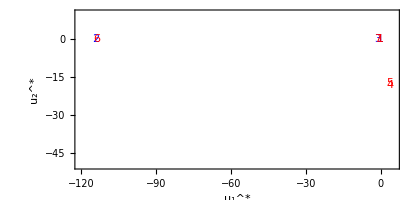

```mathematica
Show[Graphics[{Blue,MapIndexed[Text[First@#2,#1]&,FP218[[1;;3]]/.Rule->List],Red,MapIndexed[Text[First@#2,#1]&,FP219/.Rule->List]},Axes->True,FrameLabel->{"u_1^*","u_2^*"},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotRange-> {{-120,5},{-50,10}}, Frame-> True, Axes->True]]
```

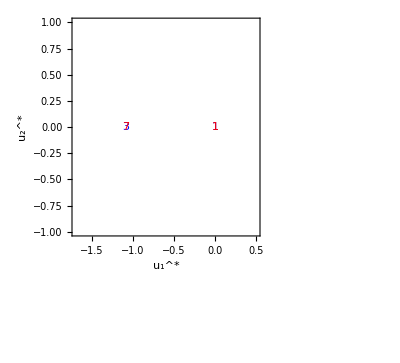

```mathematica
Show[Graphics[{Blue,MapIndexed[Style[Text[First@#2,#1], FontSize->20]&,FP218[[1;;3]]/.Rule->List],Red,MapIndexed[Style[Text[First@#2,#1], FontSize->20]&,FP219/.Rule->List]},Axes->True,FrameLabel->{"u_1^*","u_2^*"},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotRange-> {{-1.7,0.5},{-1,1}}, Frame-> True, Axes->True]]
```

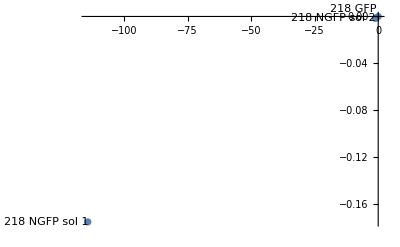

```mathematica
ListPlot[{Labeled[FP218[[1]],"218 GFP"],Labeled[FP218[[2]],"218 NGFP sol 1 ",Left],Labeled[FP218[[3]],"218 NGFP sol 2 ",Left]},Axes->True]
```

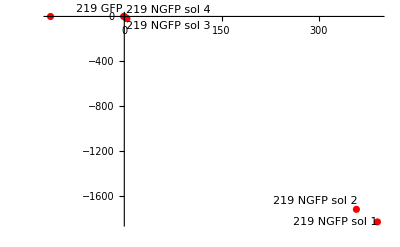

```mathematica
ListPlot[{Labeled[FP219[[1]],"219 GFP"],Labeled[FP219[[2]],"219 NGFP sol 1 "],Labeled[FP219[[3]],"219 NGFP sol 2 "],Labeled[FP219[[4]],"219 NGFP sol 3 "],Labeled[FP219[[5]],"219 NGFP sol 4 "],Labeled[FP219[[6]],"219 NGFP sol 5 "],Labeled[FP219[[7]],"219 NGFP sol 6 "]},PlotStyle->Red, Axes->True]
```

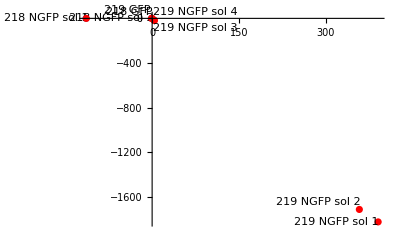

```mathematica
Show[%296, %297, PlotRange->Automatic]
```

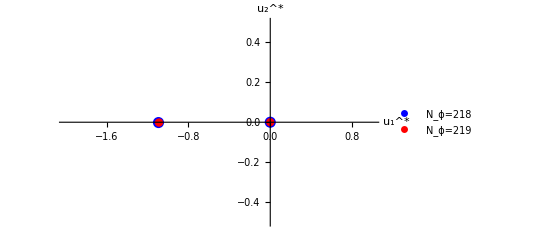

```mathematica
ListPlot[{FP218, FP219}, PlotStyle->{{Blue,PointSize[0.02]},  {Red, PointSize[0.015]}},AxesLabel-> {"u_1^*", "u_2^*"},  PlotLegends->{"N_ϕ=218","N_ϕ=219"}, PlotRange->{{-2,1}, {-0.5, 0.5}}]
```

```mathematica
Export["fixedpointpositionsN218enN219labeldots(only2FP).jpg", %, "JPEG"]
```

fixedpointpositionsN218enN219labeldots(only2FP).jpg

This shows the second solution becomes the sixth, and the third solution becomes the seventh solution when moving from N_ϕ=218 to N_ϕ=219

```mathematica
Export["fixedpointpositionsN218enN219label.jpg", %154, "JPEG"](*Export the figure.*)
```

fixedpointpositionsN218enN219label.jpg

AbsoluteFileName::fdnfnd: Directory or file fixedpointpositionsN218enN219.jpg not found.

DirectoryName::string: String expected at position 1 in DirectoryName[$Failed].

SystemOpen[DirectoryName[$Failed]]

## Which solutions appear due to the anomalous dimension?

In the single field expansion, one of the fixed points appeared due to the inclusion of the anomalous dimension. It seems like a good idea to check whether this is the case for the N_ϕ-scalar fields evaluation as well.

This will be studied for the case  N_ϕ=2 and then since we can track the solutions for increasing N_ϕ this then translates into a conclusion for all N_ϕ

The anomalous dimension is defined with an extra constant ϵ, that can be varied from 0 to 1 in order to track the evolution of the fixed points for decreasing influence of the anomalous dimension.

```mathematica
ηϕ= ϵ(8 (2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2]))/(768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2]);
```

Now we want to solve this for increasing values of ϵ.

```mathematica
etatrackfp1= {}; (*These three lists are made to track the three fixed point positions*)
etatrackfp2 = {};
etatrackfp3 = {};

Do[
βϕ[4,Nphi,1]=0;
βϕ[4,Nphi,2]=0;(*Since the fixed points are studied, the beta functions are set to 0*)
Nphi =2; (*Subscript[N, ϕ]=2 is the situation chosen to study*)
ηϕ= ϵ(8 (2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2]))/(768 π^2+2 U[4,Nphi,1]+4 Nphi U[4,Nphi,1]+5 U[4,Nphi,2]+Nphi U[4,Nphi,2])/. Nphi-> 2;(*Properly define the anomalous dimension*)
FP = Solve[Simplify[Coefficient[RHSphi4, X, 2]]==Coefficient[LHSfinalphi4, X, 2]&&Simplify[Coefficient[RHSphi4,S2]]==Coefficient[LHSfinalphi4, S2]/. k-> 1, {U[4,Nphi, 1], U[4,Nphi, 2]}];(*Solves for the fixed points, with the previously defined anomalous dimension.*)
 AppendTo[etatrackfp1,{U[4, Nphi, 1], U[4, Nphi, 2]}/.FP[[1]] ];(*Saving the FP value*)
 AppendTo[etatrackfp2,{U[4, Nphi, 1], U[4, Nphi, 2]}/.FP[[2]] ];
 AppendTo[etatrackfp3, {U[4, Nphi, 1], U[4, Nphi, 2]}/.FP[[3] ]];, 
 {ϵ, 1/1000, 1, 1/1000}]
```

This has generated a list of fixed point values. To make it easier to examine, the evolution of the fixed points for increasing ϵ is plotted, together with the boundary cases (ϵ = 1 and ϵ =0).

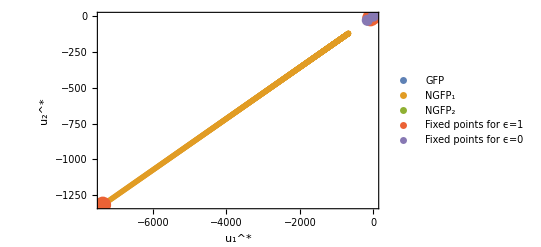

```mathematica
ListPlot[{etatrackfp1, etatrackfp2, etatrackfp3, {{0, 0},{-7369.86, -1317.11},{-74.5176,-13.3175}}, {{0,0},{-163.03431607772825,-29.13676178783683}}}, PlotLegends->{"GFP", "NGFP_1", "NGFP_2", "Fixed points for ϵ=1", "Fixed points for ϵ=0"}, PlotStyle->{PointSize[0.01],PointSize[0.01],PointSize[0.01], PointSize[0.03], PointSize[0.02]}, FrameLabel->{Style["u_1^*", FontSize->14] ,Style[ "u_2^*", FontSize->14]}, PlotRange->All, TicksStyle->Directive[FontSize->13], Frame-> True]
```

In the previous picture, the second fixed point cannot be distinguished from the gaussian fixed point. Therefore a second, more zoomed in, picture is created.

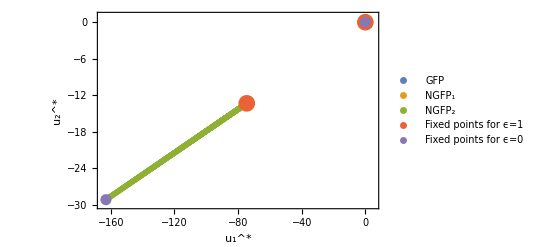

```mathematica
ListPlot[{etatrackfp1, etatrackfp2, etatrackfp3, {{0, 0},{-7369.86, -1317.11},{-74.5176,-13.3175}}, {{0,0},{-163.03431607772825,-29.13676178783683}}}, PlotLegends->{"GFP", "NGFP_1", "NGFP_2", "Fixed points for ϵ=1", "Fixed points for ϵ=0"}, PlotStyle->{PointSize[0.01],PointSize[0.01],PointSize[0.01], PointSize[0.03], PointSize[0.02]},FrameLabel->{Style["u_1^*", FontSize->14] ,Style[ "u_2^*", FontSize->14]}, TicksStyle->Directive[FontSize->13], PlotRange->{{-165, 5},{-30,1}}, Frame-> True]
```

This shows that the GFP and the second fixed point appear regardless of the inclusion of the anomalous dimension, and the first fixed point is generated by its inclusion.

```mathematica
Export["Increasingepsilonforanomalousdimfrom0to1fullimageFramed.jpg", %268, "JPEG"]
Export["Increasingepsilonforanomalousdimfrom0to1zoomintofp1Framed.jpg", %269, "JPEG"]
```

Increasingepsilonforanomalousdimfrom0to1fullimageFramed.jpg

Increasingepsilonforanomalousdimfrom0to1zoomintofp1Framed.jpg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Increasingepsilonforanomalousdimfrom0to1zoomintofp1.jpg"]]]
```

AbsoluteFileName::fdnfnd: Directory or file Increasingepsilonforanomalousdimfrom0to1zoomintofp1.jpg not found.

DirectoryName::string: String expected at position 1 in DirectoryName[$Failed].

SystemOpen[DirectoryName[$Failed]]

## Plot the robust candidate NGFP

Now all the necessary information is known, the robust candidate for the NGFP is NGFP 2 for N_ϕ=2, which is the third solution for N_ϕ< 219 and the seventh for N_ϕ>218, this point and its stability coefficients can be studied for increasing N_ϕ.

### Collecting the FP values

The first step is to collect the fixed point values

```mathematica
U1value = {};(*Start with an empty list for both Subscript[U, i]'s*)
U2value = {};
EV={}
```

{}

```mathematica
Do[S=FPSolgen/. Nphi-> x;
sols = S /.(lhs_->rhs_):>lhs->N[rhs];
FPs3 = sols[[3]];(*Pick the solution of interest, which up to Subscript[N, ϕ]=218 is the third component*)
FPvalue1 = U[4,x,1]/.FPs3[[1]];(*Save the Subscript[U, 1] value of the NGFP of interest*)
FPvalue2 = U[4,x,2]/.FPs3[[2]];(*Save the Subscript[U, 2] value of the NGFP of interest*)
 U1value = Append[U1value,{x,FPvalue1}];(*Append (N_(ϕ,) Subscript[U, 1] value) to the list of Subscript[U, 1] values as a coordinate*)
 U2value = Append[U2value,{x,FPvalue2}],(*Append (N_(ϕ,) Subscript[U, 2] value) to the list of Subscript[U, 2] values as a coordinate*) {x,2, 218}](*Repeat the previous loop until Subscript[N, ϕ]=218, then start a new loop, that picks out the seventh component*)
Do[S=FPSolgen/. Nphi-> x;
sols = S /.(lhs_->rhs_):>lhs->N[rhs];
FPs7 = sols[[7]];
FPvalue1 = U[4, x, 1]/.FPs7[[1]];
FPvalue2 = U[4, x, 2]/. FPs7[[2]];
 U1value = Append[U1value,{x,FPvalue1}];
 U2value = Append[U2value,{x,FPvalue2}], {x,219, 5000, 1}](*Here the different Subscript[N, ϕ]-values cover 219 to 5000 in steps of 1.*)
```

{}

```mathematica
AnomalousDimd4phi4 = {};
Do [eta =(8 (2 U[4,1]+4 Nphi U[4,1]+5 U[4,2]+Nphi U[4,2]))/(768 π^2+2 U[4,1]+4 Nphi U[4,1]+5 U[4,2]+Nphi U[4,2])/. U[4,1]->  U1value[[x-1]][[2]]/. U[4,2]-> U2value[[x-1]][[2]]/. Nphi-> x;
AnomalousDimd4phi4 = Append[AnomalousDimd4phi4, {x, eta}], {x, 2, 2000}]
```

#### Save the coordinates

To not have to do the loop every time, the solution is quickly saved here

```mathematica
DumpSave["FPphi4d4U1.mx", U1value];
DumpSave["FPphi4d4U2.mx", U2value];
DumpSave["Anomalous dimension d4 phi^4", AnomalousDimd4phi4];
```

```mathematica
DumpGet["FPphi4d4U1.mx"];
DumpGet["FPphi4d4U2.mx"];
DumpGet["Anomalous dimension d4 phi^4"];
```

```mathematica
AnomalousDimd4phi4
```

#### Plot of the coordinate values of the NGFP

The next two functions get rid of the N_ϕ part of the solution, leaving only the N_ϕ-components

```mathematica
U1valueonly = {}
For[x=1, x≤ Length[U1value],x++, AppendTo[ U1valueonly , U1value[[x]][[2]]] ]
```

{}

```mathematica
U2valueonly = {}
For[x=1, x≤ Length[U2value],x++, AppendTo[ U2valueonly , U2value[[x]][[2]]] ]
```

{}

Next two functions generate a polynomial fit of N_ϕ, (y), to the fixed point values.

```mathematica
Fitfunction= Fit[U1valueonly, {y, 1,1/y,1/y^2, 1/y^3, 1/y^4, 1/y^5}, y]
```

-0.000347887-185.904/y^5+506.925/y^4-594.931/y^3+438.349/y^2-238.957/y+8.4069×10^-8 y

```mathematica
Fitfunction2 =  Fit[U2valueonly, { y,1,1/y,1/y^2, 1/y^3, 1/y^4, 1/y^5}, y]
```

0.000148186+68.2292/y^5-171.162/y^4+166.375/y^3-76.6845/y^2-0.0754591/y-3.5809×10^-8 y

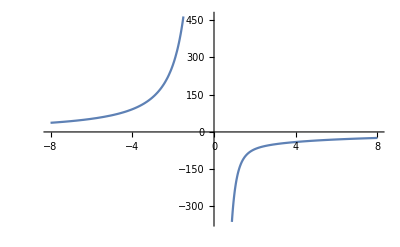

```mathematica
Plot[-0.0025052450571775384-417.3541643949977/y^3+406.7985773051824/y^2-237.6335864170211/y,{y,-8,8}]
```

Figure showing the evolution of the U_i values for increasing N_ϕ, first showing the full range, next a zoomed in look.

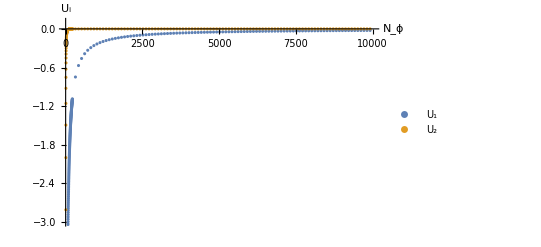

```mathematica
ListPlot[{U1value10000in100steps,U2value10000in100steps}, PlotRange->{{ 0, 10000 }, { -3, 0.1}}, PlotLegends->{"u_1", "u_2"}, AxesLabel->{"N_ϕ", "u_i"}]
```

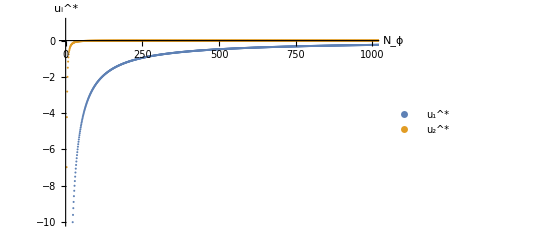

```mathematica
ListPlot[{U1value,U2value}, PlotRange->{{ 0, 1001 }, { -10, 1}}, PlotLegends->{"u_1^*", "u_2^*"}, AxesLabel->{"N_ϕ", "u_i^*"}]
```

```mathematica
Export["NGFP2trackfppositionuvaluesphi4d4labelok.jpg", %, "JPEG"]
```

NGFP2trackfppositionuvaluesphi4d4labelok.jpg

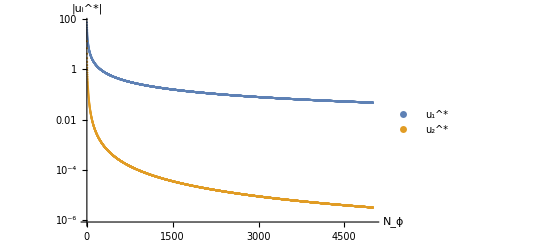

NGFP2trackfppositionuvaluesphi4d4LOGplotlabelok.jpg

```mathematica
ListLogPlot[{Abs[U1value],Abs[U2value]}, PlotLegends->{"u_1^*", "u_2^*"}, AxesLabel->{"N_ϕ", "|u_i^*|"}]
Export["NGFP2trackfppositionuvaluesphi4d4LOGplotlabelok.jpg", %, "JPEG"]
```

```mathematica
FindFormula[U1value]
```

Piecewise[{{-48.6352+58.1255 Log[Log[#1]]-9.3416 Log[#1]+0.000555789 #1, 2.≤#1<1352.55}, {-2.15057+0.290212 Log[#1]-0.0000874736 #1, 1352.55≤#1<2000.}, {0, True}}]&

```mathematica
FindFormula[U2value]
```

Piecewise[{{-4.77853+6.58129 Log[Log[#1]]-1.14738 Log[#1], 2.≤#1<1843.33}, {2.2507×10^-8 #1, 1843.33≤#1<2000.}, {0, True}}]&

```mathematica
FindFormula[U1value, N]
```

Piecewise[{{-67.1583-0.449061 N+0.00221112 N^2-4.75589×10^-6 N^3+20.1701 Log[N], 2.≤N<126.453}, {-2.89055+0.00209058 N-1.2638×10^-9 N^3+0.24335 Log[N], 126.453≤N<1002.}, {-2.28973-0.0000778205 N-6.44952×10^-9 N^2+0.309274 Log[N], 1002.≤N<2000.}, {0, True}}]

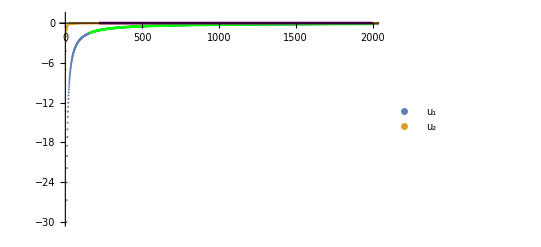

```mathematica
Show[ListPlot[{U1value,U2value}, PlotLegends->{"u_1", "u_2"}], Plot[Fitfunction, {y,0, 2000}, PlotStyle->Green ],  Plot[Fitfunction2, {y,2, 2000}, PlotStyle->Purple], PlotRange->{{ 2, 2000 }, { -30, 1}}]
```

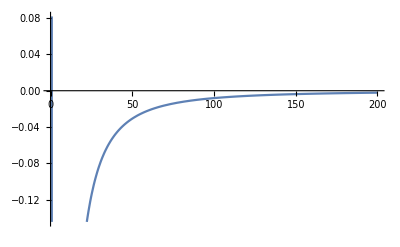

```mathematica
Plot[Fitfunction2, {y,0, 200} ]
```

#### Plot the anomalous dimension

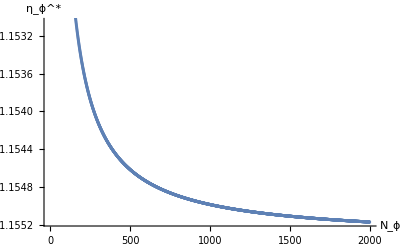

```mathematica
ListPlot[AnomalousDimd4phi4,  AxesLabel->{"N_ϕ", "η_ϕ^*"}]
```

### Generating the eigenvalues for increasing N_ϕ

Secondly, the eigenvalues have to be determined

```mathematica
EVtheta1 = {};(*Make empty lists to collect the result in*)
EVtheta2 = {};
EV={}
Do[S=FPSolgen/. Nphi-> x;(*Substitute Nphi with x*)
sols = S /.(lhs_->rhs_):>lhs->N[rhs];(*Get numerical solution*)
ηϕ/. Nphi-> x/.sols[[]];(*Finds anomalous dimension, not needed here*)
EVsd=EVs/. Nphi-> x/. sols[[]];(*Gets the eigenvalues corresponding to the Subscript[N, ϕ] value*)
EV =Append[EV,{ -EVsd[[3]]}];(*Add -the third component of the eigenvalues of stability matrix (the Subscript[θ, i]), to the EV list*)
EVs3 = EVsd[[3]];(*Save third component eigenvalues of stability matrix (*)
theta1 = -EVs3[[1]];(*Get Subscript[θ, 1] from the ev-list*)
theta2 = -EVs3[[2]];(*Get Subscript[θ, 2] from the ev-list*)
 EVtheta1 = Append[EVtheta1,{x,theta1}];(*Save Subscript[θ, 1]*)
 EVtheta2 = Append[EVtheta2,{x,theta2}], {x,2, 218}]
Do[S=FPSolgen/. Nphi-> x;
sols = S /.(lhs_->rhs_):>lhs->N[rhs];
ηϕ/. Nphi-> x/.sols[[]];
EVsd=EVs/. Nphi-> x/. sols[[]];
EV =Append[EV,{ -EVsd[[7]]}];
EVs7 = EVsd[[7]];
theta1 = -EVs7[[1]];
theta2 = -EVs7[[2]];
 EVtheta1 = Append[EVtheta1,{x,theta1}];
 EVtheta2 = Append[EVtheta2,{x,theta2}], {x,219, 2000}](*2 do loops for the two different regions, that work the same as the one to save the fixed point coordinates, only this saves the eigenvalues*)
```

{}

$Aborted

#### Save the θ_i for easy later use

Save the θ_i so later they can easily be recovered

```mathematica
DumpSave["FPphi4d4EV1.mx", EVtheta1];
DumpSave["FPphi4d4EV2.mx", EVtheta2];
```

```mathematica
DumpGet["FPphi4d4EV1.mx"];
DumpGet["FPphi4d4EV2.mx"];
```

#### Generate the actual plot for the θ_i

Plots the θ_i-value for increasing N_ϕ

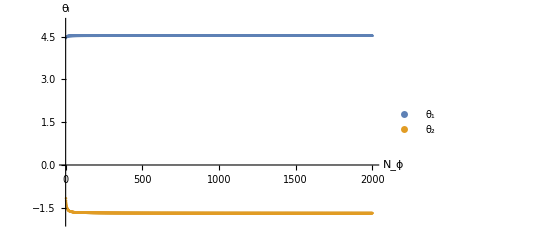

```mathematica
ListPlot[{EVtheta1,EVtheta2}, PlotRange->{{ 0, 2001 }, { -2, 5}}, PlotLegends->{"θ_1", "θ_2"}, AxesLabel->{"N_ϕ", "θ_i"}]
```

```mathematica
Export["StabilitycoefficientsofNGFP2ford4andincreasingNscalarfields.jpg", %, "JPEG"]
```

StabilitycoefficientsofNGFP2ford4andincreasingNscalarfields.jpg

## Large N_ϕ expansion

From the figures showing the evolution of U_i and θ_i it looks like the function asymptotes to a constant for very large N_ϕ. This means it should be possible to make a quite good large N_ϕ-expansion.

## Expanding the fixed points

```mathematica
Clear[ηϕ];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[βϕ];
```

```mathematica
U1ExpPhi4d4 = U[4, Nphi, 1]-> U4[1,1] Nphi^-1+ U4[1,2] Nphi^-2+ U4[1,3] Nphi^-3;
U2ExpPhi4d4 = U[4, Nphi, 2]-> U4[2,1] Nphi^-1+ U4[2,2] Nphi^-2+ U4[2,3] Nphi^-3
```

U[4,Nphi,2]→U4[2,1]/Nphi+U4[2,2]/Nphi^2+U4[2,3]/Nphi^3

```mathematica
RHSphi4d4Exp = Normal[Series[RHSphi4/. U1ExpPhi4d4/.U2ExpPhi4d4, {Nphi, ∞, 1}]];
LHSphi4d4Exp = Normal[Series[LHSfinalphi4/. U1ExpPhi4d4/.U2ExpPhi4d4, {Nphi, ∞, 1}]];
```

```mathematica
ηϕ4Exp = Normal[Series[ηϕ/. Solve[Simplify[Coefficient[RHSphi4d4Exp, X, 1]]==Coefficient[LHSphi4d4Exp, X, 1], ηϕ], {Nphi, ∞, 0}]]
```

{(8 (4 U4[1,1]+U4[2,1]))/(768 π^2+4 U4[1,1]+U4[2,1])}

```mathematica
ηϕ= ηϕ4Exp[[1]]
βϕ[4,Nphi, 1]= 0;(*Both beta functions appearing in ∂_t Subscript[F, k] are set to 0*)
βϕ[4,Nphi, 2]=0;
FPSolExpd4= Solve[Simplify[Coefficient[RHSphi4d4Exp, X, 2]]==Coefficient[LHSphi4d4Exp, X, 2]&&Simplify[Coefficient[RHSphi4d4Exp,S2]]==Coefficient[LHSphi4d4Exp, S2]/. k-> 1, {U4[1, 1], U4[ 2,1]}]
```

(8 (4 U4[1,1]+U4[2,1]))/(768 π^2+4 U4[1,1]+U4[2,1])

{{U4[1,1]→0,U4[2,1]→0},{U4[1,1]→64 (-20-√385) π^2,U4[2,1]→0},{U4[1,1]→64 (-20+√385) π^2,U4[2,1]→0},{U4[1,1]→192 π^2,U4[2,1]→-768 π^2},{U4[1,1]→128 (20+√385) π^2,U4[2,1]→768 (-20-√385) π^2},{U4[1,1]→128 (20-√385) π^2,U4[2,1]→768 (-20+√385) π^2}}

```mathematica
FPSolExpd4/.(lhs_->rhs_):>lhs->N[rhs]
```

{{U4[1,1]→0.,U4[2,1]→0.},{U4[1,1]→-25027.1,U4[2,1]→0.},{U4[1,1]→-239.134,U4[2,1]→0.},{U4[1,1]→1894.96,U4[2,1]→-7579.86},{U4[1,1]→50054.1,U4[2,1]→-300325.},{U4[1,1]→478.268,U4[2,1]→-2869.61}}

Check with fit which solution to take

```mathematica
U1value[[1999]]
```

{2000,-0.119515}

```mathematica
FitFP1phi4d4 =Fit[Take[U1value, -1000], { 1/y,1/y^2}, y]
FitFP2phi4d4 =Fit[Take[U2value, -1000], { 1/y,1/y^2}, y]
```

206.309/y^2-239.134/y

-79.6933/y^2-(2.01654×10^-6)/y

Solution 3 {U4[1,1]→-239.134,U4[2,1]→0.} looks like the one belonging to NGFP2

### Include extra order of N_ϕ

```mathematica
Clear[ηϕ];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[βϕ];
U1ExpPhi4d4ExtraOrder = U[4, Nphi, 1]-> U4[1,1] Nphi^-1+ U4[1,2] Nphi^-2+ U4[1,3] Nphi^-3;
U2ExpPhi4d4ExtraOrder = U[4, Nphi, 2]->  U4[2,2] Nphi^-2+ U4[2,3] Nphi^-3;
```

```mathematica
RHSphi4d4Exp = Normal[Series[RHSphi4/. U1ExpPhi4d4ExtraOrder/.U2ExpPhi4d4ExtraOrder , {Nphi, ∞, 2}]]
LHSphi4d4Exp = Normal[Series[LHSfinalphi4/. U1ExpPhi4d4ExtraOrder/.U2ExpPhi4d4ExtraOrder, {Nphi, ∞, 2}]];
ηϕ4Exp = Normal[Series[ηϕ/. Solve[Simplify[Coefficient[RHSphi4d4Exp, X, 1]]==Coefficient[LHSphi4d4Exp, X, 1], ηϕ], {Nphi, ∞, 0}]]
```

(k^4 Nphi (-6+ηϕ))/(192 π^2)+(X (-8+ηϕ) U4[1,1])/(192 π^2)+(-24 X^2 (-10+ηϕ) U4[1,1]^2+2 (5 k^4 X (-8+ηϕ) U4[1,1]+10 k^4 X (-8+ηϕ) U4[1,2])+5 k^4 X (-8+ηϕ) U4[2,2])/(3840 k^4 Nphi π^2)+(-4 (-10+ηϕ) ((2 S2+7 X^2) U4[1,1]^2+12 X^2 U4[1,1] U4[1,2])+2 (5 k^4 X (-8+ηϕ) U4[1,2]+10 k^4 X (-8+ηϕ) U4[1,3]-6 X^2 (-10+ηϕ) U4[1,1] U4[2,2])+5 k^4 X (-8+ηϕ) (5 U4[2,2]+U4[2,3]))/(3840 k^4 Nphi^2 π^2)

{(8 U4[1,1])/(192 π^2+U4[1,1])}

```mathematica
ηϕ= ηϕ4Exp[[1]]
βϕ[4,Nphi, 1]= 0;(*Both beta functions appearing in ∂_t Subscript[F, k] are set to 0*)
βϕ[4,Nphi, 2]=0;
FPSolExpd4= Solve[Simplify[Coefficient[Coefficient[RHSphi4d4Exp, X, 2], Nphi, -2]]==Coefficient[Coefficient[LHSphi4d4Exp, X, 2], Nphi, -2]&&Simplify[Coefficient[Coefficient[RHSphi4d4Exp,S2], Nphi, -2]]==Coefficient[Coefficient[LHSphi4d4Exp, S2], Nphi, -2]&&
Simplify[Coefficient[Coefficient[RHSphi4d4Exp, X, 2], Nphi, -1]]==Coefficient[Coefficient[LHSphi4d4Exp, X, 2], Nphi, -1]&&Simplify[Coefficient[Coefficient[RHSphi4d4Exp,S2], Nphi, -1]]==Coefficient[Coefficient[LHSphi4d4Exp, S2], Nphi, -1]/. k-> 1, {U4[1, 1],U4[1,2], U4[ 2,2]}]
```

(8 U4[1,1])/(192 π^2+U4[1,1])

{{U4[1,1]→0,U4[1,2]→0,U4[2,2]→0},{U4[1,1]→64 (-20-√385) π^2,U4[1,2]→256/3 (20+√385) π^2,U4[2,2]→64/3 (-20-√385) π^2},{U4[1,1]→64 (-20+√385) π^2,U4[1,2]→256/3 (20-√385) π^2,U4[2,2]→64/3 (-20+√385) π^2}}

```mathematica
FPSolExpd4/.(lhs_->rhs_):>lhs->N[rhs]
```

{{U4[1,1]→0.,U4[1,2]→0.,U4[2,2]→0.},{U4[1,1]→-25027.1,U4[1,2]→33369.4,U4[2,2]→-8342.35},{U4[1,1]→-239.134,U4[1,2]→318.845,U4[2,2]→-79.7113}}

Again select solution 3: {U4[1,1]→-239.134,U4[1,2]→318.845,U4[2,2]→-79.7113}

We can use these values to determine the anomalous dimension in the large N_ϕ limit as well

```mathematica
(8 U4[1,1])/(192 π^2+U4[1,1])/.U4[1,1]->-239.134
```

-1.15536

## Expand the stability matrix

### Only lowest order included

```mathematica
Bexpd4[1,1]= Normal[Series[D[βϕ[U[4,Nphi, 1], U[4,Nphi, 2]][4,Nphi, 1], U[4, Nphi, 1]]/. U1ExpPhi4d4/.U2ExpPhi4d4/.{U4[1,1]->-239.13380624549205,U4[2,1]->0.}, {Nphi, ∞, 0}]]
Bexpd4[2,1]= Normal[Series[D[βϕ[U[4,Nphi, 1], U[4,Nphi, 2]][4,Nphi, 2], U[4, Nphi, 1]]/. U1ExpPhi4d4/.U2ExpPhi4d4/.{U4[1,1]->-239.13380624549205,U4[2,1]->0.}, {Nphi, ∞, 0}]]
Bexpd4[1,2]= Normal[Series[D[βϕ[U[4,Nphi, 1], U[4,Nphi, 2]][4,Nphi, 1], U[4, Nphi, 2]]/. U1ExpPhi4d4/.U2ExpPhi4d4/.{U4[1,1]->-239.13380624549205,U4[2,1]->0.}, {Nphi, ∞, 0}]]
Bexpd4[2,2]= Normal[Series[D[βϕ[U[4,Nphi, 1], U[4,Nphi, 2]][4,Nphi, 2], U[4, Nphi, 2]]/. U1ExpPhi4d4/.U2ExpPhi4d4/.{U4[1,1]->-239.13380624549205,U4[2,1]->0.}, {Nphi, ∞, 0}]]
```

-4.53394

0

-1.55581

1.68929

```mathematica
Matphi4d4Exp = Table[Bexpd4[a,b],{a,1,2},{b,1,2}];
%//MatrixForm
Eigenvalues[Matphi4d4Exp]
```

(-4.53394 | -1.55581
0 | 1.68929)

{-4.53394,1.68929}

### Include one more order of expansion

```mathematica
Bexpd4[1,1]= Normal[Series[D[βϕ[U[4,Nphi, 1], U[4,Nphi, 2]][4,Nphi, 1], U[4, Nphi, 1]]/. U1ExpPhi4d4ExtraOrder/.U2ExpPhi4d4ExtraOrder/.{U4[1,1]->-239.134,U4[1,2]->318.845,U4[2,2]->-79.7113}, {Nphi, ∞, 1}]]
Bexpd4[2,1]= Normal[Series[D[βϕ[U[4,Nphi, 1], U[4,Nphi, 2]][4,Nphi, 2], U[4, Nphi, 1]]/. U1ExpPhi4d4ExtraOrder/.U2ExpPhi4d4ExtraOrder/.{U4[1,1]->-239.134,U4[1,2]->318.845,U4[2,2]->-79.7113}, {Nphi, ∞, 1}]]
Bexpd4[1,2]= Normal[Series[D[βϕ[U[4,Nphi, 1], U[4,Nphi, 2]][4,Nphi, 1], U[4, Nphi, 2]]/. U1ExpPhi4d4ExtraOrder/.U2ExpPhi4d4ExtraOrder/.{U4[1,1]->-239.134,U4[1,2]->318.845,U4[2,2]->-79.7113}, {Nphi, ∞, 1}]]
Bexpd4[2,2]= Normal[Series[D[βϕ[U[4,Nphi, 1], U[4,Nphi, 2]][4,Nphi, 2], U[4, Nphi, 2]]/. U1ExpPhi4d4ExtraOrder/.U2ExpPhi4d4ExtraOrder/.{U4[1,1]->-239.134,U4[1,2]->318.845,U4[2,2]->-79.7113}, {Nphi, ∞, 1}]]
```

-4.53395+5.55197/Nphi

-2.07441/Nphi

-1.55581-6.08551/Nphi

1.68929-1.16308/Nphi

```mathematica
Matphi4d4Expextra = Table[Bexpd4[a,b],{a,1,2},{b,1,2}];
%//MatrixForm
Eigenvalues[Matphi4d4Expextra]
```

(-4.53395+5.55197/Nphi | -1.55581-6.08551/Nphi
-2.07441/Nphi | 1.68929-1.16308/Nphi)

{(0.5 (4.38889-2.84466 Nphi-√(95.5873-70.6691 Nphi+38.7287 Nphi^2)))/Nphi,(0.5 (4.38889-2.84466 Nphi+√(95.5873-70.6691 Nphi+38.7287 Nphi^2)))/Nphi}

```mathematica
Series[Eigenvalues[Matphi4d4Expextra], {Nphi, ∞, 1}]
```

{-4.53395+5.03336/Nphi+O[1/Nphi]^2,1.68929-0.644476/Nphi+O[1/Nphi]^2}

```mathematica
1/4.53395
```

0.220558

### Making a fit to the data

#### Anomalous dimension fit

To find the value the anomalous dimension approaches in the large N-limit, it is fitted with a polynomial function.

```mathematica
FitAndim4phi4 =Fit[Take[AnomalousDimd4phi4, -1500], {1, 1/y, 1/y^2}, y](*Fit a polynomial to the anomalous dimension value, to see what it approaches*)
```

-1.15535-0.0552005/y^2+0.36948/y

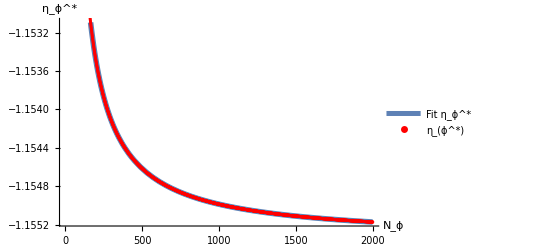

```mathematica
Show[Plot[{FitAndim4phi4},{y,1,1999},PlotStyle->{Thickness[0.01]}, PlotLegends->{"Fit η_ϕ^*"}],ListPlot[AnomalousDimd4phi4,PlotStyle->Red,  PlotLegends->{"η_(ϕ^*)"}], AxesLabel-> { "N_ϕ", "η_ϕ^*"}]
```

```mathematica
Export["Phi4IncreasingNphiAnomalousDimension+fitd4.jpg", %, "JPEG"]
```

Phi4IncreasingNphiAnomalousDimension+fitd4.jpg

#### Stability coefficients fit

Just as for the anomalous dimension, the fit function will be used to fit a polynomial of a+b/N_ϕ+ c/N_ϕ^2to the data of the stability coefficients to see what value this approaches in the limit.

```mathematica
FitEVtheta1phi4d4 =Fit[Take[EVtheta1, -1000], {1, 1/y,1/y^2}, y]
```

4.53394+0.0344253/y^2-0.191334/y

```mathematica
FitEVtheta2phi4d4 =Fit[Take[EVtheta2, -1000], {1, 1/y, 1/y^2}, y]
```

-1.68929-1.95207/y^2+1.88883/y

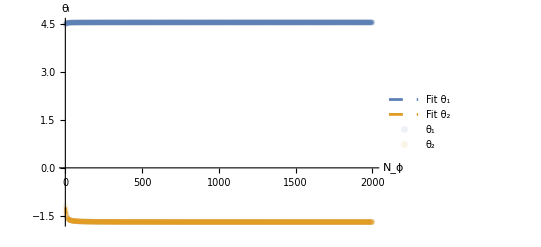

Phi4IncreasingNphiStabCoeff+fitd4.jpg

```mathematica
Show[Plot[{FitEVtheta1phi4d4, FitEVtheta2phi4d4 },{y,2,2001}, PlotLegends-> {"Fit θ_1", "Fit θ_2"}, PlotStyle->{{RGBColor[0.368417,0.506779,0.709798],Dashed}, {RGBColor[0.880722,0.611041,0.142051],Dashed}}],ListPlot[{EVtheta1, EVtheta2},PlotStyle->{{Opacity[0.1,RGBColor[0.368417,0.506779,0.709798]],PointSize[0.01]}, {Opacity[0.1,RGBColor[0.880722,0.611041,0.142051]],PointSize[0.01]}},  PlotLegends->{"θ_1", "θ_2"}], AxesLabel->{"N_ϕ","θ_i"}]
(*Export["Phi4IncreasingNphiStabCoeff+fitd4.jpg", %, "JPEG"]*)
```

## Making figures

### Anomalous dimension

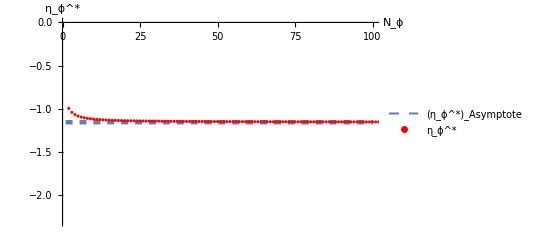

Phi4IncreasingNphiAnomalousDimension+Expansiond4.jpg

```mathematica
Show[Plot[{y=-1.1553552888874055},{y,1,100},PlotStyle->{Thickness[0.008], Dashed},PlotLegends->{"(η_ϕ^*)_Asymptote"}],ListPlot[AnomalousDimd4phi4,PlotStyle->Red,  PlotLegends->{"η_ϕ^*"}], AxesLabel-> { "N_ϕ", "η_ϕ^*"}]
Export["Phi4IncreasingNphiAnomalousDimension+Expansiond4.jpg", %, "JPEG"]
```

### Stability coefficients

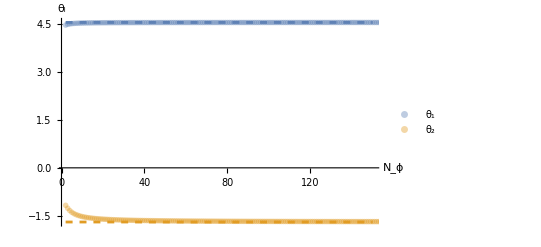

Phi4IncreasingNphiStabCoeff+Expansiond4.jpg

```mathematica
Show[Plot[{y=4.533945684531606, y= -1.6892894222251889},{y,2,150}, (*PlotLegends-> {"θ_(1,  Asymptote)", "θ_(2 Asymptote)"},*) PlotStyle->{{RGBColor[0.368417,0.506779,0.709798],Dashed}, {RGBColor[0.880722,0.611041,0.142051],Dashed}}],ListPlot[{EVtheta1, EVtheta2},PlotStyle->{{Opacity[0.4,RGBColor[0.368417,0.506779,0.709798]],PointSize[0.01]}, {Opacity[0.4,RGBColor[0.880722,0.611041,0.142051]],PointSize[0.01]}},  PlotLegends->{"θ_1", "θ_2"}], AxesLabel->{"N_ϕ","θ_i"}]
Export["Phi4IncreasingNphiStabCoeff+Expansiond4.jpg", %, "JPEG"]
```

# Finding Fixed Points O(ϕ^6), d=4

In the section above an order ϕ^4 expansion was made. It would however be nice to increase to a higher order and see how these new basis elements will influence the system.  This means an order ϕ^6 expansion.

## Set Up

```mathematica
Clear[ηϕ];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[β];
```

For the order ϕ^6expansion, the average effective action is given by Γ_k= X+U_1 k^-4 X^2+U_2 k^-4 S_2+U_3 k^-8 X^3+U_4 k^-8 X S_2+U_5 k^-8 S_3 with S_2 and S_3 the two and three X-strings (S_2=X_μ^ν X_ν^μ).  In this notebook
First we import the solution for the right hand side of the Wetterich equation for 4 dimensions up to order ϕ^6 from the notebook 2024-1-15 multiple scalar fields xact file generalized attempt.nb:

```mathematica
RHScollectedd4order6ONLY=1/(23040 k^8 π^2)X^3 (8 (49+24 Nphi) U[6, Nphi, 1]^3 (-12+ηϕ)+72 (13+2 Nphi) U[6, Nphi, 1]^2 U[6, Nphi, 2] (-12+ηϕ)+24 (16+Nphi) U[6, Nphi, 1] U[6, Nphi, 2]^2 (-12+ηϕ)+(31+Nphi) U[6, Nphi, 2]^3 (-12+ηϕ)-6 U[6, Nphi, 2] (24 U[6, Nphi, 3] +2 (15+Nphi) U[6, Nphi, 4]+3 U[6, Nphi, 5]) (-10+ηϕ)-12 U[6, Nphi, 1] (48 U[6, Nphi, 3]+(34+6 Nphi) U[6, Nphi, 4]+9 U[6, Nphi, 5]) (-10+ηϕ))+1/(3840 k^12 π^2)X(k^4 S2(40 U[6, Nphi, 1]^3 (-12+ηϕ)+200 U[6, Nphi, 1]^2 U[6, Nphi, 2] (-12+ηϕ)+8 (28+Nphi) U[6, Nphi, 1] U[6, Nphi, 2]^2 (-12+ηϕ)+(51+Nphi) U[6, Nphi, 2]^3 (-12+ηϕ)-2U[6, Nphi, 1] (24 U[6, Nphi, 3]+58 U[6, Nphi, 4]+12 Nphi U[6, Nphi, 4]+66 U[6, Nphi, 5]+9 Nphi U[6, Nphi, 5]) (-10+ηϕ)-U[6, Nphi, 2](120 U[6, Nphi, 3]+10 (13+Nphi) U[6, Nphi, 4]+3 (26+Nphi) U[6, Nphi, 5]) (-10+ηϕ))+5 k^12 ((2+4 Nphi) U[6, Nphi, 1]+(5+Nphi) U[6, Nphi, 2]) (-8+ηϕ)-18 k^4 ((2+4 Nphi) U[6, Nphi, 1]+(5+Nphi) U[6, Nphi, 2]) U[6, Nphi, 3] (-10+ηϕ) X^2)-1/(15360 k^12 π^2)X^2(2 k^8 (8 (7+6 Nphi) U[6, Nphi, 1]^2 (-10+ηϕ)+8 (17+3 Nphi) U[6, Nphi, 1] U[6, Nphi, 2](-10+ηϕ)+2 (15+Nphi) U[6, Nphi, 2]^2 (-10+ηϕ)-5 (12 U[6, Nphi, 3]+2 (5+Nphi)U[6, Nphi, 4]+3 U[6, Nphi, 5]) (-8+ηϕ)))-1/(46080 k^12 π^2)(-8 k^4 S3 (6 U[6, Nphi, 1](36 U[6, Nphi, 2]^2 (-12+ηϕ)-(8 U[6, Nphi, 4]+21 U[6, Nphi, 5]) (-10+ηϕ))+16 U[6, Nphi, 1]^3 (-12+ηϕ)+96 U[6, Nphi, 1]^2 U[6, Nphi, 2](-12+ηϕ)+2 (67+Nphi) U[6, Nphi, 2]^3 (-12+ηϕ)-3 U[6, Nphi, 2](40 U[6, Nphi, 4]+3 (27+Nphi) U[6, Nphi, 5]) (-10+ηϕ))+6 k^8 S2(16 U[6, Nphi, 1]^2 (-10+ηϕ)+80 U[6, Nphi, 1]U[6, Nphi, 2] (-10+ηϕ)+4 (21+Nphi) U[6, Nphi, 2]^2 (-10+ηϕ)-5 (4 (2+Nphi) U[6, Nphi, 4]+3 (6+Nphi) U[6, Nphi, 5]) (-8+ηϕ))+240 k^16 Nphi (-6+ηϕ)-36 U[6, Nphi, 3](10 k^8 Nphi (-8+ηϕ)) X^2);
```

Next we define the Left Hand Side of the Wetterich equation as well. This is given by ∂_t Γ_k:

```mathematica
LHScollectedd4order6ONLY=-ηϕ X +(-2U[6, Nphi, 1] ηϕ -4U[6, Nphi, 1]+β[6, Nphi, 1])X^2/k^4+(-2U[6, Nphi, 2] ηϕ -4U[6, Nphi, 2]+β[6, Nphi, 2])S2/k^4+(-3U[6, Nphi, 3] ηϕ -8U[6, Nphi, 3]+β[6, Nphi, 3])X^3/k^8+(-3U[6, Nphi, 4] ηϕ -8U[6, Nphi, 4]+β[6, Nphi, 4])(X S2)/k^8+(-3U[6, Nphi, 5] ηϕ -8U[6, Nphi, 5]+β[6, Nphi, 5])S3/k^8;
```

```mathematica
Solve[Coefficient[Coefficient[LHScollectedd4order6ONLY, X],S2, 0]== Coefficient[Coefficient[RHScollectedd4order6ONLY, X],S2, 0], ηϕ]
```

Solve::ivar: (7 ((2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))/(105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]) is not a valid variable.

Solve[-(7 ((2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))/(105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])==-U[6,Nphi,1]/(48 π^2)-(Nphi U[6,Nphi,1])/(24 π^2)-(5 U[6,Nphi,2])/(96 π^2)-(Nphi U[6,Nphi,2])/(96 π^2)+(7 U[6,Nphi,1] U3[6,Nphi,1])/(192 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))+(49 Nphi U[6,Nphi,1] U3[6,Nphi,1])/(384 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))+(7 Nphi^2 U[6,Nphi,1] U3[6,Nphi,1])/(64 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))+(35 U[6,Nphi,2] U3[6,Nphi,1])/(384 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))+(119 Nphi U[6,Nphi,2] U3[6,Nphi,1])/(768 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))+(7 Nphi^2 U[6,Nphi,2] U3[6,Nphi,1])/(256 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))+(7 U[6,Nphi,1] U3[6,Nphi,2])/(96 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))+(21 Nphi U[6,Nphi,1] U3[6,Nphi,2])/(128 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))+(7 Nphi^2 U[6,Nphi,1] U3[6,Nphi,2])/(192 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))+(35 U[6,Nphi,2] U3[6,Nphi,2])/(192 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))+(21 Nphi U[6,Nphi,2] U3[6,Nphi,2])/(256 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))+(7 Nphi^2 U[6,Nphi,2] U3[6,Nphi,2])/(768 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])),(7 ((2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))/(105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])]

As expected, the anomalous dimension is the same as for the order ϕ^4 expansion in 4 dimensions, which is good since this corresponds to the expectations

## Finding Fixed point + Beta functions

## Generalized solution

First make sure the anomalous dimension is defined.  As said before, this is the same as in the order ϕ^4-expansion which is really nice.

```mathematica
ηϕ= (8 (2 U[6,Nphi,1]+4 Nphi U[6,Nphi,1]+5 U[6,Nphi,2]+Nphi U[6,Nphi,2]))/(768 π^2+2 U[6,Nphi,1]+4 Nphi U[6,Nphi,1]+5 U[6,Nphi,2]+Nphi U[6,Nphi,2]);
```

### Fixed points

To find the fixed points, we should first set the beta functions to zero.

```mathematica
β[6, Nphi, 1]=0;(*Set all appearing beta functions to zero *)
β[6, Nphi, 2]=0;
β[6, Nphi, 3]=0;
β[6, Nphi, 4]=0;
β[6, Nphi, 5]=0;
```

#### Solve in 2 steps

First solve the terms with the highest order of ϕ: {X^3, S_2 X, S_3}.

```mathematica
U345solved4phi6=Simplify[Solve[Coefficient[k^8 LHScollectedd4order6ONLY, X, 3]== Coefficient[k^8 RHScollectedd4order6ONLY, X,3]&&Coefficient[k^8 LHScollectedd4order6ONLY, S3]==Coefficient[k^8 RHScollectedd4order6ONLY, S3]&&Simplify[k^8 Coefficient[Coefficient[LHScollectedd4order6ONLY, S2],X]]== Simplify[k^8 Coefficient[Coefficient[RHScollectedd4order6ONLY, S2],X]], {U[6, Nphi, 3], U[6, Nphi, 4],U[6, Nphi, 5]}]];
```

```mathematica
RHSCollectedU1=Coefficient[k^4 RHScollectedd4order6ONLY, X,2]/.U345solved4phi6//Collect[#, {k}, Simplify]&;(*This function replaces the Subscript[U, 3], Subscript[U, 4], Subscript[U, 5] in the Subscript[U, 1] equation with the equation derived for it by  the function U345solved4phi6*)
```

```mathematica
RHSCollectedU2=Coefficient[Coefficient[k^4 RHScollectedd4order6ONLY, S2,1],X, 0]/.U345solved4phi6//Collect[#, {k}, Simplify]&;(*This function replaces the Subscript[U, 3], Subscript[U, 4], Subscript[U, 5] in the Subscript[U, 2] equation with the equation derived for it by  the function U345solved4phi6*)
```

Looking at the two equations RHSCollectedU1 and RHSCollectedU2, it becomes clear that these are coupled 8^th order polynomials. This is very difficult to solve exact, hence it will be necessary to define N_ϕ and do a numerical evaluation for this part of the problem. Since the ϕ^4-evaluation has already taken place, those solutions can be compared to the newly generated solutions.

```mathematica
(*U12solvedd4phi6=Solve[Coefficient[k^4 LHScollectedd4order6ONLY, X, 2]== RHSCollectedU1&&Coefficient[Coefficient[k^4 LHScollectedd4order6ONLY, S2, 1], X, 0]==  RHSCollectedU2, {U[4, Nphi, 1], U[4, Nphi, 2]}]*)
```

### Beta functions

Now the fixed points are known,the next step is to determine the beta functions

```mathematica
Clear[β] (*Since for the fixed point evaluation beta was set to zero, it must be cleared so the equation governing its evolution can be found*)
```

```mathematica
Simplify[Solve[Coefficient[k^8 LHScollectedd4order6ONLY, S3]==Coefficient[k^8 RHScollectedd4order6ONLY, S3]/.k-> 1, β[6, Nphi, 5]]]
```

{{β[6,Nphi,5]→-((64 (1+2 Nphi) U[6,Nphi,1]^4+9216 (67+Nphi) π^2 U[6,Nphi,2]^3+4 (335+72 Nphi+Nphi^2) U[6,Nphi,2]^4+32 U[6,Nphi,1]^3 (2304 π^2+(17+25 Nphi) U[6,Nphi,2])-17694720 π^4 U[6,Nphi,5]-11520 π^2 U[6,Nphi,2] (40 U[6,Nphi,4]+11 (11+Nphi) U[6,Nphi,5])-3 (5+Nphi) U[6,Nphi,2]^2 (40 U[6,Nphi,4]+3 (27+Nphi) U[6,Nphi,5])+12 U[6,Nphi,1]^2 (36864 π^2 U[6,Nphi,2]+8 (19+20 Nphi) U[6,Nphi,2]^2-(1+2 Nphi) (8 U[6,Nphi,4]+21 U[6,Nphi,5]))+4 U[6,Nphi,1] (248832 π^2 U[6,Nphi,2]^2+(674+378 Nphi+4 Nphi^2) U[6,Nphi,2]^3-5760 π^2 (8 U[6,Nphi,4]+(29+16 Nphi) U[6,Nphi,5])-3 U[6,Nphi,2] ((40+44 Nphi) U[6,Nphi,4]+3 (31+31 Nphi+Nphi^2) U[6,Nphi,5])))/(2880 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])))}}

```mathematica
β[U_[6, Nphi, 1], U_[6, Nphi, 2], U_[6, Nphi, 3], U_[6, Nphi, 4], U_[6, Nphi, 5]][6,Nphi,5]=-((64 (1+2 Nphi) U[6,Nphi,1]^4+9216 (67+Nphi) π^2 U[6,Nphi,2]^3+4 (335+72 Nphi+Nphi^2) U[6,Nphi,2]^4+32 U[6,Nphi,1]^3 (2304 π^2+(17+25 Nphi) U[6,Nphi,2])-17694720 π^4 U[6,Nphi,5]-11520 π^2 U[6,Nphi,2] (40 U[6,Nphi,4]+11 (11+Nphi) U[6,Nphi,5])-3 (5+Nphi) U[6,Nphi,2]^2 (40 U[6,Nphi,4]+3 (27+Nphi) U[6,Nphi,5])+12 U[6,Nphi,1]^2 (36864 π^2 U[6,Nphi,2]+8 (19+20 Nphi) U[6,Nphi,2]^2-(1+2 Nphi) (8 U[6,Nphi,4]+21 U[6,Nphi,5]))+4 U[6,Nphi,1] (248832 π^2 U[6,Nphi,2]^2+(674+378 Nphi+4 Nphi^2) U[6,Nphi,2]^3-5760 π^2 (8 U[6,Nphi,4]+(29+16 Nphi) U[6,Nphi,5])-3 U[6,Nphi,2] ((40+44 Nphi) U[6,Nphi,4]+3 (31+31 Nphi+Nphi^2) U[6,Nphi,5])))/(2880 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])));
```

```mathematica
Simplify[Solve[Simplify[k^8 Coefficient[Coefficient[LHScollectedd4order6ONLY, S2],X]]== Simplify[k^8 Coefficient[Coefficient[RHScollectedd4order6ONLY, S2],X]], β[6, Nphi, 4]]]
```

{{β[6,Nphi,4]→(-160 (1+2 Nphi) U[6,Nphi,1]^4-4608 (51+Nphi) π^2 U[6,Nphi,2]^3-2 (255+56 Nphi+Nphi^2) U[6,Nphi,2]^4-240 U[6,Nphi,1]^3 (768 π^2+(5+7 Nphi) U[6,Nphi,2])+11796480 π^4 U[6,Nphi,4]+(5+Nphi) U[6,Nphi,2]^2 (120 U[6,Nphi,3]+10 (13+Nphi) U[6,Nphi,4]+3 (26+Nphi) U[6,Nphi,5])+3840 π^2 U[6,Nphi,2] (120 U[6,Nphi,3]+(210+26 Nphi) U[6,Nphi,4]+3 (26+Nphi) U[6,Nphi,5])+4 U[6,Nphi,1]^2 (-230400 π^2 U[6,Nphi,2]-4 (181+139 Nphi+4 Nphi^2) U[6,Nphi,2]^2+(1+2 Nphi) (24 U[6,Nphi,3]+2 (29+6 Nphi) U[6,Nphi,4]+3 (22+3 Nphi) U[6,Nphi,5]))+U[6,Nphi,1] (-36864 (28+Nphi) π^2 U[6,Nphi,2]^2-4 (611+235 Nphi+6 Nphi^2) U[6,Nphi,2]^3+7680 π^2 (24 U[6,Nphi,3]+(74+44 Nphi) U[6,Nphi,4]+3 (22+3 Nphi) U[6,Nphi,5])+U[6,Nphi,2] (48 (10+11 Nphi) U[6,Nphi,3]+8 (105+97 Nphi+8 Nphi^2) U[6,Nphi,4]+6 (136+90 Nphi+5 Nphi^2) U[6,Nphi,5])))/(1920 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]))}}

```mathematica
β[U_[6, Nphi, 1], U_[6, Nphi, 2], U_[6, Nphi, 3], U_[6, Nphi, 4], U_[6, Nphi, 5]][6,Nphi,4]=(-160 (1+2 Nphi) U[6,Nphi,1]^4-4608 (51+Nphi) π^2 U[6,Nphi,2]^3-2 (255+56 Nphi+Nphi^2) U[6,Nphi,2]^4-240 U[6,Nphi,1]^3 (768 π^2+(5+7 Nphi) U[6,Nphi,2])+11796480 π^4 U[6,Nphi,4]+(5+Nphi) U[6,Nphi,2]^2 (120 U[6,Nphi,3]+10 (13+Nphi) U[6,Nphi,4]+3 (26+Nphi) U[6,Nphi,5])+3840 π^2 U[6,Nphi,2] (120 U[6,Nphi,3]+(210+26 Nphi) U[6,Nphi,4]+3 (26+Nphi) U[6,Nphi,5])+4 U[6,Nphi,1]^2 (-230400 π^2 U[6,Nphi,2]-4 (181+139 Nphi+4 Nphi^2) U[6,Nphi,2]^2+(1+2 Nphi) (24 U[6,Nphi,3]+2 (29+6 Nphi) U[6,Nphi,4]+3 (22+3 Nphi) U[6,Nphi,5]))+U[6,Nphi,1] (-36864 (28+Nphi) π^2 U[6,Nphi,2]^2-4 (611+235 Nphi+6 Nphi^2) U[6,Nphi,2]^3+7680 π^2 (24 U[6,Nphi,3]+(74+44 Nphi) U[6,Nphi,4]+3 (22+3 Nphi) U[6,Nphi,5])+U[6,Nphi,2] (48 (10+11 Nphi) U[6,Nphi,3]+8 (105+97 Nphi+8 Nphi^2) U[6,Nphi,4]+6 (136+90 Nphi+5 Nphi^2) U[6,Nphi,5])))/(1920 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]));
```

```mathematica
Simplify[Solve[Coefficient[k^8 LHScollectedd4order6ONLY, X, 3]== Coefficient[k^8 RHScollectedd4order6ONLY, X,3], β[6, Nphi, 3]]]
```

{{β[6,Nphi,3]→(-16 (49+122 Nphi+48 Nphi^2) U[6,Nphi,1]^4-2304 (31+Nphi) π^2 U[6,Nphi,2]^3-(155+36 Nphi+Nphi^2) U[6,Nphi,2]^4-8 U[6,Nphi,1]^3 (2304 (49+24 Nphi) π^2+(479+673 Nphi+96 Nphi^2) U[6,Nphi,2])+35389440 π^4 U[6,Nphi,3]+3 (5+Nphi) U[6,Nphi,2]^2 (6 (19+3 Nphi) U[6,Nphi,3]+2 (15+Nphi) U[6,Nphi,4]+3 U[6,Nphi,5])+11520 π^2 U[6,Nphi,2] (2 (97+17 Nphi) U[6,Nphi,3]+2 (15+Nphi) U[6,Nphi,4]+3 U[6,Nphi,5])-12 U[6,Nphi,1]^2 (13824 (13+2 Nphi) π^2 U[6,Nphi,2]+(454+270 Nphi+20 Nphi^2) U[6,Nphi,2]^2-(1+2 Nphi) (6 (11+6 Nphi) U[6,Nphi,3]+(34+6 Nphi) U[6,Nphi,4]+9 U[6,Nphi,5]))+U[6,Nphi,1] (-55296 (16+Nphi) π^2 U[6,Nphi,2]^2-2 (991+315 Nphi+14 Nphi^2) U[6,Nphi,2]^3+23040 π^2 ((82+68 Nphi) U[6,Nphi,3]+(34+6 Nphi) U[6,Nphi,4]+9 U[6,Nphi,5])+6 U[6,Nphi,2] (12 (37+41 Nphi+6 Nphi^2) U[6,Nphi,3]+2 (100+63 Nphi+5 Nphi^2) U[6,Nphi,4]+3 (16+5 Nphi) U[6,Nphi,5])))/(5760 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]))}}

```mathematica
β[U_[6, Nphi, 1], U_[6, Nphi, 2], U_[6, Nphi, 3], U_[6, Nphi, 4], U_[6, Nphi, 5]][6,Nphi,3]=(-16 (49+122 Nphi+48 Nphi^2) U[6,Nphi,1]^4-2304 (31+Nphi) π^2 U[6,Nphi,2]^3-(155+36 Nphi+Nphi^2) U[6,Nphi,2]^4-8 U[6,Nphi,1]^3 (2304 (49+24 Nphi) π^2+(479+673 Nphi+96 Nphi^2) U[6,Nphi,2])+35389440 π^4 U[6,Nphi,3]+3 (5+Nphi) U[6,Nphi,2]^2 (6 (19+3 Nphi) U[6,Nphi,3]+2 (15+Nphi) U[6,Nphi,4]+3 U[6,Nphi,5])+11520 π^2 U[6,Nphi,2] (2 (97+17 Nphi) U[6,Nphi,3]+2 (15+Nphi) U[6,Nphi,4]+3 U[6,Nphi,5])-12 U[6,Nphi,1]^2 (13824 (13+2 Nphi) π^2 U[6,Nphi,2]+(454+270 Nphi+20 Nphi^2) U[6,Nphi,2]^2-(1+2 Nphi) (6 (11+6 Nphi) U[6,Nphi,3]+(34+6 Nphi) U[6,Nphi,4]+9 U[6,Nphi,5]))+U[6,Nphi,1] (-55296 (16+Nphi) π^2 U[6,Nphi,2]^2-2 (991+315 Nphi+14 Nphi^2) U[6,Nphi,2]^3+23040 π^2 ((82+68 Nphi) U[6,Nphi,3]+(34+6 Nphi) U[6,Nphi,4]+9 U[6,Nphi,5])+6 U[6,Nphi,2] (12 (37+41 Nphi+6 Nphi^2) U[6,Nphi,3]+2 (100+63 Nphi+5 Nphi^2) U[6,Nphi,4]+3 (16+5 Nphi) U[6,Nphi,5])))/(5760 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]));
```

```mathematica
Simplify[Solve[Simplify[k^8 Coefficient[Coefficient[LHScollectedd4order6ONLY, S2],X, 0]]== Simplify[k^8 Coefficient[Coefficient[RHScollectedd4order6ONLY, S2],X,0]], β[6, Nphi, 2]]]
```

{{β[6,Nphi,2]→(8 (1+2 Nphi) U[6,Nphi,1]^3+2949120 π^4 U[6,Nphi,2]+7680 (23+3 Nphi) π^2 U[6,Nphi,2]^2+(105+26 Nphi+Nphi^2) U[6,Nphi,2]^3+12 U[6,Nphi,1]^2 (1280 π^2+(5+7 Nphi) U[6,Nphi,2])+2 U[6,Nphi,1] U[6,Nphi,2] (19200 (3+2 Nphi) π^2+(71+53 Nphi+2 Nphi^2) U[6,Nphi,2])-3840 π^2 (4 (2+Nphi) U[6,Nphi,4]+3 (6+Nphi) U[6,Nphi,5]))/(960 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]))}}

```mathematica
β[U_[6, Nphi, 1], U_[6, Nphi, 2], U_[6, Nphi, 3], U_[6, Nphi, 4], U_[6, Nphi, 5]][6,Nphi,2]=(8 (1+2 Nphi) U[6,Nphi,1]^3+2949120 π^4 U[6,Nphi,2]+7680 (23+3 Nphi) π^2 U[6,Nphi,2]^2+(105+26 Nphi+Nphi^2) U[6,Nphi,2]^3+12 U[6,Nphi,1]^2 (1280 π^2+(5+7 Nphi) U[6,Nphi,2])+2 U[6,Nphi,1] U[6,Nphi,2] (19200 (3+2 Nphi) π^2+(71+53 Nphi+2 Nphi^2) U[6,Nphi,2])-3840 π^2 (4 (2+Nphi) U[6,Nphi,4]+3 (6+Nphi) U[6,Nphi,5]))/(960 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]));
```

```mathematica
Simplify[Solve[Coefficient[k^4 LHScollectedd4order6ONLY, X, 2]==Coefficient[k^4 RHScollectedd4order6ONLY, X,2]/. k->1 , β[6, Nphi, 1]]]
```

{{β[6,Nphi,1]→(8 (7+20 Nphi+12 Nphi^2) U[6,Nphi,1]^3+3840 (15+Nphi) π^2 U[6,Nphi,2]^2+(75+20 Nphi+Nphi^2) U[6,Nphi,2]^3+12 U[6,Nphi,1]^2 (5120 (3+4 Nphi) π^2+(23+37 Nphi+6 Nphi^2) U[6,Nphi,2])+2 U[6,Nphi,1] (2949120 π^4+3840 (59+11 Nphi) π^2 U[6,Nphi,2]+(185+95 Nphi+8 Nphi^2) U[6,Nphi,2]^2)-7680 π^2 (12 (1+Nphi) U[6,Nphi,3]+2 (5+Nphi) U[6,Nphi,4]+3 U[6,Nphi,5]))/(1920 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]))}}

```mathematica
β[U_[6, Nphi, 1], U_[6, Nphi, 2], U_[6, Nphi, 3], U_[6, Nphi, 4], U_[6, Nphi, 5]][6,Nphi,1]=(8 (7+20 Nphi+12 Nphi^2) U[6,Nphi,1]^3+3840 (15+Nphi) π^2 U[6,Nphi,2]^2+(75+20 Nphi+Nphi^2) U[6,Nphi,2]^3+12 U[6,Nphi,1]^2 (5120 (3+4 Nphi) π^2+(23+37 Nphi+6 Nphi^2) U[6,Nphi,2])+2 U[6,Nphi,1] (2949120 π^4+3840 (59+11 Nphi) π^2 U[6,Nphi,2]+(185+95 Nphi+8 Nphi^2) U[6,Nphi,2]^2)-7680 π^2 (12 (1+Nphi) U[6,Nphi,3]+2 (5+Nphi) U[6,Nphi,4]+3 U[6,Nphi,5]))/(1920 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]));
```

### Stability matrix

```mathematica
matphi6d4:=Table[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6,Nphi, a], U[6,Nphi, b]],{a,1,5},{b,1,5}](*Generates the stability matrix*)
matphi6d4//MatrixForm(*Prints the stability matrix in Matrixform*)
EVphi6d4 = Eigenvalues[%];(*Determines the eigenvalues of the stability matrix*)
```

((24 (7+20 Nphi+12 Nphi^2) U[6,Nphi,1]^2+24 U[6,Nphi,1] (5120 (3+4 Nphi) π^2+(23+37 Nphi+6 Nphi^2) U[6,Nphi,2])+2 (2949120 π^4+3840 (59+11 Nphi) π^2 U[6,Nphi,2]+(185+95 Nphi+8 Nphi^2) U[6,Nphi,2]^2))/(1920 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]))-((2+4 Nphi) (8 (7+20 Nphi+12 Nphi^2) U[6,Nphi,1]^3+3840 (15+Nphi) π^2 U[6,Nphi,2]^2+(75+20 Nphi+Nphi^2) U[6,Nphi,2]^3+12 U[6,Nphi,1]^2 (5120 (3+4 Nphi) π^2+(23+37 Nphi+6 Nphi^2) U[6,Nphi,2])+2 U[6,Nphi,1] (2949120 π^4+3840 (59+11 Nphi) π^2 U[6,Nphi,2]+(185+95 Nphi+8 Nphi^2) U[6,Nphi,2]^2)-7680 π^2 (12 (1+Nphi) U[6,Nphi,3]+2 (5+Nphi) U[6,Nphi,4]+3 U[6,Nphi,5])))/(1920 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])^2) | (12 (23+37 Nphi+6 Nphi^2) U[6,Nphi,1]^2+7680 (15+Nphi) π^2 U[6,Nphi,2]+3 (75+20 Nphi+Nphi^2) U[6,Nphi,2]^2+2 U[6,Nphi,1] (3840 (59+11 Nphi) π^2+2 (185+95 Nphi+8 Nphi^2) U[6,Nphi,2]))/(1920 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]))-((5+Nphi) (8 (7+20 Nphi+12 Nphi^2) U[6,Nphi,1]^3+3840 (15+Nphi) π^2 U[6,Nphi,2]^2+(75+20 Nphi+Nphi^2) U[6,Nphi,2]^3+12 U[6,Nphi,1]^2 (5120 (3+4 Nphi) π^2+(23+37 Nphi+6 Nphi^2) U[6,Nphi,2])+2 U[6,Nphi,1] (2949120 π^4+3840 (59+11 Nphi) π^2 U[6,Nphi,2]+(185+95 Nphi+8 Nphi^2) U[6,Nphi,2]^2)-7680 π^2 (12 (1+Nphi) U[6,Nphi,3]+2 (5+Nphi) U[6,Nphi,4]+3 U[6,Nphi,5])))/(1920 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])^2) | -(48 (1+Nphi))/(768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]) | -(8 (5+Nphi))/(768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]) | -12/(768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])
(24 (1+2 Nphi) U[6,Nphi,1]^2+24 U[6,Nphi,1] (1280 π^2+(5+7 Nphi) U[6,Nphi,2])+2 U[6,Nphi,2] (19200 (3+2 Nphi) π^2+(71+53 Nphi+2 Nphi^2) U[6,Nphi,2]))/(960 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]))-((2+4 Nphi) (8 (1+2 Nphi) U[6,Nphi,1]^3+2949120 π^4 U[6,Nphi,2]+7680 (23+3 Nphi) π^2 U[6,Nphi,2]^2+(105+26 Nphi+Nphi^2) U[6,Nphi,2]^3+12 U[6,Nphi,1]^2 (1280 π^2+(5+7 Nphi) U[6,Nphi,2])+2 U[6,Nphi,1] U[6,Nphi,2] (19200 (3+2 Nphi) π^2+(71+53 Nphi+2 Nphi^2) U[6,Nphi,2])-3840 π^2 (4 (2+Nphi) U[6,Nphi,4]+3 (6+Nphi) U[6,Nphi,5])))/(960 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])^2) | (2949120 π^4+12 (5+7 Nphi) U[6,Nphi,1]^2+15360 (23+3 Nphi) π^2 U[6,Nphi,2]+2 (71+53 Nphi+2 Nphi^2) U[6,Nphi,1] U[6,Nphi,2]+3 (105+26 Nphi+Nphi^2) U[6,Nphi,2]^2+2 U[6,Nphi,1] (19200 (3+2 Nphi) π^2+(71+53 Nphi+2 Nphi^2) U[6,Nphi,2]))/(960 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]))-((5+Nphi) (8 (1+2 Nphi) U[6,Nphi,1]^3+2949120 π^4 U[6,Nphi,2]+7680 (23+3 Nphi) π^2 U[6,Nphi,2]^2+(105+26 Nphi+Nphi^2) U[6,Nphi,2]^3+12 U[6,Nphi,1]^2 (1280 π^2+(5+7 Nphi) U[6,Nphi,2])+2 U[6,Nphi,1] U[6,Nphi,2] (19200 (3+2 Nphi) π^2+(71+53 Nphi+2 Nphi^2) U[6,Nphi,2])-3840 π^2 (4 (2+Nphi) U[6,Nphi,4]+3 (6+Nphi) U[6,Nphi,5])))/(960 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])^2) | 0 | -(16 (2+Nphi))/(768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]) | -(12 (6+Nphi))/(768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])
(-64 (49+122 Nphi+48 Nphi^2) U[6,Nphi,1]^3-55296 (16+Nphi) π^2 U[6,Nphi,2]^2-2 (991+315 Nphi+14 Nphi^2) U[6,Nphi,2]^3-24 U[6,Nphi,1]^2 (2304 (49+24 Nphi) π^2+(479+673 Nphi+96 Nphi^2) U[6,Nphi,2])+23040 π^2 ((82+68 Nphi) U[6,Nphi,3]+(34+6 Nphi) U[6,Nphi,4]+9 U[6,Nphi,5])+6 U[6,Nphi,2] (12 (37+41 Nphi+6 Nphi^2) U[6,Nphi,3]+2 (100+63 Nphi+5 Nphi^2) U[6,Nphi,4]+3 (16+5 Nphi) U[6,Nphi,5])-24 U[6,Nphi,1] (13824 (13+2 Nphi) π^2 U[6,Nphi,2]+(454+270 Nphi+20 Nphi^2) U[6,Nphi,2]^2-(1+2 Nphi) (6 (11+6 Nphi) U[6,Nphi,3]+(34+6 Nphi) U[6,Nphi,4]+9 U[6,Nphi,5])))/(5760 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]))-((2+4 Nphi) (-16 (49+122 Nphi+48 Nphi^2) U[6,Nphi,1]^4-2304 (31+Nphi) π^2 U[6,Nphi,2]^3-(155+36 Nphi+Nphi^2) U[6,Nphi,2]^4-8 U[6,Nphi,1]^3 (2304 (49+24 Nphi) π^2+(479+673 Nphi+96 Nphi^2) U[6,Nphi,2])+35389440 π^4 U[6,Nphi,3]+3 (5+Nphi) U[6,Nphi,2]^2 (6 (19+3 Nphi) U[6,Nphi,3]+2 (15+Nphi) U[6,Nphi,4]+3 U[6,Nphi,5])+11520 π^2 U[6,Nphi,2] (2 (97+17 Nphi) U[6,Nphi,3]+2 (15+Nphi) U[6,Nphi,4]+3 U[6,Nphi,5])-12 U[6,Nphi,1]^2 (13824 (13+2 Nphi) π^2 U[6,Nphi,2]+(454+270 Nphi+20 Nphi^2) U[6,Nphi,2]^2-(1+2 Nphi) (6 (11+6 Nphi) U[6,Nphi,3]+(34+6 Nphi) U[6,Nphi,4]+9 U[6,Nphi,5]))+U[6,Nphi,1] (-55296 (16+Nphi) π^2 U[6,Nphi,2]^2-2 (991+315 Nphi+14 Nphi^2) U[6,Nphi,2]^3+23040 π^2 ((82+68 Nphi) U[6,Nphi,3]+(34+6 Nphi) U[6,Nphi,4]+9 U[6,Nphi,5])+6 U[6,Nphi,2] (12 (37+41 Nphi+6 Nphi^2) U[6,Nphi,3]+2 (100+63 Nphi+5 Nphi^2) U[6,Nphi,4]+3 (16+5 Nphi) U[6,Nphi,5]))))/(5760 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])^2) | (-8 (479+673 Nphi+96 Nphi^2) U[6,Nphi,1]^3-6912 (31+Nphi) π^2 U[6,Nphi,2]^2-4 (155+36 Nphi+Nphi^2) U[6,Nphi,2]^3-12 U[6,Nphi,1]^2 (13824 (13+2 Nphi) π^2+2 (454+270 Nphi+20 Nphi^2) U[6,Nphi,2])+6 (5+Nphi) U[6,Nphi,2] (6 (19+3 Nphi) U[6,Nphi,3]+2 (15+Nphi) U[6,Nphi,4]+3 U[6,Nphi,5])+11520 π^2 (2 (97+17 Nphi) U[6,Nphi,3]+2 (15+Nphi) U[6,Nphi,4]+3 U[6,Nphi,5])+U[6,Nphi,1] (-110592 (16+Nphi) π^2 U[6,Nphi,2]-6 (991+315 Nphi+14 Nphi^2) U[6,Nphi,2]^2+6 (12 (37+41 Nphi+6 Nphi^2) U[6,Nphi,3]+2 (100+63 Nphi+5 Nphi^2) U[6,Nphi,4]+3 (16+5 Nphi) U[6,Nphi,5])))/(5760 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]))-((5+Nphi) (-16 (49+122 Nphi+48 Nphi^2) U[6,Nphi,1]^4-2304 (31+Nphi) π^2 U[6,Nphi,2]^3-(155+36 Nphi+Nphi^2) U[6,Nphi,2]^4-8 U[6,Nphi,1]^3 (2304 (49+24 Nphi) π^2+(479+673 Nphi+96 Nphi^2) U[6,Nphi,2])+35389440 π^4 U[6,Nphi,3]+3 (5+Nphi) U[6,Nphi,2]^2 (6 (19+3 Nphi) U[6,Nphi,3]+2 (15+Nphi) U[6,Nphi,4]+3 U[6,Nphi,5])+11520 π^2 U[6,Nphi,2] (2 (97+17 Nphi) U[6,Nphi,3]+2 (15+Nphi) U[6,Nphi,4]+3 U[6,Nphi,5])-12 U[6,Nphi,1]^2 (13824 (13+2 Nphi) π^2 U[6,Nphi,2]+(454+270 Nphi+20 Nphi^2) U[6,Nphi,2]^2-(1+2 Nphi) (6 (11+6 Nphi) U[6,Nphi,3]+(34+6 Nphi) U[6,Nphi,4]+9 U[6,Nphi,5]))+U[6,Nphi,1] (-55296 (16+Nphi) π^2 U[6,Nphi,2]^2-2 (991+315 Nphi+14 Nphi^2) U[6,Nphi,2]^3+23040 π^2 ((82+68 Nphi) U[6,Nphi,3]+(34+6 Nphi) U[6,Nphi,4]+9 U[6,Nphi,5])+6 U[6,Nphi,2] (12 (37+41 Nphi+6 Nphi^2) U[6,Nphi,3]+2 (100+63 Nphi+5 Nphi^2) U[6,Nphi,4]+3 (16+5 Nphi) U[6,Nphi,5]))))/(5760 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])^2) | (35389440 π^4+72 (1+2 Nphi) (11+6 Nphi) U[6,Nphi,1]^2+23040 (97+17 Nphi) π^2 U[6,Nphi,2]+18 (5+Nphi) (19+3 Nphi) U[6,Nphi,2]^2+U[6,Nphi,1] (23040 (82+68 Nphi) π^2+72 (37+41 Nphi+6 Nphi^2) U[6,Nphi,2]))/(5760 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])) | (12 (1+2 Nphi) (34+6 Nphi) U[6,Nphi,1]^2+23040 (15+Nphi) π^2 U[6,Nphi,2]+6 (5+Nphi) (15+Nphi) U[6,Nphi,2]^2+U[6,Nphi,1] (23040 (34+6 Nphi) π^2+12 (100+63 Nphi+5 Nphi^2) U[6,Nphi,2]))/(5760 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])) | (108 (1+2 Nphi) U[6,Nphi,1]^2+34560 π^2 U[6,Nphi,2]+9 (5+Nphi) U[6,Nphi,2]^2+U[6,Nphi,1] (207360 π^2+18 (16+5 Nphi) U[6,Nphi,2]))/(5760 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]))
(-640 (1+2 Nphi) U[6,Nphi,1]^3-36864 (28+Nphi) π^2 U[6,Nphi,2]^2-4 (611+235 Nphi+6 Nphi^2) U[6,Nphi,2]^3-720 U[6,Nphi,1]^2 (768 π^2+(5+7 Nphi) U[6,Nphi,2])+7680 π^2 (24 U[6,Nphi,3]+(74+44 Nphi) U[6,Nphi,4]+3 (22+3 Nphi) U[6,Nphi,5])+U[6,Nphi,2] (48 (10+11 Nphi) U[6,Nphi,3]+8 (105+97 Nphi+8 Nphi^2) U[6,Nphi,4]+6 (136+90 Nphi+5 Nphi^2) U[6,Nphi,5])+8 U[6,Nphi,1] (-230400 π^2 U[6,Nphi,2]-4 (181+139 Nphi+4 Nphi^2) U[6,Nphi,2]^2+(1+2 Nphi) (24 U[6,Nphi,3]+2 (29+6 Nphi) U[6,Nphi,4]+3 (22+3 Nphi) U[6,Nphi,5])))/(1920 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]))-((2+4 Nphi) (-160 (1+2 Nphi) U[6,Nphi,1]^4-4608 (51+Nphi) π^2 U[6,Nphi,2]^3-2 (255+56 Nphi+Nphi^2) U[6,Nphi,2]^4-240 U[6,Nphi,1]^3 (768 π^2+(5+7 Nphi) U[6,Nphi,2])+11796480 π^4 U[6,Nphi,4]+(5+Nphi) U[6,Nphi,2]^2 (120 U[6,Nphi,3]+10 (13+Nphi) U[6,Nphi,4]+3 (26+Nphi) U[6,Nphi,5])+3840 π^2 U[6,Nphi,2] (120 U[6,Nphi,3]+(210+26 Nphi) U[6,Nphi,4]+3 (26+Nphi) U[6,Nphi,5])+4 U[6,Nphi,1]^2 (-230400 π^2 U[6,Nphi,2]-4 (181+139 Nphi+4 Nphi^2) U[6,Nphi,2]^2+(1+2 Nphi) (24 U[6,Nphi,3]+2 (29+6 Nphi) U[6,Nphi,4]+3 (22+3 Nphi) U[6,Nphi,5]))+U[6,Nphi,1] (-36864 (28+Nphi) π^2 U[6,Nphi,2]^2-4 (611+235 Nphi+6 Nphi^2) U[6,Nphi,2]^3+7680 π^2 (24 U[6,Nphi,3]+(74+44 Nphi) U[6,Nphi,4]+3 (22+3 Nphi) U[6,Nphi,5])+U[6,Nphi,2] (48 (10+11 Nphi) U[6,Nphi,3]+8 (105+97 Nphi+8 Nphi^2) U[6,Nphi,4]+6 (136+90 Nphi+5 Nphi^2) U[6,Nphi,5]))))/(1920 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])^2) | (-240 (5+7 Nphi) U[6,Nphi,1]^3-13824 (51+Nphi) π^2 U[6,Nphi,2]^2-8 (255+56 Nphi+Nphi^2) U[6,Nphi,2]^3+4 U[6,Nphi,1]^2 (-230400 π^2-8 (181+139 Nphi+4 Nphi^2) U[6,Nphi,2])+2 (5+Nphi) U[6,Nphi,2] (120 U[6,Nphi,3]+10 (13+Nphi) U[6,Nphi,4]+3 (26+Nphi) U[6,Nphi,5])+3840 π^2 (120 U[6,Nphi,3]+(210+26 Nphi) U[6,Nphi,4]+3 (26+Nphi) U[6,Nphi,5])+U[6,Nphi,1] (-73728 (28+Nphi) π^2 U[6,Nphi,2]-12 (611+235 Nphi+6 Nphi^2) U[6,Nphi,2]^2+48 (10+11 Nphi) U[6,Nphi,3]+8 (105+97 Nphi+8 Nphi^2) U[6,Nphi,4]+6 (136+90 Nphi+5 Nphi^2) U[6,Nphi,5]))/(1920 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]))-((5+Nphi) (-160 (1+2 Nphi) U[6,Nphi,1]^4-4608 (51+Nphi) π^2 U[6,Nphi,2]^3-2 (255+56 Nphi+Nphi^2) U[6,Nphi,2]^4-240 U[6,Nphi,1]^3 (768 π^2+(5+7 Nphi) U[6,Nphi,2])+11796480 π^4 U[6,Nphi,4]+(5+Nphi) U[6,Nphi,2]^2 (120 U[6,Nphi,3]+10 (13+Nphi) U[6,Nphi,4]+3 (26+Nphi) U[6,Nphi,5])+3840 π^2 U[6,Nphi,2] (120 U[6,Nphi,3]+(210+26 Nphi) U[6,Nphi,4]+3 (26+Nphi) U[6,Nphi,5])+4 U[6,Nphi,1]^2 (-230400 π^2 U[6,Nphi,2]-4 (181+139 Nphi+4 Nphi^2) U[6,Nphi,2]^2+(1+2 Nphi) (24 U[6,Nphi,3]+2 (29+6 Nphi) U[6,Nphi,4]+3 (22+3 Nphi) U[6,Nphi,5]))+U[6,Nphi,1] (-36864 (28+Nphi) π^2 U[6,Nphi,2]^2-4 (611+235 Nphi+6 Nphi^2) U[6,Nphi,2]^3+7680 π^2 (24 U[6,Nphi,3]+(74+44 Nphi) U[6,Nphi,4]+3 (22+3 Nphi) U[6,Nphi,5])+U[6,Nphi,2] (48 (10+11 Nphi) U[6,Nphi,3]+8 (105+97 Nphi+8 Nphi^2) U[6,Nphi,4]+6 (136+90 Nphi+5 Nphi^2) U[6,Nphi,5]))))/(1920 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])^2) | (96 (1+2 Nphi) U[6,Nphi,1]^2+460800 π^2 U[6,Nphi,2]+120 (5+Nphi) U[6,Nphi,2]^2+U[6,Nphi,1] (184320 π^2+48 (10+11 Nphi) U[6,Nphi,2]))/(1920 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])) | (11796480 π^4+8 (1+2 Nphi) (29+6 Nphi) U[6,Nphi,1]^2+3840 (210+26 Nphi) π^2 U[6,Nphi,2]+10 (5+Nphi) (13+Nphi) U[6,Nphi,2]^2+U[6,Nphi,1] (7680 (74+44 Nphi) π^2+8 (105+97 Nphi+8 Nphi^2) U[6,Nphi,2]))/(1920 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])) | (12 (1+2 Nphi) (22+3 Nphi) U[6,Nphi,1]^2+11520 (26+Nphi) π^2 U[6,Nphi,2]+3 (5+Nphi) (26+Nphi) U[6,Nphi,2]^2+U[6,Nphi,1] (23040 (22+3 Nphi) π^2+6 (136+90 Nphi+5 Nphi^2) U[6,Nphi,2]))/(1920 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]))
-(256 (1+2 Nphi) U[6,Nphi,1]^3+96 U[6,Nphi,1]^2 (2304 π^2+(17+25 Nphi) U[6,Nphi,2])+24 U[6,Nphi,1] (36864 π^2 U[6,Nphi,2]+8 (19+20 Nphi) U[6,Nphi,2]^2-(1+2 Nphi) (8 U[6,Nphi,4]+21 U[6,Nphi,5]))+4 (248832 π^2 U[6,Nphi,2]^2+(674+378 Nphi+4 Nphi^2) U[6,Nphi,2]^3-5760 π^2 (8 U[6,Nphi,4]+(29+16 Nphi) U[6,Nphi,5])-3 U[6,Nphi,2] ((40+44 Nphi) U[6,Nphi,4]+3 (31+31 Nphi+Nphi^2) U[6,Nphi,5])))/(2880 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]))+((2+4 Nphi) (64 (1+2 Nphi) U[6,Nphi,1]^4+9216 (67+Nphi) π^2 U[6,Nphi,2]^3+4 (335+72 Nphi+Nphi^2) U[6,Nphi,2]^4+32 U[6,Nphi,1]^3 (2304 π^2+(17+25 Nphi) U[6,Nphi,2])-17694720 π^4 U[6,Nphi,5]-11520 π^2 U[6,Nphi,2] (40 U[6,Nphi,4]+11 (11+Nphi) U[6,Nphi,5])-3 (5+Nphi) U[6,Nphi,2]^2 (40 U[6,Nphi,4]+3 (27+Nphi) U[6,Nphi,5])+12 U[6,Nphi,1]^2 (36864 π^2 U[6,Nphi,2]+8 (19+20 Nphi) U[6,Nphi,2]^2-(1+2 Nphi) (8 U[6,Nphi,4]+21 U[6,Nphi,5]))+4 U[6,Nphi,1] (248832 π^2 U[6,Nphi,2]^2+(674+378 Nphi+4 Nphi^2) U[6,Nphi,2]^3-5760 π^2 (8 U[6,Nphi,4]+(29+16 Nphi) U[6,Nphi,5])-3 U[6,Nphi,2] ((40+44 Nphi) U[6,Nphi,4]+3 (31+31 Nphi+Nphi^2) U[6,Nphi,5]))))/(2880 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])^2) | -(32 (17+25 Nphi) U[6,Nphi,1]^3+27648 (67+Nphi) π^2 U[6,Nphi,2]^2+16 (335+72 Nphi+Nphi^2) U[6,Nphi,2]^3+12 U[6,Nphi,1]^2 (36864 π^2+16 (19+20 Nphi) U[6,Nphi,2])-11520 π^2 (40 U[6,Nphi,4]+11 (11+Nphi) U[6,Nphi,5])-6 (5+Nphi) U[6,Nphi,2] (40 U[6,Nphi,4]+3 (27+Nphi) U[6,Nphi,5])+4 U[6,Nphi,1] (497664 π^2 U[6,Nphi,2]+3 (674+378 Nphi+4 Nphi^2) U[6,Nphi,2]^2-3 ((40+44 Nphi) U[6,Nphi,4]+3 (31+31 Nphi+Nphi^2) U[6,Nphi,5])))/(2880 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2]))+((5+Nphi) (64 (1+2 Nphi) U[6,Nphi,1]^4+9216 (67+Nphi) π^2 U[6,Nphi,2]^3+4 (335+72 Nphi+Nphi^2) U[6,Nphi,2]^4+32 U[6,Nphi,1]^3 (2304 π^2+(17+25 Nphi) U[6,Nphi,2])-17694720 π^4 U[6,Nphi,5]-11520 π^2 U[6,Nphi,2] (40 U[6,Nphi,4]+11 (11+Nphi) U[6,Nphi,5])-3 (5+Nphi) U[6,Nphi,2]^2 (40 U[6,Nphi,4]+3 (27+Nphi) U[6,Nphi,5])+12 U[6,Nphi,1]^2 (36864 π^2 U[6,Nphi,2]+8 (19+20 Nphi) U[6,Nphi,2]^2-(1+2 Nphi) (8 U[6,Nphi,4]+21 U[6,Nphi,5]))+4 U[6,Nphi,1] (248832 π^2 U[6,Nphi,2]^2+(674+378 Nphi+4 Nphi^2) U[6,Nphi,2]^3-5760 π^2 (8 U[6,Nphi,4]+(29+16 Nphi) U[6,Nphi,5])-3 U[6,Nphi,2] ((40+44 Nphi) U[6,Nphi,4]+3 (31+31 Nphi+Nphi^2) U[6,Nphi,5]))))/(2880 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])^2) | 0 | -(-96 (1+2 Nphi) U[6,Nphi,1]^2-460800 π^2 U[6,Nphi,2]-120 (5+Nphi) U[6,Nphi,2]^2+4 U[6,Nphi,1] (-46080 π^2-3 (40+44 Nphi) U[6,Nphi,2]))/(2880 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])) | -(-17694720 π^4-252 (1+2 Nphi) U[6,Nphi,1]^2-126720 (11+Nphi) π^2 U[6,Nphi,2]-9 (5+Nphi) (27+Nphi) U[6,Nphi,2]^2+4 U[6,Nphi,1] (-5760 (29+16 Nphi) π^2-9 (31+31 Nphi+Nphi^2) U[6,Nphi,2]))/(2880 π^2 (768 π^2+(2+4 Nphi) U[6,Nphi,1]+(5+Nphi) U[6,Nphi,2])))

```mathematica
N[EVphi6d4/.U[6, Nphi,1]->0/.U[6, Nphi,2]->0/.U[6, Nphi,3]-> 0/.U[6, Nphi,4]->0/.U[6, Nphi,5]->0](*This line determines the EVs for the GFP*)
```

{4.,4.,8.,8.,8.}

## For different values of N_ϕ

```mathematica
β[6, Nphi, 1]=0;(*Set all appearing beta functions to zero again, to find the U1 and U2 coordinate of the fixed points *)
β[6, Nphi, 2]=0;
β[6, Nphi, 3]=0;
β[6, Nphi, 4]=0;
β[6, Nphi, 5]=0;
```

#### N_ϕ= 2

Since analytical solving for the U_1 and U_2 is too complicated, this will be done numerically for every N_ϕ-value separately.

```mathematica
U12solved4phi6N2=FindRoot[{Coefficient[k^4 LHScollectedd4order6ONLY, X, 2]== RHSCollectedU1[[1]],Coefficient[Coefficient[k^4 LHScollectedd4order6ONLY, S2, 1], X, 0]==  RHSCollectedU2[[1]]}/.Nphi-> 2,{{U[6,2,1],-35},{U[6,2,2],-7}}, WorkingPrecision->30](*In the single scalar field approximation increasing the power of the expansion by one step approximately halves the value for the already known coefficients, so this is chosen as initial guess for the FindRoot.*)
```

Part::partd: Part specification RHSCollectedU1⟦1⟧ is longer than depth of object.

Part::partd: Part specification RHSCollectedU2⟦1⟧ is longer than depth of object.

FindRoot::nlnum: The function value {140.-1. RHSCollectedU1⟦1⟧+(490. (8. U3[6.,2.,1.]+6. U3[6.,2.,2.]))/(1036.30846211438265497762155499+8. U3[6.,2.,1.]+6. U3[6.,2.,2.]),28.-1. RHSCollectedU2⟦1⟧+(98. (8. U3[6.,2.,1.]+6. U3[6.,2.,2.]))/(1036.30846211438265497762155499+8. U3[6.,2.,1.]+6. U3[6.,2.,2.])} is not a list of numbers with dimensions {2} at {U[6,2,1],U[6,2,2]} = {-35.,-7.}.

FindRoot[{Coefficient[k^4 LHScollectedd4order6ONLY,X,2]==RHSCollectedU1⟦1⟧,Coefficient[Coefficient[k^4 LHScollectedd4order6ONLY,S2,1],X,0]==RHSCollectedU2⟦1⟧}/.Nphi→2,{{U[6,2,1],-35},{U[6,2,2],-7}},WorkingPrecision→30]

```mathematica
U345solved4phi6/. Nphi-> 2/.U12solved4phi6N2;(*Find the Subscript[U, 3], Subscript[U, 4] and Subscript[U, 5] value, by substituting in Subscript[N, ϕ] and the values for Subscript[U, 1] and Subscript[U, 2]*)
%/.(lhs_->rhs_):>lhs->N[rhs](*Make sure the result is a numerical value*)
ηϕ/. Nphi-> 2/.%[[]]/.U12solved4phi6N2(*Find the value for the anomalous dimension*)
EVphi6d4/. Nphi-> 2/.%%[[]]/.U12solved4phi6N2(*Find the value for the eigenvalues of the stability matrix*)
```

{{U[6,2,3]→-2765.33,U[6,2,4]→-1677.84,U[6,2,5]→-438.605}}

{-0.57217043818250324086425525001}

{{-4.25775,1.22071,4.7612,5.13984,5.6848}}

Here an extra check has to be made to check that all the fixed point values are real and fit with the expectations, to make sure the proper root is found in the FindRoot.

#### N_ϕ=5

To check if finding the correct root was not just a fluke, this section will repeat it for N_ϕ=5. The functions are exactly the same, only now N_ϕ=5 is substituted in instead of N_ϕ=2.

```mathematica
U12solved4phi6N5=FindRoot[{Coefficient[k^4 LHScollectedd4order6ONLY, X, 2]== RHSCollectedU1[[1]],Coefficient[Coefficient[k^4 LHScollectedd4order6ONLY, S2, 1], X, 0]==  RHSCollectedU2[[1]]}/.Nphi-> 5,{{U[6,5,1],-20},{U[6,5,2],-1}}, WorkingPrecision->30]
```

{U[6,5,1]→-26.5253739953347317517603242791,U[6,5,2]→-2.39356043823541396144225068654}

```mathematica
U345solved4phi6/. Nphi-> 5/.U12solved4phi6N5;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ/. Nphi-> 5/.%[[]]/.U12solved4phi6N5
EVphi6d4/. Nphi-> 5/.%%[[]]/.U12solved4phi6N5
```

{{U[6,5,3]→-848.454,U[6,5,4]→-200.75,U[6,5,5]→-32.9146}}

{-0.697030707218084998848241843602389299592560470446899072685124549016763157122919663844307905392767523}

{{-4.31684,1.6584,4.51774,4.70152,5.51388}}

#### N_ϕ=10

A last check with N_ϕ=10. The functions are exactly the same, only now N_ϕ=10 is substituted in instead of N_ϕ=2 and all steps are written in a single Mathematica cell.

```mathematica
U12solved4phi6N10=FindRoot[{Coefficient[k^4 LHScollectedd4order6ONLY, X, 2]== RHSCollectedU1[[1]],Coefficient[Coefficient[k^4 LHScollectedd4order6ONLY, S2, 1], X, 0]==  RHSCollectedU2[[1]]}/.Nphi-> 10,{{U[6,10,1],-10},{U[6,10,2],-0.45}}, WorkingPrecision->30]
U345solved4phi6/. Nphi-> 10/.%[[]];
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ/. Nphi-> 10/.%[[]]/.%%%[[]]
EVphi6d4/. Nphi-> 10/.%%[[]]/.%%%%[[]]
```

{U[6,10,1]→-15.2839952413430575747016371201,U[6,10,2]→-0.628224703190020144344643255516}

{{U[6,10,3]→-253.976,U[6,10,4]→-29.3766,U[6,10,5]→-3.88959}}

{-0.75208278819749920582500260507}

{{-4.34317,1.97354,4.43144,4.51291,5.50048}}

### Finding the Fixed point+beta functions generalized

Of course doing this by hand for all N_ϕ- is a bit time intensive, so it would be useful to write a loop that can fix this.

```mathematica
FPphi6d4U1={};(*First define 10 lists, in which the 5 fixed point values and the 5 stability coefficients can be saved*)
FPphi6d4U2={};
FPphi6d4U3={};
FPphi6d4U4={};
FPphi6d4U5={};
FPphi6d4EV1={};
FPphi6d4EV2={};
FPphi6d4EV3={};
FPphi6d4EV4={};
FPphi6d4EV5={};
```

```mathematica
FPvaluesfordifferentNphi6d4[Nmin_,Nmax_, step_]:= Do[y=x-1;
Phi4val1 = U1value[[y,2]];
Phi4val2 = U2value[[y,2]](*Get the NGFP solution of the order ϕ^4-evaluation that was the  only robust candidate*);U12solved4phi6=FindRoot[{Coefficient[k^4 LHScollectedd4order6ONLY, X, 2]== RHSCollectedU1[[1]],Coefficient[Coefficient[k^4 LHScollectedd4order6ONLY, S2, 1], X, 0]==  RHSCollectedU2[[1]]}/.Nphi-> x,{{U[6,x,1],2/3 Phi4val1 },{U[6,x,2],2/3 Phi4val2}}, WorkingPrecision->100](*Use FindRoot with a guess of 2/3 the previously found fixed point value. This is closer to the actual step size :)*);
U345solved4phi6num= {U345solved4phi6/. Nphi-> x/.U12solved4phi6}/.(lhs_->rhs_):>lhs->N[rhs]; (*Make the solution numerical*)
EVSol = N[EVphi6d4/. Nphi-> x/.U345solved4phi6num/.U12solved4phi6][[1]];(*Substitute the FP solution into the eigenvalue equations to get a numerical solution for those as well*)
AppendTo[FPphi6d4U1, {x,U[6, x, 1]/. U12solved4phi6}];(*Save {Subscript[N, ϕ], Subscript[U, i]} in Subscript[U, i] list*)
AppendTo[FPphi6d4U2, {x,U[6, x, 2]/. U12solved4phi6}];
AppendTo[FPphi6d4U3,{x, U[6, x, 3]/.U345solved4phi6num[[1]]}];
AppendTo[FPphi6d4U4,{x, U[6, x, 4]/.U345solved4phi6num[[1]]}];
AppendTo[FPphi6d4U5,{x, U[6, x, 5]/.U345solved4phi6num[[1]]}]; 
AppendTo[FPphi6d4EV1, {x, -N[EVSol[[1]][[1]]]}];(*Save {Subscript[N, ϕ], Subscript[θ, 1]} in Subscript[EV, 1] list*)
AppendTo[FPphi6d4EV2, {x,-N[ EVSol[[1]][[2]]]}];
AppendTo[FPphi6d4EV3, {x, -N[EVSol[[1]][[3]]]}];
AppendTo[FPphi6d4EV4, {x,-N[ EVSol[[1]][[4]]]}];
AppendTo[FPphi6d4EV5, {x,-N[ EVSol[[1]][[5]]]}];, {x, Nmin, Nmax,step}]
```

```mathematica
FPvaluesfordifferentNphi6d4[1,2000, 1]
```

```mathematica
AnomalousDimd4phi6= {};
Do [eta =(8 (2 U[6,1]+4 Nphi U[6,1]+5 U[6,2]+Nphi U[6,2]))/(768 π^2+2 U[6,1]+4 Nphi U[6,1]+5 U[6,2]+Nphi U[6,2])/. U[6,1]->  FPphi6d4U1[[Nphi-1]][[2]]/. U[6,2]-> FPphi6d4U2[[Nphi-1]][[2]];
AnomalousDimd4phi6 = Append[AnomalousDimd4phi6, {Nphi, eta}], {Nphi, 2, 2000}](*Determine the anomalous dimension for increasing Subscript[N, ϕ]*)
```

Save the found values........

```mathematica
DumpSave["FPphi6d4U1redo.mx", FPphi6d4U1];
DumpSave["FPphi6d4U2redo.mx", FPphi6d4U2];
DumpSave["FPphi6d4U3redo.mx", FPphi6d4U3];
DumpSave["FPphi6d4U4redo.mx", FPphi6d4U4];
DumpSave["FPphi6d4U5redo.mx", FPphi6d4U5];
DumpSave["FPphi6d4EV1redo.mx", FPphi6d4EV1];
DumpSave["FPphi6d4EV2redo.mx", FPphi6d4EV2];
DumpSave["FPphi6d4EV3redo.mx", FPphi6d4EV3];
DumpSave["FPphi6d4EV4redo.mx", FPphi6d4EV4];
DumpSave["FPphi6d4EV5redo.mx", FPphi6d4EV5];
DumpSave["Anomalous dimension d4 phi^6 redo.mx", AnomalousDimd4phi6];
```

```mathematica
DumpGet["FPphi6d4U1redo.mx"];
DumpGet["FPphi6d4U2redo.mx"];
DumpGet["FPphi6d4U3redo.mx"];
DumpGet["FPphi6d4U4redo.mx"];
DumpGet["FPphi6d4U5redo.mx"];
DumpGet["FPphi6d4EV1redo.mx"];
DumpGet["FPphi6d4EV2redo.mx"];
DumpGet["FPphi6d4EV3redo.mx"];
DumpGet["FPphi6d4EV4redo.mx"];
DumpGet["FPphi6d4EV5redo.mx"];
DumpGet["Anomalous dimension d4 phi^6 redo.mx"];
```

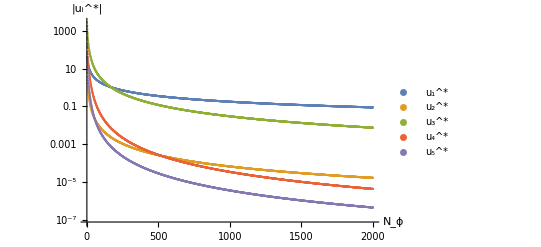

```mathematica
ListLogPlot[{FPphi6d4U1*Threaded[{1,-1}]
, FPphi6d4U2*Threaded[{1,-1}],Partition[Flatten[FPphi6d4U3],2]*Threaded[{1,-1}],Partition[Flatten[FPphi6d4U4],2]*Threaded[{1,-1}], Partition[Flatten[FPphi6d4U5],2]*Threaded[{1,-1}]},AxesLabel->{Style["N_ϕ", FontSize->14],Style["|u_i^*|", FontSize->14]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotLegends->{Style["u_1^*", FontSize->14], Style["u_2^*", FontSize->14], Style["u_3^*", FontSize->14],Style["u_4^*", FontSize->14],Style["u_5^*", FontSize->14]}, AxesStyle->{FontSize-> 14}, TicksStyle->Directive[FontSize->13]]
```

```mathematica
Export["absvalueU12345phi6d4expansionlogplotlargelabel.jpg",%,"JPEG"]
```

absvalueU12345phi6d4expansionlogplotlargelabel.jpg

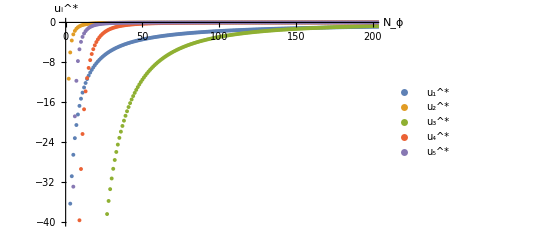

```mathematica
ListPlot[{FPphi6d4U1, FPphi6d4U2,Partition[Flatten[FPphi6d4U3],2],Partition[Flatten[FPphi6d4U4],2], Partition[Flatten[FPphi6d4U5],2]},AxesLabel->{Style["N_ϕ", FontSize->14],Style["u_i^*", FontSize->14]},PlotLabel->None,LabelStyle->{GrayLevel[0]},PlotLegends->{Style["u_1^*", FontSize->14], Style["u_2^*", FontSize->14], Style["u_3^*", FontSize->14],Style["u_4^*", FontSize->14],Style["u_5^*", FontSize->14]}, PlotRange->{{0, 200}, {-40,0}}, PlotStyle->{PointSize[0.007]}, TicksStyle->Directive[FontSize->13]]
```

```mathematica
Export["ValueU12345phi6d4expansionlinplotlargelabel.jpg",%,"JPEG"]
```

ValueU12345phi6d4expansionlinplotlargelabel.jpg

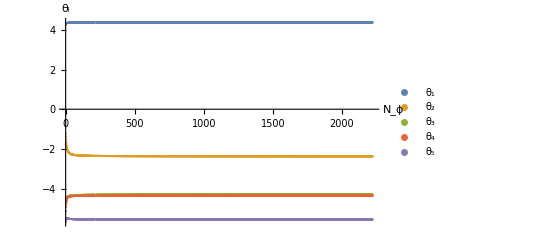

```mathematica
ListPlot[{FPphi6d4EV1, FPphi6d4EV2,Partition[Flatten[FPphi6d4EV3],2],Partition[Flatten[FPphi6d4EV4],2], Partition[Flatten[FPphi6d4EV5],2]},AxesLabel->{HoldForm["N_ϕ"],HoldForm["θ_i"]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotLegends->{"θ_1", "θ_2", "θ_3", "θ_4","θ_5"}, PlotRange->Automatic]
```

```mathematica
(*Export["StabilityCoefficientsphi6d4plot.jpg",%,"JPEG"]*)
```

StabilityCoefficientsphi6d4plot.jpg

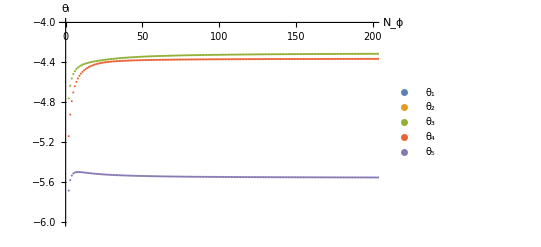

```mathematica
ListPlot[{FPphi6d4EV1, FPphi6d4EV2,Partition[Flatten[FPphi6d4EV3],2],Partition[Flatten[FPphi6d4EV4],2], Partition[Flatten[FPphi6d4EV5],2]},AxesLabel->{HoldForm["N_ϕ"],HoldForm["θ_i"]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotLegends->{"θ_1", "θ_2", "θ_3", "θ_4","θ_5"}, PlotRange->{{0, 200}, {-6,-4}}]
```

## Large N_ϕ-expansion

From the figures showing the evolution of U_i and θ_i it looks like the function asymptotes to a constant for very large N_ϕ. This means it should be possible to make a quite good large N_ϕ-expansion. The θ_i definitely should at highest order be constant in N_ϕ.

## Expanding the fixed points

### From scratch

```mathematica
Clear[ηϕ];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[β];
U1ExpPhi6d4 = U[6, Nphi, 1]-> U4[1,1] Nphi^-1+ U4[1,2] Nphi^-2+ U4[1,3] Nphi^-3;
U2ExpPhi6d4 = U[6, Nphi, 2]-> U4[2,1] Nphi^-1+ U4[2,2] Nphi^-2+ U4[2,3] Nphi^-3;
U3ExpPhi6d4 = U[6, Nphi, 3]-> U4[3,1] Nphi^-1+ U4[3,2] Nphi^-2+ U4[3,3] Nphi^-3;
U4ExpPhi6d4 = U[6, Nphi, 4]-> U4[4,1] Nphi^-1+ U4[4,2] Nphi^-2+ U4[4,3] Nphi^-3;
U5ExpPhi6d4 = U[6, Nphi, 5]-> U4[5,1] Nphi^-1+ U4[5,2] Nphi^-2+ U4[5,3] Nphi^-3;
```

```mathematica
RHSphi6d4Exp = Normal[Series[RHScollectedd4order6ONLY/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4, {Nphi, ∞, 1}]];
LHSphi6d4Exp = Normal[Series[LHScollectedd4order6ONLY/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4, {Nphi, ∞, 1}]];
```

```mathematica
ηϕ4Expphi6 = Normal[Series[ηϕ/. Solve[Simplify[Coefficient[Coefficient[RHSphi6d4Exp, X], S2, 0]]==Coefficient[Coefficient[LHSphi6d4Exp, X, 1],S2, 0], ηϕ], {Nphi, ∞, 1}]]
```

{(8 (4 U4[1,1]+U4[2,1]))/(768 π^2+4 U4[1,1]+U4[2,1])+(6144 π^2 (2 U4[1,1]+4 U4[1,2]+5 U4[2,1]+U4[2,2]))/(Nphi (768 π^2+4 U4[1,1]+U4[2,1])^2)}

```mathematica
RHSphi6d4ExpEps = Normal[Series[RHSphi6d4Exp/.ηϕ-> ηϕ4Expphi6[[1]], {Nphi, ∞, 1}]];
LHSphi6d4ExpEps = Normal[Series[LHSphi6d4Exp/.ηϕ-> ηϕ4Expphi6[[1]], {Nphi, ∞, 1}]];
```

```mathematica
β[6, Nphi, 1]=0;(*Set all appearing beta functions to zero *)
β[6, Nphi, 2]=0;
β[6, Nphi, 3]=0;
β[6, Nphi, 4]=0;
β[6, Nphi, 5]=0;
FPsolved3phi6ExpNphi0Of1=Simplify[Solve[Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d4ExpEps, S2],X, 0],Nphi, 0]]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d4ExpEps, S2],X, 0], Nphi,0]]&&
Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d4ExpEps, S2, 0],X, 2], Nphi, 0]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d4ExpEps, S2,0],X,2], Nphi, 0]]]&&Coefficient[Simplify[Coefficient[k^8 LHSphi6d4ExpEps, X, 3]], Nphi,-1]== Coefficient[Simplify[Coefficient[k^8 RHSphi6d4ExpEps, X,3]], Nphi, -1]&&Coefficient[Simplify[Coefficient[k^8 LHSphi6d4ExpEps, S3]], Nphi, -1]==Coefficient[Simplify[Coefficient[k^8 RHSphi6d4ExpEps, S3]], Nphi, -1]&&Simplify[Coefficient[k^8 Coefficient[Coefficient[LHSphi6d4ExpEps, S2],X], Nphi, -1]]== Simplify[Coefficient[k^8 Coefficient[Coefficient[RHSphi6d4ExpEps, S2],X], Nphi, -1]], {U4[1,1], U4[2,1],U4[3,1],U4[4,1],U4[5,1]}]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{U4[1,1]→-(1966080 π^4+14080 π^2 U4[2,1]+U4[2,1]^2)/(40960 π^2+4 U4[2,1]),U4[3,1]→-1/6 U4[4,1],U4[5,1]→-4/3 U4[4,1]},{U4[3,1]→0,U4[4,1]→0,U4[5,1]→0}}

### With the vanishing coefficients set to zero from the start

#### u_(3,1)=u_(4,1)=u_(5,1)=0

```mathematica
Clear[ηϕ];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[β];
U1ExpPhi6d4 = U[6, Nphi, 1]-> U4[1,1] Nphi^-1+ U4[1,2] Nphi^-2+ U4[1,3] Nphi^-3;
U2ExpPhi6d4 = U[6, Nphi, 2]-> U4[2,1] Nphi^-1+ U4[2,2] Nphi^-2+ U4[2,3] Nphi^-3;
U3ExpPhi6d4 = U[6, Nphi, 3]-> U4[3,2] Nphi^-2+ U4[3,3] Nphi^-3;
U4ExpPhi6d4 = U[6, Nphi, 4]-> U4[4,2] Nphi^-2+ U4[4,3] Nphi^-3;
U5ExpPhi6d4 = U[6, Nphi, 5]-> U4[5,2] Nphi^-2+ U4[5,3] Nphi^-3;
RHSphi6d4Exp = Normal[Series[RHScollectedd4order6ONLY/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4, {Nphi, ∞, 3}]];
LHSphi6d4Exp = Normal[Series[LHScollectedd4order6ONLY/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4, {Nphi, ∞, 3}]];
ηϕ4Expphi6 = Normal[Series[ηϕ/. Solve[Simplify[Coefficient[Coefficient[RHSphi6d4Exp, X], S2, 0]]==Coefficient[Coefficient[LHSphi6d4Exp, X, 1],S2, 0], ηϕ], {Nphi, ∞, 3}]];
RHSphi6d4ExpEps = Normal[Series[RHSphi6d4Exp/.ηϕ-> ηϕ4Expphi6[[1]], {Nphi, ∞, 3}]];
LHSphi6d4ExpEps = Normal[Series[LHSphi6d4Exp/.ηϕ-> ηϕ4Expphi6[[1]], {Nphi, ∞, 3}]];
```

```mathematica
β[6, Nphi, 1]=0;(*Set all appearing beta functions to zero *)
β[6, Nphi, 2]=0;
β[6, Nphi, 3]=0;
β[6, Nphi, 4]=0;
β[6, Nphi, 5]=0;
FPsolved3phi6ExpNphi0Of1=Simplify[Solve[Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d4ExpEps, S2],X, 0],Nphi, -1]]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d4ExpEps, S2],X, 0], Nphi,-1]]&&
Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d4ExpEps, S2, 0],X, 2], Nphi, -1]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d3ExpEps, S2,0],X,2], Nphi, -1]]]&&
Coefficient[Simplify[Coefficient[k^8 LHSphi6d4ExpEps, X, 3]], Nphi,-2]== Coefficient[Simplify[Coefficient[k^8 RHSphi6d4ExpEps, X,3]], Nphi, -2]&&Coefficient[Simplify[Coefficient[k^8 LHSphi6d4ExpEps, S3]], Nphi, -2]==Coefficient[Simplify[Coefficient[k^8 RHSphi6d4ExpEps, S3]], Nphi, -2]&&Simplify[Coefficient[k^8 Coefficient[Coefficient[LHSphi6d4ExpEps, S2],X], Nphi, -2]]== Simplify[Coefficient[k^8 Coefficient[Coefficient[RHSphi6d4ExpEps, S2],X], Nphi, -2]], {U4[1,1], U4[2,1],U4[3,2],U4[4,2],U4[5,2]}]]
```

{{U4[1,1]→0,U4[2,1]→0,U4[3,2]→0,U4[4,2]→0,U4[5,2]→0},{U4[1,1]→-(192 π^2)/5,U4[2,1]→0,U4[3,2]→(2064384 π^4)/2075,U4[4,2]→0,U4[5,2]→0},{U4[1,1]→(112 π^2)/3,U4[2,1]→-(4544 π^2)/15,U4[3,2]→(22917468928 π^4)/289929375,U4[4,2]→-(6424089088 π^4)/1164375,U4[5,2]→(5131012096 π^4)/139725},{U4[1,1]→0,U4[2,1]→π^2 Root-165.Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,1]-164.58272696758752,U4[3,2]→(π^4 (626373836144640+4210862653440 Root-165.Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,1]-164.58272696758752+3984353280 (Root-165.Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,1]-164.58272696758752)^2+477497 (Root-165.Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,1]-164.58272696758752)^3))/80585809920,U4[4,2]→-(3 π^4 (2013265920+18677760 Root-165.Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,1]-164.58272696758752+48640 (Root-165.Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,1]-164.58272696758752)^2+9 (Root-165.Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,1]-164.58272696758752)^3))/609280,U4[5,2]→(π^4 (452984832+12976128 Root-165.Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,1]-164.58272696758752+79488 (Root-165.Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,1]-164.58272696758752)^2+5 (Root-165.Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,1]-164.58272696758752)^3))/34272},{U4[1,1]→0,U4[2,1]→π^2 Root-99.3Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,2]-99.25468401998154,U4[3,2]→(π^4 (626373836144640+4210862653440 Root-99.3Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,2]-99.25468401998154+3984353280 (Root-99.3Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,2]-99.25468401998154)^2+477497 (Root-99.3Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,2]-99.25468401998154)^3))/80585809920,U4[4,2]→-(3 π^4 (2013265920+18677760 Root-99.3Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,2]-99.25468401998154+48640 (Root-99.3Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,2]-99.25468401998154)^2+9 (Root-99.3Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,2]-99.25468401998154)^3))/609280,U4[5,2]→(π^4 (452984832+12976128 Root-99.3Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,2]-99.25468401998154+79488 (Root-99.3Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,2]-99.25468401998154)^2+5 (Root-99.3Root[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,2]-99.25468401998154)^3))/34272},{U4[1,1]→0,U4[2,1]→π^2 Root-1.33 × 10^4-5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,3]-13308.081294506215,U4[3,2]→(π^4 (626373836144640+4210862653440 Root-1.33 × 10^4-5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,3]-13308.081294506215+3984353280 (Root-1.33 × 10^4-5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,3]-13308.081294506215)^2+477497 (Root-1.33 × 10^4-5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,3]-13308.081294506215)^3))/80585809920,U4[4,2]→-(3 π^4 (2013265920+18677760 Root-1.33 × 10^4-5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,3]-13308.081294506215+48640 (Root-1.33 × 10^4-5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,3]-13308.081294506215)^2+9 (Root-1.33 × 10^4-5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,3]-13308.081294506215)^3))/609280,U4[5,2]→(π^4 (452984832+12976128 Root-1.33 × 10^4-5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,3]-13308.081294506215+79488 (Root-1.33 × 10^4-5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,3]-13308.081294506215)^2+5 (Root-1.33 × 10^4-5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,3]-13308.081294506215)^3))/34272},{U4[1,1]→0,U4[2,1]→π^2 Root-1.33 × 10^4+5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,4]-13308.081294506215,U4[3,2]→(π^4 (626373836144640+4210862653440 Root-1.33 × 10^4+5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,4]-13308.081294506215+3984353280 (Root-1.33 × 10^4+5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,4]-13308.081294506215)^2+477497 (Root-1.33 × 10^4+5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,4]-13308.081294506215)^3))/80585809920,U4[4,2]→-(3 π^4 (2013265920+18677760 Root-1.33 × 10^4+5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,4]-13308.081294506215+48640 (Root-1.33 × 10^4+5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,4]-13308.081294506215)^2+9 (Root-1.33 × 10^4+5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,4]-13308.081294506215)^3))/609280,U4[5,2]→(π^4 (452984832+12976128 Root-1.33 × 10^4+5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,4]-13308.081294506215+79488 (Root-1.33 × 10^4+5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,4]-13308.081294506215)^2+5 (Root-1.33 × 10^4+5.99 × 10^3 ⅈRoot[3478923509760+56623104000 #1+220004352 #1^2+26880 #1^3+#1^4&,4]-13308.081294506215)^3))/34272}}

```mathematica
FPsolved3phi6ExpNphi0Of1/.(lhs_->rhs_):>lhs->N[rhs]
```

{{U4[1,1]→0.,U4[2,1]→0.,U4[3,2]→0.,U4[4,2]→0.,U4[5,2]→0.},{U4[1,1]→-378.993,U4[2,1]→0.,U4[3,2]→96910.7,U4[4,2]→0.,U4[5,2]→0.},{U4[1,1]→368.465,U4[2,1]→-2989.83,U4[3,2]→7699.7,U4[4,2]→-537425.,U4[5,2]→3.57708×10^6},{U4[1,1]→0.,U4[2,1]→-1624.37,U4[3,2]→47306.,U4[4,2]→-103907.,U4[5,2]→1.27382×10^6},{U4[1,1]→0.,U4[2,1]→-979.604,U4[3,2]→298819.,U4[4,2]→-302063.,U4[5,2]→-161354.},{U4[1,1]→0.,U4[2,1]→-131345.-59102.9 ⅈ,U4[3,2]→7.92539×10^7-9.75324×10^8 ⅈ,U4[4,2]→8.16994×10^8+9.14263×10^9 ⅈ,U4[5,2]→1.82725×10^10-6.37554×10^9 ⅈ},{U4[1,1]→0.,U4[2,1]→-131345.+59102.9 ⅈ,U4[3,2]→7.92539×10^7+9.75324×10^8 ⅈ,U4[4,2]→8.16994×10^8-9.14263×10^9 ⅈ,U4[5,2]→1.82725×10^10+6.37554×10^9 ⅈ}}

The second solution: {U4[1,1]→-378.993,U4[2,1]→0.,U4[3,2]→96910.7,U4[4,2]→0.,U4[5,2]→0.} appears to be the one we are looking for

#### u_(2,1)=u_(3,1)= u_(4,1)= u_(5,1)= u_(4,2)= u_(5,2)=0

```mathematica
Clear[ηϕ];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[β];
U1ExpPhi6d4 = U[6, Nphi, 1]-> U4[1,1] Nphi^-1+ U4[1,2] Nphi^-2+ U4[1,3] Nphi^-3;
U2ExpPhi6d4 = U[6, Nphi, 2]-> U4[2,2] Nphi^-2+ U4[2,3] Nphi^-3;
U3ExpPhi6d4 = U[6, Nphi, 3]-> U4[3,2] Nphi^-2+ U4[3,3] Nphi^-3;
U4ExpPhi6d4 = U[6, Nphi, 4]-> U4[4,3] Nphi^-3;
U5ExpPhi6d4 = U[6, Nphi, 5]-> U4[5,3] Nphi^-3;
RHSphi6d4Exp = Normal[Series[RHScollectedd4order6ONLY/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4, {Nphi, ∞, 3}]];
LHSphi6d4Exp = Normal[Series[LHScollectedd4order6ONLY/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4, {Nphi, ∞, 3}]];
ηϕ4Expphi6 = Normal[Series[ηϕ/. Solve[Simplify[Coefficient[Coefficient[RHSphi6d4Exp, X], S2, 0]]==Coefficient[Coefficient[LHSphi6d4Exp, X, 1],S2, 0], ηϕ], {Nphi, ∞, 3}]];
RHSphi6d4ExpEps = Normal[Series[RHSphi6d4Exp/.ηϕ-> ηϕ4Expphi6[[1]], {Nphi, ∞, 3}]];
LHSphi6d4ExpEps = Normal[Series[LHSphi6d4Exp/.ηϕ-> ηϕ4Expphi6[[1]], {Nphi, ∞, 3}]];
```

```mathematica
β[6, Nphi, 1]=0;(*Set all appearing beta functions to zero *)
β[6, Nphi, 2]=0;
β[6, Nphi, 3]=0;
β[6, Nphi, 4]=0;
β[6, Nphi, 5]=0;
FPsolved3phi6ExpNphi0Of1=Simplify[Solve[Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d4ExpEps, S2],X, 0],Nphi, -2]]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d4ExpEps, S2],X, 0], Nphi,-2]]&&
Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d4ExpEps, S2, 0],X, 2], Nphi, -1]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d4ExpEps, S2,0],X,2], Nphi, -1]]]&&
Coefficient[Simplify[Coefficient[k^8 LHSphi6d4ExpEps, X, 3]], Nphi,-2]== Coefficient[Simplify[Coefficient[k^8 RHSphi6d4ExpEps, X,3]], Nphi, -2]&&
Coefficient[Simplify[Coefficient[k^8 LHSphi6d4ExpEps, S3]], Nphi, -3]==Coefficient[Simplify[Coefficient[k^8 RHSphi6d4ExpEps, S3]], Nphi, -3]&&Simplify[Coefficient[k^8 Coefficient[Coefficient[LHSphi6d4ExpEps, S2],X], Nphi, -3]]== Simplify[Coefficient[k^8 Coefficient[Coefficient[RHSphi6d4ExpEps, S2],X], Nphi, -3]], {U4[1,1], U4[2,2],U4[3,2],U4[4,3],U4[5,3]}]]
```

{{U4[1,1]→0,U4[2,2]→0,U4[3,2]→0,U4[4,3]→0,U4[5,3]→0},{U4[1,1]→π^2 Root-34.9Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,1]-34.88721428330436,U4[2,2]→(π^2 (495019622400+28479631360 Root-34.9Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,1]-34.88721428330436+23915520 (Root-34.9Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,1]-34.88721428330436)^2+6843 (Root-34.9Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,1]-34.88721428330436)^3))/345538560,U4[3,2]→1/960 π^4 Root-34.9Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,1]-34.88721428330436 (61440+2560 Root-34.9Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,1]-34.88721428330436+(Root-34.9Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,1]-34.88721428330436)^2),U4[4,3]→(π^4 (36844339200+2237194240 Root-34.9Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,1]-34.88721428330436+7398720 (Root-34.9Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,1]-34.88721428330436)^2+3033 (Root-34.9Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,1]-34.88721428330436)^3))/1453120,U4[5,3]→(π^4 (58982400+3840000 Root-34.9Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,1]-34.88721428330436+19680 (Root-34.9Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,1]-34.88721428330436)^2+31 (Root-34.9Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,1]-34.88721428330436)^3))/86040},{U4[1,1]→π^2 Root-17.7Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,2]-17.723658478725866,U4[2,2]→(π^2 (495019622400+28479631360 Root-17.7Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,2]-17.723658478725866+23915520 (Root-17.7Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,2]-17.723658478725866)^2+6843 (Root-17.7Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,2]-17.723658478725866)^3))/345538560,U4[3,2]→1/960 π^4 Root-17.7Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,2]-17.723658478725866 (61440+2560 Root-17.7Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,2]-17.723658478725866+(Root-17.7Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,2]-17.723658478725866)^2),U4[4,3]→(π^4 (36844339200+2237194240 Root-17.7Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,2]-17.723658478725866+7398720 (Root-17.7Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,2]-17.723658478725866)^2+3033 (Root-17.7Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,2]-17.723658478725866)^3))/1453120,U4[5,3]→(π^4 (58982400+3840000 Root-17.7Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,2]-17.723658478725866+19680 (Root-17.7Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,2]-17.723658478725866)^2+31 (Root-17.7Root[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,2]-17.723658478725866)^3))/86040},{U4[1,1]→π^2 Root-1.73 × 10^3-1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,3]-1733.6945636189848,U4[2,2]→(π^2 (495019622400+28479631360 Root-1.73 × 10^3-1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,3]-1733.6945636189848+23915520 (Root-1.73 × 10^3-1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,3]-1733.6945636189848)^2+6843 (Root-1.73 × 10^3-1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,3]-1733.6945636189848)^3))/345538560,U4[3,2]→1/960 π^4 Root-1.73 × 10^3-1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,3]-1733.6945636189848 (61440+2560 Root-1.73 × 10^3-1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,3]-1733.6945636189848+(Root-1.73 × 10^3-1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,3]-1733.6945636189848)^2),U4[4,3]→(π^4 (36844339200+2237194240 Root-1.73 × 10^3-1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,3]-1733.6945636189848+7398720 (Root-1.73 × 10^3-1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,3]-1733.6945636189848)^2+3033 (Root-1.73 × 10^3-1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,3]-1733.6945636189848)^3))/1453120,U4[5,3]→(π^4 (58982400+3840000 Root-1.73 × 10^3-1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,3]-1733.6945636189848+19680 (Root-1.73 × 10^3-1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,3]-1733.6945636189848)^2+31 (Root-1.73 × 10^3-1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,3]-1733.6945636189848)^3))/86040},{U4[1,1]→π^2 Root-1.73 × 10^3+1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,4]-1733.6945636189848,U4[2,2]→(π^2 (495019622400+28479631360 Root-1.73 × 10^3+1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,4]-1733.6945636189848+23915520 (Root-1.73 × 10^3+1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,4]-1733.6945636189848)^2+6843 (Root-1.73 × 10^3+1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,4]-1733.6945636189848)^3))/345538560,U4[3,2]→1/960 π^4 Root-1.73 × 10^3+1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,4]-1733.6945636189848 (61440+2560 Root-1.73 × 10^3+1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,4]-1733.6945636189848+(Root-1.73 × 10^3+1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,4]-1733.6945636189848)^2),U4[4,3]→(π^4 (36844339200+2237194240 Root-1.73 × 10^3+1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,4]-1733.6945636189848+7398720 (Root-1.73 × 10^3+1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,4]-1733.6945636189848)^2+3033 (Root-1.73 × 10^3+1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,4]-1733.6945636189848)^3))/1453120,U4[5,3]→(π^4 (58982400+3840000 Root-1.73 × 10^3+1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,4]-1733.6945636189848+19680 (Root-1.73 × 10^3+1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,4]-1733.6945636189848)^2+31 (Root-1.73 × 10^3+1.03 × 10^3 ⅈRoot[7549747200+648806400 #1+12759040 #1^2+10560 #1^3+3 #1^4&,4]-1733.6945636189848)^3))/86040}}

```mathematica
FPsolved3phi6ExpNphi0Of1/.(lhs_->rhs_):>lhs->N[rhs]
```

{{U4[1,1]→0.,U4[2,2]→0.,U4[3,2]→0.,U4[4,3]→0.,U4[5,3]→0.},{U4[1,1]→-344.323,U4[2,2]→-13417.1,U4[3,2]→94353.8,U4[4,3]→-2.16714×10^6,U4[5,3]→-59265.1},{U4[1,1]→-174.925,U4[2,2]→-64.8151,U4[3,2]→-29460.3,U4[4,3]→-33495.,U4[5,3]→-3472.27},{U4[1,1]→-17110.9-10181.9 ⅈ,U4[2,2]→-6564.15+697.519 ⅈ,U4[3,2]→5.2641×10^8+9.02598×10^7 ⅈ,U4[4,3]→7.71315×10^8-4.86742×10^7 ⅈ,U4[5,3]→4.71716×10^7-2.1273×10^8 ⅈ},{U4[1,1]→-17110.9+10181.9 ⅈ,U4[2,2]→-6564.15-697.519 ⅈ,U4[3,2]→5.2641×10^8-9.02598×10^7 ⅈ,U4[4,3]→7.71315×10^8+4.86742×10^7 ⅈ,U4[5,3]→4.71716×10^7+2.1273×10^8 ⅈ}}

The third solution {U4[1,1]→-174.925,U4[2,2]→-64.8151,U4[3,2]→-29460.3,U4[4,3]→-33495.,U4[5,3]→-3472.27}, lies closest to what we found in the lower order expansion and is thus most likely the solution belonging to NGFP2.

### Anomalous dimension

```mathematica
ηϕ4Expphi6[[1]]/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}
```

-0.813586+(0.00128102 (-414.665+4 U4[1,2]))/Nphi+(1.8619×10^-7 (-2.40164×10^6+17077.6 U4[1,2]-16 U4[1,2]^2-2798.8 U4[1,3]+3072 π^2 U4[1,3]-699.7 U4[2,3]+768 π^2 U4[2,3]))/Nphi^2+1/Nphi^3 2.70619×10^-11 (-1.92045×10^9+3.13127×10^7 U4[1,2]-129986. U4[1,2]^2+64 U4[1,2]^3+1.17497×10^8 U4[1,3]+22390.4 U4[1,2] U4[1,3]-24576 π^2 U4[1,2] U4[1,3]+2.42389×10^8 U4[2,3]+5597.6 U4[1,2] U4[2,3]-6144 π^2 U4[1,2] U4[2,3])

In this case the anomalous dimension is -0.81 in the limit.

```mathematica
FitAndim4phi6=Fit[Take[AnomalousDimd4phi6, -400], {1, 1/x, 1/x^2}, x]
```

-0.813588732663707146241847650394903984248492499567346132262203455511263583128380520663106349110992031-0.317952213163978236094911889133507860406731276545058834944423084891994301079586972718914929228786246/x^2+0.646958883063540401333165733768322239606720683266886431060941093285785367539339398998897494679493564/x

This corresponds to the fit...

## Expanding the stability matrix

Before running this, redefine the beta functions as the previous section uses beta=0.

```mathematica
U1ExpPhi6d4 = U[6, Nphi, 1]-> U4[1,1] Nphi^-1+ U4[1,2] Nphi^-2+ U4[1,3] Nphi^-3;
U2ExpPhi6d4 = U[6, Nphi, 2]-> U4[2,2] Nphi^-2+ U4[2,3] Nphi^-3;
U3ExpPhi6d4 = U[6, Nphi, 3]-> U4[3,2] Nphi^-2+ U4[3,3] Nphi^-3;
U4ExpPhi6d4 = U[6, Nphi, 4]-> U4[4,3] Nphi^-3;
U5ExpPhi6d4 = U[6, Nphi, 5]-> U4[5,3] Nphi^-3;
```

```mathematica
BexpPhi6d4[1,1]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 1], U[6, Nphi, 1]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 0}]]
BexpPhi6d4[2,1]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 2], U[6, Nphi, 1]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 1}]]
BexpPhi6d4[3,1]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 3], U[6, Nphi, 1]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 1}]]
BexpPhi6d4[4,1]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 4], U[6, Nphi, 1]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 2}]]
BexpPhi6d4[5,1]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 5], U[6, Nphi, 1]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 2}]]
```

-2.0343

-1.5447/Nphi

-2124.55/Nphi

-2489.88/Nphi^2

-392.145/Nphi^2

```mathematica
BexpPhi6d4[1,2]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 1], U[6, Nphi, 2]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 0}]]
BexpPhi6d4[2,2]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 2], U[6, Nphi, 2]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 0}]]
BexpPhi6d4[3,2]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 3], U[6, Nphi, 2]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 1}]]
BexpPhi6d4[4,2]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 4], U[6, Nphi, 2]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 2}]]
BexpPhi6d4[5,2]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 5], U[6, Nphi, 2]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 2}]]
```

-1.10178

2.37283

-531.139/Nphi

-3387.07/Nphi^2

-683.318/Nphi^2

```mathematica
BexpPhi6d4[1,3]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 1], U[6, Nphi, 3]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, -1}]]
BexpPhi6d4[2,3]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 2], U[6, Nphi, 3]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 3}]]
BexpPhi6d4[3,3]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 3], U[6, Nphi, 3]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 0}]]
BexpPhi6d4[4,3]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 4], U[6, Nphi, 3]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 1}]]
BexpPhi6d4[5,3]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 5], U[6, Nphi, 3]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 3}]]
```

-0.00697659 Nphi

0

1.9657

-2.3957/Nphi

0

```mathematica
BexpPhi6d4[1,4]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 1], U[6, Nphi, 4]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, -1}]]
BexpPhi6d4[2,4]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 2], U[6, Nphi, 4]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, -1}]]
BexpPhi6d4[3,4]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 3], U[6, Nphi, 4]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 0}]]
BexpPhi6d4[4,4]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 4], U[6, Nphi, 4]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 0}]]
BexpPhi6d4[5,4]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 5], U[6, Nphi, 4]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 1}]]
```

-0.00116276 Nphi

-0.00232553 Nphi

-0.598924

4.36139

-1.59713/Nphi

```mathematica
BexpPhi6d4[1,5]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 1], U[6, Nphi, 5]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 0}]]
BexpPhi6d4[2,5]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 2], U[6, Nphi, 5]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, -1}]]
BexpPhi6d4[3,5]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 3], U[6, Nphi, 5]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 1}]]
BexpPhi6d4[4,5]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 4], U[6, Nphi, 5]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 0}]]
BexpPhi6d4[5,5]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 5], U[6, Nphi, 5]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->-29460.3,U4[4,3]->-33495.,U4[5,3]->-3472.27}, {Nphi, ∞, 0}]]
```

-0.00174415

-0.00174415 Nphi

-0.898386/Nphi

-0.898386

5.55924

```mathematica
MatPhi6d4Exp = Table[BexpPhi6d4[a,b],{a,1,5},{b,1,5}];
%//MatrixForm
```

(-2.0343 | -1.10178 | -0.00697659 Nphi | -0.00116276 Nphi | -0.00174415
-1.5447/Nphi | 2.37283 | 0 | -0.00232553 Nphi | -0.00174415 Nphi
-2124.55/Nphi | -531.139/Nphi | 1.9657 | -0.598924 | -0.898386/Nphi
-2489.88/Nphi^2 | -3387.07/Nphi^2 | -2.3957/Nphi | 4.36139 | -0.898386
-392.145/Nphi^2 | -683.318/Nphi^2 | 0 | -1.59713/Nphi | 5.55924)

```mathematica
CharPolyP6d4 =Det[MatPhi6d4Exp-λ IdentityMatrix[5]](*This is the determinant of the previously given matrix-λI. It will generate the characteristic polynomial*)
```

1/Nphi^6 1. (0.-80.6479 Nphi^2-168.881 Nphi^3-83.3145 Nphi^4+285.393 Nphi^5-1082.8 Nphi^6+14.5744 Nphi^2 λ+93.5554 Nphi^3 λ+106.9 Nphi^4 λ+242.826 Nphi^5 λ+903.325 Nphi^6 λ-12.2143 Nphi^3 λ^2-23.9269 Nphi^4 λ^2-142.994 Nphi^5 λ^2-177.122 Nphi^6 λ^2+0.683959 Nphi^4 λ^3+16.5353 Nphi^5 λ^3-28.1216 Nphi^6 λ^3+12.2249 Nphi^6 λ^4-1. Nphi^6 λ^5)

```mathematica
Series[CharPolyP6d4, {Nphi, ∞, 0}]
```

1. (-1082.8+903.325 λ-177.122 λ^2-28.1216 λ^3+12.2249 λ^4-1. λ^5)+O[1/Nphi]^1

```mathematica
Solve[-1082.8013095166548+903.325471144233 λ-177.12160776192707 λ^2-28.121603480278885 λ^3+12.224854342240505 λ^4-1. λ^5==0, λ]
```

{{λ→-4.37275},{λ→2.37283},{λ→4.30415},{λ→4.36139},{λ→5.55924}}

```mathematica
1/4.372752778151241
```

0.228689

### u{3,4,5}->0 after analysis

```mathematica
BexpPhi6d4[1,1]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 1], U[6, Nphi, 1]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 0}]]
BexpPhi6d4[2,1]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 2], U[6, Nphi, 1]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 1}]]
BexpPhi6d4[3,1]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 3], U[6, Nphi, 1]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 1}]]
BexpPhi6d4[4,1]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 4], U[6, Nphi, 1]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 2}]]
BexpPhi6d4[5,1]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 5], U[6, Nphi, 1]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 2}]]
BexpPhi6d4[1,2]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 1], U[6, Nphi, 2]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 0}]]
BexpPhi6d4[2,2]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 2], U[6, Nphi, 2]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 0}]]
BexpPhi6d4[3,2]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 3], U[6, Nphi, 2]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 1}]]
BexpPhi6d4[4,2]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 4], U[6, Nphi, 2]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 2}]]
BexpPhi6d4[5,2]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 5], U[6, Nphi, 2]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 2}]]
BexpPhi6d4[1,3]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 1], U[6, Nphi, 3]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, -1}]]
BexpPhi6d4[2,3]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 2], U[6, Nphi, 3]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 3}]]
BexpPhi6d4[3,3]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 3], U[6, Nphi, 3]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 0}]]
BexpPhi6d4[4,3]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 4], U[6, Nphi, 3]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 1}]]
BexpPhi6d4[5,3]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 5], U[6, Nphi, 3]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 3}]]
BexpPhi6d4[1,4]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 1], U[6, Nphi, 4]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, -1}]]
BexpPhi6d4[2,4]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 2], U[6, Nphi, 4]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, -1}]]
BexpPhi6d4[3,4]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 3], U[6, Nphi, 4]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 0}]]
BexpPhi6d4[4,4]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 4], U[6, Nphi, 4]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 0}]]
BexpPhi6d4[5,4]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 5], U[6, Nphi, 4]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 1}]]
BexpPhi6d4[1,5]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 1], U[6, Nphi, 5]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 0}]]
BexpPhi6d4[2,5]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 2], U[6, Nphi, 5]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, -1}]]
BexpPhi6d4[3,5]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 3], U[6, Nphi, 5]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 1}]]
BexpPhi6d4[4,5]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 4], U[6, Nphi, 5]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 0}]]
BexpPhi6d4[5,5]= Normal[Series[D[β[U[6, Nphi, 1], U[6, Nphi, 2], U[6, Nphi, 3], U[6, Nphi, 4], U[6, Nphi, 5]][6, Nphi, 5], U[6, Nphi, 5]]/. U1ExpPhi6d4/.U2ExpPhi6d4/. U3ExpPhi6d4/.U4ExpPhi6d4/.U5ExpPhi6d4/.{U4[1,1]->-174.925,U4[2,2]->-64.8151,U4[3,2]->0,U4[4,3]->0,U4[5,3]->0}, {Nphi, ∞, 0}]]
```

-1.91481

-1.49589/Nphi

-1016.31/Nphi

-1270.38/Nphi^2

-338.769/Nphi^2

-1.07191

2.37283

-254.077/Nphi

-2137.63/Nphi^2

-664.03/Nphi^2

-0.00697659 Nphi

0

1.9657

-2.3957/Nphi

0

-0.00116276 Nphi

-0.00232553 Nphi

-0.598924

4.36139

-1.59713/Nphi

-0.00174415

-0.00174415 Nphi

-0.898386/Nphi

-0.898386

5.55924

```mathematica
MatPhi6d4Exp = Table[BexpPhi6d4[a,b],{a,1,5},{b,1,5}];
%//MatrixForm
```

(-1.91481 | -1.07191 | -0.00697659 Nphi | -0.00116276 Nphi | -0.00174415
-1.49589/Nphi | 2.37283 | 0 | -0.00232553 Nphi | -0.00174415 Nphi
-1016.31/Nphi | -254.077/Nphi | 1.9657 | -0.598924 | -0.898386/Nphi
-1270.38/Nphi^2 | -2137.63/Nphi^2 | -2.3957/Nphi | 4.36139 | -0.898386
-338.769/Nphi^2 | -664.03/Nphi^2 | 0 | -1.59713/Nphi | 5.55924)

```mathematica
CharPolyP6d4 =Det[MatPhi6d4Exp-λ IdentityMatrix[5]](*This is the determinant of the previously given matrix-λI. It will generate the characteristic polynomial*)
Series[CharPolyP6d4, {Nphi, ∞, 0}]
```

1/Nphi^6 1. (0.-46.5437 Nphi^2-93.0297 Nphi^3-90.6254 Nphi^4+56.8643 Nphi^5-624.465 Nphi^6+8.90753 Nphi^2 λ+57.4223 Nphi^3 λ+70.9579 Nphi^4 λ+169.384 Nphi^5 λ+515.755 Nphi^6 λ-8.70876 Nphi^3 λ^2-16.9365 Nphi^4 λ^2-96.5378 Nphi^5 λ^2-73.4735 Nphi^6 λ^2+0.590863 Nphi^4 λ^3+12.0796 Nphi^5 λ^3-37.5573 Nphi^6 λ^3+12.3443 Nphi^6 λ^4-1. Nphi^6 λ^5)

1. (-624.465+515.755 λ-73.4735 λ^2-37.5573 λ^3+12.3443 λ^4-1. λ^5)+O[1/Nphi]^1

```mathematica
Solve[-624.4653299183234+515.7554664058532 λ-73.47352963054972 λ^2-37.5572571643093 λ^3+12.344347159357945 λ^4-1. λ^5==0, λ]
```

{{λ→-3.26924},{λ→2.37283},{λ→3.32013},{λ→4.36139},{λ→5.55924}}

```mathematica
MatPhi4d4ExpExtended = Table[BexpPhi6d4[a,b],{a,1,2},{b,1,2}];
%//MatrixForm
```

(-1.91481 | -1.07191
-1.49589/Nphi | 2.37283)

```mathematica
Eigenvalues[{{-1.9148107582003768,-1.071909598410541},{-1.4958949455343429/Nphi,2.372827635441787}}]
```

{(0.5 (0.458017 Nphi-4.28764 √Nphi √(0.348886+1. Nphi)))/Nphi,(0.5 (0.458017 Nphi+4.28764 √Nphi √(0.348886+1. Nphi)))/Nphi}

```mathematica
Series[(0.5 (0.4580168772414104 Nphi-4.287638393642164 √Nphi √(0.34888551883304797+1. Nphi)))/Nphi, {Nphi, ∞, 0}]
Series[(0.5 (0.4580168772414104 Nphi+4.287638393642164 √Nphi √(0.34888551883304797+1. Nphi)))/Nphi, {Nphi, ∞, 0}]
```

-1.91481+O[1/Nphi]^1

2.37283+O[1/Nphi]^1

## Making figures

### For the anomalous dimension

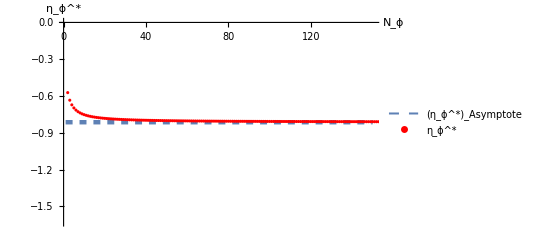

Phi6IncreasingNphiAnomalousDimension+Expansiond4.jpg

```mathematica
Show[Plot[{y=-0.8135861822791065},{y,1,150},PlotStyle->{Thickness[0.008], Dashed}, PlotLegends->{"(η_ϕ^*)_Asymptote"}],ListPlot[AnomalousDimd4phi6,PlotStyle->Red,  PlotLegends->{"η_ϕ^*"}], AxesLabel-> { "N_ϕ", "η_ϕ^*"}]
Export["Phi6IncreasingNphiAnomalousDimension+Expansiond4.jpg", %, "JPEG"]
```

```mathematica
FitAndim4phi6=Fit[Take[AnomalousDimd4phi6, -400], {1, 1/x, 1/x^2}, x]
```

-0.813588732663707146241847650394903984248492499567346132262203455511263583128380520663106349110992031-0.317952213163978236094911889133507860406731276545058834944423084891994301079586972718914929228786246/x^2+0.646958883063540401333165733768322239606720683266886431060941093285785367539339398998897494679493564/x

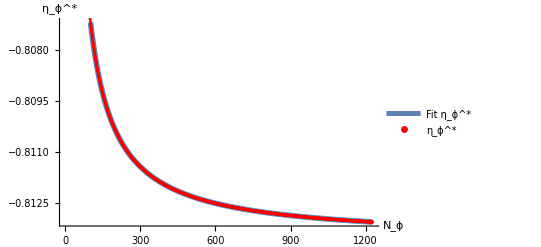

```mathematica
Show[Plot[{FitAndim4phi6},{x,1,1228},PlotStyle->{Thickness[0.01]}, PlotLegends->{"Fit η_ϕ^*"}],ListPlot[AnomalousDimd4phi6,PlotStyle->Red,  PlotLegends->{"η_ϕ^*"}], AxesLabel-> { "N_ϕ", "η_ϕ^*"}]
```

```mathematica
Export["Phi6IncreasingNphiAnomalousDimension+fitd4SMALLER.jpg", %, "JPEG"]
```

Phi6IncreasingNphiAnomalousDimension+fitd4SMALLER.jpg

### Stability coefficients

First we combine the expansion value with the actual data in one figure

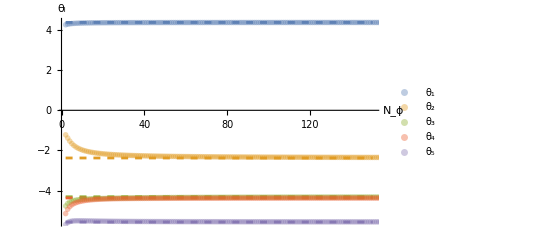

Phi6IncreasingNphiStabCoeff+Expansiond4.jpg

```mathematica
Show[Plot[{y=4.372752778151241, y=-2.372827635441788, y=-4.304145097968505, y=-4.361392933819195,y=-5.559241453162717},{y,2,150}, (*PlotLegends-> {"θ_(1,  Exp)", "θ_(2,  Exp)", "θ_(3,  Exp)", "θ_(4,  Exp)", "θ_(5,  Exp)"}, *)PlotStyle->{{RGBColor[0.368417,0.506779,0.709798],Dashed}, {RGBColor[0.880722,0.611041,0.142051],Dashed}, {RGBColor[0.560181,0.691569,0.194885],Dashed}, {RGBColor[0.922526,0.385626,0.209179],Dashed}, {RGBColor[0.528488,0.470624,0.701351],Dashed}}],ListPlot[{FPphi6d4EV1,FPphi6d4EV2, FPphi6d4EV3, FPphi6d4EV4, FPphi6d4EV5},PlotStyle->{{Opacity[0.4,RGBColor[0.368417,0.506779,0.709798]],PointSize[0.01]}, {Opacity[0.4,RGBColor[0.880722,0.611041,0.142051]],PointSize[0.01]}, {Opacity[0.4,RGBColor[0.560181,0.691569,0.194885]],PointSize[0.01]}, {Opacity[0.4,RGBColor[0.922526,0.385626,0.209179]],PointSize[0.01]}, {Opacity[0.4,RGBColor[0.528488,0.470624,0.701351]],PointSize[0.01]}},  PlotLegends->{"θ_1", "θ_2", "θ_3", "θ_4", "θ_5"}], AxesLabel->{"N_ϕ","θ_i"}]
Export["Phi6IncreasingNphiStabCoeff+Expansiond4.jpg", %, "JPEG"]
```

We double check the results using a fit

```mathematica
FitEV1phi6d4 =Fit[Take[FPphi6d4EV1, -1000], {1, 1/x,1/x^2}, x]
```

4.37278+0.164225/x^2-0.31244/x

```mathematica
FitEV2phi6d4 =Fit[Take[FPphi6d4EV2, -1000], {1, 1/x,1/x^2}, x]
```

-2.37282-2.62658/x^2+4.32328/x

```mathematica
FitEV3phi6d4 =Fit[Take[FPphi6d4EV3, -1000], {1, 1/x,1/x^2}, x]
```

-4.30413+2.14365/x^2-2.01671/x

```mathematica
FitEV4phi6d4 =Fit[Take[FPphi6d4EV4, -1000], {1, 1/x,1/x^2}, x]
```

-4.36138-2.32361/x^2-0.759915/x

```mathematica
FitEV5phi6d4 =Fit[Take[FPphi6d4EV5, -1000], {1, 1/x,1/x^2}, x]
```

-5.55923-7.23218/x^2+1.16469/x

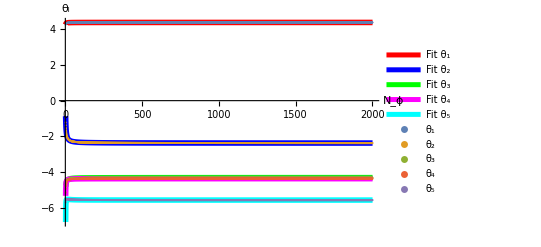

Phi6IncreasingNphiStabCoeff+fitd4.jpg

```mathematica
Show[Plot[{FitEV1phi6d4, FitEV2phi6d4, FitEV3phi6d4, FitEV4phi6d4, FitEV5phi6d4},{x,2,2001}, PlotLegends-> {"Fit θ_1", "Fit θ_2", "Fit θ_3", "Fit θ_4", "Fit θ_5"}, PlotStyle->{{Red ,Thickness[0.01]}, {Blue,Thickness[0.01]}, {Green,Thickness[0.01]}, {Magenta,Thickness[0.01]}, {Cyan,Thickness[0.01]}}],ListPlot[{FPphi6d4EV1,FPphi6d4EV2, FPphi6d4EV3, FPphi6d4EV4, FPphi6d4EV5},  PlotLegends->{"θ_1", "θ_2", "θ_3", "θ_4", "θ_5"}], AxesLabel->{"N_ϕ","θ_i"}]
```

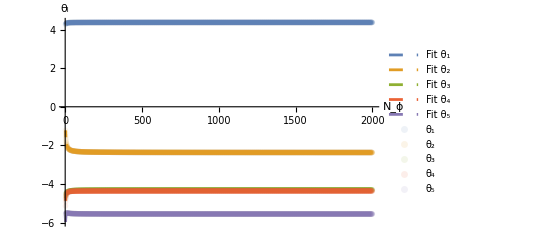

```mathematica
Show[Plot[{FitEV1phi6d4, FitEV2phi6d4, FitEV3phi6d4, FitEV4phi6d4, FitEV5phi6d4},{x,3,2001}, PlotLegends-> {"Fit θ_1", "Fit θ_2", "Fit θ_3", "Fit θ_4", "Fit θ_5"}, PlotStyle->{{RGBColor[0.368417,0.506779,0.709798],Dashed}, {RGBColor[0.880722,0.611041,0.142051],Dashed}, {RGBColor[0.560181,0.691569,0.194885],Dashed}, {RGBColor[0.922526,0.385626,0.209179],Dashed}, {RGBColor[0.528488,0.470624,0.701351],Dashed}}],ListPlot[{FPphi6d4EV1,FPphi6d4EV2, FPphi6d4EV3, FPphi6d4EV4, FPphi6d4EV5},PlotStyle->{{Opacity[0.1,RGBColor[0.368417,0.506779,0.709798]],PointSize[0.01]}, {Opacity[0.1,RGBColor[0.880722,0.611041,0.142051]],PointSize[0.01]}, {Opacity[0.1,RGBColor[0.560181,0.691569,0.194885]],PointSize[0.01]}, {Opacity[0.1,RGBColor[0.922526,0.385626,0.209179]],PointSize[0.01]}, {Opacity[0.1,RGBColor[0.528488,0.470624,0.701351]],PointSize[0.01]}},  PlotLegends->{"θ_1", "θ_2", "θ_3", "θ_4", "θ_5"}], AxesLabel->{"N_ϕ","θ_i"}]
(*Export["Phi6IncreasingNphiStabCoeff+fitd4.jpg", %, "JPEG"]*)
```

# Finding Fixed Points O(ϕ^4), d=3

In the xAct file Invariant quantities for N scalar fields, we have derived the right-hand side (RHS) and left-hand side (LHS) of the Wetterich equation for spacetime dimension d=3 up to order ϕ^4.  The results are given in the two initialization cells below in the set up tab. Now we can use Mathematica without the package to work on solving the system.

## Set up

```mathematica
Clear[βϕ3](*Clear to make sure nothing accidentaly remains*)
Clear[ηϕ3]
Clear[Nphi]
```

```mathematica
pe=4;(*pe gives the max power of ϕ in the expansion*)
RHS3phi4 = Simplify[-((Nphi (-5+ηϕ3) k^3)/(30 π^2))+X ((2 U3[pe,Nphi,  1] (-7+ηϕ3) )/(105 π^2)+(Nphi U3[pe,Nphi,  1] (-7+ηϕ3) )/(35 π^2)+(4 U3[pe,Nphi,  2](-7+ηϕ3) )/(105 π^2)+(Nphi U3[pe,Nphi,  2] (-7+ηϕ3) )/(105 π^2))+X^2 (-((32 U3[pe,Nphi,  1] U3[pe,Nphi,  2](-9+ηϕ3) k^{-3})/(315 π^2))-(16 (-9+ηϕ3) k^{-3} U3[pe,Nphi,  1]^2 )/(315 π^2)-(26 (-9+ηϕ3) k^{-3} U3[pe,Nphi,  2]^2)/(945 π^2))+S2 (-((4 Nphi (-9+ηϕ3) k^{-3} U3[pe,Nphi,  2]^2)/(945 π^2))-(2 (-9+ηϕ3) k^{-3}(36U3[pe,Nphi,  1] U3[pe,Nphi,  2]+8 U3[pe,Nphi,  1]^2+31 U3[pe,Nphi,  2]^2))/(945 π^2))-(2 Nphi (-9+ηϕ3) k^{-3} (2 U3[pe,Nphi,  1]U3[pe,Nphi,  2]+3 U3[pe,Nphi,  1]^2) X^2)/(189 π^2)-(Nphi (-9+ηϕ3) k^{-3} U3[pe,Nphi,  1]^2 X^2)/(756 π^2)](*The right-hand side of the Wetterich equation for d=3*)
```

{-1/(3780 k^3 π^2)(126 k^6 Nphi (-5+ηϕ3)+(64 S2+(192+125 Nphi) X^2) (-9+ηϕ3) U3[4,Nphi,1]^2-36 k^3 (4+Nphi) X (-7+ηϕ3) U3[4,Nphi,2]+8 ((31+2 Nphi) S2+13 X^2) (-9+ηϕ3) U3[4,Nphi,2]^2-4 U3[4,Nphi,1] (9 k^3 (2+3 Nphi) X (-7+ηϕ3)-4 (18 S2+(24+5 Nphi) X^2) (-9+ηϕ3) U3[4,Nphi,2]))}

```mathematica
Simplify[Coefficient[RHS3phi4, X]]
```

{((-7+ηϕ3) ((2+3 Nphi) U3[4,Nphi,1]+(4+Nphi) U3[4,Nphi,2]))/(105 π^2)}

```mathematica
LHS3finalphi4 = -X ηϕ3+X^2(-(2 ηϕ3 U3[pe,Nphi,  1])/k^3-3(U3[pe,Nphi,  1]/k^3)+βϕ3[pe,Nphi, 1]/k^3)+S2 (-(2 ηϕ3 U3[pe,Nphi,  2])/k^3-3 U3[pe,Nphi,  2]/k^3+βϕ3[pe,Nphi, 2]/k^3);(*The left-hand side of the Wetterich equation for d=3*)
```

```mathematica
Solve[Simplify[Coefficient[RHS3phi4, X]]==Coefficient[LHS3finalphi4, X], ηϕ3](*Solve for the anomalous dimension*)
```

{{ηϕ3→(7 (2 U3[4,Nphi,1]+3 Nphi U3[4,Nphi,1]+4 U3[4,Nphi,2]+Nphi U3[4,Nphi,2]))/(105 π^2+2 U3[4,Nphi,1]+3 Nphi U3[4,Nphi,1]+4 U3[4,Nphi,2]+Nphi U3[4,Nphi,2])}}

## Finding Fixed points and Beta functions

## General solution

First define the anomalous dimension

```mathematica
ηϕ3=(7 (2 U3[4,Nphi,1]+3 Nphi U3[4,Nphi,1]+4 U3[4,Nphi,2]+Nphi U3[4,Nphi,2]))/(105 π^2+2 U3[4,Nphi,1]+3 Nphi U3[4,Nphi,1]+4 U3[4,Nphi,2]+Nphi U3[4,Nphi,2]);
```

### Fixed points

The fixed points are found by equating the coefficients of the different basis elements

```mathematica
βϕ3[4, Nphi, 1]=0;(*First set beta to zero, since at the FP it has to be 0*)
βϕ3[4, Nphi, 2]=0;
```

Since the two equations remaining are strongly coupled, it is most efficient to solve them in one go.

```mathematica
FP3Solgen = Solve[Simplify[Coefficient[RHS3phi4, X, 2]]==Coefficient[LHS3finalphi4, X, 2]&&Simplify[Coefficient[RHS3phi4,S2]]==Coefficient[LHS3finalphi4, S2]/. k-> 1, {U3[4,Nphi, 1], U3[4,Nphi, 2]}](*In this evaluation it is easy to see the k-terms drop out. Since this takes extra time, k is set to 1, which has the same result.*)
```

### Beta functions

Next step is again to find the beta functions

```mathematica
Clear[βϕ3](*Since for the fixed point evaluation beta was set to zero, it must be cleared so the equation governing its evolution can be found*)
```

```mathematica
Solve[Simplify[Coefficient[RHS3phi4, X, 2]]==Coefficient[LHS3finalphi4, X, 2]/. k-> 1, βϕ3[4,Nphi, 1]]
```

{{βϕ3[4,Nphi,1]→(1190700 π^4 U3[4,Nphi,1]+309960 π^2 U3[4,Nphi,1]^2+310905 Nphi π^2 U3[4,Nphi,1]^2+768 U3[4,Nphi,1]^3+1652 Nphi U3[4,Nphi,1]^3+750 Nphi^2 U3[4,Nphi,1]^3+619920 π^2 U3[4,Nphi,1] U3[4,Nphi,2]+139860 Nphi π^2 U3[4,Nphi,1] U3[4,Nphi,2]+3072 U3[4,Nphi,1]^2 U3[4,Nphi,2]+4008 Nphi U3[4,Nphi,1]^2 U3[4,Nphi,2]+730 Nphi^2 U3[4,Nphi,1]^2 U3[4,Nphi,2]+98280 π^2 U3[4,Nphi,2]^2+3488 U3[4,Nphi,1] U3[4,Nphi,2]^2+2032 Nphi U3[4,Nphi,1] U3[4,Nphi,2]^2+160 Nphi^2 U3[4,Nphi,1] U3[4,Nphi,2]^2+832 U3[4,Nphi,2]^3+208 Nphi U3[4,Nphi,2]^3)/(3780 π^2 (105 π^2+2 U3[4,Nphi,1]+3 Nphi U3[4,Nphi,1]+4 U3[4,Nphi,2]+Nphi U3[4,Nphi,2]))}}

```mathematica
βϕ3[U3_[4, Nphi, 1], U3_[4, Nphi, 2]][4,Nphi, 1]= (1190700 π^4 U3[4,Nphi,1]+309960 π^2 U3[4,Nphi,1]^2+310905 Nphi π^2 U3[4,Nphi,1]^2+768 U3[4,Nphi,1]^3+1652 Nphi U3[4,Nphi,1]^3+750 Nphi^2 U3[4,Nphi,1]^3+619920 π^2 U3[4,Nphi,1] U3[4,Nphi,2]+139860 Nphi π^2 U3[4,Nphi,1] U3[4,Nphi,2]+3072 U3[4,Nphi,1]^2 U3[4,Nphi,2]+4008 Nphi U3[4,Nphi,1]^2 U3[4,Nphi,2]+730 Nphi^2 U3[4,Nphi,1]^2 U3[4,Nphi,2]+98280 π^2 U3[4,Nphi,2]^2+3488 U3[4,Nphi,1] U3[4,Nphi,2]^2+2032 Nphi U3[4,Nphi,1] U3[4,Nphi,2]^2+160 Nphi^2 U3[4,Nphi,1] U3[4,Nphi,2]^2+832 U3[4,Nphi,2]^3+208 Nphi U3[4,Nphi,2]^3)/(3780 π^2 (105 π^2+2 U3[4,Nphi,1]+3 Nphi U3[4,Nphi,1]+4 U3[4,Nphi,2]+Nphi U3[4,Nphi,2]));(*Saves the form of Subscript[β, Subscript[U, 1]] as a function of Subscript[U, 1] and Subscript[U, 2]*)
```

```mathematica
Solve[Simplify[Coefficient[RHS3phi4, S2, 1]]==Coefficient[LHS3finalphi4, S2, 1]/. k-> 1, βϕ3[4,Nphi, 2]]
```

{{βϕ3[4,Nphi,2]→(15120 π^2 U3[4,Nphi,1]^2+64 U3[4,Nphi,1]^3+96 Nphi U3[4,Nphi,1]^3+297675 π^4 U3[4,Nphi,2]+100170 π^2 U3[4,Nphi,1] U3[4,Nphi,2]+48195 Nphi π^2 U3[4,Nphi,1] U3[4,Nphi,2]+416 U3[4,Nphi,1]^2 U3[4,Nphi,2]+464 Nphi U3[4,Nphi,1]^2 U3[4,Nphi,2]+122850 π^2 U3[4,Nphi,2]^2+19845 Nphi π^2 U3[4,Nphi,2]^2+824 U3[4,Nphi,1] U3[4,Nphi,2]^2+532 Nphi U3[4,Nphi,1] U3[4,Nphi,2]^2+24 Nphi^2 U3[4,Nphi,1] U3[4,Nphi,2]^2+496 U3[4,Nphi,2]^3+156 Nphi U3[4,Nphi,2]^3+8 Nphi^2 U3[4,Nphi,2]^3)/(945 π^2 (105 π^2+2 U3[4,Nphi,1]+3 Nphi U3[4,Nphi,1]+4 U3[4,Nphi,2]+Nphi U3[4,Nphi,2]))}}

```mathematica
βϕ3[U3_[4, Nphi, 1], U3_[4, Nphi, 2]][4,Nphi, 2]= (15120 π^2 U3[4,Nphi,1]^2+64 U3[4,Nphi,1]^3+96 Nphi U3[4,Nphi,1]^3+297675 π^4 U3[4,Nphi,2]+100170 π^2 U3[4,Nphi,1] U3[4,Nphi,2]+48195 Nphi π^2 U3[4,Nphi,1] U3[4,Nphi,2]+416 U3[4,Nphi,1]^2 U3[4,Nphi,2]+464 Nphi U3[4,Nphi,1]^2 U3[4,Nphi,2]+122850 π^2 U3[4,Nphi,2]^2+19845 Nphi π^2 U3[4,Nphi,2]^2+824 U3[4,Nphi,1] U3[4,Nphi,2]^2+532 Nphi U3[4,Nphi,1] U3[4,Nphi,2]^2+24 Nphi^2 U3[4,Nphi,1] U3[4,Nphi,2]^2+496 U3[4,Nphi,2]^3+156 Nphi U3[4,Nphi,2]^3+8 Nphi^2 U3[4,Nphi,2]^3)/(945 π^2 (105 π^2+2 U3[4,Nphi,1]+3 Nphi U3[4,Nphi,1]+4 U3[4,Nphi,2]+Nphi U3[4,Nphi,2]));(*Saves the form of Subscript[β, Subscript[U, 2]] as a function of Subscript[U, 1] and Subscript[U, 2]*)
```

### Stability matrix + Stability coefficients

The last step is then to find the stability coefficients, which will actually tell whether the fixed point is UV-attractive or UV-repulsive.

```mathematica
mat3phi4:=Table[D[βϕ3[U3[4,Nphi, 1], U3[4,Nphi, 2]][4,Nphi, a], U3[4,Nphi, b]],{a,1,2},{b,1,2}];(*Generates the stability matrix*)
mat3phi4//MatrixForm
```

((1190700 π^4+1863540 π^2 U3[4,2,1]+21216 U3[4,2,1]^2+899640 π^2 U3[4,2,2]+28016 U3[4,2,1] U3[4,2,2]+8192 U3[4,2,2]^2)/(3780 π^2 (105 π^2+8 U3[4,2,1]+6 U3[4,2,2]))-(2 (1190700 π^4 U3[4,2,1]+931770 π^2 U3[4,2,1]^2+7072 U3[4,2,1]^3+899640 π^2 U3[4,2,1] U3[4,2,2]+14008 U3[4,2,1]^2 U3[4,2,2]+98280 π^2 U3[4,2,2]^2+8192 U3[4,2,1] U3[4,2,2]^2+1248 U3[4,2,2]^3))/(945 π^2 (105 π^2+8 U3[4,2,1]+6 U3[4,2,2])^2) | (899640 π^2 U3[4,2,1]+14008 U3[4,2,1]^2+196560 π^2 U3[4,2,2]+16384 U3[4,2,1] U3[4,2,2]+3744 U3[4,2,2]^2)/(3780 π^2 (105 π^2+8 U3[4,2,1]+6 U3[4,2,2]))-(1190700 π^4 U3[4,2,1]+931770 π^2 U3[4,2,1]^2+7072 U3[4,2,1]^3+899640 π^2 U3[4,2,1] U3[4,2,2]+14008 U3[4,2,1]^2 U3[4,2,2]+98280 π^2 U3[4,2,2]^2+8192 U3[4,2,1] U3[4,2,2]^2+1248 U3[4,2,2]^3)/(630 π^2 (105 π^2+8 U3[4,2,1]+6 U3[4,2,2])^2)
(30240 π^2 U3[4,2,1]+768 U3[4,2,1]^2+196560 π^2 U3[4,2,2]+2688 U3[4,2,1] U3[4,2,2]+1984 U3[4,2,2]^2)/(945 π^2 (105 π^2+8 U3[4,2,1]+6 U3[4,2,2]))-(8 (15120 π^2 U3[4,2,1]^2+256 U3[4,2,1]^3+297675 π^4 U3[4,2,2]+196560 π^2 U3[4,2,1] U3[4,2,2]+1344 U3[4,2,1]^2 U3[4,2,2]+162540 π^2 U3[4,2,2]^2+1984 U3[4,2,1] U3[4,2,2]^2+840 U3[4,2,2]^3))/(945 π^2 (105 π^2+8 U3[4,2,1]+6 U3[4,2,2])^2) | (297675 π^4+196560 π^2 U3[4,2,1]+1344 U3[4,2,1]^2+325080 π^2 U3[4,2,2]+3968 U3[4,2,1] U3[4,2,2]+2520 U3[4,2,2]^2)/(945 π^2 (105 π^2+8 U3[4,2,1]+6 U3[4,2,2]))-(2 (15120 π^2 U3[4,2,1]^2+256 U3[4,2,1]^3+297675 π^4 U3[4,2,2]+196560 π^2 U3[4,2,1] U3[4,2,2]+1344 U3[4,2,1]^2 U3[4,2,2]+162540 π^2 U3[4,2,2]^2+1984 U3[4,2,1] U3[4,2,2]^2+840 U3[4,2,2]^3))/(315 π^2 (105 π^2+8 U3[4,2,1]+6 U3[4,2,2])^2))

```mathematica
EV3s=Eigenvalues[%](*Determines the eigenvalues of the stability matrix*)
```

{(62511750 π^6+71938125 π^4 U3[4,2,1]+4043340 π^2 U3[4,2,1]^2+37504 U3[4,2,1]^3+59535000 π^4 U3[4,2,2]+6548010 π^2 U3[4,2,1] U3[4,2,2]+91584 U3[4,2,1]^2 U3[4,2,2]+2607780 π^2 U3[4,2,2]^2+74088 U3[4,2,1] U3[4,2,2]^2+19872 U3[4,2,2]^3-√(947944273775625 π^8 U3[4,2,1]^2+68685493779000 π^6 U3[4,2,1]^3+2823118477200 π^4 U3[4,2,1]^4+57065487360 π^2 U3[4,2,1]^5+648953856 U3[4,2,1]^6+1207464460650000 π^8 U3[4,2,1] U3[4,2,2]+123953673910500 π^6 U3[4,2,1]^2 U3[4,2,2]+7145163673200 π^4 U3[4,2,1]^3 U3[4,2,2]+183868984320 π^2 U3[4,2,1]^4 U3[4,2,2]+2678112256 U3[4,2,1]^5 U3[4,2,2]+453055158360000 π^8 U3[4,2,2]^2+78104764269000 π^6 U3[4,2,1] U3[4,2,2]^2+6856452306900 π^4 U3[4,2,1]^2 U3[4,2,2]^2+236666001600 π^2 U3[4,2,1]^3 U3[4,2,2]^2+4629600256 U3[4,2,1]^4 U3[4,2,2]^2+17509291128000 π^6 U3[4,2,2]^3+2963359299600 π^4 U3[4,2,1] U3[4,2,2]^3+152270284320 π^2 U3[4,2,1]^2 U3[4,2,2]^3+4299967488 U3[4,2,1]^3 U3[4,2,2]^3+487710896400 π^4 U3[4,2,2]^4+49031075520 π^2 U3[4,2,1] U3[4,2,2]^4+2268316224 U3[4,2,1]^2 U3[4,2,2]^4+6329352960 π^2 U3[4,2,2]^5+645871104 U3[4,2,1] U3[4,2,2]^5+77718528 U3[4,2,2]^6))/(1890 π^2 (105 π^2+8 U3[4,2,1]+6 U3[4,2,2])^2),(62511750 π^6+71938125 π^4 U3[4,2,1]+4043340 π^2 U3[4,2,1]^2+37504 U3[4,2,1]^3+59535000 π^4 U3[4,2,2]+6548010 π^2 U3[4,2,1] U3[4,2,2]+91584 U3[4,2,1]^2 U3[4,2,2]+2607780 π^2 U3[4,2,2]^2+74088 U3[4,2,1] U3[4,2,2]^2+19872 U3[4,2,2]^3+√(947944273775625 π^8 U3[4,2,1]^2+68685493779000 π^6 U3[4,2,1]^3+2823118477200 π^4 U3[4,2,1]^4+57065487360 π^2 U3[4,2,1]^5+648953856 U3[4,2,1]^6+1207464460650000 π^8 U3[4,2,1] U3[4,2,2]+123953673910500 π^6 U3[4,2,1]^2 U3[4,2,2]+7145163673200 π^4 U3[4,2,1]^3 U3[4,2,2]+183868984320 π^2 U3[4,2,1]^4 U3[4,2,2]+2678112256 U3[4,2,1]^5 U3[4,2,2]+453055158360000 π^8 U3[4,2,2]^2+78104764269000 π^6 U3[4,2,1] U3[4,2,2]^2+6856452306900 π^4 U3[4,2,1]^2 U3[4,2,2]^2+236666001600 π^2 U3[4,2,1]^3 U3[4,2,2]^2+4629600256 U3[4,2,1]^4 U3[4,2,2]^2+17509291128000 π^6 U3[4,2,2]^3+2963359299600 π^4 U3[4,2,1] U3[4,2,2]^3+152270284320 π^2 U3[4,2,1]^2 U3[4,2,2]^3+4299967488 U3[4,2,1]^3 U3[4,2,2]^3+487710896400 π^4 U3[4,2,2]^4+49031075520 π^2 U3[4,2,1] U3[4,2,2]^4+2268316224 U3[4,2,1]^2 U3[4,2,2]^4+6329352960 π^2 U3[4,2,2]^5+645871104 U3[4,2,1] U3[4,2,2]^5+77718528 U3[4,2,2]^6))/(1890 π^2 (105 π^2+8 U3[4,2,1]+6 U3[4,2,2])^2)}

## Different values of N_ϕ

### Finding the interesting fixed point (not the GFP and still existing for eta=0)

#### Plotting all solutions...

```mathematica
CollFP3Sol= {}
βϕ3[4, Nphi, 1]=0;(*First set beta to zero, since at the FP it has to be 0*)
βϕ3[4, Nphi, 2]=0;
```

{}

```mathematica
CollFP3SolFull={};
Do[AppendTo[CollFP3SolFull, N[U3[4, Nphi, 1]/.FP3Solgen/.Nphi-> a]], {a, 1, 10}]
```

```mathematica
CollFP3SolFull
```

{{0.,4545.49,775.219,-1207.39,45.3832,-12.0413,-10374.5},{0.,-1003.46,-10.0144,1387.94+2512.83 ⅈ,1387.94-2512.83 ⅈ,14.7339+28.9944 ⅈ,14.7339-28.9944 ⅈ},{0.,-832.503,-8.24371,900.331+1545.65 ⅈ,900.331-1545.65 ⅈ,9.60552+18.1978 ⅈ,9.60552-18.1978 ⅈ},{0.,-702.156,-6.90202,802.883+1103.72 ⅈ,802.883-1103.72 ⅈ,9.00147+12.8324 ⅈ,9.00147-12.8324 ⅈ},{0.,-603.806,-5.9005,812.575+825.799 ⅈ,812.575-825.799 ⅈ,9.29034+9.04996 ⅈ,9.29034-9.04996 ⅈ},{0.,-528.273,-5.13864,915.575+558.445 ⅈ,915.575-558.445 ⅈ,9.91153+5.33415 ⅈ,9.91153-5.33415 ⅈ},{0.,1738.55,706.192,-468.914,14.3989,7.06044,-4.54459},{0.,4923.76,456.627,18.9074,-421.23,4.51835,-4.07042},{0.,341.574,22.4088,-382.174,3.3204,-3.68407,-6793.42},{0.,270.573,25.8251,-349.645,2.58334,-3.36368,-1775.25}}

```mathematica
Do[AppendTo[CollFP3Sol, Re[N[U3[4, Nphi, 1]/.FP3Solgen/.Nphi-> a]]], {a, 1, 10}]
```

```mathematica
CollFP3Sol
```

{{0.,4545.49,775.219,-1207.39,45.3832,-12.0413,-10374.5},{0.,-1003.46,-10.0144,1387.94,1387.94,14.7339,14.7339},{0.,-832.503,-8.24371,900.331,900.331,9.60552,9.60552},{0.,-702.156,-6.90202,802.883,802.883,9.00147,9.00147},{0.,-603.806,-5.9005,812.575,812.575,9.29034,9.29034},{0.,-528.273,-5.13864,915.575,915.575,9.91153,9.91153},{0.,1738.55,706.192,-468.914,14.3989,7.06044,-4.54459},{0.,4923.76,456.627,18.9074,-421.23,4.51835,-4.07042},{0.,341.574,22.4088,-382.174,3.3204,-3.68407,-6793.42},{0.,270.573,25.8251,-349.645,2.58334,-3.36368,-1775.25}}

```mathematica
TCFP3Sol=Transpose[%127]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{4545.49,-1003.46,-832.503,-702.156,-603.806,-528.273,1738.55,4923.76,341.574,270.573},{775.219,-10.0144,-8.24371,-6.90202,-5.9005,-5.13864,706.192,456.627,22.4088,25.8251},{-1207.39,1387.94,900.331,802.883,812.575,915.575,-468.914,18.9074,-382.174,-349.645},{45.3832,1387.94,900.331,802.883,812.575,915.575,14.3989,-421.23,3.3204,2.58334},{-12.0413,14.7339,9.60552,9.00147,9.29034,9.91153,7.06044,4.51835,-3.68407,-3.36368},{-10374.5,14.7339,9.60552,9.00147,9.29034,9.91153,-4.54459,-4.07042,-6793.42,-1775.25}}

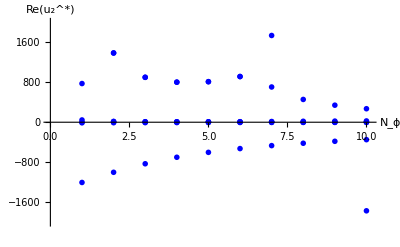

Phi4Trackingu2solsD3.jpg

```mathematica
ListPlot[TCFP3Sol,  PlotMarkers->{marker1, 0.02},AxesLabel->{Style["N_ϕ", FontSize->14],Style["Re(u_2^*)", FontSize->14]}, PlotRange->{{0,10.1}, {-2000,2000}}, TicksStyle->Directive[FontSize->13]]
Export["Phi4Trackingu2solsD3.jpg",%,"JPEG"]
```

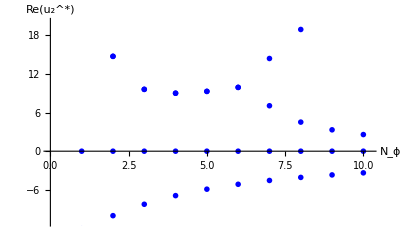

Phi4Trackingu2solsD3Zoom.jpg

```mathematica
ListPlot[TCFP3Sol, PlotRange->{{0,10.2}, {-11,20}}, PlotMarkers->{marker1, 0.02},AxesLabel->{Style["N_ϕ", FontSize->14],Style["Re(u_2^*)", FontSize->14]}, TicksStyle->Directive[FontSize->13]]
Export["Phi4Trackingu2solsD3Zoom.jpg",%,"JPEG"]
```

#### N(ϕ)=2, 4, 4000, 400000

First I check a random N_ϕ value to see if there are also imaginary solutions in this case, which as you can see below is true

```mathematica
FP3Solgen/. Nphi-> 2;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ3/. Nphi-> 2/.%[[]]
EV3s/. Nphi-> 2/.%%[[]]
```

{{U3[4,2,1]→0.,U3[4,2,2]→0.},{U3[4,2,1]→-1003.46,U3[4,2,2]→-274.464},{U3[4,2,1]→-10.0144,U3[4,2,2]→-2.73912},{U3[4,2,1]→1387.94+2512.83 ⅈ,U3[4,2,2]→-3264.58-2807.71 ⅈ},{U3[4,2,1]→1387.94-2512.83 ⅈ,U3[4,2,2]→-3264.58+2807.71 ⅈ},{U3[4,2,1]→14.7339+28.9944 ⅈ,U3[4,2,2]→-35.8674-33.0662 ⅈ},{U3[4,2,1]→14.7339-28.9944 ⅈ,U3[4,2,2]→-35.8674+33.0662 ⅈ}}

{0.,7.83978,-0.719177,7.81769+0.357528 ⅈ,7.81769-0.357528 ⅈ,-0.715763+0.275752 ⅈ,-0.715763-0.275752 ⅈ}

{{3.,3.},{-35.7031,10.041},{-3.2752,0.83945},{-31.0291-12.2969 ⅈ,-8.24323+16.1939 ⅈ},{-31.0291+12.2969 ⅈ,-8.24323-16.1939 ⅈ},{-3.26927+0.118133 ⅈ,-1.12845+1.16233 ⅈ},{-3.26927-0.118133 ⅈ,-1.12845-1.16233 ⅈ}}

```mathematica
FP3Solgen/. Nphi-> 4;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ3/. Nphi-> 4/.%[[]]
EV3s/. Nphi-> 4/.%%[[]]
```

{{U3[4,4,1]→0.,U3[4,4,4]→0.},{U3[4,4,1]→-7.43524×10^25-2.81096×10^26 ⅈ,U3[4,4,4]→-33942.1-655955. ⅈ},{U3[4,4,1]→-8.16296+3.84314 ⅈ,U3[4,4,4]→-2.17716+1.09195 ⅈ},{U3[4,4,1]→-8.16296-3.84314 ⅈ,U3[4,4,4]→-2.17716-1.09195 ⅈ},{U3[4,4,1]→-8.16296+3.84314 ⅈ,U3[4,4,4]→-2.17716+1.09195 ⅈ},{U3[4,4,1]→8.13762-12.2279 ⅈ,U3[4,4,4]→2.16949-2.87301 ⅈ},{U3[4,4,1]→8.13762+12.2279 ⅈ,U3[4,4,4]→2.16949+2.87301 ⅈ}}

{0.,7.-2.22045×10^-16 ⅈ,-0.0539529+0.0259213 ⅈ,-0.0539529-0.0259213 ⅈ,-0.0539529+0.0259213 ⅈ,0.0539243-0.0775487 ⅈ,0.0539243+0.0775487 ⅈ}

{{0.0307979,0.0307979},{2.27055×10^57+3.6029×10^57 ⅈ,2.27055×10^57+3.6029×10^57 ⅈ},{-0.346633-1.22761 ⅈ,-0.18675-1.42093 ⅈ},{-0.346633+1.22761 ⅈ,-0.18675+1.42093 ⅈ},{-0.346633-1.22761 ⅈ,-0.18675-1.42093 ⅈ},{-6.71979+6.0906 ⅈ,-6.46983+6.70102 ⅈ},{-6.71979-6.0906 ⅈ,-6.46983-6.70102 ⅈ}}

```mathematica
FP3Solgen/. Nphi-> 4000;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ3/. Nphi-> 4000/.%[[]]
EV3s/. Nphi-> 4000/.%%[[]]
```

{{U3[4,4000,1]→0.,U3[4,4000,2]→0.},{U3[4,4000,1]→0.00245273,U3[4,4000,2]→-6.06462},{U3[4,4000,1]→1.49072,U3[4,4000,2]→-2.91195},{U3[4,4000,1]→0.0000151235,U3[4,4000,2]→-0.0372173},{U3[4,4000,1]→-1.01292,U3[4,4000,2]→-0.000129671},{U3[4,4000,1]→-0.00953565,U3[4,4000,2]→-1.22072×10^-6},{U3[4,4000,1]→-0.0742969,U3[4,4000,2]→0.145131}}

{0.,7.31245,6.00197,-1.17396,7.65227,-0.869075,-2.99607}

{{3.,3.},{-70.1543,-21.6866},{-9.00983,59.8466},{-3.48163,-2.59552},{-29.4152,18.2949},{-3.34071,1.26119},{-11.9349,-4.49755}}

Here all the solutions have become real, which means we need to check which one correspond to which one.

```mathematica
FP3Solgen/. Nphi-> 4000000;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ3/. Nphi-> 4000000/.%[[]]
EV3s/. Nphi-> 4000000/.%%[[]]
```

{{U3[4,4000000,1]→0.,U3[4,4000000,2]→0.},{U3[4,4000000,1]→-0.0000162933,U3[4,4000000,2]→-0.00608344},{U3[4,4000000,1]→0.00149733,U3[4,4000000,2]→-0.00292428},{U3[4,4000000,1]→1.51003×10^-11,U3[4,4000000,2]→-0.0000372375},{U3[4,4000000,1]→-0.0010133,U3[4,4000000,2]→-1.29702×10^-10},{U3[4,4000000,1]→-9.53857×10^-6,U3[4,4000000,2]→-1.22094×10^-12},{U3[4,4000000,1]→-0.0000739978,U3[4,4000000,2]→0.000144527}}

{0.,7.30878,6.00724,-1.17501,7.65216,-0.86917,-2.98586}

{{3.,3.},{-71.5772,-21.5918},{-9.03608,60.0607},{-3.48213,-2.59994},{-29.412,18.3043},{-3.34075,1.26166},{-11.8868,-4.49117}}

#### Finding the splitting point

```mathematica
EV3d3= {{0,0 },{0,0} } ;
EV3d3theta1={{0,0}} ;
EV3d3theta2={{0,0}}; 
Do[S=FP3Solgen/. Nphi-> x;
sols = S /.(lhs_->rhs_):>lhs->N[rhs];
EV3stry=EV3s/. Nphi-> x/. sols[[]];
EV3d3 =Append[EV3d3,{ -EV3stry[[3]]}];
EV3s3 = EV3stry[[3]];
theta1 = -EV3s3[[1]];
theta2 = -EV3s3[[2]];
 EV3d3theta1 = Append[EV3d3theta1,{x,theta1}];
 EV3d3theta2 = Append[EV3d3theta2,{x,theta2}], {x, 2, 100, 1}]
```

```mathematica
EV3d3
```

{{0,0},{0,0},{{3.2752,-0.83945}},{{3.29254,-0.888443}},{{3.30295,-0.939359}},{{3.30974,-0.981543}},{{3.3145,-1.01525}},{{38.2905,5.95356}},{{33.6412,11.3754}},{{2.9689,-3.17002}},{{2.89513,-4.42424}},{{2.82658,-5.80455}},{{2.76678,-7.33348}},{{2.72149,-9.021}},{{2.69832,-10.8617}},{{2.70558,-12.8307}},{{2.7502,-14.8827}},{{2.83532,-16.9583}},{{2.95892,-18.9969}},{{3.11441,-20.949}},{{3.29278,-22.7831}},{{3.48492,-24.4847}},{{3.68307,-26.0526}},{{3.88134,-27.4927}},{{4.07568,-28.8152}},{{4.26347,-30.031}},{{4.44321,-31.1513}},{{4.61414,-32.1864}},{{4.776,-33.1453}},{{4.92888,-34.0364}},{{5.07306,-34.8666}},{{5.20893,-35.6423}},{{5.33695,-36.3687}},{{5.45761,-37.0507}},{{5.57138,-37.6924}},{{5.67874,-38.2974}},{{5.78013,-38.8689}},{{5.87597,-39.4098}},{{5.96666,-39.9225}},{{6.05256,-40.4093}},{{6.13402,-40.8722}},{{6.21133,-41.313}},{{6.2848,-41.7332}},{{6.35468,-42.1344}},{{6.42121,-42.5178}},{{6.48463,-42.8847}},{{6.54513,-43.2361}},{{6.6029,-43.573}},{{6.65812,-43.8964}},{{6.71094,-44.2069}},{{6.76152,-44.5055}},{{6.80999,-44.7928}},{{6.85647,-45.0695}},{{6.90109,-45.3361}},{{6.94394,-45.5931}},{{6.98514,-45.8412}},{{7.02477,-46.0808}},{{7.06292,-46.3123}},{{7.09966,-46.5361}},{{7.13508,-46.7527}},{{7.16925,-46.9623}},{{7.20222,-47.1653}},{{7.23406,-47.362}},{{7.26482,-47.5527}},{{7.29456,-47.7378}},{{7.32333,-47.9173}},{{7.35117,-48.0916}},{{7.37813,-48.2609}},{{7.40424,-48.4255}},{{7.42955,-48.5855}},{{7.4541,-48.7411}},{{7.47791,-48.8924}},{{7.50102,-49.0398}},{{7.52346,-49.1833}},{{7.54525,-49.323}},{{7.56644,-49.4592}},{{7.58703,-49.5919}},{{7.60705,-49.7213}},{{7.62653,-49.8475}},{{7.64549,-49.9707}},{{7.66395,-50.0909}},{{7.68193,-50.2082}},{{7.69945,-50.3228}},{{7.71652,-50.4348}},{{7.73316,-50.5442}},{{7.74939,-50.6511}},{{7.76522,-50.7556}},{{7.78067,-50.8578}},{{7.79575,-50.9577}},{{7.81047,-51.0555}},{{7.82485,-51.1512}},{{7.83889,-51.2449}},{{7.85262,-51.3367}},{{7.86603,-51.4265}},{{7.87915,-51.5145}},{{7.89197,-51.6007}},{{7.90451,-51.6851}},{{7.91679,-51.7679}},{{7.9288,-51.8491}},{{7.94055,-51.9287}},{{7.95206,-52.0067}}}

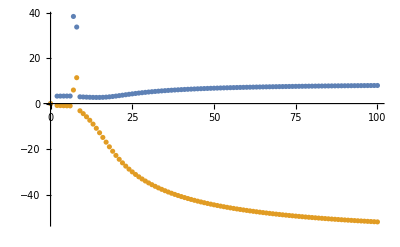

```mathematica
ListPlot[{EV3d3theta1,EV3d3theta2}]
```

It seems the border lies at N=7 so let’s try N=6 and N=7 to be sure

```mathematica
FP3Solgen/. Nphi-> 7;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ3/. Nphi-> 7/.%[[]]
EV3s/. Nphi-> 7/.%%[[]]
```

{{U3[4,7,1]→0.,U3[4,7,2]→0.},{U3[4,7,1]→1738.55,U3[4,7,2]→-4231.06},{U3[4,7,1]→706.192,U3[4,7,2]→-2301.69},{U3[4,7,1]→-468.914,U3[4,7,2]→-36.3793},{U3[4,7,1]→14.3989,U3[4,7,2]→-35.0422},{U3[4,7,1]→7.06044,U3[4,7,2]→-23.012},{U3[4,7,1]→-4.54459,U3[4,7,2]→-0.352578}}

{0.,8.31444,7.90228,7.71477,-0.386988,-0.671762,-0.817786}

{{3.,3.},{-67.4552,6.88827},{-38.2905,-5.95356},{-31.3012,14.0781},{-3.13963,0.781209},{-3.25503,-0.524442},{-3.31801,1.04227}}

```mathematica
FP7d3= {{0.,0.},{1738.5463263101717,-4231.061758404251},{706.1920220779483,-2301.686502230658},{-468.913925746166,-36.379270088775634},{14.398900421490842,-35.042239752429936},{7.060435905900913,-23.012021471621328},{-4.544590566343359,-0.35257832744641676}}
```

{{0.,0.},{1738.55,-4231.06},{706.192,-2301.69},{-468.914,-36.3793},{14.3989,-35.0422},{7.06044,-23.012},{-4.54459,-0.352578}}

```mathematica
FP3Solgen/. Nphi-> 6;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ3/. Nphi-> 6/.%[[]]
EV3s/. Nphi-> 6/.%%[[]]
```

{{U3[4,6,1]→0.,U3[4,6,2]→0.},{U3[4,6,1]→-528.273,U3[4,6,2]→-48.1442},{U3[4,6,1]→-5.13864,U3[4,6,2]→-0.468311},{U3[4,6,1]→915.575+558.445 ⅈ,U3[4,6,2]→-2622.19-943.589 ⅈ},{U3[4,6,1]→915.575-558.445 ⅈ,U3[4,6,2]→-2622.19+943.589 ⅈ},{U3[4,6,1]→9.91153+5.33415 ⅈ,U3[4,6,2]→-28.0151-8.4042 ⅈ},{U3[4,6,1]→9.91153-5.33415 ⅈ,U3[4,6,2]→-28.0151+8.4042 ⅈ}}

{0.,7.72465,-0.809808,7.99223+0.250146 ⅈ,7.99223-0.250146 ⅈ,-0.596575+0.180214 ⅈ,-0.596575-0.180214 ⅈ}

{{3.,3.},{-31.6166,13.5691},{-3.3145,1.01525},{-39.4815-12.2783 ⅈ,-0.947127+8.66019 ⅈ},{-39.4815+12.2783 ⅈ,-0.947127-8.66019 ⅈ},{-3.2216+0.0745818 ⅈ,-0.233152+0.812398 ⅈ},{-3.2216-0.0745818 ⅈ,-0.233152-0.812398 ⅈ}}

```mathematica
FP6d3= {{0.,0.},{-528.2731091984815,-48.14422846150722},{-5.138642979289184,-0.4683107984663053},{915.574858648698+558.4445019625131 ⅈ,-2622.189495586218-943.5890952774422 ⅈ},{915.574858648698-558.4445019625131 ⅈ,-2622.189495586218+943.5890952774422 ⅈ},{9.911531451128928+5.334151237496998 ⅈ,-28.015127304167237-8.404200239350585 ⅈ},{9.911531451128928-5.334151237496998 ⅈ,-28.015127304167237+8.404200239350585 ⅈ}}
```

{{0.,0.},{-528.273,-48.1442},{-5.13864,-0.468311},{915.575+558.445 ⅈ,-2622.19-943.589 ⅈ},{915.575-558.445 ⅈ,-2622.19+943.589 ⅈ},{9.91153+5.33415 ⅈ,-28.0151-8.4042 ⅈ},{9.91153-5.33415 ⅈ,-28.0151+8.4042 ⅈ}}

Here it becomes clear that N=6 has imaginary solutions, while N=7 is fully real. Next step is to connect the two solutions.

```mathematica
FP3Solgen/. Nphi-> 8;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ3/. Nphi-> 8/.%[[]]
EV3s/. Nphi-> 8/.%%[[]]
```

{{U3[4,8,1]→0.,U3[4,8,2]→0.},{U3[4,8,1]→4923.76,U3[4,8,2]→-11102.7},{U3[4,8,1]→456.627,U3[4,8,2]→-1846.3},{U3[4,8,1]→18.9074,U3[4,8,2]→-42.6345},{U3[4,8,1]→-421.23,U3[4,8,2]→-28.4311},{U3[4,8,1]→4.51835,U3[4,8,2]→-18.2693},{U3[4,8,1]→-4.07042,U3[4,8,2]→-0.274735}}

{0.,8.73608,7.78449,-0.137914,7.70725,-0.762158,-0.823888}

{{3.,3.},{-193.034,15.0283},{-33.6412,-11.3754},{-3.04736,2.00047},{-31.0642,14.4926},{-3.29372,-0.904005},{-3.32069,1.06423}}

```mathematica
FP9d3= {{0,0}, {341.5740767999567,-1613.669747113819}, {22.408839530036474,-48.888150210216104}, {-382.1743893600854,-22.818874661182264 }, {3.3204018639682658, -15.68629588369794}, {-3.684072722147722,-0.2199686740656026 }, {-6793.416129147245, 14820.551222175816}}
```

{{0,0},{341.574,-1613.67},{22.4088,-48.8882},{-382.174,-22.8189},{3.3204,-15.6863},{-3.68407,-0.219969},{-6793.42,14820.6}}

#### Connecting the solutions

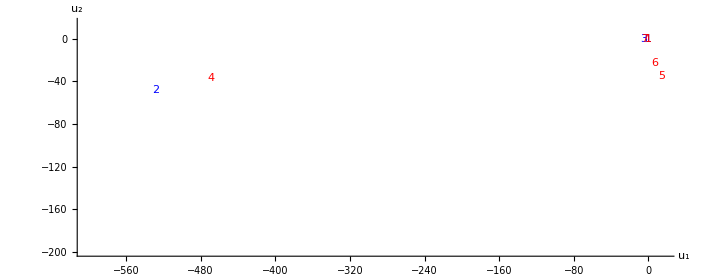

```mathematica
Show[Graphics[{Blue,MapIndexed[Text[First@#2,#1]&,FP6d3[[1;;3]]/.Rule->List],Red,MapIndexed[Text[First@#2,#1]&,FP7d3/.Rule->List]},Axes->True,AxesLabel->{Style["u_1", FontSize->14],Style["u_2", FontSize->14]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotRange-> {{-600,15},{-200,15}}, TicksStyle->Directive[FontSize->12]]]
```

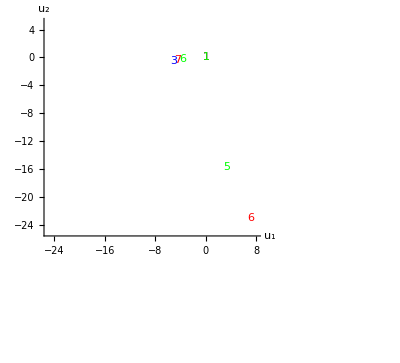

```mathematica
Show[Graphics[{Blue,MapIndexed[Text[First@#2,#1]&,FP6d3[[1;;3]]/.Rule->List],Red,MapIndexed[Text[First@#2,#1]&,FP7d3/.Rule->List], Green, MapIndexed[Text[First@#2,#1]&,FP9d3/.Rule->List]},Axes->True,AxesLabel->{Style["u_1", FontSize->14],Style["u_2", FontSize->14]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotRange-> {{-25,8},{-25,5}}], TicksStyle->Directive[FontSize->12]]
```

```mathematica
Export["fixedpointpositionsN6enN7largelabeld3.jpg", %231, "JPEG"]
Export["fixedpointpositionsN6enN7enN=9largelabeld3.jpg", %228, "JPEG"]
```

fixedpointpositionsN6enN7largelabeld3.jpg

fixedpointpositionsN6enN7enN=9largelabeld3.jpg

So it looks like 1->1, 2->4 and 3->7.

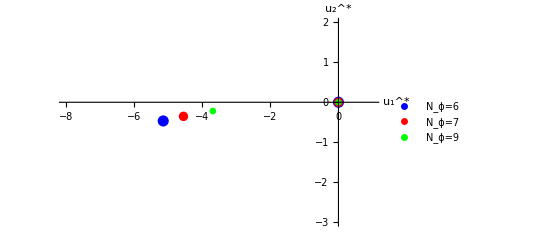

```mathematica
ListPlot[{FP6d3, FP7d3, FP9d3}, PlotStyle->{{Blue,PointSize[0.02]},  {Red, PointSize[0.017]}, {Green, PointSize[0.012]}},AxesLabel-> {"u_1^*", "u_2^*"},  PlotLegends->{"N_ϕ=6","N_ϕ=7", "N_ϕ=9"}, PlotRange->{{-8,1}, {-3, 2}}]
```

```mathematica
Export["fixedpointpositionsN6enN7enN=9largelabeld3dots.jpg", %, "JPEG"]
```

fixedpointpositionsN6enN7enN=9largelabeld3dots.jpg

#### What appears due to the anomalous dimension?

```mathematica
Clear[ηϕ3]
```

```mathematica
FPeta0 = Solve[Simplify[Coefficient[RHS3phi4, X, 2]]==Coefficient[LHS3finalphi4, X, 2]&&Simplify[Coefficient[RHS3phi4,S2]]==Coefficient[LHS3finalphi4, S2]/. k-> 1/. ηϕ3-> 0, {U3[4,Nphi, 1], U3[4,Nphi, 2]}]/.Nphi-> 2
```

```mathematica
FPeta0/.(lhs_->rhs_):>lhs->N[rhs]
```

```mathematica
etatrack3fp1= {};
etatrack3fp2 = {};
etatrack3fp3 = {};
Do[
βϕ3[4,Nphi,1]=0;
βϕ3[4,Nphi,2]=0;
Nphi =2; 
ηϕ3= ϵ(7 (2 U3[4,Nphi,1]+3 Nphi U3[4,Nphi,1]+4 U3[4,Nphi,2]+Nphi U3[4,Nphi,2]))/(105 π^2+2 U3[4,Nphi,1]+3 Nphi U3[4,Nphi,1]+4 U3[4,Nphi,2]+Nphi U3[4,Nphi,2]);/. Nphi-> 2;
FP3 = Solve[Simplify[Coefficient[RHS3phi4, X, 2]]==Coefficient[LHS3finalphi4, X, 2]&&Simplify[Coefficient[RHS3phi4,S2]]==Coefficient[LHS3finalphi4, S2]/. k-> 1, {U3[4,Nphi, 1], U3[4,Nphi, 2]}];
 AppendTo[etatrack3fp1,{U3[4, Nphi, 1], U3[4, Nphi, 2]}/.FP3[[1]] ];
 AppendTo[etatrack3fp2,{U3[4, Nphi, 1], U3[4, Nphi, 2]}/.FP3[[2]] ];
 AppendTo[etatrack3fp3, {U3[4, Nphi, 1], U3[4, Nphi, 2]}/.FP3[[3] ]];, 
 {ϵ, 1/1000, 1, 1/1000}]
```

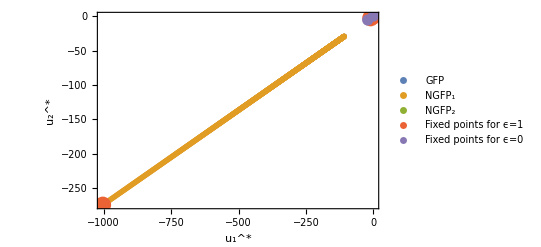

```mathematica
ListPlot[{etatrack3fp1, etatrack3fp2, etatrack3fp3, {{0, 0},{-1003.4607776360507, -274.46377179637875},{-10.014448587589726,-2.7391238333060683}}, {{0,0},{-20.775554012939953,-5.6824711464895215}}}, PlotLegends->{"GFP", "NGFP_1", "NGFP_2", "Fixed points for ϵ=1", "Fixed points for ϵ=0"}, PlotStyle->{PointSize[0.01],PointSize[0.01],PointSize[0.01], PointSize[0.03], PointSize[0.02]}, FrameLabel->{Style["u_1^*", FontSize->14],Style["u_2^*", FontSize->14]}, Frame-> {{True,True},{True, True}}, TicksStyle->Directive[FontSize->13], PlotRange->All]
```

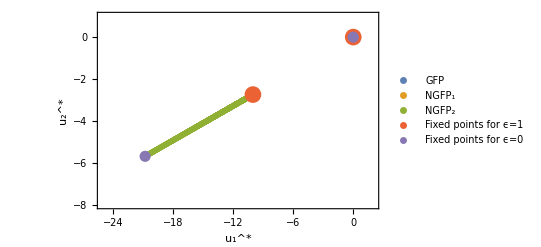

```mathematica
ListPlot[{etatrack3fp1, etatrack3fp2, etatrack3fp3, {{0, 0},{-1003.4607776360507, -274.46377179637875},{-10.014448587589726,-2.7391238333060683}}, {{0,0},{-20.775554012939953,-5.6824711464895215}}}, PlotLegends->{"GFP", "NGFP_1", "NGFP_2", "Fixed points for ϵ=1", "Fixed points for ϵ=0"}, PlotStyle->{PointSize[0.01],PointSize[0.01],PointSize[0.01], PointSize[0.03], PointSize[0.02]}, FrameLabel->{Style["u_1^*", FontSize->14],Style["u_2^*", FontSize->14]}, TicksStyle->Directive[FontSize->13], PlotRange->{{-25, 2}, {-8, 1}}, Frame-> True]
```

```mathematica
Export["Increasingepsilonforanomalousdimfrom0to1fullimagephi4d3Frame.jpg", %261, "JPEG"]
```

Increasingepsilonforanomalousdimfrom0to1fullimagephi4d3Frame.jpg

```mathematica
Export["Increasingepsilonforanomalousdimfrom0to1zoomintofp1phi4d3.jpg", %259, "JPEG"]
```

Increasingepsilonforanomalousdimfrom0to1zoomintofp1phi4d3.jpg

### Plotting the interesting FP

#### Collecting the FP and θ_i

Here in the next block the same type of loop is used to now calculate the fixed point in three dimensions. This is done in three different blocks, belonging to the three different solution groups (N_ϕ<7, 7≤N_ϕ ≤ 8 and N_ϕ> 8)

```mathematica
U3v1value = {};(*Saves fixed point coordinate 1*)
U3v2value = {};(*Saves fixed point coordinate 2*)
EV3theta1 = {};(*Saves minus the first eigenvalue*)
EV3theta2 = {};(*Saves minus the second eigenvalue*)
EV={}
Do[S=FP3Solgen/. Nphi-> x;
sols = S /.(lhs_->rhs_):>lhs->N[rhs];
FPs3 = sols[[3]];
evs3 = EV3s/.Nphi-> x/. FPs3; 
FPvalue1 = U3[4,x,1]/.FPs3[[1]];
FPvalue2 = U3[4,x,2]/.FPs3[[2]];
 U3v1value = Append[U3v1value,{x,FPvalue1}];
 U3v2value = Append[U3v2value,{x,FPvalue2}];
theta1 = -evs3[[1]];
theta2 = -evs3[[2]];
 EV3theta1 = Append[EV3theta1,{x,theta1}];
 EV3theta2 = Append[EV3theta2,{x,theta2}], {x,2, 6}]
Do[S=FP3Solgen/. Nphi-> x;
sols = S /.(lhs_->rhs_):>lhs->N[rhs];
FPs7 = sols[[7]];
evs7 = EV3s/.Nphi-> x/. FPs7; 
FPvalue1 = U3[4,x,1]/.FPs7[[1]];
FPvalue2 = U3[4,x,2]/.FPs7[[2]];
 U3v1value = Append[U3v1value,{x,FPvalue1}];
 U3v2value = Append[U3v2value,{x,FPvalue2}];
theta1 = -evs7[[1]];
theta2 = -evs7[[2]];
 EV3theta1 = Append[EV3theta1,{x,theta1}];
 EV3theta2 = Append[EV3theta2,{x,theta2}], {x,7, 8}]
Do[S=FP3Solgen/. Nphi-> x;
sols = S /.(lhs_->rhs_):>lhs->N[rhs];
FPs6 = sols[[6]];
evs6 = EV3s/. Nphi-> x/.FPs6; 
FPvalue1 = U3[4, x, 1]/.FPs6[[1]];
FPvalue2 = U3[4, x, 2]/. FPs6[[2]];
 U3v1value = Append[U3v1value,{x,FPvalue1}];
 U3v2value = Append[U3v2value,{x,FPvalue2}];
theta1 = -evs6[[1]];
theta2 = -evs6[[2]];
 EV3theta1 = Append[EV3theta1,{x,theta1}];
 EV3theta2 = Append[EV3theta2,{x,theta2}], {x,9, 2000}]
```

{}

Next step is then to determine the anomalous dimension for increasing N

```mathematica
AnomalousDimd3phi4 = {}
Do [eta = (7 (2 U3[4,1]+3 Nphi U3[4,1]+4 U3[4,2]+Nphi U3[4,2]))/(105 π^2+2 U3[4,1]+3 Nphi U3[4,1]+4 U3[4,2]+Nphi U3[4,2])/. U3[4,1]->  U3v1value[[x-1]][[2]]/. U3[4,2]-> U3v2value[[x-1]][[2]]/. Nphi-> x;
AnomalousDimd3phi4 = Append[AnomalousDimd3phi4, {x, eta}], {x, 2, 1000}]
```

{}

#### Save the values from N_ϕ=2 to 1000

```mathematica
DumpSave["FPphi4d3U1.mx", U3v1value];
DumpSave["FPphi4d3U2.mx", U3v2value];
DumpSave["FPphi4d3EV1.mx", EV3theta1];
DumpSave["FPphi4d3EV2.mx", EV3theta2];
DumpSave["Anomalous dimension d3 phi^4", AnomalousDimd3phi4];
```

```mathematica
DumpGet["FPphi4d3U1.mx"];
DumpGet["FPphi4d3U2.mx"];
DumpGet["FPphi4d3EV1.mx"];
DumpGet["FPphi4d3EV2.mx"];
DumpGet["Anomalous dimension d3 phi^4"];
```

#### Plot the figures

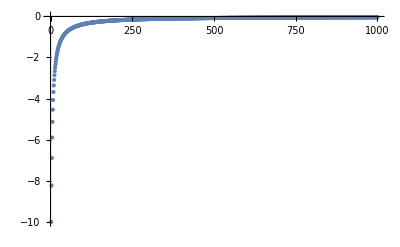

```mathematica
ListPlot[U3v1valueto1000, PlotRange->All]
```

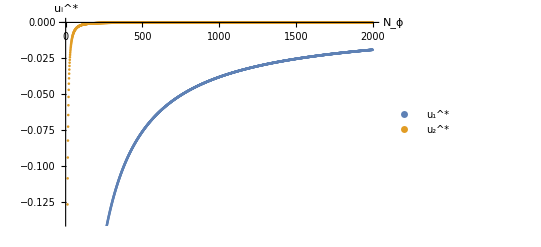

```mathematica
ListPlot[{U3v1value,U3v2value}, PlotLegends->{"u_1^*", "u_2^*"}, AxesLabel->{"N_ϕ", "u_i^*"}]
```

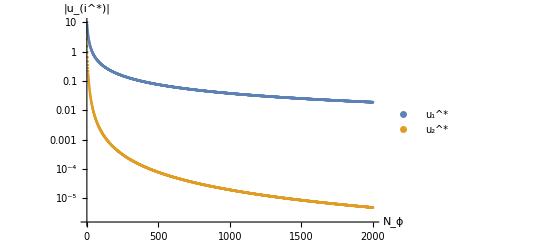

```mathematica
ListLogPlot[{U3v1value *Threaded[{1,-1}],U3v2value*Threaded[{1,-1}]}, PlotLegends->{Style["u_1^*", FontSize->12], Style["u_2^*", FontSize->12]}, AxesLabel->{Style["N_ϕ", FontSize->12],Style["|u_(i^*)|", FontSize->12]}, TicksStyle->Directive[FontSize->10]]
```

```mathematica
Export["Phi4IncreasingNphiUvaluesd3labelCorrect.jpg", %, "JPEG"]
```

Phi4IncreasingNphiUvaluesd3labelCorrect.jpg

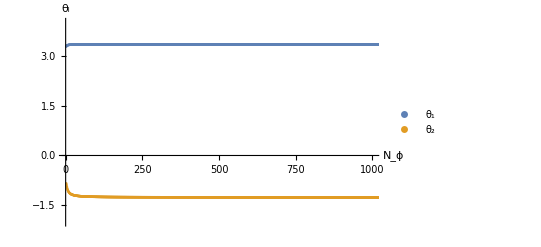

```mathematica
ListPlot[{EV3theta1,EV3theta2}, PlotRange->{{ 0, 1001 }, { -2, 4}}, PlotLegends->{"θ_1", "θ_2"}, AxesLabel->{"N_ϕ", "θ_i"}]
```

Export["Phi4IncreasingNphithetavaluesd3.jpg", %111, "JPEG"]

Phi4IncreasingNphithetavaluesd3.jpg

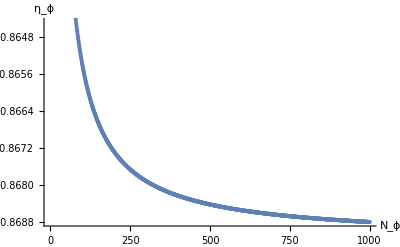

```mathematica
ListPlot[AnomalousDimd3phi4, AxesLabel->{"N_ϕ", "η_ϕ"}]
```

## Large N_ϕ-expansion

## Expanding the fixed points

```mathematica
Clear[ηϕ3];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[βϕ3];
```

```mathematica
U1ExpPhi4d3 = U3[4, Nphi, 1]-> U3[1,1] Nphi^-1+ U3[1,2] Nphi^-2+ U3[1,3] Nphi^-3;
U2ExpPhi4d3 = U3[4, Nphi, 2]-> U3[2,1] Nphi^-1+ U3[2,2] Nphi^-2+ U3[2,3] Nphi^-3
```

U3[4,Nphi,2]→U3[2,1]/Nphi+U3[2,2]/Nphi^2+U3[2,3]/Nphi^3

```mathematica
RHSphi4d3Exp = Normal[Series[RHS3phi4/. U1ExpPhi4d3/.U2ExpPhi4d3, {Nphi, ∞, 1}]];
LHSphi4d3Exp = Normal[Series[LHS3finalphi4/. U1ExpPhi4d3/.U2ExpPhi4d3, {Nphi, ∞, 1}]];
```

```mathematica
ηϕ3Exp = Normal[Series[ηϕ3/. Solve[Simplify[Coefficient[RHSphi4d3Exp, X, 1]]==Coefficient[LHSphi4d3Exp, X, 1], ηϕ3], {Nphi, ∞, 0}]]
```

{(7 U3[1,1])/(35 π^2+U3[1,1])}

```mathematica
ηϕ3= ηϕ3Exp[[1]]
βϕ3[4,Nphi, 1]= 0;(*Both beta functions appearing in ∂_t Subscript[F, k] are set to 0*)
βϕ3[4,Nphi, 2]=0;
FPSolExp= Solve[Simplify[Coefficient[RHSphi4d3Exp, X, 2]]==Coefficient[LHSphi4d3Exp, X, 2]&&Simplify[Coefficient[RHSphi4d3Exp,S2]]==Coefficient[LHSphi4d3Exp, S2]/. k-> 1, {U3[1, 1], U3[ 2,1]}]
```

(7 (3 U3[1,1]+U3[2,1]))/(105 π^2+3 U3[1,1]+U3[2,1])

{{U3[1,1]→0,U3[2,1]→0},{U3[1,1]→63/100 (-329-√104241) π^2,U3[2,1]→0},{U3[1,1]→63/100 (-329+√104241) π^2,U3[2,1]→0},{U3[1,1]→0,U3[2,1]→315/16 (-63-√3873) π^2},{U3[1,1]→0,U3[2,1]→315/16 (-63+√3873) π^2},{U3[1,1]→(252 (1917+√4478889) π^2)/1675,U3[2,1]→(315 (-1917-√4478889) π^2)/1072},{U3[1,1]→(252 (1917-√4478889) π^2)/1675,U3[2,1]→(315 (-1917+√4478889) π^2)/1072}}

```mathematica
FPSolExp/.(lhs_->rhs_):>lhs->N[rhs]
```

{{U3[1,1]→0.,U3[2,1]→0.},{U3[1,1]→-4053.19,U3[2,1]→0.},{U3[1,1]→-38.1543,U3[2,1]→0.},{U3[1,1]→0.,U3[2,1]→-24333.8},{U3[1,1]→0.,U3[2,1]→-148.95},{U3[1,1]→5988.94,U3[2,1]→-11697.2},{U3[1,1]→-295.99,U3[2,1]→578.105}}

Check with a fit to find which solution to take

```mathematica
FitFP1phi4d3 =Fit[Take[U3v1value, -1500], { 1/y,1/y^2, 1/y^3}, y]
FitFP2phi4d3 =Fit[Take[U3v2value, -1500], { 1/y,1/y^2,1/y^3}, y]
```

-13.9121/y^3+46.7368/y^2-38.1543/y

14.0978/y^3-19.5351/y^2+(2.05812×10^-8)/y

Clearly the third solution found for the expansion seems to fit with the data best.

### Check with extra term:

As the result gives U[2,1]=0 I have also verified this, without including the U[2,1] term and taking an extra order of the expansion.

```mathematica
Clear[ηϕ3];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[βϕ3];
U1ExpPhi4d3ExtraOrder = U3[4, Nphi, 1]-> U3[1,1] Nphi^-1+ U3[1,2] Nphi^-2+ U3[1,3] Nphi^-3;
U2ExpPhi4d3ExtraOrder = U3[4, Nphi, 2]->  U3[2,2] Nphi^-2+ U3[2,3] Nphi^-3;
RHSphi4d3Exp = Normal[Series[RHS3phi4/. U1ExpPhi4d3ExtraOrder/.U2ExpPhi4d3ExtraOrder, {Nphi, ∞, 2}]];
LHSphi4d3Exp = Normal[Series[LHS3finalphi4/. U1ExpPhi4d3ExtraOrder/.U2ExpPhi4d3ExtraOrder, {Nphi, ∞, 2}]];
ηϕ3Exp = Normal[Series[ηϕ3/. Solve[Simplify[Coefficient[RHSphi4d3Exp, X, 1]]==Coefficient[LHSphi4d3Exp, X, 1], ηϕ3], {Nphi, ∞, 0}]]
```

{(7 U3[1,1])/(35 π^2+U3[1,1])}

```mathematica
ηϕ3= ηϕ3Exp[[1]]
βϕ3[4,Nphi, 1]= 0;(*Both beta functions appearing in ∂_t Subscript[F, k] are set to 0*)
βϕ3[4,Nphi, 2]=0;
FPSolExp= Solve[Simplify[Coefficient[Coefficient[RHSphi4d3Exp, X, 2], Nphi, -2]]==Coefficient[Coefficient[LHSphi4d3Exp, X, 2], Nphi, -2]&&Simplify[Coefficient[Coefficient[RHSphi4d3Exp,S2], Nphi, -2]]==Coefficient[Coefficient[LHSphi4d3Exp, S2], Nphi, -2]&&
Simplify[Coefficient[Coefficient[RHSphi4d3Exp, X, 2], Nphi, -1]]==Coefficient[Coefficient[LHSphi4d3Exp, X, 2], Nphi, -1]&&Simplify[Coefficient[Coefficient[RHSphi4d3Exp,S2], Nphi, -1]]==Coefficient[Coefficient[LHSphi4d3Exp, S2], Nphi, -1]/. k-> 1, {U3[1, 1],U3[1,2], U3[ 2,2]}]
```

(7 U3[1,1])/(35 π^2+U3[1,1])

{{U3[1,1]→0,U3[1,2]→0,U3[2,2]→0},{U3[1,1]→63/100 (-329-√104241) π^2,U3[1,2]→(91728 (329+√104241) π^2)/78125,U3[2,2]→(1008 (-329-√104241) π^2)/3125},{U3[1,1]→63/100 (-329+√104241) π^2,U3[1,2]→(91728 (329-√104241) π^2)/78125,U3[2,2]→(1008 (-329+√104241) π^2)/3125}}

```mathematica
FPSolExp/.(lhs_->rhs_):>lhs->N[rhs]
```

{{U3[1,1]→0.,U3[1,2]→0.,U3[2,2]→0.},{U3[1,1]→-4053.19,U3[1,2]→7553.85,U3[2,2]→-2075.23},{U3[1,1]→-38.1543,U3[1,2]→71.1074,U3[2,2]→-19.535}}

Again the third result is the intended solution!

Use this to determine the anomalous dimension:

```mathematica
AnDimphi4d3Exp = (7 U3[1,1])/(35 π^2+U3[1,1])/.U3[1,1]->-38.15429704998576
```

-0.86917

```mathematica
FitAndim3phi4 =Fit[Take[AnomalousDimd3phi4, -500], {1, 1/y, 1/y^2}, y]
```

-0.86917-0.12236/y^2+0.378729/y

This also corresponds exactly to the value obtained from the fit!

## Expand the stability matrix

### Only lowest order included:

```mathematica
Bexp[1,1]= Normal[Series[D[βϕ3[U3[4,Nphi, 1], U3[4,Nphi, 2]][4,Nphi, 1], U3[4, Nphi, 1]]/. U1ExpPhi4d3/.U2ExpPhi4d3/.{U3[1,1]->-38.15429704998576,U3[2,1]->0.}, {Nphi, ∞, 0}]]
Bexp[2,1]= Normal[Series[D[βϕ3[U3[4,Nphi, 1], U3[4,Nphi, 2]][4,Nphi, 2], U3[4, Nphi, 1]]/. U1ExpPhi4d3/.U2ExpPhi4d3/.{U3[1,1]->-38.15429704998576,U3[2,1]->0.}, {Nphi, ∞, 0}]]
Bexp[1,2]= Normal[Series[D[βϕ3[U3[4,Nphi, 1], U3[4,Nphi, 2]][4,Nphi, 1], U3[4, Nphi, 2]]/. U1ExpPhi4d3/.U2ExpPhi4d3/.{U3[1,1]->-38.15429704998576,U3[2,1]->0.}, {Nphi, ∞, 0}]]
Bexp[2,2]= Normal[Series[D[βϕ3[U3[4,Nphi, 1], U3[4,Nphi, 2]][4,Nphi, 2], U3[4, Nphi, 2]]/. U1ExpPhi4d3/.U2ExpPhi4d3/.{U3[1,1]->-38.15429704998576,U3[2,1]->0.}, {Nphi, ∞, 0}]]
```

-3.34075

0

-1.50049

1.26166

```mathematica
Matphi4d3Exp = Table[Bexp[a,b],{a,1,2},{b,1,2}];
%//MatrixForm
Eigenvalues[Matphi4d3Exp]
```

(-3.34075 | -1.50049
0 | 1.26166)

{-3.34075,1.26166}

### Include the extra order:

To see if the term that is now zero, due to the zero U[2,1] changes anything, we check for one order higher in the expansion as well.

```mathematica
BexpExtraOrder[1,1]= Normal[Series[D[βϕ3[U3[4,Nphi, 1], U3[4,Nphi, 2]][4,Nphi, 1], U3[4, Nphi, 1]]/. U1ExpPhi4d3ExtraOrder/.U2ExpPhi4d3ExtraOrder/.{U3[1,1]->-38.15429704998576,U3[1,2]->71.10740032611746,U3[2,2]->-19.535000089592707}, {Nphi, ∞, 1}]]
BexpExtraOrder[2,1]= Normal[Series[D[βϕ3[U3[4,Nphi, 1], U3[4,Nphi, 2]][4,Nphi, 2], U3[4, Nphi, 1]]/. U1ExpPhi4d3ExtraOrder/.U2ExpPhi4d3ExtraOrder/.{U3[1,1]->-38.15429704998576,U3[1,2]->71.10740032611746,U3[2,2]->-19.535000089592707}, {Nphi, ∞, 1}]]
BexpExtraOrder[1,2]= Normal[Series[D[βϕ3[U3[4,Nphi, 1], U3[4,Nphi, 2]][4,Nphi, 1], U3[4, Nphi, 2]]/. U1ExpPhi4d3ExtraOrder/.U2ExpPhi4d3ExtraOrder/.{U3[1,1]->-38.15429704998576,U3[1,2]->71.10740032611746,U3[2,2]->-19.535000089592707}, {Nphi, ∞, 1}]]
BexpExtraOrder[2,2]= Normal[Series[D[βϕ3[U3[4,Nphi, 1], U3[4,Nphi, 2]][4,Nphi, 2], U3[4, Nphi, 2]]/. U1ExpPhi4d3ExtraOrder/.U2ExpPhi4d3ExtraOrder/.{U3[1,1]->-38.15429704998576,U3[1,2]->71.10740032611746,U3[2,2]->-19.535000089592707}, {Nphi, ∞, 1}]]
```

-3.34075+5.69411/Nphi

-2.35644/Nphi

-1.50049-3.59282/Nphi

1.26166-1.4214/Nphi

```mathematica
Matphi4d3ExpExtra = Table[BexpExtraOrder[a,b],{a,1,2},{b,1,2}];
%//MatrixForm
Eigenvalues[Matphi4d3ExpExtra]
```

(-3.34075+5.69411/Nphi | -1.50049-3.59282/Nphi
-2.35644/Nphi | 1.26166-1.4214/Nphi)

{(0.5 (4.27271-2.07909 Nphi-√(84.4954-51.3537 Nphi+21.1822 Nphi^2)))/Nphi,(0.5 (4.27271-2.07909 Nphi+√(84.4954-51.3537 Nphi+21.1822 Nphi^2)))/Nphi}

```mathematica
Series[Eigenvalues[Matphi4d3ExpExtra], {Nphi, ∞, 0}]
```

{-3.34075+O[1/Nphi]^1,1.26166+O[1/Nphi]^1}

The values independent of N are still the same, so it can be concluded that this did not have any additional effects. 
Lastly, we do a quick check against a fit to the results. This also shows the same values (take into account that the eigenvalues are the negative of the stability coefficients).

```mathematica
FitEV1phi4d3 =Fit[Take[EV3theta1, -500], {1, 1/y,1/y^2}, y]
FitEV2phi4d3 =Fit[Take[EV3theta2, -500], {1, 1/y,1/y^2}, y]
```

3.34075+0.0624878/y^2-0.168757/y

-1.26166-2.66056/y^2+1.90136/y

## Making a figures

### To the anomalous dimension

To verify our results, we plot the large N_ϕ-limit for the anomalous dimension and compare to the data points.

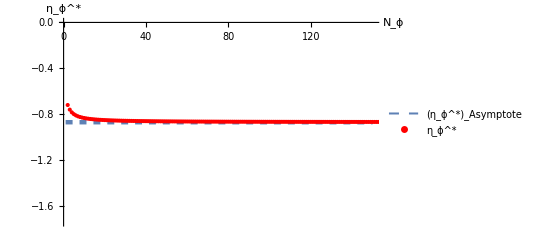

```mathematica
Show[Plot[{y=-0.86916969966179},{y,1,150},PlotStyle->{Thickness[0.008], Dashed}, PlotLegends->{"(η_ϕ^*)_Asymptote"}],ListPlot[AnomalousDimd3phi4,PlotStyle->Red,  PlotLegends->{"η_ϕ^*"}], AxesLabel-> { "N_ϕ", "η_ϕ^*"}]
```

```mathematica
Export["Phi4IncreasingNphiAnomalousDimension+Expansiond3.jpg", %, "JPEG"]
```

Phi4IncreasingNphiAnomalousDimension+Expansiond3.jpg

To find the value the anomalous dimension approaches in the large N-limit, it is fitted with a polynomial function.

```mathematica
FitAndim3phi4 =Fit[Take[AnomalousDimd3phi4, -500], {1, 1/y, 1/y^2}, y](*Fit a polynomial to the anomalous dimension value, to see what it approaches*)
```

-0.86917-0.12236/y^2+0.378729/y

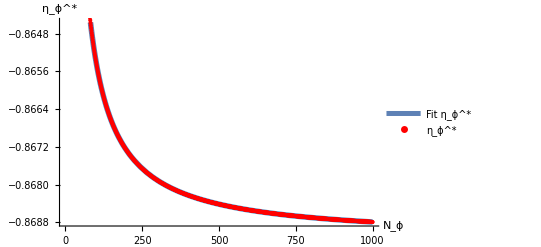

```mathematica
Show[Plot[{FitAndim3phi4},{y,1,1000},PlotStyle->{Thickness[0.01]}, PlotLegends->{"Fit η_ϕ^*"}],ListPlot[AnomalousDimd3phi4,PlotStyle->Red,  PlotLegends->{"η_ϕ^*"}], AxesLabel-> { "N_ϕ", "η_ϕ^*"}]
```

```mathematica
Export["Phi4IncreasingNphiAnomalousDimension+fitd3.jpg", %, "JPEG"]
```

Phi4IncreasingNphiAnomalousDimension+fitd3.jpg

### To the stability coefficients

Again we plot the values obtained from the expansion, with the actual data points

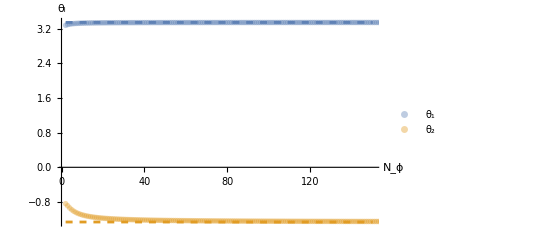

Phi4IncreasingNphiStabCoeff+Expansiond3.jpg

```mathematica
Show[Plot[{y=3.340754609368049, y= -1.2616606006764197},{y,2,150}, (*PlotLegends-> {"θ_(1,  Asymptote)", "θ_(2 Asymptote)"},*) PlotStyle->{{RGBColor[0.368417,0.506779,0.709798],Dashed}, {RGBColor[0.880722,0.611041,0.142051],Dashed}}],ListPlot[{EV3theta1, EV3theta2},PlotStyle->{{Opacity[0.4,RGBColor[0.368417,0.506779,0.709798]],PointSize[0.01]}, {Opacity[0.4,RGBColor[0.880722,0.611041,0.142051]],PointSize[0.01]}},  PlotLegends->{"θ_1", "θ_2"}], AxesLabel->{"N_ϕ","θ_i"}]
Export["Phi4IncreasingNphiStabCoeff+Expansiond3.jpg", %, "JPEG"]
```

Just as for the anomalous dimension, the fit function will be used to fit a polynomial of a+b/N_ϕ+ c/N_ϕ^2to the data of the stability coefficients to see what value this approaches in the limit.

```mathematica
FitEV1phi4d3 =Fit[Take[EV3theta1, -500], {1, 1/y,1/y^2}, y]
```

3.34075+0.0624878/y^2-0.168757/y

```mathematica
FitEV2phi4d3 =Fit[Take[EV3theta2, -500], {1, 1/y,1/y^2}, y]
```

-1.26166-2.66056/y^2+1.90136/y

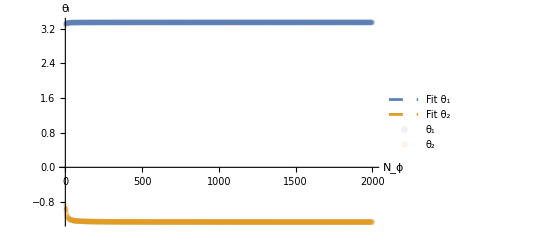

```mathematica
Show[Plot[{FitEV1phi4d3, FitEV2phi4d3 },{y,2,2001}, PlotLegends-> {"Fit θ_1", "Fit θ_2"}, PlotStyle->{{RGBColor[0.368417,0.506779,0.709798],Dashed}, {RGBColor[0.880722,0.611041,0.142051],Dashed}}],ListPlot[{EV3theta1, EV3theta2},PlotStyle->{{Opacity[0.1,RGBColor[0.368417,0.506779,0.709798]],PointSize[0.01]}, {Opacity[0.1,RGBColor[0.880722,0.611041,0.142051]],PointSize[0.01]}},  PlotLegends->{"θ_1", "θ_2"}], AxesLabel->{"N_ϕ","θ_i"}]
```

```mathematica
(*Export["Phi4IncreasingNphiStabCoeff+fitd3.jpg", %, "JPEG"]
```

Phi4IncreasingNphiStabCoeff+fitd3.jpg

# Finding Fixed Points O(ϕ^6), d=3

To properly compare the result to previous  research on O(N)-model conformal theories, it is more useful to have the results in three dimensions. 
For the order ϕ^6expansion, the average effective action is given by Γ_k= X+(Ũ)_1 k^-3 X^2+(Ũ)_2 k^-3 S_2+(Ũ)_3 k^-6 X^3+(Ũ)_4 k^-6 X S_2+(Ũ)_5 k^-6 S_3 with S_2 and S_3 the two and three X-strings (S_2=X_μ^ν X_ν^μ).  
First we import the solution for the right hand side of the Wetterich equation for 3 dimensions up to order ϕ^6 from the notebook M6 multiple scalar fields xact file generalized attempt.nb:

## Set up

```mathematica
Clear[ηϕ];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[β3];
```

```mathematica
RHScollectedd3uptoorder6ONLY=1/(10395 k^6 π^2)2 X^3 (2 (302+105 Nphi) U3[6, Nphi, 1]^3 (-11+ηϕ)+6 (204+35 Nphi) U3[6, Nphi, 1]^2 U3[6, Nphi, 2] (-11+ηϕ)+6 (99+7 Nphi) U3[6, Nphi, 1] U3[6, Nphi, 2]^2 (-11+ηϕ)+2 (28+Nphi) U3[6, Nphi, 2]^3 (-11+ηϕ)-11 U3[6, Nphi, 2](24 U3[6, Nphi, 3]+2 (13+Nphi) U3[6, Nphi, 4]+3 U3[6, Nphi, 5]) (-9+ηϕ)-11 U3[6, Nphi, 1] (84 U3[6, Nphi, 3]+2 (24+5 Nphi) U3[6, Nphi, 4]+15 U3[6, Nphi, 5]) (-9+ηϕ))+1/(10395 k^6 π^2)X (2 Subscript[S, 2] (432 U3[6, Nphi, 1]^3 (-11+ηϕ)+1968 U3[6, Nphi, 1]^2 U3[6, Nphi, 2] (-11+ηϕ)+6 (321+14 Nphi) U3[6, Nphi, 1] U3[6, Nphi, 2]^2 (-11+ηϕ)+12 (42+Nphi) U3[6, Nphi, 2]^3 (-11+ηϕ)-11 U3[6, Nphi, 2](108 U3[6, Nphi, 3]+(98+9 Nphi) U3[6, Nphi, 4]+3 (23+Nphi) U3[6, Nphi, 5]) (-9+ηϕ)-33 U3[6, Nphi, 1](16 U3[6, Nphi, 3]+(34+5 Nphi) U3[6, Nphi, 4]+(33+5 Nphi) U3[6, Nphi, 5]) (-9+ηϕ))+99 k^6 ((2+3 Nphi) U3[6, Nphi, 1]+(4+Nphi) U3[6, Nphi, 2]) (-7+ηϕ)-330 ((2+3 Nphi) U3[6, Nphi, 1]+(4+Nphi) U3[6, Nphi, 2]) U3[6, Nphi, 3] (-9+ηϕ) X^2)+1/(1890 k^3 π^2)X^2  (-12 (8+5 Nphi) U3[6, Nphi, 1]^2 (-9+ηϕ)-8 (24+5 Nphi) U3[6, Nphi, 1] U3[6, Nphi, 2](-9+ηϕ)-4 (13+Nphi) U3[6, Nphi, 2]^2 (-9+ηϕ)+9 (12 U3[6, Nphi, 3]+2 (4+Nphi) U3[6, Nphi, 4]+3 U3[6, Nphi, 5]) (-7+ηϕ))-1/(20790 k^6 π^2)(-8  Subscript[S, 3] (U3[6, Nphi, 1] (738 U3[6, Nphi, 2]^2 (-11+ηϕ)-11 (16 U3[6, Nphi, 4]+39 U3[6, Nphi, 5]) (-9+ηϕ))+64 U3[6, Nphi, 1]^3 (-11+ηϕ)+360 U3[6, Nphi, 1]^2 U3[6, Nphi, 2](-11+ηϕ)+8 (49+Nphi) U3[6, Nphi, 2]^3 (-11+ηϕ)-33U3[6, Nphi, 2] (12 U3[6, Nphi, 4]+(21+Nphi) U3[6, Nphi, 5]) (-9+ηϕ))+11 k^3 Subscript[S, 2] (32 U3[6, Nphi, 1]^2 (-9+ηϕ)+144 U3[6, Nphi, 1] U3[6, Nphi, 2] (-9+ηϕ)+4 (31+2 Nphi) U3[6, Nphi, 2]^2 (-9+ηϕ)-9 ((8+3 Nphi) U3[6, Nphi, 4]+3 (5+Nphi) U3[6, Nphi, 5]) (-7+ηϕ))+693 k^9 Nphi (-5+ηϕ)-33 U3[6, Nphi, 3] (27 k^3 Nphi (-7+ηϕ)) X^2);
```

Next we define the Left Hand Side of the Wetterich equation as well. This is given by ∂_t Γ_k:

```mathematica
LHScollectedd3order6ONLY=-ηϕ X +(-2U3[6, Nphi, 1] ηϕ -3U3[6, Nphi, 1]+β3[6, Nphi, 1])X^2/k^3+(-2U3[6, Nphi, 2] ηϕ -3U3[6, Nphi, 2]+β3[6, Nphi, 2])S2/k^3+(-3U3[6, Nphi, 3] ηϕ -6U3[6, Nphi, 3]+β3[6, Nphi, 3])X^3/k^6+(-3U3[6, Nphi, 4] ηϕ -6U3[6, Nphi, 4]+β3[6, Nphi, 4])(X S2)/k^6+(-3U3[6, Nphi, 5] ηϕ -6U3[6, Nphi, 5]+β3[6, Nphi, 5])S3/k^6;(*LHS of Wetterich equation for d=3 up to order phi^6*)
(*The -6 are what gets the 3 EV in the FP studied, when I kept this at -8 accidentaly I got -4*)
```

```mathematica
Simplify[Solve[Coefficient[Coefficient[LHScollectedd3order6ONLY, X],S2, 0]== Coefficient[Coefficient[RHScollectedd3uptoorder6ONLY, X],S2, 0], ηϕ]]
```

{{ηϕ→(7 ((2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))/(105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])}}

This as expected is the same as in the order ϕ^4 expansion so this is good!

## Finding Fixed points and beta functions

```mathematica
ηϕ=(7 ((2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))/(105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])
```

(7 ((2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))/(105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])

## Generalized solution

### Fixed points

To find the fixed points, we should first set the beta functions to zero.

```mathematica
β3[6, Nphi, 1]=0;(*Set all appearing beta functions to zero *)
β3[6, Nphi, 2]=0;
β3[6, Nphi, 3]=0;
β3[6, Nphi, 4]=0;
β3[6, Nphi, 5]=0;
```

#### Solve in 2 steps

```mathematica
U345solved3phi6=Simplify[Solve[Coefficient[k^6 LHScollectedd3order6ONLY, X, 3]== Coefficient[k^6 RHScollectedd3uptoorder6ONLY, X,3]&&Coefficient[k^6 LHScollectedd3order6ONLY, S3]==Coefficient[k^6 RHScollectedd3uptoorder6ONLY, S3]&&Simplify[k^6 Coefficient[Coefficient[LHScollectedd3order6ONLY, S2],X]]== Simplify[k^6 Coefficient[Coefficient[RHScollectedd3uptoorder6ONLY, S2],X]], {U3[6, Nphi, 3], U3[6, Nphi, 4],U3[6, Nphi, 5]}]];
```

As in the four dimensional case, the next step is very computationally intensive, and therefore will be solved numerically after the number of fields is determined

### Beta functions

```mathematica
Clear[β3] (*Since for the fixed point evaluation beta was set to zero, it must be cleared so the equation governing its evolution can be found*)
```

```mathematica
Simplify[Solve[Coefficient[k^6 LHScollectedd3order6ONLY, S3]==Coefficient[k^6 RHScollectedd3uptoorder6ONLY, S3], β3[6, Nphi, 5]]]
```

{{β3[6,Nphi,5]→(-1024 (2+3 Nphi) U3[6,Nphi,1]^4-36960 (49+Nphi) π^2 U3[6,Nphi,2]^3-128 (196+53 Nphi+Nphi^2) U3[6,Nphi,2]^4-128 U3[6,Nphi,1]^3 (2310 π^2+(122+143 Nphi) U3[6,Nphi,2])+6548850 π^4 U3[6,Nphi,5]+264 (4+Nphi) U3[6,Nphi,2]^2 (12 U3[6,Nphi,4]+(21+Nphi) U3[6,Nphi,5])+31185 π^2 U3[6,Nphi,2] (48 U3[6,Nphi,4]+(120+13 Nphi) U3[6,Nphi,5])-8 U3[6,Nphi,1]^2 (207900 π^2 U3[6,Nphi,2]+36 (162+143 Nphi) U3[6,Nphi,2]^2-11 (2+3 Nphi) (16 U3[6,Nphi,4]+39 U3[6,Nphi,5]))+U3[6,Nphi,1] (-3409560 π^2 U3[6,Nphi,2]^2-32 (1868+965 Nphi+12 Nphi^2) U3[6,Nphi,2]^3+10395 π^2 (64 U3[6,Nphi,4]+3 (70+27 Nphi) U3[6,Nphi,5])+88 U3[6,Nphi,2] (4 (34+31 Nphi) U3[6,Nphi,4]+3 (94+78 Nphi+3 Nphi^2) U3[6,Nphi,5])))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))}}

```mathematica
β3[U_[6, Nphi, 1], U_[6, Nphi, 2], U_[6, Nphi, 3], U_[6, Nphi, 4], U_[6, Nphi, 5]][6,Nphi,5]=(-1024 (2+3 Nphi) U3[6,Nphi,1]^4-36960 (49+Nphi) π^2 U3[6,Nphi,2]^3-128 (196+53 Nphi+Nphi^2) U3[6,Nphi,2]^4-128 U3[6,Nphi,1]^3 (2310 π^2+(122+143 Nphi) U3[6,Nphi,2])+6548850 π^4 U3[6,Nphi,5]+264 (4+Nphi) U3[6,Nphi,2]^2 (12 U3[6,Nphi,4]+(21+Nphi) U3[6,Nphi,5])+31185 π^2 U3[6,Nphi,2] (48 U3[6,Nphi,4]+(120+13 Nphi) U3[6,Nphi,5])-8 U3[6,Nphi,1]^2 (207900 π^2 U3[6,Nphi,2]+36 (162+143 Nphi) U3[6,Nphi,2]^2-11 (2+3 Nphi) (16 U3[6,Nphi,4]+39 U3[6,Nphi,5]))+U3[6,Nphi,1] (-3409560 π^2 U3[6,Nphi,2]^2-32 (1868+965 Nphi+12 Nphi^2) U3[6,Nphi,2]^3+10395 π^2 (64 U3[6,Nphi,4]+3 (70+27 Nphi) U3[6,Nphi,5])+88 U3[6,Nphi,2] (4 (34+31 Nphi) U3[6,Nphi,4]+3 (94+78 Nphi+3 Nphi^2) U3[6,Nphi,5])))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]));
```

```mathematica
Simplify[Solve[Simplify[k^6 Coefficient[Coefficient[LHScollectedd3order6ONLY, S2],X]]== Simplify[k^6 Coefficient[Coefficient[RHScollectedd3uptoorder6ONLY, S2],X]], β3[6, Nphi, 4]]]
```

{{β3[6,Nphi,4]→(-3456 (2+3 Nphi) U3[6,Nphi,1]^4-27720 (42+Nphi) π^2 U3[6,Nphi,2]^3-96 (168+46 Nphi+Nphi^2) U3[6,Nphi,2]^4-96 U3[6,Nphi,1]^3 (10395 π^2+8 (59+66 Nphi) U3[6,Nphi,2])+6548850 π^4 U3[6,Nphi,4]+44 (4+Nphi) U3[6,Nphi,2]^2 (108 U3[6,Nphi,3]+(98+9 Nphi) U3[6,Nphi,4]+3 (23+Nphi) U3[6,Nphi,5])+10395 π^2 U3[6,Nphi,2] (216 U3[6,Nphi,3]+(304+45 Nphi) U3[6,Nphi,4]+6 (23+Nphi) U3[6,Nphi,5])-12 U3[6,Nphi,1]^2 (378840 π^2 U3[6,Nphi,2]+4 (1954+1319 Nphi+42 Nphi^2) U3[6,Nphi,2]^2-11 (2+3 Nphi) (16 U3[6,Nphi,3]+(34+5 Nphi) U3[6,Nphi,4]+(33+5 Nphi) U3[6,Nphi,5]))+U3[6,Nphi,1] (-13860 (321+14 Nphi) π^2 U3[6,Nphi,2]^2-48 (1452+633 Nphi+20 Nphi^2) U3[6,Nphi,2]^3+31185 π^2 (32 U3[6,Nphi,3]+(86+37 Nphi) U3[6,Nphi,4]+2 (33+5 Nphi) U3[6,Nphi,5])+88 U3[6,Nphi,2] (6 (34+31 Nphi) U3[6,Nphi,3]+(302+237 Nphi+21 Nphi^2) U3[6,Nphi,4]+3 (89+62 Nphi+4 Nphi^2) U3[6,Nphi,5])))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))}}

```mathematica
β3[U_[6, Nphi, 1], U_[6, Nphi, 2], U_[6, Nphi, 3], U_[6, Nphi, 4], U_[6, Nphi, 5]][6,Nphi,4]=(-3456 (2+3 Nphi) U3[6,Nphi,1]^4-27720 (42+Nphi) π^2 U3[6,Nphi,2]^3-96 (168+46 Nphi+Nphi^2) U3[6,Nphi,2]^4-96 U3[6,Nphi,1]^3 (10395 π^2+8 (59+66 Nphi) U3[6,Nphi,2])+6548850 π^4 U3[6,Nphi,4]+44 (4+Nphi) U3[6,Nphi,2]^2 (108 U3[6,Nphi,3]+(98+9 Nphi) U3[6,Nphi,4]+3 (23+Nphi) U3[6,Nphi,5])+10395 π^2 U3[6,Nphi,2] (216 U3[6,Nphi,3]+(304+45 Nphi) U3[6,Nphi,4]+6 (23+Nphi) U3[6,Nphi,5])-12 U3[6,Nphi,1]^2 (378840 π^2 U3[6,Nphi,2]+4 (1954+1319 Nphi+42 Nphi^2) U3[6,Nphi,2]^2-11 (2+3 Nphi) (16 U3[6,Nphi,3]+(34+5 Nphi) U3[6,Nphi,4]+(33+5 Nphi) U3[6,Nphi,5]))+U3[6,Nphi,1] (-13860 (321+14 Nphi) π^2 U3[6,Nphi,2]^2-48 (1452+633 Nphi+20 Nphi^2) U3[6,Nphi,2]^3+31185 π^2 (32 U3[6,Nphi,3]+(86+37 Nphi) U3[6,Nphi,4]+2 (33+5 Nphi) U3[6,Nphi,5])+88 U3[6,Nphi,2] (6 (34+31 Nphi) U3[6,Nphi,3]+(302+237 Nphi+21 Nphi^2) U3[6,Nphi,4]+3 (89+62 Nphi+4 Nphi^2) U3[6,Nphi,5])))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]));
```

```mathematica
Simplify[Solve[Coefficient[k^6 LHScollectedd3order6ONLY, X, 3]== Coefficient[k^6 RHScollectedd3uptoorder6ONLY, X,3], β3[6, Nphi, 3]]]
```

{{β3[6,Nphi,3]→(-16 (604+1116 Nphi+315 Nphi^2) U3[6,Nphi,1]^4-4620 (28+Nphi) π^2 U3[6,Nphi,2]^3-16 (112+32 Nphi+Nphi^2) U3[6,Nphi,2]^4-4 U3[6,Nphi,1]^3 (1155 (302+105 Nphi) π^2+16 (608+692 Nphi+105 Nphi^2) U3[6,Nphi,2])+6548850 π^4 U3[6,Nphi,3]+44 (4+Nphi) U3[6,Nphi,2]^2 (3 (28+5 Nphi) U3[6,Nphi,3]+2 (13+Nphi) U3[6,Nphi,4]+3 U3[6,Nphi,5])+10395 π^2 U3[6,Nphi,2] (3 (92+19 Nphi) U3[6,Nphi,3]+4 (13+Nphi) U3[6,Nphi,4]+6 U3[6,Nphi,5])-4 U3[6,Nphi,1]^2 (3465 (204+35 Nphi) π^2 U3[6,Nphi,2]+12 (1014+655 Nphi+56 Nphi^2) U3[6,Nphi,2]^2-11 (2+3 Nphi) (3 (38+15 Nphi) U3[6,Nphi,3]+2 (24+5 Nphi) U3[6,Nphi,4]+15 U3[6,Nphi,5]))+U3[6,Nphi,1] (-13860 (99+7 Nphi) π^2 U3[6,Nphi,2]^2-16 (1244+467 Nphi+24 Nphi^2) U3[6,Nphi,2]^3+10395 π^2 (3 (94+57 Nphi) U3[6,Nphi,3]+4 (24+5 Nphi) U3[6,Nphi,4]+30 U3[6,Nphi,5])+88 U3[6,Nphi,2] (3 (104+96 Nphi+15 Nphi^2) U3[6,Nphi,3]+(122+85 Nphi+8 Nphi^2) U3[6,Nphi,4]+3 (11+4 Nphi) U3[6,Nphi,5])))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))}}

```mathematica
β3[U_[6, Nphi, 1], U_[6, Nphi, 2], U_[6, Nphi, 3], U_[6, Nphi, 4], U_[6, Nphi, 5]][6,Nphi,3]=(-16 (604+1116 Nphi+315 Nphi^2) U3[6,Nphi,1]^4-4620 (28+Nphi) π^2 U3[6,Nphi,2]^3-16 (112+32 Nphi+Nphi^2) U3[6,Nphi,2]^4-4 U3[6,Nphi,1]^3 (1155 (302+105 Nphi) π^2+16 (608+692 Nphi+105 Nphi^2) U3[6,Nphi,2])+6548850 π^4 U3[6,Nphi,3]+44 (4+Nphi) U3[6,Nphi,2]^2 (3 (28+5 Nphi) U3[6,Nphi,3]+2 (13+Nphi) U3[6,Nphi,4]+3 U3[6,Nphi,5])+10395 π^2 U3[6,Nphi,2] (3 (92+19 Nphi) U3[6,Nphi,3]+4 (13+Nphi) U3[6,Nphi,4]+6 U3[6,Nphi,5])-4 U3[6,Nphi,1]^2 (3465 (204+35 Nphi) π^2 U3[6,Nphi,2]+12 (1014+655 Nphi+56 Nphi^2) U3[6,Nphi,2]^2-11 (2+3 Nphi) (3 (38+15 Nphi) U3[6,Nphi,3]+2 (24+5 Nphi) U3[6,Nphi,4]+15 U3[6,Nphi,5]))+U3[6,Nphi,1] (-13860 (99+7 Nphi) π^2 U3[6,Nphi,2]^2-
16 (1244+467 Nphi+24 Nphi^2) U3[6,Nphi,2]^3+10395 π^2 (3 (94+57 Nphi) U3[6,Nphi,3]+4 (24+5 Nphi) U3[6,Nphi,4]+30 U3[6,Nphi,5])+88 U3[6,Nphi,2] (3 (104+96 Nphi+15 Nphi^2) U3[6,Nphi,3]+(122+85 Nphi+8 Nphi^2) U3[6,Nphi,4]+3 (11+4 Nphi) U3[6,Nphi,5])))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]));
```

```mathematica
Simplify[Solve[Simplify[k^3 Coefficient[Coefficient[LHScollectedd3order6ONLY, S2],X, 0]]== Simplify[k^3 Coefficient[Coefficient[RHScollectedd3uptoorder6ONLY, S2],X,0]], β3[6, Nphi, 2]]]
```

{{β3[6,Nphi,2]→(64 (2+3 Nphi) U3[6,Nphi,1]^3+595350 π^4 U3[6,Nphi,2]+1890 (130+21 Nphi) π^2 U3[6,Nphi,2]^2+8 (124+39 Nphi+2 Nphi^2) U3[6,Nphi,2]^3+32 U3[6,Nphi,1]^2 (945 π^2+(26+29 Nphi) U3[6,Nphi,2])+2 U3[6,Nphi,1] U3[6,Nphi,2] (945 (106+51 Nphi) π^2+4 (206+133 Nphi+6 Nphi^2) U3[6,Nphi,2])-6615 π^2 ((8+3 Nphi) U3[6,Nphi,4]+3 (5+Nphi) U3[6,Nphi,5]))/(1890 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))}}

```mathematica
β3[U_[6, Nphi, 1], U_[6, Nphi, 2], U_[6, Nphi, 3], U_[6, Nphi, 4], U_[6, Nphi, 5]][6,Nphi,2]=(64 (2+3 Nphi) U3[6,Nphi,1]^3+595350 π^4 U3[6,Nphi,2]+1890 (130+21 Nphi) π^2 U3[6,Nphi,2]^2+8 (124+39 Nphi+2 Nphi^2) U3[6,Nphi,2]^3+32 U3[6,Nphi,1]^2 (945 π^2+(26+29 Nphi) U3[6,Nphi,2])+2 U3[6,Nphi,1] U3[6,Nphi,2] (945 (106+51 Nphi) π^2+4 (206+133 Nphi+6 Nphi^2) U3[6,Nphi,2])-6615 π^2 ((8+3 Nphi) U3[6,Nphi,4]+3 (5+Nphi) U3[6,Nphi,5]))/(1890 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]));
```

```mathematica
Simplify[Solve[Coefficient[k^3 LHScollectedd3order6ONLY, X, 2]==Coefficient[k^3 RHScollectedd3uptoorder6ONLY, X,2] , β3[6, Nphi, 1]]]
```

{{β3[6,Nphi,1]→(24 (16+34 Nphi+15 Nphi^2) U3[6,Nphi,1]^3+3780 (13+Nphi) π^2 U3[6,Nphi,2]^2+8 (52+17 Nphi+Nphi^2) U3[6,Nphi,2]^3+2 U3[6,Nphi,1]^2 (945 (82+81 Nphi) π^2+4 (192+248 Nphi+45 Nphi^2) U3[6,Nphi,2])+2 U3[6,Nphi,1] (297675 π^4+945 (164+37 Nphi) π^2 U3[6,Nphi,2]+(872+516 Nphi+52 Nphi^2) U3[6,Nphi,2]^2)-6615 π^2 (3 (4+3 Nphi) U3[6,Nphi,3]+2 (4+Nphi) U3[6,Nphi,4]+3 U3[6,Nphi,5]))/(1890 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))}}

```mathematica
β3[U_[6, Nphi, 1], U_[6, Nphi, 2], U_[6, Nphi, 3], U_[6, Nphi, 4], U_[6, Nphi, 5]][6,Nphi,1]=(24 (16+34 Nphi+15 Nphi^2) U3[6,Nphi,1]^3+3780 (13+Nphi) π^2 U3[6,Nphi,2]^2+8 (52+17 Nphi+Nphi^2) U3[6,Nphi,2]^3+2 U3[6,Nphi,1]^2 (945 (82+81 Nphi) π^2+4 (192+248 Nphi+45 Nphi^2) U3[6,Nphi,2])+2 U3[6,Nphi,1] (297675 π^4+945 (164+37 Nphi) π^2 U3[6,Nphi,2]+(872+516 Nphi+52 Nphi^2) U3[6,Nphi,2]^2)-6615 π^2 (3 (4+3 Nphi) U3[6,Nphi,3]+2 (4+Nphi) U3[6,Nphi,4]+3 U3[6,Nphi,5]))/(1890 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]));
```

### Stability matrix

```mathematica
matphi6d3:=Table[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6,Nphi, a], U3[6,Nphi, b]],{a,1,5},{b,1,5}](*Generates the stability matrix*)
matphi6d3//MatrixForm(*Prints the stability matrix in Matrixform*)
EVphi6d3 = Eigenvalues[%](*Determines the eigenvalues of the stability matrix*)
```

((72 (16+34 Nphi+15 Nphi^2) U3[6,Nphi,1]^2+4 U3[6,Nphi,1] (945 (82+81 Nphi) π^2+4 (192+248 Nphi+45 Nphi^2) U3[6,Nphi,2])+2 (297675 π^4+945 (164+37 Nphi) π^2 U3[6,Nphi,2]+(872+516 Nphi+52 Nphi^2) U3[6,Nphi,2]^2))/(1890 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))-((2+3 Nphi) (24 (16+34 Nphi+15 Nphi^2) U3[6,Nphi,1]^3+3780 (13+Nphi) π^2 U3[6,Nphi,2]^2+8 (52+17 Nphi+Nphi^2) U3[6,Nphi,2]^3+2 U3[6,Nphi,1]^2 (945 (82+81 Nphi) π^2+4 (192+248 Nphi+45 Nphi^2) U3[6,Nphi,2])+2 U3[6,Nphi,1] (297675 π^4+945 (164+37 Nphi) π^2 U3[6,Nphi,2]+(872+516 Nphi+52 Nphi^2) U3[6,Nphi,2]^2)-6615 π^2 (3 (4+3 Nphi) U3[6,Nphi,3]+2 (4+Nphi) U3[6,Nphi,4]+3 U3[6,Nphi,5])))/(1890 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])^2) | (8 (192+248 Nphi+45 Nphi^2) U3[6,Nphi,1]^2+7560 (13+Nphi) π^2 U3[6,Nphi,2]+24 (52+17 Nphi+Nphi^2) U3[6,Nphi,2]^2+2 U3[6,Nphi,1] (945 (164+37 Nphi) π^2+2 (872+516 Nphi+52 Nphi^2) U3[6,Nphi,2]))/(1890 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))-((4+Nphi) (24 (16+34 Nphi+15 Nphi^2) U3[6,Nphi,1]^3+3780 (13+Nphi) π^2 U3[6,Nphi,2]^2+8 (52+17 Nphi+Nphi^2) U3[6,Nphi,2]^3+2 U3[6,Nphi,1]^2 (945 (82+81 Nphi) π^2+4 (192+248 Nphi+45 Nphi^2) U3[6,Nphi,2])+2 U3[6,Nphi,1] (297675 π^4+945 (164+37 Nphi) π^2 U3[6,Nphi,2]+(872+516 Nphi+52 Nphi^2) U3[6,Nphi,2]^2)-6615 π^2 (3 (4+3 Nphi) U3[6,Nphi,3]+2 (4+Nphi) U3[6,Nphi,4]+3 U3[6,Nphi,5])))/(1890 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])^2) | -(21 (4+3 Nphi))/(2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])) | -(7 (4+Nphi))/(105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]) | -21/(2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))
(192 (2+3 Nphi) U3[6,Nphi,1]^2+64 U3[6,Nphi,1] (945 π^2+(26+29 Nphi) U3[6,Nphi,2])+2 U3[6,Nphi,2] (945 (106+51 Nphi) π^2+4 (206+133 Nphi+6 Nphi^2) U3[6,Nphi,2]))/(1890 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))-((2+3 Nphi) (64 (2+3 Nphi) U3[6,Nphi,1]^3+595350 π^4 U3[6,Nphi,2]+1890 (130+21 Nphi) π^2 U3[6,Nphi,2]^2+8 (124+39 Nphi+2 Nphi^2) U3[6,Nphi,2]^3+32 U3[6,Nphi,1]^2 (945 π^2+(26+29 Nphi) U3[6,Nphi,2])+2 U3[6,Nphi,1] U3[6,Nphi,2] (945 (106+51 Nphi) π^2+4 (206+133 Nphi+6 Nphi^2) U3[6,Nphi,2])-6615 π^2 ((8+3 Nphi) U3[6,Nphi,4]+3 (5+Nphi) U3[6,Nphi,5])))/(1890 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])^2) | (595350 π^4+32 (26+29 Nphi) U3[6,Nphi,1]^2+3780 (130+21 Nphi) π^2 U3[6,Nphi,2]+8 (206+133 Nphi+6 Nphi^2) U3[6,Nphi,1] U3[6,Nphi,2]+24 (124+39 Nphi+2 Nphi^2) U3[6,Nphi,2]^2+2 U3[6,Nphi,1] (945 (106+51 Nphi) π^2+4 (206+133 Nphi+6 Nphi^2) U3[6,Nphi,2]))/(1890 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))-((4+Nphi) (64 (2+3 Nphi) U3[6,Nphi,1]^3+595350 π^4 U3[6,Nphi,2]+1890 (130+21 Nphi) π^2 U3[6,Nphi,2]^2+8 (124+39 Nphi+2 Nphi^2) U3[6,Nphi,2]^3+32 U3[6,Nphi,1]^2 (945 π^2+(26+29 Nphi) U3[6,Nphi,2])+2 U3[6,Nphi,1] U3[6,Nphi,2] (945 (106+51 Nphi) π^2+4 (206+133 Nphi+6 Nphi^2) U3[6,Nphi,2])-6615 π^2 ((8+3 Nphi) U3[6,Nphi,4]+3 (5+Nphi) U3[6,Nphi,5])))/(1890 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])^2) | 0 | -(7 (8+3 Nphi))/(2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])) | -(21 (5+Nphi))/(2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))
(-64 (604+1116 Nphi+315 Nphi^2) U3[6,Nphi,1]^3-13860 (99+7 Nphi) π^2 U3[6,Nphi,2]^2-16 (1244+467 Nphi+24 Nphi^2) U3[6,Nphi,2]^3-12 U3[6,Nphi,1]^2 (1155 (302+105 Nphi) π^2+16 (608+692 Nphi+105 Nphi^2) U3[6,Nphi,2])+10395 π^2 (3 (94+57 Nphi) U3[6,Nphi,3]+4 (24+5 Nphi) U3[6,Nphi,4]+30 U3[6,Nphi,5])+88 U3[6,Nphi,2] (3 (104+96 Nphi+15 Nphi^2) U3[6,Nphi,3]+(122+85 Nphi+8 Nphi^2) U3[6,Nphi,4]+3 (11+4 Nphi) U3[6,Nphi,5])-8 U3[6,Nphi,1] (3465 (204+35 Nphi) π^2 U3[6,Nphi,2]+12 (1014+655 Nphi+56 Nphi^2) U3[6,Nphi,2]^2-11 (2+3 Nphi) (3 (38+15 Nphi) U3[6,Nphi,3]+2 (24+5 Nphi) U3[6,Nphi,4]+15 U3[6,Nphi,5])))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))-((2+3 Nphi) (-16 (604+1116 Nphi+315 Nphi^2) U3[6,Nphi,1]^4-4620 (28+Nphi) π^2 U3[6,Nphi,2]^3-16 (112+32 Nphi+Nphi^2) U3[6,Nphi,2]^4-4 U3[6,Nphi,1]^3 (1155 (302+105 Nphi) π^2+16 (608+692 Nphi+105 Nphi^2) U3[6,Nphi,2])+6548850 π^4 U3[6,Nphi,3]+44 (4+Nphi) U3[6,Nphi,2]^2 (3 (28+5 Nphi) U3[6,Nphi,3]+2 (13+Nphi) U3[6,Nphi,4]+3 U3[6,Nphi,5])+10395 π^2 U3[6,Nphi,2] (3 (92+19 Nphi) U3[6,Nphi,3]+4 (13+Nphi) U3[6,Nphi,4]+6 U3[6,Nphi,5])-4 U3[6,Nphi,1]^2 (3465 (204+35 Nphi) π^2 U3[6,Nphi,2]+12 (1014+655 Nphi+56 Nphi^2) U3[6,Nphi,2]^2-11 (2+3 Nphi) (3 (38+15 Nphi) U3[6,Nphi,3]+2 (24+5 Nphi) U3[6,Nphi,4]+15 U3[6,Nphi,5]))+U3[6,Nphi,1] (-13860 (99+7 Nphi) π^2 U3[6,Nphi,2]^2-16 (1244+467 Nphi+24 Nphi^2) U3[6,Nphi,2]^3+10395 π^2 (3 (94+57 Nphi) U3[6,Nphi,3]+4 (24+5 Nphi) U3[6,Nphi,4]+30 U3[6,Nphi,5])+88 U3[6,Nphi,2] (3 (104+96 Nphi+15 Nphi^2) U3[6,Nphi,3]+(122+85 Nphi+8 Nphi^2) U3[6,Nphi,4]+3 (11+4 Nphi) U3[6,Nphi,5]))))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])^2) | (-64 (608+692 Nphi+105 Nphi^2) U3[6,Nphi,1]^3-13860 (28+Nphi) π^2 U3[6,Nphi,2]^2-64 (112+32 Nphi+Nphi^2) U3[6,Nphi,2]^3-4 U3[6,Nphi,1]^2 (3465 (204+35 Nphi) π^2+24 (1014+655 Nphi+56 Nphi^2) U3[6,Nphi,2])+88 (4+Nphi) U3[6,Nphi,2] (3 (28+5 Nphi) U3[6,Nphi,3]+2 (13+Nphi) U3[6,Nphi,4]+3 U3[6,Nphi,5])+10395 π^2 (3 (92+19 Nphi) U3[6,Nphi,3]+4 (13+Nphi) U3[6,Nphi,4]+6 U3[6,Nphi,5])+U3[6,Nphi,1] (-27720 (99+7 Nphi) π^2 U3[6,Nphi,2]-48 (1244+467 Nphi+24 Nphi^2) U3[6,Nphi,2]^2+88 (3 (104+96 Nphi+15 Nphi^2) U3[6,Nphi,3]+(122+85 Nphi+8 Nphi^2) U3[6,Nphi,4]+3 (11+4 Nphi) U3[6,Nphi,5])))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))-((4+Nphi) (-16 (604+1116 Nphi+315 Nphi^2) U3[6,Nphi,1]^4-4620 (28+Nphi) π^2 U3[6,Nphi,2]^3-16 (112+32 Nphi+Nphi^2) U3[6,Nphi,2]^4-4 U3[6,Nphi,1]^3 (1155 (302+105 Nphi) π^2+16 (608+692 Nphi+105 Nphi^2) U3[6,Nphi,2])+6548850 π^4 U3[6,Nphi,3]+44 (4+Nphi) U3[6,Nphi,2]^2 (3 (28+5 Nphi) U3[6,Nphi,3]+2 (13+Nphi) U3[6,Nphi,4]+3 U3[6,Nphi,5])+10395 π^2 U3[6,Nphi,2] (3 (92+19 Nphi) U3[6,Nphi,3]+4 (13+Nphi) U3[6,Nphi,4]+6 U3[6,Nphi,5])-4 U3[6,Nphi,1]^2 (3465 (204+35 Nphi) π^2 U3[6,Nphi,2]+12 (1014+655 Nphi+56 Nphi^2) U3[6,Nphi,2]^2-11 (2+3 Nphi) (3 (38+15 Nphi) U3[6,Nphi,3]+2 (24+5 Nphi) U3[6,Nphi,4]+15 U3[6,Nphi,5]))+U3[6,Nphi,1] (-13860 (99+7 Nphi) π^2 U3[6,Nphi,2]^2-16 (1244+467 Nphi+24 Nphi^2) U3[6,Nphi,2]^3+10395 π^2 (3 (94+57 Nphi) U3[6,Nphi,3]+4 (24+5 Nphi) U3[6,Nphi,4]+30 U3[6,Nphi,5])+88 U3[6,Nphi,2] (3 (104+96 Nphi+15 Nphi^2) U3[6,Nphi,3]+(122+85 Nphi+8 Nphi^2) U3[6,Nphi,4]+3 (11+4 Nphi) U3[6,Nphi,5]))))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])^2) | (6548850 π^4+132 (2+3 Nphi) (38+15 Nphi) U3[6,Nphi,1]^2+31185 (92+19 Nphi) π^2 U3[6,Nphi,2]+132 (4+Nphi) (28+5 Nphi) U3[6,Nphi,2]^2+U3[6,Nphi,1] (31185 (94+57 Nphi) π^2+264 (104+96 Nphi+15 Nphi^2) U3[6,Nphi,2]))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])) | (88 (2+3 Nphi) (24+5 Nphi) U3[6,Nphi,1]^2+41580 (13+Nphi) π^2 U3[6,Nphi,2]+88 (4+Nphi) (13+Nphi) U3[6,Nphi,2]^2+U3[6,Nphi,1] (41580 (24+5 Nphi) π^2+88 (122+85 Nphi+8 Nphi^2) U3[6,Nphi,2]))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])) | (660 (2+3 Nphi) U3[6,Nphi,1]^2+62370 π^2 U3[6,Nphi,2]+132 (4+Nphi) U3[6,Nphi,2]^2+U3[6,Nphi,1] (311850 π^2+264 (11+4 Nphi) U3[6,Nphi,2]))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))
(-13824 (2+3 Nphi) U3[6,Nphi,1]^3-13860 (321+14 Nphi) π^2 U3[6,Nphi,2]^2-48 (1452+633 Nphi+20 Nphi^2) U3[6,Nphi,2]^3-288 U3[6,Nphi,1]^2 (10395 π^2+8 (59+66 Nphi) U3[6,Nphi,2])+31185 π^2 (32 U3[6,Nphi,3]+(86+37 Nphi) U3[6,Nphi,4]+2 (33+5 Nphi) U3[6,Nphi,5])+88 U3[6,Nphi,2] (6 (34+31 Nphi) U3[6,Nphi,3]+(302+237 Nphi+21 Nphi^2) U3[6,Nphi,4]+3 (89+62 Nphi+4 Nphi^2) U3[6,Nphi,5])-24 U3[6,Nphi,1] (378840 π^2 U3[6,Nphi,2]+4 (1954+1319 Nphi+42 Nphi^2) U3[6,Nphi,2]^2-11 (2+3 Nphi) (16 U3[6,Nphi,3]+(34+5 Nphi) U3[6,Nphi,4]+(33+5 Nphi) U3[6,Nphi,5])))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))-((2+3 Nphi) (-3456 (2+3 Nphi) U3[6,Nphi,1]^4-27720 (42+Nphi) π^2 U3[6,Nphi,2]^3-96 (168+46 Nphi+Nphi^2) U3[6,Nphi,2]^4-96 U3[6,Nphi,1]^3 (10395 π^2+8 (59+66 Nphi) U3[6,Nphi,2])+6548850 π^4 U3[6,Nphi,4]+44 (4+Nphi) U3[6,Nphi,2]^2 (108 U3[6,Nphi,3]+(98+9 Nphi) U3[6,Nphi,4]+3 (23+Nphi) U3[6,Nphi,5])+10395 π^2 U3[6,Nphi,2] (216 U3[6,Nphi,3]+(304+45 Nphi) U3[6,Nphi,4]+6 (23+Nphi) U3[6,Nphi,5])-12 U3[6,Nphi,1]^2 (378840 π^2 U3[6,Nphi,2]+4 (1954+1319 Nphi+42 Nphi^2) U3[6,Nphi,2]^2-11 (2+3 Nphi) (16 U3[6,Nphi,3]+(34+5 Nphi) U3[6,Nphi,4]+(33+5 Nphi) U3[6,Nphi,5]))+U3[6,Nphi,1] (-13860 (321+14 Nphi) π^2 U3[6,Nphi,2]^2-48 (1452+633 Nphi+20 Nphi^2) U3[6,Nphi,2]^3+31185 π^2 (32 U3[6,Nphi,3]+(86+37 Nphi) U3[6,Nphi,4]+2 (33+5 Nphi) U3[6,Nphi,5])+88 U3[6,Nphi,2] (6 (34+31 Nphi) U3[6,Nphi,3]+(302+237 Nphi+21 Nphi^2) U3[6,Nphi,4]+3 (89+62 Nphi+4 Nphi^2) U3[6,Nphi,5]))))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])^2) | (-768 (59+66 Nphi) U3[6,Nphi,1]^3-83160 (42+Nphi) π^2 U3[6,Nphi,2]^2-384 (168+46 Nphi+Nphi^2) U3[6,Nphi,2]^3-12 U3[6,Nphi,1]^2 (378840 π^2+8 (1954+1319 Nphi+42 Nphi^2) U3[6,Nphi,2])+88 (4+Nphi) U3[6,Nphi,2] (108 U3[6,Nphi,3]+(98+9 Nphi) U3[6,Nphi,4]+3 (23+Nphi) U3[6,Nphi,5])+10395 π^2 (216 U3[6,Nphi,3]+(304+45 Nphi) U3[6,Nphi,4]+6 (23+Nphi) U3[6,Nphi,5])+U3[6,Nphi,1] (-27720 (321+14 Nphi) π^2 U3[6,Nphi,2]-144 (1452+633 Nphi+20 Nphi^2) U3[6,Nphi,2]^2+88 (6 (34+31 Nphi) U3[6,Nphi,3]+(302+237 Nphi+21 Nphi^2) U3[6,Nphi,4]+3 (89+62 Nphi+4 Nphi^2) U3[6,Nphi,5])))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))-((4+Nphi) (-3456 (2+3 Nphi) U3[6,Nphi,1]^4-27720 (42+Nphi) π^2 U3[6,Nphi,2]^3-96 (168+46 Nphi+Nphi^2) U3[6,Nphi,2]^4-96 U3[6,Nphi,1]^3 (10395 π^2+8 (59+66 Nphi) U3[6,Nphi,2])+6548850 π^4 U3[6,Nphi,4]+44 (4+Nphi) U3[6,Nphi,2]^2 (108 U3[6,Nphi,3]+(98+9 Nphi) U3[6,Nphi,4]+3 (23+Nphi) U3[6,Nphi,5])+10395 π^2 U3[6,Nphi,2] (216 U3[6,Nphi,3]+(304+45 Nphi) U3[6,Nphi,4]+6 (23+Nphi) U3[6,Nphi,5])-12 U3[6,Nphi,1]^2 (378840 π^2 U3[6,Nphi,2]+4 (1954+1319 Nphi+42 Nphi^2) U3[6,Nphi,2]^2-11 (2+3 Nphi) (16 U3[6,Nphi,3]+(34+5 Nphi) U3[6,Nphi,4]+(33+5 Nphi) U3[6,Nphi,5]))+U3[6,Nphi,1] (-13860 (321+14 Nphi) π^2 U3[6,Nphi,2]^2-48 (1452+633 Nphi+20 Nphi^2) U3[6,Nphi,2]^3+31185 π^2 (32 U3[6,Nphi,3]+(86+37 Nphi) U3[6,Nphi,4]+2 (33+5 Nphi) U3[6,Nphi,5])+88 U3[6,Nphi,2] (6 (34+31 Nphi) U3[6,Nphi,3]+(302+237 Nphi+21 Nphi^2) U3[6,Nphi,4]+3 (89+62 Nphi+4 Nphi^2) U3[6,Nphi,5]))))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])^2) | (2112 (2+3 Nphi) U3[6,Nphi,1]^2+2245320 π^2 U3[6,Nphi,2]+4752 (4+Nphi) U3[6,Nphi,2]^2+U3[6,Nphi,1] (997920 π^2+528 (34+31 Nphi) U3[6,Nphi,2]))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])) | (6548850 π^4+132 (2+3 Nphi) (34+5 Nphi) U3[6,Nphi,1]^2+10395 (304+45 Nphi) π^2 U3[6,Nphi,2]+44 (4+Nphi) (98+9 Nphi) U3[6,Nphi,2]^2+U3[6,Nphi,1] (31185 (86+37 Nphi) π^2+88 (302+237 Nphi+21 Nphi^2) U3[6,Nphi,2]))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])) | (132 (2+3 Nphi) (33+5 Nphi) U3[6,Nphi,1]^2+62370 (23+Nphi) π^2 U3[6,Nphi,2]+132 (4+Nphi) (23+Nphi) U3[6,Nphi,2]^2+U3[6,Nphi,1] (62370 (33+5 Nphi) π^2+264 (89+62 Nphi+4 Nphi^2) U3[6,Nphi,2]))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))
(-4096 (2+3 Nphi) U3[6,Nphi,1]^3-3409560 π^2 U3[6,Nphi,2]^2-32 (1868+965 Nphi+12 Nphi^2) U3[6,Nphi,2]^3-384 U3[6,Nphi,1]^2 (2310 π^2+(122+143 Nphi) U3[6,Nphi,2])+10395 π^2 (64 U3[6,Nphi,4]+3 (70+27 Nphi) U3[6,Nphi,5])+88 U3[6,Nphi,2] (4 (34+31 Nphi) U3[6,Nphi,4]+3 (94+78 Nphi+3 Nphi^2) U3[6,Nphi,5])-16 U3[6,Nphi,1] (207900 π^2 U3[6,Nphi,2]+36 (162+143 Nphi) U3[6,Nphi,2]^2-11 (2+3 Nphi) (16 U3[6,Nphi,4]+39 U3[6,Nphi,5])))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))-((2+3 Nphi) (-1024 (2+3 Nphi) U3[6,Nphi,1]^4-36960 (49+Nphi) π^2 U3[6,Nphi,2]^3-128 (196+53 Nphi+Nphi^2) U3[6,Nphi,2]^4-128 U3[6,Nphi,1]^3 (2310 π^2+(122+143 Nphi) U3[6,Nphi,2])+6548850 π^4 U3[6,Nphi,5]+264 (4+Nphi) U3[6,Nphi,2]^2 (12 U3[6,Nphi,4]+(21+Nphi) U3[6,Nphi,5])+31185 π^2 U3[6,Nphi,2] (48 U3[6,Nphi,4]+(120+13 Nphi) U3[6,Nphi,5])-8 U3[6,Nphi,1]^2 (207900 π^2 U3[6,Nphi,2]+36 (162+143 Nphi) U3[6,Nphi,2]^2-11 (2+3 Nphi) (16 U3[6,Nphi,4]+39 U3[6,Nphi,5]))+U3[6,Nphi,1] (-3409560 π^2 U3[6,Nphi,2]^2-32 (1868+965 Nphi+12 Nphi^2) U3[6,Nphi,2]^3+10395 π^2 (64 U3[6,Nphi,4]+3 (70+27 Nphi) U3[6,Nphi,5])+88 U3[6,Nphi,2] (4 (34+31 Nphi) U3[6,Nphi,4]+3 (94+78 Nphi+3 Nphi^2) U3[6,Nphi,5]))))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])^2) | (-128 (122+143 Nphi) U3[6,Nphi,1]^3-110880 (49+Nphi) π^2 U3[6,Nphi,2]^2-512 (196+53 Nphi+Nphi^2) U3[6,Nphi,2]^3-8 U3[6,Nphi,1]^2 (207900 π^2+72 (162+143 Nphi) U3[6,Nphi,2])+528 (4+Nphi) U3[6,Nphi,2] (12 U3[6,Nphi,4]+(21+Nphi) U3[6,Nphi,5])+31185 π^2 (48 U3[6,Nphi,4]+(120+13 Nphi) U3[6,Nphi,5])+U3[6,Nphi,1] (-6819120 π^2 U3[6,Nphi,2]-96 (1868+965 Nphi+12 Nphi^2) U3[6,Nphi,2]^2+88 (4 (34+31 Nphi) U3[6,Nphi,4]+3 (94+78 Nphi+3 Nphi^2) U3[6,Nphi,5])))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))-((4+Nphi) (-1024 (2+3 Nphi) U3[6,Nphi,1]^4-36960 (49+Nphi) π^2 U3[6,Nphi,2]^3-128 (196+53 Nphi+Nphi^2) U3[6,Nphi,2]^4-128 U3[6,Nphi,1]^3 (2310 π^2+(122+143 Nphi) U3[6,Nphi,2])+6548850 π^4 U3[6,Nphi,5]+264 (4+Nphi) U3[6,Nphi,2]^2 (12 U3[6,Nphi,4]+(21+Nphi) U3[6,Nphi,5])+31185 π^2 U3[6,Nphi,2] (48 U3[6,Nphi,4]+(120+13 Nphi) U3[6,Nphi,5])-8 U3[6,Nphi,1]^2 (207900 π^2 U3[6,Nphi,2]+36 (162+143 Nphi) U3[6,Nphi,2]^2-11 (2+3 Nphi) (16 U3[6,Nphi,4]+39 U3[6,Nphi,5]))+U3[6,Nphi,1] (-3409560 π^2 U3[6,Nphi,2]^2-32 (1868+965 Nphi+12 Nphi^2) U3[6,Nphi,2]^3+10395 π^2 (64 U3[6,Nphi,4]+3 (70+27 Nphi) U3[6,Nphi,5])+88 U3[6,Nphi,2] (4 (34+31 Nphi) U3[6,Nphi,4]+3 (94+78 Nphi+3 Nphi^2) U3[6,Nphi,5]))))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])^2) | 0 | (1408 (2+3 Nphi) U3[6,Nphi,1]^2+1496880 π^2 U3[6,Nphi,2]+3168 (4+Nphi) U3[6,Nphi,2]^2+U3[6,Nphi,1] (665280 π^2+352 (34+31 Nphi) U3[6,Nphi,2]))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])) | (6548850 π^4+3432 (2+3 Nphi) U3[6,Nphi,1]^2+31185 (120+13 Nphi) π^2 U3[6,Nphi,2]+264 (4+Nphi) (21+Nphi) U3[6,Nphi,2]^2+U3[6,Nphi,1] (31185 (70+27 Nphi) π^2+264 (94+78 Nphi+3 Nphi^2) U3[6,Nphi,2]))/(10395 π^2 (105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])))

```mathematica
N[EVphi6d3/.U3[6, Nphi,1]->0/.U3[6, Nphi,2]->0/.U3[6, Nphi,3]-> 0/.U3[6, Nphi,4]->0/.U3[6, Nphi,5]->0](*This line determines the EVs for the GFP*)
```

{3.,3.,6.,6.,6.}

## For different values of N_ϕ

```mathematica
β3[6, Nphi, 1]=0;(*Set all appearing beta functions to zero again, to find the U1 and U2 coordinate of the fixed points *)
β3[6, Nphi, 2]=0;
β3[6, Nphi, 3]=0;
β3[6, Nphi, 4]=0;
β3[6, Nphi, 5]=0;
```

Since analytical solving for the U_1 and U_2 is too complicated, this will be done numerically for every N_ϕ-value separately.

### N_ϕ=1

```mathematica
U12solved3phi6N2=FindRoot[{Coefficient[k^3 LHScollectedd3order6ONLY, X, 2]== Simplify[Coefficient[k^3 RHScollectedd3uptoorder6ONLY, X,2]/. U345solved3phi6][[1]],Coefficient[Coefficient[k^3 LHScollectedd3order6ONLY, S2, 1], X, 0]== Simplify[k^3 Coefficient[Coefficient[RHScollectedd3uptoorder6ONLY, S2],X,0]/.U345solved3phi6][[1]]}/.Nphi-> 1,{{U3[6,1,1],2/3* -10},{U3[6,1,2],-2/3*5.5}}, WorkingPrecision->100, MaxIterations->500]
```

{U3[6,1,1]→-5.460774471333122174462731372477176385245081310894097667297595786501415367530450926663696495775533841,U3[6,1,2]→-3.670589878550974310930650565427151777849385313936321294166954322710211779910938601790817307016090387}

```mathematica
U345solved3phi6/. Nphi-> 1/.U12solved3phi6N2;(*Find the Subscript[U, 3], Subscript[U, 4] and Subscript[U, 5] value, by substituting in Subscript[N, ϕ] and the values for Subscript[U, 1] and Subscript[U, 2]*)
%/.(lhs_->rhs_):>lhs->N[rhs](*Make sure the result is a numerical value*)
ηϕ/. Nphi-> 1/.%[[]]/.U12solved3phi6N2(*Find the value for the anomalous dimension*)
EVphi6d3/. Nphi-> 1/.%%[[]]/.U12solved3phi6N2
```

{{U3[6,1,3]→-59.6039,U3[6,1,4]→-84.498,U3[6,1,5]→-40.1174}}

{-0.32261366076999740742328979603733974489666824457136045578922372088982965291495139839402053800923168}

{{-3.12149,1.03568,3.79771,4.23879,4.58121}}

```mathematica
U3v2value[[1,2]] 
U3v1value[[1,2]]
```

-2.73912

-10.0144

#### N_ϕ=2

```mathematica
U3v1value[[1,2]]
```

-10.0144

```mathematica
Simplify[ηϕ]
```

(7 ((2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2]))/(105 π^2+(2+3 Nphi) U3[6,Nphi,1]+(4+Nphi) U3[6,Nphi,2])

```mathematica
Coefficient[Simplify[k^3 Coefficient[Coefficient[k^3 LHScollectedd3order6ONLY, S2, 1], X, 0]], k^2]
```

0

```mathematica
NSolve[{Coefficient[k^3 LHScollectedd3order6ONLY, X, 2]== Simplify[Coefficient[k^3 RHScollectedd3uptoorder6ONLY, X,2]/. U345solved3phi6][[1]],Coefficient[Coefficient[k^3 LHScollectedd3order6ONLY, S2, 1], X, 0]== Simplify[k^3 Coefficient[Coefficient[RHScollectedd3uptoorder6ONLY, S2],X,0]/.U345solved3phi6][[1]]}/.Nphi-> 2,{U3[6,2,1],U3[6,2,2]}, WorkingPrecision->100]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(92291 U3[6,2,1])/87992-(121001 U3[6,2,2])/175984 == 1.

{}

```mathematica
U12solved3phi6N2=FindRoot[{Coefficient[k^3 LHScollectedd3order6ONLY, X, 2]== Simplify[Coefficient[k^3 RHScollectedd3uptoorder6ONLY, X,2]/. U345solved3phi6][[1]],Coefficient[Coefficient[k^3 LHScollectedd3order6ONLY, S2, 1], X, 0]== Simplify[k^3 Coefficient[Coefficient[RHScollectedd3uptoorder6ONLY, S2],X,0]/.U345solved3phi6][[1]]}/.Nphi-> 2,{{U3[6,2,1],2/3 U3v1value[[1,2]]},{U3[6,2,2],-2/3 U3v2value[[1,2]] }}, WorkingPrecision->100, MaxIterations->500](*In the single scalar field approximation increasing the power of the expansion by one step approximately halves the value for the already known coefficients, so this is chosen as initial guess for the FindRoot.*)
```

{U3[6,2,1]→-5.217750309349621322183540532301052528535479672308817806393297045392120799503490773698018797116468655,U3[6,2,2]→-2.234693281295751239075254663913452893439951392982469288544496434842068065680416744302101110644333525}

guess -4, -1 finds the GFP; -5,-2 finds a FP with EVs -3.1, 1, 3.7, 4, 4.4 ; 
-10,-4 finds FP with -11,-4.4,-3.5,0.7,1.2
-500, -200 finds FP with -13, -3.2, 2.6, 2.2-3.1 ⅈ, 2.2+3.1 ⅈ
-100,-1000 finds -17, -6.2, -4.2, 0, 0.3 
-1000, -2000 finds FP with -44,0,20,7.1-20. ⅈ,7.1+20. ⅈ

```mathematica
U345solved3phi6/. Nphi-> 2/.U12solved3phi6N2;(*Find the Subscript[U, 3], Subscript[U, 4] and Subscript[U, 5] value, by substituting in Subscript[N, ϕ] and the values for Subscript[U, 1] and Subscript[U, 2]*)
%/.(lhs_->rhs_):>lhs->N[rhs](*Make sure the result is a numerical value*)
ηϕ/. Nphi-> 2/.%[[]]/.U12solved3phi6N2(*Find the value for the anomalous dimension*)
EVphi6d3/. Nphi-> 2/.%%[[]]/.U12solved3phi6N2(*Find the value for the eigenvalues of the stability matrix*)
```

{{U3[6,2,3]→-45.1835,U3[6,2,4]→-42.8856,U3[6,2,5]→-15.5847}}

{-0.393464678591579917175786688160307725411067962457419857869512184882367974786297946817231254886207185}

{{-3.14942,0.911751,3.65007,4.01572,4.36926}}

Here an extra check has to be made to check that all the fixed point values are real and fit with the expectations, to make sure the proper root is found in the FindRoot.

### Finding the Fixed point+beta functions generalized

Of course doing this by hand for all N_ϕ- is a bit time intensive, so it would be useful to write a loop that can fix this.

#### Performing the loop

```mathematica
FPphi6d3U1={};(*First define 10 lists, in which the 5 fixed point values and the 5 stability coefficients can be saved*)
FPphi6d3U2={};
FPphi6d3U3={};
FPphi6d3U4={};
FPphi6d3U5={};
FPphi6d3EV1={};
FPphi6d3EV2={};
FPphi6d3EV3={};
FPphi6d3EV4={};
FPphi6d3EV5={};
```

```mathematica
FPvaluesfordifferentNphi6d3[Nmin_,Nmax_, step_]:= Do[y=x-1;
Phi4val1d3 = U3v1value[[y,2]];
Phi4val2d3 = U3v2value[[y,2]](*Get the NGFP solution of the order ϕ^4-evaluation that was the  only robust candidate*);U12solved3phi6=FindRoot[{Coefficient[k^3 LHScollectedd3order6ONLY, X, 2]==  Simplify[Coefficient[k^3 RHScollectedd3uptoorder6ONLY, X,2]/. U345solved3phi6][[1]],Coefficient[Coefficient[k^3 LHScollectedd3order6ONLY, S2, 1], X, 0]== Simplify[k^3 Coefficient[Coefficient[RHScollectedd3uptoorder6ONLY, S2],X,0]/.U345solved3phi6][[1]]}//.k-> 1//.Nphi-> x,{{U3[6,x,1],2/3 Phi4val1d3 },{U3[6,x,2],2/3 Phi4val2d3}}, WorkingPrecision->100](*Use FindRoot with a guess of 2/3 the previously found fixed point value. This is closer to the actual step size :)*);
U345solved3phi6num= {U345solved3phi6/. Nphi-> x/.U12solved3phi6}/.(lhs_->rhs_):>lhs->N[rhs]; (*Make the solution numerical*)
EVSold3 = N[EVphi6d3/. Nphi-> x/.U345solved3phi6num/.U12solved3phi6][[1]];(*Substitute the FP solution into the eigenvalue equations to get a numerical solution for those as well*)
AppendTo[FPphi6d3U1, {x,U3[6, x, 1]/. U12solved3phi6}];(*Save {Subscript[N, ϕ], Subscript[U, i]} in Subscript[U, i] list*)
AppendTo[FPphi6d3U2, {x,U3[6, x, 2]/. U12solved3phi6}];
AppendTo[FPphi6d3U3,{x, U3[6, x, 3]/.U345solved3phi6num[[1]]}];
AppendTo[FPphi6d3U4,{x, U3[6, x, 4]/.U345solved3phi6num[[1]]}];
AppendTo[FPphi6d3U5,{x, U3[6, x, 5]/.U345solved3phi6num[[1]]}]; 
AppendTo[FPphi6d3EV1, {x, -N[EVSold3[[1]][[1]]]}];(*Save {Subscript[N, ϕ], Subscript[θ, 1]} in Subscript[EV, 1] list*)
AppendTo[FPphi6d3EV2, {x,-N[ EVSold3[[1]][[2]]]}];
AppendTo[FPphi6d3EV3, {x, -N[EVSold3[[1]][[3]]]}];
AppendTo[FPphi6d3EV4, {x,-N[ EVSold3[[1]][[4]]]}];
AppendTo[FPphi6d3EV5, {x,-N[ EVSold3[[1]][[5]]]}];, {x, Nmin, Nmax,step}](*Since the U3 phi4 values are determined up to 2000, this can also only be applied up to that number.*)
```

To check if the right fixed point is found, and remains the point found, some components are studied first

```mathematica
FPvaluesfordifferentNphi6d3[2,3, 1]
```

```mathematica
FPvaluesfordifferentNphi6d3[200,201, 1]
```

```mathematica
FPvaluesfordifferentNphi6d3[1999,2000, 1]
```

{{2,3.14942},{3,3.16968},{200,3.24285},{201,3.24285},{1999,3.24421},{2000,3.24421}}

```mathematica
FPvaluesfordifferentNphi6d3[2,1928, 1](*Evaluates the system for Nphi is 2 up to 1928*)
```

$Aborted

Next step is to also determine the anomalous dimension value for increasing N_ϕ

```mathematica
AnomalousDimd3phi6 = {}(*Define list to save anomalous dimension value*)
Do [eta = (7 ((2+3 Nphi) U3[6,1]+(4+Nphi) U3[6,2]))/(105 π^2+(2+3 Nphi) U3[6,1]+(4+Nphi) U3[6,2])/. U3[6,1]->  FPphi6d3U1[[x-1]][[2]]/. U3[6,2]-> FPphi6d3U2[[x-1]][[2]]/. Nphi-> x;
AnomalousDimd3phi6 = Append[AnomalousDimd3phi6, {x, eta}], {x, 2, 1928}]
```

{}

#### Save the found values.

```mathematica
DumpSave["FPphi6d3U1.mx", FPphi6d3U1];
DumpSave["FPphi6d3U2.mx", FPphi6d3U2];
DumpSave["FPphi6d3U3.mx", FPphi6d3U3];
DumpSave["FPphi6d3U4.mx", FPphi6d3U4];
DumpSave["FPphi6d3U5.mx", FPphi6d3U5];
DumpSave["FPphi6d3EV1.mx", FPphi6d3EV1];
DumpSave["FPphi6d3EV2.mx", FPphi6d3EV2];
DumpSave["FPphi6d3EV3.mx", FPphi6d3EV3];
DumpSave["FPphi6d3EV4.mx", FPphi6d3EV4];
DumpSave["FPphi6d3EV5.mx", FPphi6d3EV5];
DumpSave["Anomalous dimension d3 phi^6", AnomalousDimd3phi6];
```

```mathematica
DumpGet["FPphi6d3U1.mx"];
DumpGet["FPphi6d3U2.mx"];
DumpGet["FPphi6d3U3.mx"];
DumpGet["FPphi6d3U4.mx"];
DumpGet["FPphi6d3U5.mx"];
DumpGet["FPphi6d3EV1.mx"];
DumpGet["FPphi6d3EV2.mx"];
DumpGet["FPphi6d3EV3.mx"];
DumpGet["FPphi6d3EV4.mx"];
DumpGet["FPphi6d3EV5.mx"];
DumpGet["Anomalous dimension d3 phi^6"];
```

{}

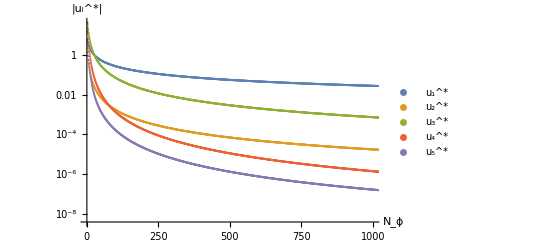

absvalueU12345phi6d3expansionlogplotLabels.jpg

absvalueU12345phi6d4expansionlogplot.jpg

```mathematica
ListLogPlot[{Partition[Flatten[FPphi6d3U1],2]*Threaded[{1,-1}], Partition[Flatten[FPphi6d3U2],2]*Threaded[{1,-1}],Partition[Flatten[FPphi6d3U3],2]*Threaded[{1,-1}],Partition[Flatten[FPphi6d3U4],2]*Threaded[{1,-1}], Partition[Flatten[FPphi6d3U5],2]*Threaded[{1,-1}]},AxesLabel->{Style["N_ϕ", FontSize->14],Style["|u_i^*|", FontSize->14]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotLegends->{Style["u_1^*", FontSize->14], Style["u_2^*", FontSize->14], Style["u_3^*", FontSize->14],Style["u_4^*", FontSize->14],Style["u_5^*", FontSize->14]}, PlotRange->{{0, 1000}, Automatic}, TicksStyle->Directive[FontSize->13]]
Export["absvalueU12345phi6d3expansionlogplotLabels.jpg",%,"JPEG"]
```

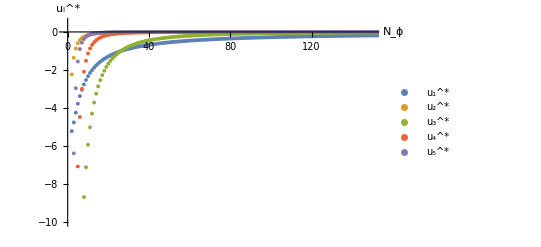

```mathematica
ListPlot[{FPphi6d3U1, FPphi6d3U2,Partition[Flatten[FPphi6d3U3],2],Partition[Flatten[FPphi6d3U4],2], Partition[Flatten[FPphi6d3U5],2]},AxesLabel->{Style["N_ϕ", FontSize->14],Style["u_i^*", FontSize->14]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotLegends->{Style["u_1^*", FontSize->14], Style["u_2^*", FontSize->14], Style["u_3^*", FontSize->14],Style["u_4^*", FontSize->14],Style["u_5^*", FontSize->14]}, PlotRange->{{-1, 150}, {-10,0.5}}, PlotStyle->{PointSize[0.007]}, TicksStyle->Directive[FontSize->13]]
```

```mathematica
Export["ValueU12345phi6d3expansionlinplotLabels.jpg",%,"JPEG"]
```

ValueU12345phi6d3expansionlinplotLabels.jpg

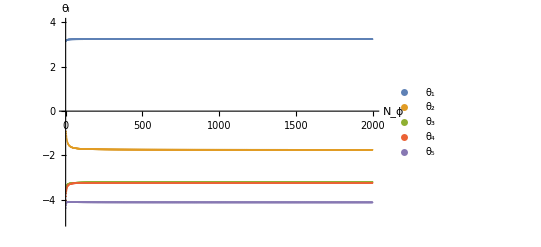

```mathematica
ListPlot[{FPphi6d3EV1, FPphi6d3EV2,Partition[Flatten[FPphi6d3EV3],2],Partition[Flatten[FPphi6d3EV4],2], Partition[Flatten[FPphi6d3EV5],2]},AxesLabel->{HoldForm["N_ϕ"],HoldForm["θ_i"]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotLegends->{"θ_1", "θ_2", "θ_3", "θ_4","θ_5"}, PlotRange->{{0, 2000}, {-5,4}}]
```

```mathematica
(*Export["StabilityCoefficientsphi6d3plot.jpg",%,"JPEG"]*)
```

StabilityCoefficientsphi6d3plot.jpg

```mathematica
ListPlot[{FPphi6d4EV1, FPphi6d4EV2,Partition[Flatten[FPphi6d4EV3],2],Partition[Flatten[FPphi6d4EV4],2], Partition[Flatten[FPphi6d4EV5],2]},AxesLabel->{HoldForm["N_ϕ"],HoldForm["θ_i"]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotLegends->{"θ_1", "θ_2", "θ_3", "θ_4","θ_5"}, PlotRange->{{0, 200}, {-6,-4}}]
```

-Graphics-

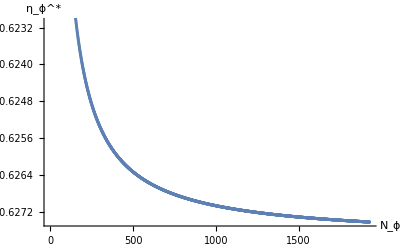

```mathematica
ListPlot[AnomalousDimd3phi6, AxesLabel->{"N_ϕ", "η_ϕ^*"}]
```

## Large N_ϕ-expansion

From the figures showing the evolution of U_i and θ_i it looks like the function asymptotes to a constant for very large N_ϕ. This means it should be possible to make a quite good large N_ϕ-expansion. The θ_i definitely should at highest order be constant in N_ϕ.

## Expanding the fixed point values

### From scratch

```mathematica
Clear[ηϕ];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[βϕ3];
U1ExpPhi6d3 = U3[6, Nphi, 1]-> U3[1,1] Nphi^-1+ U3[1,2] Nphi^-2+ U3[1,3] Nphi^-3;
U2ExpPhi6d3 = U3[6, Nphi, 2]-> U3[2,1] Nphi^-1+ U3[2,2] Nphi^-2+ U3[2,3] Nphi^-3;
U3ExpPhi6d3 = U3[6, Nphi, 3]-> U3[3,1] Nphi^-1+ U3[3,2] Nphi^-2+ U3[3,3] Nphi^-3;
U4ExpPhi6d3 = U3[6, Nphi, 4]-> U3[4,1] Nphi^-1+ U3[4,2] Nphi^-2+ U3[4,3] Nphi^-3;
U5ExpPhi6d3 = U3[6, Nphi, 5]-> U3[5,1] Nphi^-1+ U3[5,2] Nphi^-2+ U3[5,3] Nphi^-3;
```

```mathematica
RHSphi6d3Exp = Normal[Series[RHScollectedd3uptoorder6ONLY/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3, {Nphi, ∞, 1}]];
LHSphi6d3Exp = Normal[Series[LHScollectedd3order6ONLY/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3, {Nphi, ∞, 1}]];
```

```mathematica
ηϕ3Expphi6 = Normal[Series[ηϕ/. Solve[Simplify[Coefficient[Coefficient[RHSphi6d3Exp, X], S2, 0]]==Coefficient[Coefficient[LHSphi6d3Exp, X, 1],S2, 0], ηϕ], {Nphi, ∞, 1}]]
```

{(7 (3 U3[1,1]+U3[2,1]))/(105 π^2+3 U3[1,1]+U3[2,1])+(735 π^2 (2 U3[1,1]+3 U3[1,2]+4 U3[2,1]+U3[2,2]))/(Nphi (105 π^2+3 U3[1,1]+U3[2,1])^2)}

```mathematica
RHSphi6d3ExpEps = Normal[Series[RHSphi6d3Exp/.ηϕ-> ηϕ3Expphi6[[1]], {Nphi, ∞, 1}]];
LHSphi6d3ExpEps = Normal[Series[LHSphi6d3Exp/.ηϕ-> ηϕ3Expphi6[[1]], {Nphi, ∞, 1}]];
```

```mathematica
β3[6, Nphi, 1]=0;(*Set all appearing beta functions to zero *)
β3[6, Nphi, 2]=0;
β3[6, Nphi, 3]=0;
β3[6, Nphi, 4]=0;
β3[6, Nphi, 5]=0;
FPsolved3phi6ExpNphi0Of1=Simplify[Solve[Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d3ExpEps, S2],X, 0],Nphi, 0]]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d3ExpEps, S2],X, 0], Nphi,0]]&&
Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d3ExpEps, S2, 0],X, 2], Nphi, 0]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d3ExpEps, S2,0],X,2], Nphi, 0]]]&&Coefficient[Simplify[Coefficient[k^8 LHSphi6d3ExpEps, X, 3]], Nphi,-1]== Coefficient[Simplify[Coefficient[k^8 RHSphi6d3ExpEps, X,3]], Nphi, -1]&&Coefficient[Simplify[Coefficient[k^8 LHSphi6d3ExpEps, S3]], Nphi, -1]==Coefficient[Simplify[Coefficient[k^8 RHSphi6d3ExpEps, S3]], Nphi, -1]&&Simplify[Coefficient[k^8 Coefficient[Coefficient[LHSphi6d3ExpEps, S2],X], Nphi, -1]]== Simplify[Coefficient[k^8 Coefficient[Coefficient[RHSphi6d3ExpEps, S2],X], Nphi, -1]], {U3[1,1], U3[2,1],U3[3,1],U3[4,1],U3[5,1]}]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{U3[2,1]→-(945 π^2 (70 π^2+9 U3[1,1]))/(1260 π^2+8 U3[1,1]),U3[3,1]→-2/9 U3[4,1],U3[5,1]→-U3[4,1]},{U3[3,1]→0,U3[4,1]→0,U3[5,1]→0}}

### With the vanishing coefficient set to zero from the beginning

#### u_(3,1)= u_(4,1)= u_(5,1)= 0

```mathematica
Clear[ηϕ];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[βϕ3];
U1ExpPhi6d3 = U3[6, Nphi, 1]-> U3[1,1] Nphi^-1+ U3[1,2] Nphi^-2+ U3[1,3] Nphi^-3;
U2ExpPhi6d3 = U3[6, Nphi, 2]-> U3[2,1] Nphi^-1+U3[2,2] Nphi^-2+ U3[2,3] Nphi^-3;
U3ExpPhi6d3 = U3[6, Nphi, 3]-> U3[3,2] Nphi^-2+ U3[3,3] Nphi^-3;
U4ExpPhi6d3 = U3[6, Nphi, 4]-> U3[4,2] Nphi^-2+ U3[4,3] Nphi^-3;
U5ExpPhi6d3 = U3[6, Nphi, 5]-> U3[5,2] Nphi^-2+ U3[5,3] Nphi^-3;
RHSphi6d3Exp = Normal[Series[RHScollectedd3uptoorder6ONLY/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3, {Nphi, ∞, 3}]];
LHSphi6d3Exp = Normal[Series[LHScollectedd3order6ONLY/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3, {Nphi, ∞, 3}]];
ηϕ3Expphi6 = Normal[Series[ηϕ/. Solve[Simplify[Coefficient[Coefficient[RHSphi6d3Exp, X], S2, 0]]==Coefficient[Coefficient[LHSphi6d3Exp, X, 1],S2, 0], ηϕ], {Nphi, ∞, 2}]];
RHSphi6d3ExpEps = Normal[Series[RHSphi6d3Exp/.ηϕ-> ηϕ3Exp[[1]], {Nphi, ∞, 2}]];
LHSphi6d3ExpEps = Normal[Series[LHSphi6d3Exp/.ηϕ-> ηϕ3Exp[[1]], {Nphi, ∞, 2}]];
RHSphi6d3ExpEps = Normal[Series[RHSphi6d3Exp/.ηϕ-> ηϕ3Exp[[1]], {Nphi, ∞, 2}]];
```

```mathematica
β3[6, Nphi, 1]=0;(*Set all appearing beta functions to zero *)
β3[6, Nphi, 2]=0;
β3[6, Nphi, 3]=0;
β3[6, Nphi, 4]=0;
β3[6, Nphi, 5]=0;
FPsolved3phi6ExpNphi0Of1=Simplify[Solve[Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d3ExpEps, S2],X, 0],Nphi, -1]]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d3ExpEps, S2],X, 0], Nphi,-1]]&&
Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d3ExpEps, S2, 0],X, 2], Nphi, -1]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d3ExpEps, S2,0],X,2], Nphi, -1]]]&&
Coefficient[Simplify[Coefficient[k^8 LHSphi6d3ExpEps, X, 3]], Nphi,-2]== Coefficient[Simplify[Coefficient[k^8 RHSphi6d3ExpEps, X,3]], Nphi, -2]&&Coefficient[Simplify[Coefficient[k^8 LHSphi6d3ExpEps, S3]], Nphi, -2]==Coefficient[Simplify[Coefficient[k^8 RHSphi6d3ExpEps, S3]], Nphi, -2]&&Simplify[Coefficient[k^8 Coefficient[Coefficient[LHSphi6d3ExpEps, S2],X], Nphi, -2]]== Simplify[Coefficient[k^8 Coefficient[Coefficient[RHSphi6d3ExpEps, S2],X], Nphi, -2]], {U3[1,1], U3[2,1],U3[3,2],U3[4,2],U3[5,2]}]]
```

```mathematica
FPsolved3phi6ExpNphi0Of1/.(lhs_->rhs_):>lhs->N[rhs]
```

{{U3[1,1]→0.,U3[2,1]→0.,U3[3,2]→0.,U3[4,2]→0.,U3[5,2]→0.},{U3[1,1]→-78.4964,U3[2,1]→235.489,U3[3,2]→3722.52,U3[4,2]→-16751.3,U3[5,2]→16751.3},{U3[1,1]→5130.5,U3[2,1]→-15391.5,U3[3,2]→4.95041×10^7,U3[4,2]→-2.22768×10^8,U3[5,2]→2.22768×10^8},{U3[1,1]→-106.039,U3[2,1]→318.118,U3[3,2]→30303.,U3[4,2]→-119497.,U3[5,2]→85764.},{U3[1,1]→3797.89,U3[2,1]→-11393.7,U3[3,2]→5.16454×10^7,U3[4,2]→-2.10768×10^8,U3[5,2]→1.67496×10^8},{U3[1,1]→-55.9914,U3[2,1]→0.,U3[3,2]→2427.84,U3[4,2]→0.,U3[5,2]→0.},{U3[1,1]→-28.431,U3[2,1]→0.,U3[3,2]→-741.564,U3[4,2]→0.,U3[5,2]→0.},{U3[1,1]→-2840.61-1672.88 ⅈ,U3[2,1]→0.,U3[3,2]→1.38407×10^7+2.33131×10^6 ⅈ,U3[4,2]→0.,U3[5,2]→0.},{U3[1,1]→-2840.61+1672.88 ⅈ,U3[2,1]→0.,U3[3,2]→1.38407×10^7-2.33131×10^6 ⅈ,U3[4,2]→0.,U3[5,2]→0.},{U3[1,1]→-341.101,U3[2,1]→1705.5,U3[3,2]→-41591.9,U3[4,2]→623879.,U3[5,2]→-2.0796×10^6},{U3[1,1]→-74.0627,U3[2,1]→370.313,U3[3,2]→748.091,U3[4,2]→-11221.4,U3[5,2]→37404.5},{U3[1,1]→349.894,U3[2,1]→-1749.47,U3[3,2]→-58936.8,U3[4,2]→884052.,U3[5,2]→-2.94684×10^6},{U3[1,1]→4403.63,U3[2,1]→-22018.2,U3[3,2]→6.58324×10^6,U3[4,2]→-9.87486×10^7,U3[5,2]→3.29162×10^8},{U3[1,1]→-968.075,U3[2,1]→13191.1,U3[3,2]→1.29982×10^7,U3[4,2]→-4.55879×10^7,U3[5,2]→1.24737×10^7},{U3[1,1]→-78.0908,U3[2,1]→237.96,U3[3,2]→3489.85,U3[4,2]→-16195.2,U3[5,2]→16882.2},{U3[1,1]→-55.9227,U3[2,1]→-1.20905,U3[3,2]→2463.18,U3[4,2]→-29.0374,U3[5,2]→-0.00353265},{U3[1,1]→5440.86,U3[2,1]→-19191.,U3[3,2]→1.96283×10^7,U3[4,2]→-1.68293×10^8,U3[5,2]→2.86833×10^8},{U3[1,1]→-2716.88-4115.2 ⅈ,U3[2,1]→-784.751+9975.04 ⅈ,U3[3,2]→-6.4274×10^7-6.14459×10^6 ⅈ,U3[4,2]→2.39208×10^8+2.7993×10^7 ⅈ,U3[5,2]→-1.73215×10^7-3.67998×10^7 ⅈ},{U3[1,1]→-2716.88+4115.2 ⅈ,U3[2,1]→-784.751-9975.04 ⅈ,U3[3,2]→-6.4274×10^7+6.14459×10^6 ⅈ,U3[4,2]→2.39208×10^8-2.7993×10^7 ⅈ,U3[5,2]→-1.73215×10^7+3.67998×10^7 ⅈ},{U3[1,1]→-1169.48-579.976 ⅈ,U3[2,1]→-2162.9-30050.5 ⅈ,U3[3,2]→3.17121×10^6+1.37682×10^7 ⅈ,U3[4,2]→-2.54651×10^7+9.40614×10^7 ⅈ,U3[5,2]→-1.13823×10^8+2.13783×10^8 ⅈ},{U3[1,1]→-1169.48+579.976 ⅈ,U3[2,1]→-2162.9+30050.5 ⅈ,U3[3,2]→3.17121×10^6-1.37682×10^7 ⅈ,U3[4,2]→-2.54651×10^7-9.40614×10^7 ⅈ,U3[5,2]→-1.13823×10^8-2.13783×10^8 ⅈ}}

{U3[1,1]→-28.431,U3[2,1]→0.,U3[3,2]→-741.564,U3[4,2]→0.,U3[5,2]→0.} seems to be the correct solution, when we compare with the fitted function!

#### u_(2,1)=u_(3,1)= u_(4,1)= u_(5,1)= u_(4,2)= u_(5,2)=0

```mathematica
Clear[ηϕ];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[βϕ3];
U1ExpPhi6d3 = U3[6, Nphi, 1]-> U3[1,1] Nphi^-1+ U3[1,2] Nphi^-2+ U3[1,3] Nphi^-3;
U2ExpPhi6d3 = U3[6, Nphi, 2]-> U3[2,2] Nphi^-2+ U3[2,3] Nphi^-3;
U3ExpPhi6d3 = U3[6, Nphi, 3]-> U3[3,2] Nphi^-2+ U3[3,3] Nphi^-3;
U4ExpPhi6d3 = U3[6, Nphi, 4]-> U3[4,3] Nphi^-3;
U5ExpPhi6d3 = U3[6, Nphi, 5]-> U3[5,3] Nphi^-3;
RHSphi6d3Exp = Normal[Series[RHScollectedd3uptoorder6ONLY/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3, {Nphi, ∞, 3}]];
LHSphi6d3Exp = Normal[Series[LHScollectedd3order6ONLY/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3, {Nphi, ∞, 3}]];
ηϕ3Expphi6 = Normal[Series[ηϕ/. Solve[Simplify[Coefficient[Coefficient[RHSphi6d3Exp, X], S2, 0]]==Coefficient[Coefficient[LHSphi6d3Exp, X, 1],S2, 0], ηϕ], {Nphi, ∞, 3}]]
RHSphi6d3ExpEps = Normal[Series[RHSphi6d3Exp/.ηϕ-> ηϕ3Exp[[1]], {Nphi, ∞, 3}]];
LHSphi6d3ExpEps = Normal[Series[LHSphi6d3Exp/.ηϕ-> ηϕ3Exp[[1]], {Nphi, ∞, 3}]];
RHSphi6d3ExpEps = Normal[Series[RHSphi6d3Exp/.ηϕ-> ηϕ3Exp[[1]], {Nphi, ∞, 3}]];
```

{(7 U3[1,1])/(35 π^2+U3[1,1])+(245 π^2 (2 U3[1,1]+3 U3[1,2]+U3[2,2]))/(3 Nphi (35 π^2+U3[1,1])^2)+1/(9 Nphi^2 (35 π^2+U3[1,1])^3)245 π^2 (-4 U3[1,1]^2+210 π^2 U3[1,2]-6 U3[1,1] U3[1,2]-9 U3[1,2]^2+315 π^2 U3[1,3]+9 U3[1,1] U3[1,3]+420 π^2 U3[2,2]+8 U3[1,1] U3[2,2]-6 U3[1,2] U3[2,2]-U3[2,2]^2+105 π^2 U3[2,3]+3 U3[1,1] U3[2,3])+1/(27 Nphi^3 (35 π^2+U3[1,1])^4)245 π^2 (8 U3[1,1]^3-840 π^2 U3[1,1] U3[1,2]+12 U3[1,1]^2 U3[1,2]-1260 π^2 U3[1,2]^2+18 U3[1,1] U3[1,2]^2+27 U3[1,2]^3+22050 π^4 U3[1,3]-18 U3[1,1]^2 U3[1,3]-1890 π^2 U3[1,2] U3[1,3]-54 U3[1,1] U3[1,2] U3[1,3]-1680 π^2 U3[1,1] U3[2,2]-36 U3[1,1]^2 U3[2,2]-2940 π^2 U3[1,2] U3[2,2]-48 U3[1,1] U3[1,2] U3[2,2]+27 U3[1,2]^2 U3[2,2]-630 π^2 U3[1,3] U3[2,2]-18 U3[1,1] U3[1,3] U3[2,2]-840 π^2 U3[2,2]^2-18 U3[1,1] U3[2,2]^2+9 U3[1,2] U3[2,2]^2+U3[2,2]^3+44100 π^4 U3[2,3]+2100 π^2 U3[1,1] U3[2,3]+24 U3[1,1]^2 U3[2,3]-630 π^2 U3[1,2] U3[2,3]-18 U3[1,1] U3[1,2] U3[2,3]-210 π^2 U3[2,2] U3[2,3]-6 U3[1,1] U3[2,2] U3[2,3])}

```mathematica
β3[6, Nphi, 1]=0;(*Set all appearing beta functions to zero *)
β3[6, Nphi, 2]=0;
β3[6, Nphi, 3]=0;
β3[6, Nphi, 4]=0;
β3[6, Nphi, 5]=0;
FPsolved3phi6ExpNphi0Of1=Simplify[Solve[Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d3ExpEps, S2],X, 0],Nphi, -2]]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d3ExpEps, S2],X, 0], Nphi,-2]]&&
Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d3ExpEps, S2, 0],X, 2], Nphi, -1]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d3ExpEps, S2,0],X,2], Nphi, -1]]]&&
Coefficient[Simplify[Coefficient[k^8 LHSphi6d3ExpEps, X, 3]], Nphi,-2]== Coefficient[Simplify[Coefficient[k^8 RHSphi6d3ExpEps, X,3]], Nphi, -2]&&
Coefficient[Simplify[Coefficient[k^8 LHSphi6d3ExpEps, S3]], Nphi, -3]==Coefficient[Simplify[Coefficient[k^8 RHSphi6d3ExpEps, S3]], Nphi, -3]&&Simplify[Coefficient[k^8 Coefficient[Coefficient[LHSphi6d3ExpEps, S2],X], Nphi, -3]]== Simplify[Coefficient[k^8 Coefficient[Coefficient[RHSphi6d3ExpEps, S2],X], Nphi, -3]], {U3[1,1], U3[2,2],U3[3,2],U3[4,3],U3[5,3]}]]
```

{{U3[1,1]→0,U3[2,2]→0,U3[3,2]→0,U3[4,3]→0,U3[5,3]→0},{U3[1,1]→π^2 Root-5.67Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,1]-5.673113111222364,U3[2,2]→(16 π^2 (11779343730+4162363653 Root-5.67Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,1]-5.673113111222364+21202727 (Root-5.67Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,1]-5.673113111222364)^2+36564 (Root-5.67Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,1]-5.673113111222364)^3))/325570455,U3[3,2]→(2 π^4 Root-5.67Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,1]-5.673113111222364 (6615+1701 Root-5.67Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,1]-5.673113111222364+4 (Root-5.67Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,1]-5.673113111222364)^2))/1323,U3[4,3]→(8 π^4 (74825935465050+27603602344395 Root-5.67Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,1]-5.673113111222364+478440509085 (Root-5.67Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,1]-5.673113111222364)^2+1171393988 (Root-5.67Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,1]-5.673113111222364)^3))/421185140145,U3[5,3]→(256 π^4 (595945350+238378140 Root-5.67Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,1]-5.673113111222364+7432425 (Root-5.67Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,1]-5.673113111222364)^2+69988 (Root-5.67Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,1]-5.673113111222364)^3))/4732417305},{U3[1,1]→π^2 Root-2.88Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,2]-2.880666688052182,U3[2,2]→(16 π^2 (11779343730+4162363653 Root-2.88Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,2]-2.880666688052182+21202727 (Root-2.88Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,2]-2.880666688052182)^2+36564 (Root-2.88Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,2]-2.880666688052182)^3))/325570455,U3[3,2]→(2 π^4 Root-2.88Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,2]-2.880666688052182 (6615+1701 Root-2.88Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,2]-2.880666688052182+4 (Root-2.88Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,2]-2.880666688052182)^2))/1323,U3[4,3]→(8 π^4 (74825935465050+27603602344395 Root-2.88Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,2]-2.880666688052182+478440509085 (Root-2.88Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,2]-2.880666688052182)^2+1171393988 (Root-2.88Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,2]-2.880666688052182)^3))/421185140145,U3[5,3]→(256 π^4 (595945350+238378140 Root-2.88Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,2]-2.880666688052182+7432425 (Root-2.88Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,2]-2.880666688052182)^2+69988 (Root-2.88Root[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,2]-2.880666688052182)^3))/4732417305},{U3[1,1]→π^2 Root-288.-169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,3]-287.8140191912718,U3[2,2]→(16 π^2 (11779343730+4162363653 Root-288.-169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,3]-287.8140191912718+21202727 (Root-288.-169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,3]-287.8140191912718)^2+36564 (Root-288.-169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,3]-287.8140191912718)^3))/325570455,U3[3,2]→(2 π^4 Root-288.-169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,3]-287.8140191912718 (6615+1701 Root-288.-169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,3]-287.8140191912718+4 (Root-288.-169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,3]-287.8140191912718)^2))/1323,U3[4,3]→(8 π^4 (74825935465050+27603602344395 Root-288.-169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,3]-287.8140191912718+478440509085 (Root-288.-169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,3]-287.8140191912718)^2+1171393988 (Root-288.-169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,3]-287.8140191912718)^3))/421185140145,U3[5,3]→(256 π^4 (595945350+238378140 Root-288.-169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,3]-287.8140191912718+7432425 (Root-288.-169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,3]-287.8140191912718)^2+69988 (Root-288.-169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,3]-287.8140191912718)^3))/4732417305},{U3[1,1]→π^2 Root-288.+169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,4]-287.8140191912718,U3[2,2]→(16 π^2 (11779343730+4162363653 Root-288.+169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,4]-287.8140191912718+21202727 (Root-288.+169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,4]-287.8140191912718)^2+36564 (Root-288.+169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,4]-287.8140191912718)^3))/325570455,U3[3,2]→(2 π^4 Root-288.+169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,4]-287.8140191912718 (6615+1701 Root-288.+169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,4]-287.8140191912718+4 (Root-288.+169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,4]-287.8140191912718)^2))/1323,U3[4,3]→(8 π^4 (74825935465050+27603602344395 Root-288.+169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,4]-287.8140191912718+478440509085 (Root-288.+169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,4]-287.8140191912718)^2+1171393988 (Root-288.+169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,4]-287.8140191912718)^3))/421185140145,U3[5,3]→(256 π^4 (595945350+238378140 Root-288.+169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,4]-287.8140191912718+7432425 (Root-288.+169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,4]-287.8140191912718)^2+69988 (Root-288.+169. ⅈRoot[320893650+169615215 #1+20505177 #1^2+102816 #1^3+176 #1^4&,4]-287.8140191912718)^3))/4732417305}}

```mathematica
FPsolved3phi6ExpNphi0Of1/.(lhs_->rhs_):>lhs->N[rhs]
```

{{U3[1,1]→0.,U3[2,2]→0.,U3[3,2]→0.,U3[4,3]→0.,U3[5,3]→0.},{U3[1,1]→-55.9914,U3[2,2]→-5412.28,U3[3,2]→2427.84,U3[4,3]→-123201.,U3[5,3]→-2792.61},{U3[1,1]→-28.431,U3[2,2]→-17.4455,U3[3,2]→-741.564,U3[4,3]→-1385.11,U3[5,3]→-161.977},{U3[1,1]→-2840.61-1672.88 ⅈ,U3[2,2]→-1799.62+529.843 ⅈ,U3[3,2]→1.38407×10^7+2.33131×10^6 ⅈ,U3[4,3]→3.54262×10^7-3.0263×10^6 ⅈ,U3[5,3]→2.11647×10^6-1.01301×10^7 ⅈ},{U3[1,1]→-2840.61+1672.88 ⅈ,U3[2,2]→-1799.62-529.843 ⅈ,U3[3,2]→1.38407×10^7-2.33131×10^6 ⅈ,U3[4,3]→3.54262×10^7+3.0263×10^6 ⅈ,U3[5,3]→2.11647×10^6+1.01301×10^7 ⅈ}}

Verifying with the fit, {U3[1,1]→-28.431,U3[2,2]→-17.4455,U3[3,2]→-741.564,U3[4,3]→-1385.11,U3[5,3]→-161.977} seems to be the result we look for? It doesn’t work well for the U[3,4,5] Why?

### Anomalous dimension

```mathematica
(7 U3[1,1])/(35 π^2+U3[1,1])/. U3[1,1]-> -28.431040622471322
```

-0.627805

## Expanding the stability matrix

Note that before you do this, the beta functions need to be redefined (as they were set to zero in the fixed point calculation)

```mathematica
U1ExpPhi6d3 = U3[6, Nphi, 1]-> U3[1,1] Nphi^-1+ U3[1,2] Nphi^-2+ U3[1,3] Nphi^-3;
U2ExpPhi6d3 = U3[6, Nphi, 2]-> U3[2,2] Nphi^-2+ U3[2,3] Nphi^-3;
U3ExpPhi6d3 = U3[6, Nphi, 3]-> U3[3,2] Nphi^-2+ U3[3,3] Nphi^-3;
U4ExpPhi6d3 = U3[6, Nphi, 4]-> U3[4,3] Nphi^-3;
U5ExpPhi6d3 = U3[6, Nphi, 5]-> U3[5,3] Nphi^-3;
```

```mathematica
BexpPhi6d3[1,1]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 1], U3[6, Nphi, 1]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, 0}]]
BexpPhi6d3[2,1]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 2], U3[6, Nphi, 1]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, 1}]]
BexpPhi6d3[3,1]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 3], U3[6, Nphi, 1]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, 1}]]
BexpPhi6d3[4,1]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 4], U3[6, Nphi, 1]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, 2}]]
BexpPhi6d3[5,1]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 5], U3[6, Nphi, 1]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3, {Nphi, ∞, 2}]]/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}
```

-1.52479

-1.86596/Nphi

-245.017/Nphi

-472.129/Nphi^2

-83.4312/Nphi^2

```mathematica
BexpPhi6d3[1,2]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 1], U3[6, Nphi, 2]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, 0}]]
BexpPhi6d3[2,2]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 2], U3[6, Nphi, 2]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, 0}]]
BexpPhi6d3[3,2]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 3], U[6, Nphi, 2]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3, {Nphi, ∞, 1}]]/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}
BexpPhi6d3[4,2]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 4], U3[6, Nphi, 2]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, 2}]]
BexpPhi6d3[5,2]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 5], U[6, Nphi, 2]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3, {Nphi, ∞, 2}]]/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}
```

-1.08973

1.74439

0

-609.321/Nphi^2

0

```mathematica
BexpPhi6d3[1,3]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 1], U3[6, Nphi, 3]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, -1}]]
BexpPhi6d3[2,3]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 2], U3[6, Nphi, 3]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3, {Nphi, ∞, 2}]]/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}
BexpPhi6d3[3,3]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 3], U3[6, Nphi, 3]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, 0}]]
BexpPhi6d3[4,3]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 4], U3[6, Nphi, 3]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, 1}]]
BexpPhi6d3[5,3]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 5], U3[6, Nphi, 3]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3, {Nphi, ∞, 2}]]/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}
```

-0.0331225 Nphi

0

1.47521

-2.81747/Nphi

0

```mathematica
BexpPhi6d3[1,4]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 1], U3[6, Nphi, 4]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, -1}]]
BexpPhi6d3[2,4]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 2], U3[6, Nphi, 4]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, -1}]]
BexpPhi6d3[3,4]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 3], U3[6, Nphi, 4]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, 0}]]
BexpPhi6d3[4,4]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 4], U3[6, Nphi, 4]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, 0}]]
BexpPhi6d3[5,4]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 5], U3[6, Nphi, 4]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3, {Nphi, ∞, 1}]]/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}
```

-0.00736055 Nphi

-0.0110408 Nphi

-0.586973

3.23613

-1.87831/Nphi

```mathematica
BexpPhi6d3[1,5]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 1], U3[6, Nphi, 5]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, 0}]]
BexpPhi6d3[2,5]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 2], U3[6, Nphi, 5]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, -1}]]
BexpPhi6d3[3,5]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 3], U3[6, Nphi, 5]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, 1}]]
BexpPhi6d3[4,5]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 4], U3[6, Nphi, 5]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}, {Nphi, ∞, 0}]]
BexpPhi6d3[5,5]= Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 5], U3[6, Nphi, 5]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3, {Nphi, ∞, 0}]]/.{U3[1,1]->-28.431,U3[2,2]->-17.4455,U3[3,2]->-741.564,U3[4,3]->-1385.11,U3[5,3]->-161.977}
```

-0.0110408

-0.0110408 Nphi

-0.880459/Nphi

-0.880459

4.11659

```mathematica
Normal[Series[D[β3[U3[6, Nphi, 1], U3[6, Nphi, 2], U3[6, Nphi, 3], U3[6, Nphi, 4], U3[6, Nphi, 5]][6, Nphi, 1], U3[6, Nphi, 3]]/. U1ExpPhi6d3/.U2ExpPhi6d3/. U3ExpPhi6d3/.U4ExpPhi6d3/.U5ExpPhi6d3, {Nphi, ∞, 0}]]
```

-(21 Nphi)/(2 (35 π^2+U3[1,1]))-(7 (140 π^2+2 U3[1,1]-3 U3[1,2]-U3[2,2]))/(2 (35 π^2+U3[1,1])^2)

```mathematica
MatPhi6d3Exp = Table[BexpPhi6d3[a,b],{a,1,5},{b,1,5}];
%//MatrixForm
```

(-1.52479 | -1.08973 | -0.0331225 Nphi | -0.00736055 Nphi | -0.0110408
-1.86596/Nphi | 1.74439 | 0 | -0.0110408 Nphi | -0.0110408 Nphi
-245.017/Nphi | 0 | 1.47521 | -0.586973 | -0.880459/Nphi
-472.129/Nphi^2 | -609.321/Nphi^2 | -2.81747/Nphi | 3.23613 | -0.880459
-83.4312/Nphi^2 | 0 | 0 | -1.87831/Nphi | 4.11659)

```mathematica
MatrixForm[MatPhi6d3Exp-λ IdentityMatrix[5]](*As solving for the eigenvalues directly does not work, we determine the characteristic polynomial.*)
```

(-1.52479-λ | -1.08973 | -0.0331225 Nphi | -0.00736055 Nphi | -0.0110408
-1.86596/Nphi | 1.74439-λ | 0 | -0.0110408 Nphi | -0.0110408 Nphi
-245.017/Nphi | 0 | 1.47521-λ | -0.586973 | -0.880459/Nphi
-472.129/Nphi^2 | -609.321/Nphi^2 | -2.81747/Nphi | 3.23613-λ | -0.880459
-83.4312/Nphi^2 | 0 | 0 | -1.87831/Nphi | 4.11659-λ)

```mathematica
CharPolyP6d3 =Det[MatPhi6d3Exp-λ IdentityMatrix[5]](*This is the determinant of the previously given matrix. It will generate the characteristic polynomial*)
```

1/Nphi^6 1. (-87.5887 Nphi^2-59.8684 Nphi^3-60.1346 Nphi^4+77.2134 Nphi^5-240.866 Nphi^6+23.5785 Nphi^2 λ+66.5276 Nphi^3 λ+100.436 Nphi^4 λ+145.286 Nphi^5 λ+272.174 Nphi^6 λ-14.4505 Nphi^3 λ^2-29.3847 Nphi^4 λ^2-102.264 Nphi^5 λ^2-72.3491 Nphi^6 λ^2+0.92115 Nphi^4 λ^3+15.5435 Nphi^5 λ^3-15.3319 Nphi^6 λ^3+9.04754 Nphi^6 λ^4-1. Nphi^6 λ^5)

```mathematica
Series[CharPolyP6d3, {Nphi, ∞, 0}]
```

1. (-240.866+272.174 λ-72.3491 λ^2-15.3319 λ^3+9.04754 λ^4-1. λ^5)+O[1/Nphi]^1

```mathematica
Solve[-240.86609393117973+272.17362385830256 λ-72.3490631122267 λ^2-15.331890771402705 λ^3+9.047536825945578 λ^4-1. λ^5== 0, λ]
```

{{λ→-3.24435},{λ→1.74439},{λ→3.19477},{λ→3.23613},{λ→4.11659}}

```mathematica
1/3.24435
```

0.308228

## Making figures

### To the anomalous dimension

To verify previous result, we plot the original anomalous dimension data and the value it gets in the expansion

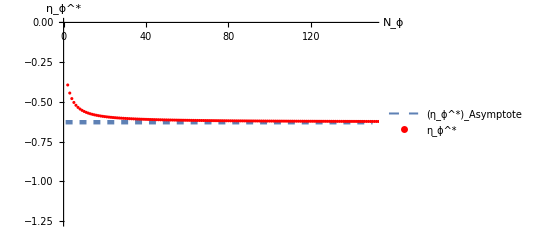

Phi6IncreasingNphiAnomalousDimension+Expansiond3.jpg

```mathematica
Show[Plot[{y=-0.6278046502560617},{y,1,150},PlotStyle->{Thickness[0.008], Dashed}, PlotLegends->{"(η_ϕ^*)_Asymptote"}],ListPlot[AnomalousDimd3phi6,PlotStyle->Red,  PlotLegends->{"η_ϕ^*"}], AxesLabel-> { "N_ϕ", "η_ϕ^*"}]
Export["Phi6IncreasingNphiAnomalousDimension+Expansiond3.jpg", %, "JPEG"]
```

To check the value the anomalous dimension approaches in the large N-limit, it is fitted with a polynomial function.

```mathematica
FitAndim3phi6 =Fit[Take[AnomalousDimd3phi6, -500], {1, 1/y, 1/y^2}, y](*Fit a polynomial to the anomalous dimension value, to see what it approaches*)
```

-0.627804650195573829493226498409644182175753855005643996492056636369364254293049157488632878538867836-0.608620090958318659107754926165445562279833085054037221658781519294684121441563356721622475282245467/y^2+0.73526892070054766402628493455179957376744138940438237522196108850754729452512750229513324971399825/y

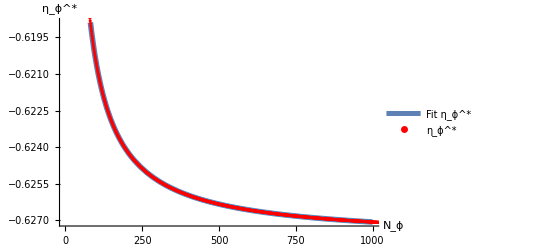

```mathematica
Show[Plot[{FitAndim3phi6},{y,1,1000},PlotStyle->{Thickness[0.01]}, PlotLegends->{"Fit η_ϕ^*"}],ListPlot[AnomalousDimd3phi6,PlotStyle->Red,  PlotLegends->{"η_ϕ^*"}], AxesLabel-> { "N_ϕ", "η_ϕ^*"}]
```

```mathematica
Export["Phi6IncreasingNphiAnomalousDimension+fitd3.jpg", %, "JPEG"]
```

Phi6IncreasingNphiAnomalousDimension+fitd3.jpg

### To the stability coefficients

We begin again with plotting both the expansion values and the data points:

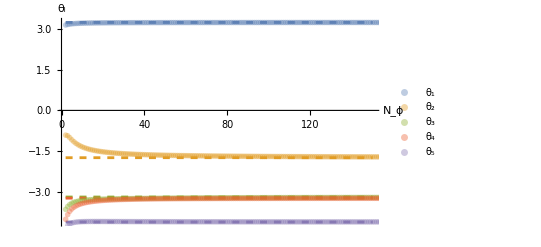

Phi6IncreasingNphiStabCoeff+Expansiond3.jpg

```mathematica
Show[Plot[{y=3.2443498193144804, y=-1.7443926544105146, y=-3.1947748749856353, y=-3.2361301342477593,y=-4.116588981615774},{y,2,150}, (*PlotLegends-> {"θ_(1,  Asymptote)", "θ_(2,  Asymptote)", "θ_(3,  Asymptote)", "θ_(4,  Asymptote)", "θ_(5,  Asymptote)"}, *)PlotStyle->{{RGBColor[0.368417,0.506779,0.709798],Dashed}, {RGBColor[0.880722,0.611041,0.142051],Dashed}, {RGBColor[0.560181,0.691569,0.194885],Dashed}, {RGBColor[0.922526,0.385626,0.209179],Dashed}, {RGBColor[0.528488,0.470624,0.701351],Dashed}}],ListPlot[{FPphi6d3EV1,FPphi6d3EV2, FPphi6d3EV3, FPphi6d3EV4, FPphi6d3EV5},PlotStyle->{{Opacity[0.4,RGBColor[0.368417,0.506779,0.709798]],PointSize[0.01]}, {Opacity[0.4,RGBColor[0.880722,0.611041,0.142051]],PointSize[0.01]}, {Opacity[0.4,RGBColor[0.560181,0.691569,0.194885]],PointSize[0.01]}, {Opacity[0.4,RGBColor[0.922526,0.385626,0.209179]],PointSize[0.01]}, {Opacity[0.4,RGBColor[0.528488,0.470624,0.701351]],PointSize[0.01]}},  PlotLegends->{"θ_1", "θ_2", "θ_3", "θ_4", "θ_5"}], AxesLabel->{"N_ϕ","θ_i"}]
Export["Phi6IncreasingNphiStabCoeff+Expansiond3.jpg", %, "JPEG"]
```

Just as for the anomalous dimension, the fit function will be used to fit a polynomial of a+b/N_ϕ+ c/N_ϕ^2to the data of the stability coefficients to double check value this approaches in the limit.

```mathematica
FitEV1phi6d3 =Fit[Take[FPphi6d3EV1, -1000], {1, 1/y,1/y^2}, y]
```

3.24436+0.268716/y^2-0.303777/y

```mathematica
FitEV2phi6d3 =Fit[Take[FPphi6d3EV2, -1000], {1, 1/y,1/y^2}, y]
```

-1.74439-5.52923/y^2+4.63628/y

```mathematica
FitEV3phi6d3 =Fit[Take[FPphi6d3EV3, -1000], {1, 1/y,1/y^2}, y]
```

-3.19477+6.88961/y^2-2.38128/y

```mathematica
FitEV4phi6d3 =Fit[Take[FPphi6d3EV4, -1000], {1, 1/y,1/y^2}, y]
```

-3.23613-6.7609/y^2-0.898382/y

```mathematica
FitEV5phi6d3 =Fit[Take[FPphi6d3EV5, -1000], {1, 1/y,1/y^2}, y]
```

-4.11659-7.83617/y^2+0.710329/y

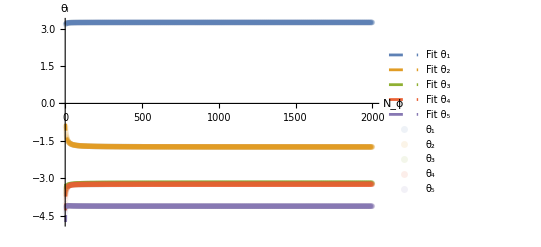

```mathematica
Show[Plot[{FitEV1phi6d3, FitEV2phi6d3, FitEV3phi6d3, FitEV4phi6d3, FitEV5phi6d3},{y,3,2001}, PlotLegends-> {"Fit θ_1", "Fit θ_2", "Fit θ_3", "Fit θ_4", "Fit θ_5"}, PlotStyle->{{RGBColor[0.368417,0.506779,0.709798],Dashed}, {RGBColor[0.880722,0.611041,0.142051],Dashed}, {RGBColor[0.560181,0.691569,0.194885],Dashed}, {RGBColor[0.922526,0.385626,0.209179],Dashed}, {RGBColor[0.528488,0.470624,0.701351],Dashed}}],ListPlot[{FPphi6d3EV1,FPphi6d3EV2, FPphi6d3EV3, FPphi6d3EV4, FPphi6d3EV5},PlotStyle->{{Opacity[0.1,RGBColor[0.368417,0.506779,0.709798]],PointSize[0.01]}, {Opacity[0.1,RGBColor[0.880722,0.611041,0.142051]],PointSize[0.01]}, {Opacity[0.1,RGBColor[0.560181,0.691569,0.194885]],PointSize[0.01]}, {Opacity[0.1,RGBColor[0.922526,0.385626,0.209179]],PointSize[0.01]}, {Opacity[0.1,RGBColor[0.528488,0.470624,0.701351]],PointSize[0.01]}},  PlotLegends->{"θ_1", "θ_2", "θ_3", "θ_4", "θ_5"}], AxesLabel->{"N_ϕ","θ_i"}]
(*Export["Phi6IncreasingNphiStabCoeff+fitd3.jpg", %, "JPEG"]*)
```

# Finding Fixed points O(ϕ^4), d=2

In the xAct file Invariant quantities for N scalar fields, we have derived the right-hand side (RHS) and left-hand side (LHS) of the Wetterich equation for spacetime dimension d=2 up to order ϕ^4.  The results are given in the two initialization cells below in the set up tab. Now we can use Mathematica without the package to work on solving the system.

## Set-up

```mathematica
Clear[βϕ2](*Clear to make sure nothing accidentaly remains*)
Clear[ηϕ2]
Clear[Nphi]
```

```mathematica
pe=4;
RHS2phi4=-(k^2 Nphi (-4+ηϕ2))/(16 π)-(X (48 U2[pe,Nphi,  1]+48 Nphi U2[pe,Nphi,  1]-12 U2[pe,Nphi,  2](-6+ηϕ2)-4 Nphi U2[pe,Nphi,  2] (-6+ηϕ2)-8 U2[pe,Nphi,  1] ηϕ2-8 Nphi U2[pe,Nphi,  1]ηϕ2))/(192 π)-1/(192 π k^2)X^2 (32 U2[pe,Nphi,  1] U2[pe,Nphi,  2](-8+ηϕ2)+8 Nphi U2[pe,Nphi,  1] U2[pe,Nphi,  2] (-8+ηϕ2)+20 (-8+ηϕ2) U2[pe,Nphi,  1]^2+(11+Nphi) (-8+ηϕ2) U2[pe,Nphi,  2]^2)+Subscript[S, 2] (-(U2[pe,Nphi,  1]U2[pe,Nphi,  2](-8+ηϕ2))/(6 k^2 π)-((-8+ηϕ2) U2[pe,Nphi,  1]^2)/(24 k^2 π)-((11+Nphi) (-8+ηϕ2) U2[pe,Nphi,  2]^2)/(96 k^2 π))-(Nphi (-8+ηϕ2) U2[pe,Nphi,  1]^2 X^2)/(24 k^2 π);(*The right-hand side of the Wetterich equation for d=2, from the xAct file!*)
```

```mathematica
LHS2finalphi4 = -X ηϕ2+X^2(-(2 ηϕ2 U2[pe,Nphi,  1])/k^2-2(U2[pe,Nphi,  1]/k^2)+βϕ2[pe,Nphi, 1]/k^2)+S2 (-(2 ηϕ2 U2[pe,Nphi,  2])/k^2-2 U2[pe,Nphi,  2]/k^2+βϕ2[pe,Nphi, 2]/k^2);(*The left-hand side of the Wetterich equation for d=2*)
```

```mathematica
Solve[Simplify[Coefficient[RHS2phi4, X]]==Coefficient[LHS2finalphi4, X], ηϕ2](*Solve for the anomalous dimension*)
```

{{ηϕ2→(6 (2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2]))/(48 π+2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2])}}

## Finding Fixed points and Beta functions

## General solution

First define the anomalous dimension

```mathematica
ηϕ2=(6 (2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2]))/(48 π+2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2]);
```

### Fixed points

The fixed points are found by equating the coefficients of the different basis elements

```mathematica
βϕ2[4, Nphi, 1]=0;(*First set beta to zero, since at the FP it has to be 0*)
βϕ2[4, Nphi, 2]=0;
```

Since the two equations remaining are strongly coupled, it is most efficient to solve them in one set of equations.

```mathematica
FP2Solgen = Solve[Simplify[Coefficient[RHS2phi4, X, 2]]==Coefficient[LHS2finalphi4, X, 2]&&Simplify[Coefficient[RHS2phi4,S2]]==Coefficient[LHS2finalphi4, S2]/. k-> 1, {U2[4,Nphi, 1], U2[4,Nphi, 2]}](*In this evaluation it is easy to see the k-terms drop out. Since this takes extra time, k is set to 1, which has the same result.*)
```

### Beta functions

After finding the fixed points, the next step is to look for the beta functions.

```mathematica
Clear[βϕ2](*Since for the fixed point evaluation beta was set to zero, it must be cleared so the equation governing its evolution can be found*)
```

```mathematica
Solve[Simplify[Coefficient[RHS2phi4, X, 2]]==Coefficient[LHS2finalphi4, X, 2]/. k-> 1, βϕ2[4,Nphi, 1]]
```

{{βϕ2[4,Nphi,1]→(9216 π^2 U2[4,Nphi,1]+6528 π U2[4,Nphi,1]^2+4224 Nphi π U2[4,Nphi,1]^2+40 U2[4,Nphi,1]^3+56 Nphi U2[4,Nphi,1]^3+16 Nphi^2 U2[4,Nphi,1]^3+10176 π U2[4,Nphi,1] U2[4,Nphi,2]+2880 Nphi π U2[4,Nphi,1] U2[4,Nphi,2]+124 U2[4,Nphi,1]^2 U2[4,Nphi,2]+124 Nphi U2[4,Nphi,1]^2 U2[4,Nphi,2]+24 Nphi^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]+2112 π U2[4,Nphi,2]^2+192 Nphi π U2[4,Nphi,2]^2+118 U2[4,Nphi,1] U2[4,Nphi,2]^2+80 Nphi U2[4,Nphi,1] U2[4,Nphi,2]^2+10 Nphi^2 U2[4,Nphi,1] U2[4,Nphi,2]^2+33 U2[4,Nphi,2]^3+14 Nphi U2[4,Nphi,2]^3+Nphi^2 U2[4,Nphi,2]^3)/(96 π (48 π+2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2]))}}

```mathematica
βϕ2[U2_[4, Nphi, 1], U2_[4, Nphi, 2]][4,Nphi, 1]=(9216 π^2 U2[4,Nphi,1]+6528 π U2[4,Nphi,1]^2+4224 Nphi π U2[4,Nphi,1]^2+40 U2[4,Nphi,1]^3+56 Nphi U2[4,Nphi,1]^3+16 Nphi^2 U2[4,Nphi,1]^3+10176 π U2[4,Nphi,1] U2[4,Nphi,2]+2880 Nphi π U2[4,Nphi,1] U2[4,Nphi,2]+124 U2[4,Nphi,1]^2 U2[4,Nphi,2]+124 Nphi U2[4,Nphi,1]^2 U2[4,Nphi,2]+24 Nphi^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]+2112 π U2[4,Nphi,2]^2+192 Nphi π U2[4,Nphi,2]^2+118 U2[4,Nphi,1] U2[4,Nphi,2]^2+80 Nphi U2[4,Nphi,1] U2[4,Nphi,2]^2+10 Nphi^2 U2[4,Nphi,1] U2[4,Nphi,2]^2+33 U2[4,Nphi,2]^3+14 Nphi U2[4,Nphi,2]^3+Nphi^2 U2[4,Nphi,2]^3)/(96 π (48 π+2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2]));(*Saves the form of Subscript[β, Subscript[U, 1]] as a function of Subscript[U, 1] and Subscript[U, 2]*)
```

```mathematica
Solve[Simplify[Coefficient[RHS2phi4, S2, 1]]==Coefficient[LHS2finalphi4, S2, 1]/. k-> 1, βϕ2[4,Nphi, 2]]
```

{{βϕ2[4,Nphi,2]→(768 π U2[4,Nphi,1]^2+8 U2[4,Nphi,1]^3+8 Nphi U2[4,Nphi,1]^3+4608 π^2 U2[4,Nphi,2]+4416 π U2[4,Nphi,1] U2[4,Nphi,2]+1344 Nphi π U2[4,Nphi,1] U2[4,Nphi,2]+44 U2[4,Nphi,1]^2 U2[4,Nphi,2]+36 Nphi U2[4,Nphi,1]^2 U2[4,Nphi,2]+4128 π U2[4,Nphi,2]^2+864 Nphi π U2[4,Nphi,2]^2+70 U2[4,Nphi,1] U2[4,Nphi,2]^2+40 Nphi U2[4,Nphi,1] U2[4,Nphi,2]^2+2 Nphi^2 U2[4,Nphi,1] U2[4,Nphi,2]^2+33 U2[4,Nphi,2]^3+14 Nphi U2[4,Nphi,2]^3+Nphi^2 U2[4,Nphi,2]^3)/(48 π (48 π+2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2]))}}

```mathematica
βϕ2[U2_[4, Nphi, 1], U2_[4, Nphi, 2]][4,Nphi, 2]=(768 π U2[4,Nphi,1]^2+8 U2[4,Nphi,1]^3+8 Nphi U2[4,Nphi,1]^3+4608 π^2 U2[4,Nphi,2]+4416 π U2[4,Nphi,1] U2[4,Nphi,2]+1344 Nphi π U2[4,Nphi,1] U2[4,Nphi,2]+44 U2[4,Nphi,1]^2 U2[4,Nphi,2]+36 Nphi U2[4,Nphi,1]^2 U2[4,Nphi,2]+4128 π U2[4,Nphi,2]^2+864 Nphi π U2[4,Nphi,2]^2+70 U2[4,Nphi,1] U2[4,Nphi,2]^2+40 Nphi U2[4,Nphi,1] U2[4,Nphi,2]^2+2 Nphi^2 U2[4,Nphi,1] U2[4,Nphi,2]^2+33 U2[4,Nphi,2]^3+14 Nphi U2[4,Nphi,2]^3+Nphi^2 U2[4,Nphi,2]^3)/(48 π (48 π+2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2]));(*Saves the form of Subscript[β, Subscript[U, 2]] as a function of Subscript[U, 1] and Subscript[U, 2]*)
```

### Stability matrix and stability coefficients

```mathematica
mat2phi4:=Table[D[βϕ2[U2[4,Nphi, 1], U2[4,Nphi, 2]][4,Nphi, a], U2[4,Nphi, b]],{a,1,2},{b,1,2}];(*Generates the stability matrix*)
mat2phi4//MatrixForm
```

((9216 π^2+13056 π U2[4,Nphi,1]+8448 Nphi π U2[4,Nphi,1]+120 U2[4,Nphi,1]^2+168 Nphi U2[4,Nphi,1]^2+48 Nphi^2 U2[4,Nphi,1]^2+10176 π U2[4,Nphi,2]+2880 Nphi π U2[4,Nphi,2]+248 U2[4,Nphi,1] U2[4,Nphi,2]+248 Nphi U2[4,Nphi,1] U2[4,Nphi,2]+48 Nphi^2 U2[4,Nphi,1] U2[4,Nphi,2]+118 U2[4,Nphi,2]^2+80 Nphi U2[4,Nphi,2]^2+10 Nphi^2 U2[4,Nphi,2]^2)/(96 π (48 π+2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2]))-((2+2 Nphi) (9216 π^2 U2[4,Nphi,1]+6528 π U2[4,Nphi,1]^2+4224 Nphi π U2[4,Nphi,1]^2+40 U2[4,Nphi,1]^3+56 Nphi U2[4,Nphi,1]^3+16 Nphi^2 U2[4,Nphi,1]^3+10176 π U2[4,Nphi,1] U2[4,Nphi,2]+2880 Nphi π U2[4,Nphi,1] U2[4,Nphi,2]+124 U2[4,Nphi,1]^2 U2[4,Nphi,2]+124 Nphi U2[4,Nphi,1]^2 U2[4,Nphi,2]+24 Nphi^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]+2112 π U2[4,Nphi,2]^2+192 Nphi π U2[4,Nphi,2]^2+118 U2[4,Nphi,1] U2[4,Nphi,2]^2+80 Nphi U2[4,Nphi,1] U2[4,Nphi,2]^2+10 Nphi^2 U2[4,Nphi,1] U2[4,Nphi,2]^2+33 U2[4,Nphi,2]^3+14 Nphi U2[4,Nphi,2]^3+Nphi^2 U2[4,Nphi,2]^3))/(96 π (48 π+2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2])^2) | (10176 π U2[4,Nphi,1]+2880 Nphi π U2[4,Nphi,1]+124 U2[4,Nphi,1]^2+124 Nphi U2[4,Nphi,1]^2+24 Nphi^2 U2[4,Nphi,1]^2+4224 π U2[4,Nphi,2]+384 Nphi π U2[4,Nphi,2]+236 U2[4,Nphi,1] U2[4,Nphi,2]+160 Nphi U2[4,Nphi,1] U2[4,Nphi,2]+20 Nphi^2 U2[4,Nphi,1] U2[4,Nphi,2]+99 U2[4,Nphi,2]^2+42 Nphi U2[4,Nphi,2]^2+3 Nphi^2 U2[4,Nphi,2]^2)/(96 π (48 π+2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2]))-((3+Nphi) (9216 π^2 U2[4,Nphi,1]+6528 π U2[4,Nphi,1]^2+4224 Nphi π U2[4,Nphi,1]^2+40 U2[4,Nphi,1]^3+56 Nphi U2[4,Nphi,1]^3+16 Nphi^2 U2[4,Nphi,1]^3+10176 π U2[4,Nphi,1] U2[4,Nphi,2]+2880 Nphi π U2[4,Nphi,1] U2[4,Nphi,2]+124 U2[4,Nphi,1]^2 U2[4,Nphi,2]+124 Nphi U2[4,Nphi,1]^2 U2[4,Nphi,2]+24 Nphi^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]+2112 π U2[4,Nphi,2]^2+192 Nphi π U2[4,Nphi,2]^2+118 U2[4,Nphi,1] U2[4,Nphi,2]^2+80 Nphi U2[4,Nphi,1] U2[4,Nphi,2]^2+10 Nphi^2 U2[4,Nphi,1] U2[4,Nphi,2]^2+33 U2[4,Nphi,2]^3+14 Nphi U2[4,Nphi,2]^3+Nphi^2 U2[4,Nphi,2]^3))/(96 π (48 π+2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2])^2)
(1536 π U2[4,Nphi,1]+24 U2[4,Nphi,1]^2+24 Nphi U2[4,Nphi,1]^2+4416 π U2[4,Nphi,2]+1344 Nphi π U2[4,Nphi,2]+88 U2[4,Nphi,1] U2[4,Nphi,2]+72 Nphi U2[4,Nphi,1] U2[4,Nphi,2]+70 U2[4,Nphi,2]^2+40 Nphi U2[4,Nphi,2]^2+2 Nphi^2 U2[4,Nphi,2]^2)/(48 π (48 π+2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2]))-((2+2 Nphi) (768 π U2[4,Nphi,1]^2+8 U2[4,Nphi,1]^3+8 Nphi U2[4,Nphi,1]^3+4608 π^2 U2[4,Nphi,2]+4416 π U2[4,Nphi,1] U2[4,Nphi,2]+1344 Nphi π U2[4,Nphi,1] U2[4,Nphi,2]+44 U2[4,Nphi,1]^2 U2[4,Nphi,2]+36 Nphi U2[4,Nphi,1]^2 U2[4,Nphi,2]+4128 π U2[4,Nphi,2]^2+864 Nphi π U2[4,Nphi,2]^2+70 U2[4,Nphi,1] U2[4,Nphi,2]^2+40 Nphi U2[4,Nphi,1] U2[4,Nphi,2]^2+2 Nphi^2 U2[4,Nphi,1] U2[4,Nphi,2]^2+33 U2[4,Nphi,2]^3+14 Nphi U2[4,Nphi,2]^3+Nphi^2 U2[4,Nphi,2]^3))/(48 π (48 π+2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2])^2) | (4608 π^2+4416 π U2[4,Nphi,1]+1344 Nphi π U2[4,Nphi,1]+44 U2[4,Nphi,1]^2+36 Nphi U2[4,Nphi,1]^2+8256 π U2[4,Nphi,2]+1728 Nphi π U2[4,Nphi,2]+140 U2[4,Nphi,1] U2[4,Nphi,2]+80 Nphi U2[4,Nphi,1] U2[4,Nphi,2]+4 Nphi^2 U2[4,Nphi,1] U2[4,Nphi,2]+99 U2[4,Nphi,2]^2+42 Nphi U2[4,Nphi,2]^2+3 Nphi^2 U2[4,Nphi,2]^2)/(48 π (48 π+2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2]))-((3+Nphi) (768 π U2[4,Nphi,1]^2+8 U2[4,Nphi,1]^3+8 Nphi U2[4,Nphi,1]^3+4608 π^2 U2[4,Nphi,2]+4416 π U2[4,Nphi,1] U2[4,Nphi,2]+1344 Nphi π U2[4,Nphi,1] U2[4,Nphi,2]+44 U2[4,Nphi,1]^2 U2[4,Nphi,2]+36 Nphi U2[4,Nphi,1]^2 U2[4,Nphi,2]+4128 π U2[4,Nphi,2]^2+864 Nphi π U2[4,Nphi,2]^2+70 U2[4,Nphi,1] U2[4,Nphi,2]^2+40 Nphi U2[4,Nphi,1] U2[4,Nphi,2]^2+2 Nphi^2 U2[4,Nphi,1] U2[4,Nphi,2]^2+33 U2[4,Nphi,2]^3+14 Nphi U2[4,Nphi,2]^3+Nphi^2 U2[4,Nphi,2]^3))/(48 π (48 π+2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2])^2))

```mathematica
EV2s=Eigenvalues[%](*Determines the eigenvalues of the stability matrix*)
```

{(442368 π^3+534528 π^2 U2[4,Nphi,1]+276480 Nphi π^2 U2[4,Nphi,1]+18048 π U2[4,Nphi,1]^2+27264 Nphi π U2[4,Nphi,1]^2+8064 Nphi^2 π U2[4,Nphi,1]^2+144 U2[4,Nphi,1]^3+320 Nphi U2[4,Nphi,1]^3+208 Nphi^2 U2[4,Nphi,1]^3+32 Nphi^3 U2[4,Nphi,1]^3+654336 π^2 U2[4,Nphi,2]+156672 Nphi π^2 U2[4,Nphi,2]+48768 π U2[4,Nphi,1] U2[4,Nphi,2]+48960 Nphi π U2[4,Nphi,1] U2[4,Nphi,2]+9024 Nphi^2 π U2[4,Nphi,1] U2[4,Nphi,2]+584 U2[4,Nphi,1]^2 U2[4,Nphi,2]+1000 Nphi U2[4,Nphi,1]^2 U2[4,Nphi,2]+472 Nphi^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]+56 Nphi^3 U2[4,Nphi,1]^2 U2[4,Nphi,2]+33120 π U2[4,Nphi,2]^2+17760 Nphi π U2[4,Nphi,2]^2+2496 Nphi^2 π U2[4,Nphi,2]^2+780 U2[4,Nphi,1] U2[4,Nphi,2]^2+968 Nphi U2[4,Nphi,1] U2[4,Nphi,2]^2+332 Nphi^2 U2[4,Nphi,1] U2[4,Nphi,2]^2+32 Nphi^3 U2[4,Nphi,1] U2[4,Nphi,2]^2+342 U2[4,Nphi,2]^3+282 Nphi U2[4,Nphi,2]^3+74 Nphi^2 U2[4,Nphi,2]^3+6 Nphi^3 U2[4,Nphi,2]^3-2 √(19110297600 π^4 U2[4,Nphi,1]^2+10701766656 Nphi π^4 U2[4,Nphi,1]^2+4161798144 Nphi^2 π^4 U2[4,Nphi,1]^2+902430720 π^3 U2[4,Nphi,1]^3+1422655488 Nphi π^3 U2[4,Nphi,1]^3+544997376 Nphi^2 π^3 U2[4,Nphi,1]^3+173408256 Nphi^3 π^3 U2[4,Nphi,1]^3+22007808 π^2 U2[4,Nphi,1]^4+58613760 Nphi π^2 U2[4,Nphi,1]^4+49655808 Nphi^2 π^2 U2[4,Nphi,1]^4+16588800 Nphi^3 π^2 U2[4,Nphi,1]^4+3870720 Nphi^4 π^2 U2[4,Nphi,1]^4+285696 π U2[4,Nphi,1]^5+1022976 Nphi π U2[4,Nphi,1]^5+1333248 Nphi^2 π U2[4,Nphi,1]^5+783360 Nphi^3 π U2[4,Nphi,1]^5+230400 Nphi^4 π U2[4,Nphi,1]^5+43008 Nphi^5 π U2[4,Nphi,1]^5+2112 U2[4,Nphi,1]^6+9216 Nphi U2[4,Nphi,1]^6+16000 Nphi^2 U2[4,Nphi,1]^6+14080 Nphi^3 U2[4,Nphi,1]^6+6720 Nphi^4 U2[4,Nphi,1]^6+1792 Nphi^5 U2[4,Nphi,1]^6+256 Nphi^6 U2[4,Nphi,1]^6+47818211328 π^4 U2[4,Nphi,1] U2[4,Nphi,2]+17156800512 Nphi π^4 U2[4,Nphi,1] U2[4,Nphi,2]+2972712960 Nphi^2 π^4 U2[4,Nphi,1] U2[4,Nphi,2]+3770744832 π^3 U2[4,Nphi,1]^2 U2[4,Nphi,2]+4177723392 Nphi π^3 U2[4,Nphi,1]^2 U2[4,Nphi,2]+1008599040 Nphi^2 π^3 U2[4,Nphi,1]^2 U2[4,Nphi,2]+173408256 Nphi^3 π^3 U2[4,Nphi,1]^2 U2[4,Nphi,2]+127623168 π^2 U2[4,Nphi,1]^3 U2[4,Nphi,2]+266637312 Nphi π^2 U2[4,Nphi,1]^3 U2[4,Nphi,2]+165666816 Nphi^2 π^2 U2[4,Nphi,1]^3 U2[4,Nphi,2]+37380096 Nphi^3 π^2 U2[4,Nphi,1]^3 U2[4,Nphi,2]+5640192 Nphi^4 π^2 U2[4,Nphi,1]^3 U2[4,Nphi,2]+2081280 π U2[4,Nphi,1]^4 U2[4,Nphi,2]+6240768 Nphi π U2[4,Nphi,1]^4 U2[4,Nphi,2]+6555648 Nphi^2 π U2[4,Nphi,1]^4 U2[4,Nphi,2]+2924544 Nphi^3 π U2[4,Nphi,1]^4 U2[4,Nphi,2]+609792 Nphi^4 π U2[4,Nphi,1]^4 U2[4,Nphi,2]+81408 Nphi^5 π U2[4,Nphi,1]^4 U2[4,Nphi,2]+17984 U2[4,Nphi,1]^5 U2[4,Nphi,2]+68928 Nphi U2[4,Nphi,1]^5 U2[4,Nphi,2]+102912 Nphi^2 U2[4,Nphi,1]^5 U2[4,Nphi,2]+75648 Nphi^3 U2[4,Nphi,1]^5 U2[4,Nphi,2]+28992 Nphi^4 U2[4,Nphi,1]^5 U2[4,Nphi,2]+5952 Nphi^5 U2[4,Nphi,1]^5 U2[4,Nphi,2]+640 Nphi^6 U2[4,Nphi,1]^5 U2[4,Nphi,2]+25331761152 π^4 U2[4,Nphi,2]^2+8111259648 Nphi π^4 U2[4,Nphi,2]^2+530841600 Nphi^2 π^4 U2[4,Nphi,2]^2+5020876800 π^3 U2[4,Nphi,1] U2[4,Nphi,2]^2+3483205632 Nphi π^3 U2[4,Nphi,1] U2[4,Nphi,2]^2+574193664 Nphi^2 π^3 U2[4,Nphi,1] U2[4,Nphi,2]^2+52199424 Nphi^3 π^3 U2[4,Nphi,1] U2[4,Nphi,2]^2+273106944 π^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]^2+422350848 Nphi π^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]^2+179131392 Nphi^2 π^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]^2+26873856 Nphi^3 π^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]^2+2958336 Nphi^4 π^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]^2+6011904 π U2[4,Nphi,1]^3 U2[4,Nphi,2]^2+14625024 Nphi π U2[4,Nphi,1]^3 U2[4,Nphi,2]^2+11897088 Nphi^2 π U2[4,Nphi,1]^3 U2[4,Nphi,2]^2+3841536 Nphi^3 π U2[4,Nphi,1]^3 U2[4,Nphi,2]^2+552192 Nphi^4 π U2[4,Nphi,1]^3 U2[4,Nphi,2]^2+59136 Nphi^5 π U2[4,Nphi,1]^3 U2[4,Nphi,2]^2+63344 U2[4,Nphi,1]^4 U2[4,Nphi,2]^2+209632 Nphi U2[4,Nphi,1]^4 U2[4,Nphi,2]^2+264112 Nphi^2 U2[4,Nphi,1]^4 U2[4,Nphi,2]^2+159040 Nphi^3 U2[4,Nphi,1]^4 U2[4,Nphi,2]^2+48208 Nphi^4 U2[4,Nphi,1]^4 U2[4,Nphi,2]^2+7648 Nphi^5 U2[4,Nphi,1]^4 U2[4,Nphi,2]^2+656 Nphi^6 U2[4,Nphi,1]^4 U2[4,Nphi,2]^2+2050375680 π^3 U2[4,Nphi,2]^3+884736000 Nphi π^3 U2[4,Nphi,2]^3+103956480 Nphi^2 π^3 U2[4,Nphi,2]^3+4423680 Nphi^3 π^3 U2[4,Nphi,2]^3+253421568 π^2 U2[4,Nphi,1] U2[4,Nphi,2]^3+266886144 Nphi π^2 U2[4,Nphi,1] U2[4,Nphi,2]^3+74649600 Nphi^2 π^2 U2[4,Nphi,1] U2[4,Nphi,2]^3+7326720 Nphi^3 π^2 U2[4,Nphi,1] U2[4,Nphi,2]^3+663552 Nphi^4 π^2 U2[4,Nphi,1] U2[4,Nphi,2]^3+8580096 π U2[4,Nphi,1]^2 U2[4,Nphi,2]^3+16219008 Nphi π U2[4,Nphi,1]^2 U2[4,Nphi,2]^3+9757440 Nphi^2 π U2[4,Nphi,1]^2 U2[4,Nphi,2]^3+2200320 Nphi^3 π U2[4,Nphi,1]^2 U2[4,Nphi,2]^3+209664 Nphi^4 π U2[4,Nphi,1]^2 U2[4,Nphi,2]^3+20352 Nphi^5 π U2[4,Nphi,1]^2 U2[4,Nphi,2]^3+117984 U2[4,Nphi,1]^3 U2[4,Nphi,2]^3+330016 Nphi U2[4,Nphi,1]^3 U2[4,Nphi,2]^3+343520 Nphi^2 U2[4,Nphi,1]^3 U2[4,Nphi,2]^3+166784 Nphi^3 U2[4,Nphi,1]^3 U2[4,Nphi,2]^3+39904 Nphi^4 U2[4,Nphi,1]^3 U2[4,Nphi,2]^3+4960 Nphi^5 U2[4,Nphi,1]^3 U2[4,Nphi,2]^3+352 Nphi^6 U2[4,Nphi,1]^3 U2[4,Nphi,2]^3+85038336 π^2 U2[4,Nphi,2]^4+54839808 Nphi π^2 U2[4,Nphi,2]^4+10222848 Nphi^2 π^2 U2[4,Nphi,2]^4+580608 Nphi^3 π^2 U2[4,Nphi,2]^4+55296 Nphi^4 π^2 U2[4,Nphi,2]^4+6025536 π U2[4,Nphi,1] U2[4,Nphi,2]^4+8331264 Nphi π U2[4,Nphi,1] U2[4,Nphi,2]^4+3563712 Nphi^2 π U2[4,Nphi,1] U2[4,Nphi,2]^4+541248 Nphi^3 π U2[4,Nphi,1] U2[4,Nphi,2]^4+28416 Nphi^4 π U2[4,Nphi,1] U2[4,Nphi,2]^4+3264 Nphi^5 π U2[4,Nphi,1] U2[4,Nphi,2]^4+122364 U2[4,Nphi,1]^2 U2[4,Nphi,2]^4+281520 Nphi U2[4,Nphi,1]^2 U2[4,Nphi,2]^4+237072 Nphi^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]^4+92272 Nphi^3 U2[4,Nphi,1]^2 U2[4,Nphi,2]^4+17580 Nphi^4 U2[4,Nphi,1]^2 U2[4,Nphi,2]^4+1728 Nphi^5 U2[4,Nphi,1]^2 U2[4,Nphi,2]^4+104 Nphi^6 U2[4,Nphi,1]^2 U2[4,Nphi,2]^4+1656288 π U2[4,Nphi,2]^5+1537920 Nphi π U2[4,Nphi,2]^5+461952 Nphi^2 π U2[4,Nphi,2]^5+42432 Nphi^3 π U2[4,Nphi,2]^5-96 Nphi^4 π U2[4,Nphi,2]^5+192 Nphi^5 π U2[4,Nphi,2]^5+66852 U2[4,Nphi,1] U2[4,Nphi,2]^5+122148 Nphi U2[4,Nphi,1] U2[4,Nphi,2]^5+82008 Nphi^2 U2[4,Nphi,1] U2[4,Nphi,2]^5+25768 Nphi^3 U2[4,Nphi,1] U2[4,Nphi,2]^5+3956 Nphi^4 U2[4,Nphi,1] U2[4,Nphi,2]^5+308 Nphi^5 U2[4,Nphi,1] U2[4,Nphi,2]^5+16 Nphi^6 U2[4,Nphi,1] U2[4,Nphi,2]^5+14985 U2[4,Nphi,2]^6+20790 Nphi U2[4,Nphi,2]^6+11151 Nphi^2 U2[4,Nphi,2]^6+2868 Nphi^3 U2[4,Nphi,2]^6+359 Nphi^4 U2[4,Nphi,2]^6+22 Nphi^5 U2[4,Nphi,2]^6+Nphi^6 U2[4,Nphi,2]^6))/(96 π (48 π+2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2])^2),(442368 π^3+534528 π^2 U2[4,Nphi,1]+276480 Nphi π^2 U2[4,Nphi,1]+18048 π U2[4,Nphi,1]^2+27264 Nphi π U2[4,Nphi,1]^2+8064 Nphi^2 π U2[4,Nphi,1]^2+144 U2[4,Nphi,1]^3+320 Nphi U2[4,Nphi,1]^3+208 Nphi^2 U2[4,Nphi,1]^3+32 Nphi^3 U2[4,Nphi,1]^3+654336 π^2 U2[4,Nphi,2]+156672 Nphi π^2 U2[4,Nphi,2]+48768 π U2[4,Nphi,1] U2[4,Nphi,2]+48960 Nphi π U2[4,Nphi,1] U2[4,Nphi,2]+9024 Nphi^2 π U2[4,Nphi,1] U2[4,Nphi,2]+584 U2[4,Nphi,1]^2 U2[4,Nphi,2]+1000 Nphi U2[4,Nphi,1]^2 U2[4,Nphi,2]+472 Nphi^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]+56 Nphi^3 U2[4,Nphi,1]^2 U2[4,Nphi,2]+33120 π U2[4,Nphi,2]^2+17760 Nphi π U2[4,Nphi,2]^2+2496 Nphi^2 π U2[4,Nphi,2]^2+780 U2[4,Nphi,1] U2[4,Nphi,2]^2+968 Nphi U2[4,Nphi,1] U2[4,Nphi,2]^2+332 Nphi^2 U2[4,Nphi,1] U2[4,Nphi,2]^2+32 Nphi^3 U2[4,Nphi,1] U2[4,Nphi,2]^2+342 U2[4,Nphi,2]^3+282 Nphi U2[4,Nphi,2]^3+74 Nphi^2 U2[4,Nphi,2]^3+6 Nphi^3 U2[4,Nphi,2]^3+2 √(19110297600 π^4 U2[4,Nphi,1]^2+10701766656 Nphi π^4 U2[4,Nphi,1]^2+4161798144 Nphi^2 π^4 U2[4,Nphi,1]^2+902430720 π^3 U2[4,Nphi,1]^3+1422655488 Nphi π^3 U2[4,Nphi,1]^3+544997376 Nphi^2 π^3 U2[4,Nphi,1]^3+173408256 Nphi^3 π^3 U2[4,Nphi,1]^3+22007808 π^2 U2[4,Nphi,1]^4+58613760 Nphi π^2 U2[4,Nphi,1]^4+49655808 Nphi^2 π^2 U2[4,Nphi,1]^4+16588800 Nphi^3 π^2 U2[4,Nphi,1]^4+3870720 Nphi^4 π^2 U2[4,Nphi,1]^4+285696 π U2[4,Nphi,1]^5+1022976 Nphi π U2[4,Nphi,1]^5+1333248 Nphi^2 π U2[4,Nphi,1]^5+783360 Nphi^3 π U2[4,Nphi,1]^5+230400 Nphi^4 π U2[4,Nphi,1]^5+43008 Nphi^5 π U2[4,Nphi,1]^5+2112 U2[4,Nphi,1]^6+9216 Nphi U2[4,Nphi,1]^6+16000 Nphi^2 U2[4,Nphi,1]^6+14080 Nphi^3 U2[4,Nphi,1]^6+6720 Nphi^4 U2[4,Nphi,1]^6+1792 Nphi^5 U2[4,Nphi,1]^6+256 Nphi^6 U2[4,Nphi,1]^6+47818211328 π^4 U2[4,Nphi,1] U2[4,Nphi,2]+17156800512 Nphi π^4 U2[4,Nphi,1] U2[4,Nphi,2]+2972712960 Nphi^2 π^4 U2[4,Nphi,1] U2[4,Nphi,2]+3770744832 π^3 U2[4,Nphi,1]^2 U2[4,Nphi,2]+4177723392 Nphi π^3 U2[4,Nphi,1]^2 U2[4,Nphi,2]+1008599040 Nphi^2 π^3 U2[4,Nphi,1]^2 U2[4,Nphi,2]+173408256 Nphi^3 π^3 U2[4,Nphi,1]^2 U2[4,Nphi,2]+127623168 π^2 U2[4,Nphi,1]^3 U2[4,Nphi,2]+266637312 Nphi π^2 U2[4,Nphi,1]^3 U2[4,Nphi,2]+165666816 Nphi^2 π^2 U2[4,Nphi,1]^3 U2[4,Nphi,2]+37380096 Nphi^3 π^2 U2[4,Nphi,1]^3 U2[4,Nphi,2]+5640192 Nphi^4 π^2 U2[4,Nphi,1]^3 U2[4,Nphi,2]+2081280 π U2[4,Nphi,1]^4 U2[4,Nphi,2]+6240768 Nphi π U2[4,Nphi,1]^4 U2[4,Nphi,2]+6555648 Nphi^2 π U2[4,Nphi,1]^4 U2[4,Nphi,2]+2924544 Nphi^3 π U2[4,Nphi,1]^4 U2[4,Nphi,2]+609792 Nphi^4 π U2[4,Nphi,1]^4 U2[4,Nphi,2]+81408 Nphi^5 π U2[4,Nphi,1]^4 U2[4,Nphi,2]+17984 U2[4,Nphi,1]^5 U2[4,Nphi,2]+68928 Nphi U2[4,Nphi,1]^5 U2[4,Nphi,2]+102912 Nphi^2 U2[4,Nphi,1]^5 U2[4,Nphi,2]+75648 Nphi^3 U2[4,Nphi,1]^5 U2[4,Nphi,2]+28992 Nphi^4 U2[4,Nphi,1]^5 U2[4,Nphi,2]+5952 Nphi^5 U2[4,Nphi,1]^5 U2[4,Nphi,2]+640 Nphi^6 U2[4,Nphi,1]^5 U2[4,Nphi,2]+25331761152 π^4 U2[4,Nphi,2]^2+8111259648 Nphi π^4 U2[4,Nphi,2]^2+530841600 Nphi^2 π^4 U2[4,Nphi,2]^2+5020876800 π^3 U2[4,Nphi,1] U2[4,Nphi,2]^2+3483205632 Nphi π^3 U2[4,Nphi,1] U2[4,Nphi,2]^2+574193664 Nphi^2 π^3 U2[4,Nphi,1] U2[4,Nphi,2]^2+52199424 Nphi^3 π^3 U2[4,Nphi,1] U2[4,Nphi,2]^2+273106944 π^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]^2+422350848 Nphi π^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]^2+179131392 Nphi^2 π^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]^2+26873856 Nphi^3 π^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]^2+2958336 Nphi^4 π^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]^2+6011904 π U2[4,Nphi,1]^3 U2[4,Nphi,2]^2+14625024 Nphi π U2[4,Nphi,1]^3 U2[4,Nphi,2]^2+11897088 Nphi^2 π U2[4,Nphi,1]^3 U2[4,Nphi,2]^2+3841536 Nphi^3 π U2[4,Nphi,1]^3 U2[4,Nphi,2]^2+552192 Nphi^4 π U2[4,Nphi,1]^3 U2[4,Nphi,2]^2+59136 Nphi^5 π U2[4,Nphi,1]^3 U2[4,Nphi,2]^2+63344 U2[4,Nphi,1]^4 U2[4,Nphi,2]^2+209632 Nphi U2[4,Nphi,1]^4 U2[4,Nphi,2]^2+264112 Nphi^2 U2[4,Nphi,1]^4 U2[4,Nphi,2]^2+159040 Nphi^3 U2[4,Nphi,1]^4 U2[4,Nphi,2]^2+48208 Nphi^4 U2[4,Nphi,1]^4 U2[4,Nphi,2]^2+7648 Nphi^5 U2[4,Nphi,1]^4 U2[4,Nphi,2]^2+656 Nphi^6 U2[4,Nphi,1]^4 U2[4,Nphi,2]^2+2050375680 π^3 U2[4,Nphi,2]^3+884736000 Nphi π^3 U2[4,Nphi,2]^3+103956480 Nphi^2 π^3 U2[4,Nphi,2]^3+4423680 Nphi^3 π^3 U2[4,Nphi,2]^3+253421568 π^2 U2[4,Nphi,1] U2[4,Nphi,2]^3+266886144 Nphi π^2 U2[4,Nphi,1] U2[4,Nphi,2]^3+74649600 Nphi^2 π^2 U2[4,Nphi,1] U2[4,Nphi,2]^3+7326720 Nphi^3 π^2 U2[4,Nphi,1] U2[4,Nphi,2]^3+663552 Nphi^4 π^2 U2[4,Nphi,1] U2[4,Nphi,2]^3+8580096 π U2[4,Nphi,1]^2 U2[4,Nphi,2]^3+16219008 Nphi π U2[4,Nphi,1]^2 U2[4,Nphi,2]^3+9757440 Nphi^2 π U2[4,Nphi,1]^2 U2[4,Nphi,2]^3+2200320 Nphi^3 π U2[4,Nphi,1]^2 U2[4,Nphi,2]^3+209664 Nphi^4 π U2[4,Nphi,1]^2 U2[4,Nphi,2]^3+20352 Nphi^5 π U2[4,Nphi,1]^2 U2[4,Nphi,2]^3+117984 U2[4,Nphi,1]^3 U2[4,Nphi,2]^3+330016 Nphi U2[4,Nphi,1]^3 U2[4,Nphi,2]^3+343520 Nphi^2 U2[4,Nphi,1]^3 U2[4,Nphi,2]^3+166784 Nphi^3 U2[4,Nphi,1]^3 U2[4,Nphi,2]^3+39904 Nphi^4 U2[4,Nphi,1]^3 U2[4,Nphi,2]^3+4960 Nphi^5 U2[4,Nphi,1]^3 U2[4,Nphi,2]^3+352 Nphi^6 U2[4,Nphi,1]^3 U2[4,Nphi,2]^3+85038336 π^2 U2[4,Nphi,2]^4+54839808 Nphi π^2 U2[4,Nphi,2]^4+10222848 Nphi^2 π^2 U2[4,Nphi,2]^4+580608 Nphi^3 π^2 U2[4,Nphi,2]^4+55296 Nphi^4 π^2 U2[4,Nphi,2]^4+6025536 π U2[4,Nphi,1] U2[4,Nphi,2]^4+8331264 Nphi π U2[4,Nphi,1] U2[4,Nphi,2]^4+3563712 Nphi^2 π U2[4,Nphi,1] U2[4,Nphi,2]^4+541248 Nphi^3 π U2[4,Nphi,1] U2[4,Nphi,2]^4+28416 Nphi^4 π U2[4,Nphi,1] U2[4,Nphi,2]^4+3264 Nphi^5 π U2[4,Nphi,1] U2[4,Nphi,2]^4+122364 U2[4,Nphi,1]^2 U2[4,Nphi,2]^4+281520 Nphi U2[4,Nphi,1]^2 U2[4,Nphi,2]^4+237072 Nphi^2 U2[4,Nphi,1]^2 U2[4,Nphi,2]^4+92272 Nphi^3 U2[4,Nphi,1]^2 U2[4,Nphi,2]^4+17580 Nphi^4 U2[4,Nphi,1]^2 U2[4,Nphi,2]^4+1728 Nphi^5 U2[4,Nphi,1]^2 U2[4,Nphi,2]^4+104 Nphi^6 U2[4,Nphi,1]^2 U2[4,Nphi,2]^4+1656288 π U2[4,Nphi,2]^5+1537920 Nphi π U2[4,Nphi,2]^5+461952 Nphi^2 π U2[4,Nphi,2]^5+42432 Nphi^3 π U2[4,Nphi,2]^5-96 Nphi^4 π U2[4,Nphi,2]^5+192 Nphi^5 π U2[4,Nphi,2]^5+66852 U2[4,Nphi,1] U2[4,Nphi,2]^5+122148 Nphi U2[4,Nphi,1] U2[4,Nphi,2]^5+82008 Nphi^2 U2[4,Nphi,1] U2[4,Nphi,2]^5+25768 Nphi^3 U2[4,Nphi,1] U2[4,Nphi,2]^5+3956 Nphi^4 U2[4,Nphi,1] U2[4,Nphi,2]^5+308 Nphi^5 U2[4,Nphi,1] U2[4,Nphi,2]^5+16 Nphi^6 U2[4,Nphi,1] U2[4,Nphi,2]^5+14985 U2[4,Nphi,2]^6+20790 Nphi U2[4,Nphi,2]^6+11151 Nphi^2 U2[4,Nphi,2]^6+2868 Nphi^3 U2[4,Nphi,2]^6+359 Nphi^4 U2[4,Nphi,2]^6+22 Nphi^5 U2[4,Nphi,2]^6+Nphi^6 U2[4,Nphi,2]^6))/(96 π (48 π+2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2])^2)}

## For specific N_ϕ-values

To get a numerical value for the fixed point and stability coefficients, it is necessary to specify the number of fields included.

### Finding the interesting fixed point (not the GFP and still existing for eta=0)

The first step will be to look at some specific number of fields and find a real fixed point with at least one positive stability coefficient. Furthermore this fixed point cannot appear due to the inclusion of the anomalous dimension.

#### Mapping the solutions

```mathematica
CollFP2Sol= {}
βϕ2[4, Nphi, 1]=0;(*First set beta to zero, since at the FP it has to be 0*)
βϕ2[4, Nphi, 2]=0;
```

{}

```mathematica
Do[AppendTo[CollFP2Sol, Re[N[U2[4, Nphi, 1]/.FP2Solgen/.Nphi-> a]]], {a, 2, 50}]
```

```mathematica
CollFP2Sol;
```

```mathematica
TCollFP2Sol= Transpose[CollFP2Sol];
```

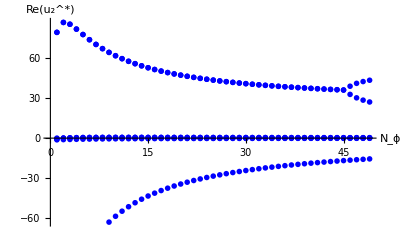

Phi4Trackingu2solsD2.jpg

```mathematica
ListPlot[TCollFP2Sol,  PlotMarkers->{marker1, 0.02},AxesLabel->{Style["N_ϕ", FontSize->14],Style["Re(u_2^*)", FontSize->14]}, TicksStyle->Directive[FontSize->13]]
Export["Phi4Trackingu2solsD2.jpg",%,"JPEG"]
```

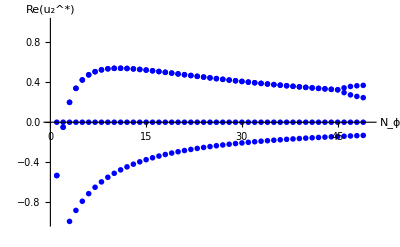

```mathematica
ListPlot[TCollFP2Sol,  PlotMarkers->{marker1, 0.02},AxesLabel->{Style["N_ϕ", FontSize->14],Style["Re(u_2^*)", FontSize->14]}, PlotRange-> {{0,50},{-1,1}}, TicksStyle->Directive[FontSize->13]]
```

```mathematica
Export["Phi4Trackingu2solsD2Zoom.jpg",%,"JPEG"]
```

Phi4Trackingu2solsD2Zoom.jpg

#### N_ϕ=2,20, 200, 2000, 20000

Test out what the eigenvalues are for several different values of N_ϕ

```mathematica
FP2Solgen/. Nphi-> 2;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ2/. Nphi-> 2/.%[[]]
EV2s/. Nphi-> 2/.%%[[]]
```

{{U2[4,2,1]→0.,U2[4,2,2]→0.},{U2[4,2,1]→-139.996,U2[4,2,2]→-65.4207},{U2[4,2,1]→-1.27203,U2[4,2,2]→-0.594424},{U2[4,2,1]→79.2467+765.183 ⅈ,U2[4,2,2]→-382.818-795.465 ⅈ},{U2[4,2,1]→79.2467-765.183 ⅈ,U2[4,2,2]→-382.818+795.465 ⅈ},{U2[4,2,1]→-0.534182+7.09248 ⅈ,U2[4,2,2]→-2.17837-7.86602 ⅈ},{U2[4,2,1]→-0.534182-7.09248 ⅈ,U2[4,2,2]→-2.17837+7.86602 ⅈ}}

{0.,6.89028,-0.453847,6.57252+0.272865 ⅈ,6.57252-0.272865 ⅈ,-0.615061+0.156054 ⅈ,-0.615061-0.156054 ⅈ}

{{2.,2.},{-32.3639,8.51954},{-2.13174,0.589709},{-21.8678-5.92816 ⅈ,-25.6423+15.3038 ⅈ},{-21.8678+5.92816 ⅈ,-25.6423-15.3038 ⅈ},{-2.18487+0.0551619 ⅈ,-1.60779+0.307448 ⅈ},{-2.18487-0.0551619 ⅈ,-1.60779-0.307448 ⅈ}}

```mathematica
FP2Solgen/. Nphi-> 20;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ2/. Nphi-> 20/.%[[]]
EV2s/. Nphi-> 20/.%%[[]]
```

{{U2[4,20,1]→0.,U2[4,20,2]→0.},{U2[4,20,1]→-35.8794,U2[4,20,2]→-1.85422},{U2[4,20,1]→-0.308931,U2[4,20,2]→-0.0159653},{U2[4,20,1]→48.1095+45.6821 ⅈ,U2[4,20,2]→-134.033-63.3544 ⅈ},{U2[4,20,1]→48.1095-45.6821 ⅈ,U2[4,20,2]→-134.033+63.3544 ⅈ},{U2[4,20,1]→0.492265+0.505527 ⅈ,U2[4,20,2]→-1.39807-0.729123 ⅈ},{U2[4,20,1]→0.492265-0.505527 ⅈ,U2[4,20,2]→-1.39807+0.729123 ⅈ}}

{0.,6.64683,-0.582405,6.79016+0.400121 ⅈ,6.79016-0.400121 ⅈ,-0.487779+0.207803 ⅈ,-0.487779-0.207803 ⅈ}

{{2.,2.},{-24.8255,13.0141},{-2.17524,0.710705},{-24.9728-11.4275 ⅈ,-1.78671+13.749 ⅈ},{-24.9728+11.4275 ⅈ,-1.78671-13.749 ⅈ},{-2.13958+0.0694323 ⅈ,-0.439095+0.878924 ⅈ},{-2.13958-0.0694323 ⅈ,-0.439095-0.878924 ⅈ}}

```mathematica
FP2Solgen/. Nphi-> 46;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ2/. Nphi-> 46/.%[[]]
EV2s/. Nphi-> 46/.%%[[]]
```

{{U2[4,46,1]→0.,U2[4,46,2]→0.},{U2[4,46,1]→-16.84,U2[4,46,2]→-0.371803},{U2[4,46,1]→-0.143142,U2[4,46,2]→-0.00316036},{U2[4,46,1]→36.0453+3.46106 ⅈ,U2[4,46,2]→-91.1257-5.61355 ⅈ},{U2[4,46,1]→36.0453-3.46106 ⅈ,U2[4,46,2]→-91.1257+5.61355 ⅈ},{U2[4,46,1]→0.325088+0.0274523 ⅈ,U2[4,46,2]→-0.821526-0.041147 ⅈ},{U2[4,46,1]→0.325088-0.0274523 ⅈ,U2[4,46,2]→-0.821526+0.041147 ⅈ}}

{0.,6.62382,-0.595256,6.9741+0.0528811 ⅈ,6.9741-0.0528811 ⅈ,-0.412224+0.025645 ⅈ,-0.412224-0.025645 ⅈ}

{{2.,2.},{-24.2554,14.1662},{-2.17973,0.752075},{-35.6901-2.35247 ⅈ,-0.0159219+1.54151 ⅈ},{-35.6901+2.35247 ⅈ,-0.0159219-1.54151 ⅈ},{-2.11815+0.00825027 ⅈ,-0.00537691+0.11361 ⅈ},{-2.11815-0.00825027 ⅈ,-0.00537691-0.11361 ⅈ}}

```mathematica
FP2Solgen/. Nphi-> 47;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ2/. Nphi-> 47/.%[[]]
EV2s/. Nphi-> 47/.%%[[]]
```

{{U2[4,47,1]→0.,U2[4,47,2]→0.},{U2[4,47,1]→38.8879,U2[4,47,2]→-95.3195},{U2[4,47,1]→32.7684,U2[4,47,2]→-85.36},{U2[4,47,1]→0.344586,U2[4,47,2]→-0.844628},{U2[4,47,1]→0.296624,U2[4,47,2]→-0.772691},{U2[4,47,1]→-16.5026,U2[4,47,2]→-0.35649},{U2[4,47,1]→-0.140241,U2[4,47,2]→-0.0030295}}

{0.,7.02589,6.93138,-0.387635,-0.433395,6.62344,-0.595472}

{{2.,2.},{-38.25,1.38538},{-33.9865,-1.36028},{-2.11034,0.105701},{-2.12505,-0.0971763},{-24.246,14.1869},{-2.17981,0.752812}}

```mathematica
FP2Solgen/. Nphi-> 200;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ2/. Nphi-> 200/.%[[]]
EV2s/. Nphi-> 200/.%%[[]]
```

{{U2[4,200,1]→0.,U2[4,200,2]→0.},{U2[4,200,1]→51.0854,U2[4,200,2]→-104.448},{U2[4,200,1]→4.45519,U2[4,200,2]→-16.4619},{U2[4,200,1]→0.16334,U2[4,200,2]→-0.333969},{U2[4,200,1]→0.0383493,U2[4,200,2]→-0.1417},{U2[4,200,1]→-4.05573,U2[4,200,2]→-0.020354},{U2[4,200,1]→-0.0341776,U2[4,200,2]→-0.000171523}}

{0.,7.75388,6.64628,-0.0860891,-0.582712,6.6098,-0.603152}

{{2.,2.},{-182.151,14.9886},{-24.8115,-12.8828},{-2.02221,1.56286},{-2.17535,-0.703066},{-23.9175,14.9575},{-2.1825,0.78003}}

```mathematica
FP2Solgen/. Nphi-> 2000;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ2/. Nphi-> 2000/.%[[]]
EV2s/. Nphi-> 2000/.%%[[]]
```

{{U2[4,2000,1]→0.,U2[4,2000,2]→0.},{U2[4,2000,1]→268.685,U2[4,2000,2]→-100.974},{U2[4,2000,1]→0.41435,U2[4,2000,2]→-1.64439},{U2[4,2000,1]→0.0185849,U2[4,2000,2]→-0.037245},{U2[4,2000,1]→0.00349084,U2[4,2000,2]→-0.0138538},{U2[4,2000,1]→-0.410664,U2[4,2000,2]→-0.000205409},{U2[4,2000,1]→-0.00345215,U2[4,2000,2]→-1.72672×10^-6}}

{0.,5.99896,6.6094,-0.00895592,-0.603373,6.60598,-0.60531}

{{2.,2.},{-2653.8,23198.3},{-23.9081,-14.9792},{-2.00225,1.95425},{-2.18258,-0.780766},{-23.8267,15.1854},{-2.18326,0.788}}

```mathematica
FP2Solgen/. Nphi-> 20000;
%/.(lhs_->rhs_):>lhs->N[rhs]
ηϕ2/. Nphi-> 20000/.%[[]]
EV2s/. Nphi-> 20000/.%%[[]]
```

{{U2[4,20000,1]→0.,U2[4,20000,2]→0.},{U2[4,20000,1]→-1.41121×10^7,U2[4,20000,2]→-100.576},{U2[4,20000,1]→0.0411545,U2[4,20000,2]→-0.164488},{U2[4,20000,1]→0.00188229,U2[4,20000,2]→-0.00376534},{U2[4,20000,1]→0.000345945,U2[4,20000,2]→-0.00138269},{U2[4,20000,1]→-0.0411177,U2[4,20000,2]→-2.05596×10^-6},{U2[4,20000,1]→-0.000345561,U2[4,20000,2]→-1.72787×10^-8}}

{0.,6.,6.60594,-0.000899554,-0.605334,6.60559,-0.605527}

{{2.,2.},{-1.49757×10^10,-1.14962×10^6},{-23.8255,-15.1878},{-2.00022,1.9954},{-2.18327,-0.788088},{-23.8177,15.2085},{-2.18334,0.788808}}

There are again some complex solutions initially that collide and form real solutions later on. The collision seems to lie between N_ϕ=46 and N_ϕ=47

#### Connecting the solutions

As there is this split in the solutions, it is necessary to check how they connect to each other. To do so, a list is made for both

```mathematica
FPd2N46 = {{0.,0.},{-16.84000740520566,-0.37180333379450436},{-0.14314159138212262,-0.003160362082980563},{36.04529274339469+3.461062611525848 ⅈ,-91.12574013295887-5.61355300543875 ⅈ},{36.04529274339469-3.461062611525848 ⅈ,-91.12574013295887+5.61355300543875 ⅈ},{0.3250876376287638+0.027452299038160318 ⅈ,-0.8215262938440229-0.04114696379143937 ⅈ},{0.3250876376287638-0.027452299038160318 ⅈ,-0.8215262938440229+0.04114696379143937 ⅈ}}; (*Fixed point coordinates for Subscript[N, ϕ]=46*)
```

```mathematica
FPd2N47 = {{0.,0.},{38.88788348749373,-95.31951063861788},{32.76840537025807,-85.35999687575867},{0.34458638831500576,-0.8446283632911371},{0.2966244391965798,-0.77269126024702},{-16.502573262808397,-0.3564897521131379},{-0.14024136586360433,-0.003029503881397472}};(*Fixed point coordinates for Subscript[N, ϕ]=47*)
```

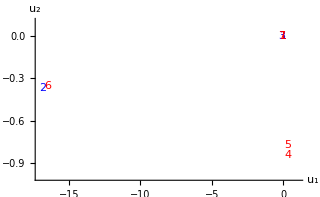

```mathematica
Show[Graphics[{Blue,MapIndexed[Text[First@#2,#1]&,FPd2N46[[1;;3]]/.Rule->List],Red,MapIndexed[Text[First@#2,#1]&,FPd2N47/.Rule->List]},Axes->True,AxesLabel->{Style["u_1", FontSize->12],Style["u_2", FontSize->12]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotRange-> {{-17, 1}, {-1,0.1}}, AspectRatio->1/GoldenRatio], TicksStyle->Directive[FontSize->10]]
```

```mathematica
Export["fixedpointpositionsN46enN47d2Label.jpg",%264,"JPEG"]
```

fixedpointpositionsN46enN47d2Label.jpg

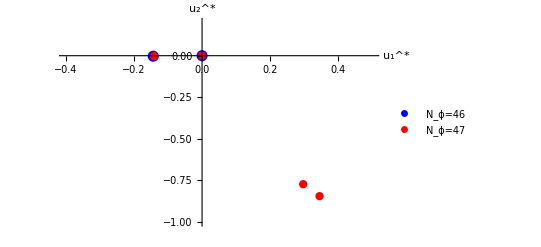

```mathematica
ListPlot[{FPd2N46, FPd2N47}, PlotStyle->{{Blue,PointSize[0.02]},  {Red, PointSize[0.015]}},AxesLabel-> {"u_1^*", "u_2^*"},  PlotLegends->{"N_ϕ=46","N_ϕ=47"}, PlotRange->{{-0.4,0.5}, {-1, 0.2}}]
```

```mathematica
Export["fixedpointpositionsN46enN47d2Labeldots.jpg",%,"JPEG"]
```

fixedpointpositionsN46enN47d2Labeldots.jpg

#### Which solution appears due to the anomalous dimension

```mathematica
Clear[ηϕ2]
Clear[Nphi]
```

```mathematica
FPs2eta0 =  Solve[Coefficient[RHS2phi4, X, 2]==Coefficient[LHS2finalphi4, X, 2]&&Coefficient[RHS2phi4,S2]==Coefficient[LHS2finalphi4, S2]/.ηϕ2-> 0, {U2[4,Nphi, 1], U2[4,Nphi, 2]}]/.Nphi-> 2
```

```mathematica
N[%]
```

```mathematica
etatrack2fp1= {};
etatrack2fp2 = {};
etatrack2fp3 = {};
Do[
βϕ2[4,Nphi,1]=0;
βϕ2[4,Nphi,2]=0;
Nphi =2; 
ηϕ2= ϵ(6 (2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2]))/(48 π+2 U2[4,Nphi,1]+2 Nphi U2[4,Nphi,1]+3 U2[4,Nphi,2]+Nphi U2[4,Nphi,2]);/. Nphi-> 2;
FP2 = Solve[Simplify[Coefficient[RHS2phi4, X, 2]]==Coefficient[LHS2finalphi4, X, 2]&&Simplify[Coefficient[RHS2phi4,S2]]==Coefficient[LHS2finalphi4, S2]/. k-> 1, {U2[4,Nphi, 1], U2[4,Nphi, 2]}];
 AppendTo[etatrack2fp1,{U2[4, Nphi, 1], U2[4, Nphi, 2]}/.FP2[[1]] ];
 AppendTo[etatrack2fp2,{U2[4, Nphi, 1], U2[4, Nphi, 2]}/.FP2[[2]] ];
 AppendTo[etatrack2fp3, {U2[4, Nphi, 1], U2[4, Nphi, 2]}/.FP2[[3] ]];, 
 {ϵ, 1/1000, 1, 1/1000}]
```

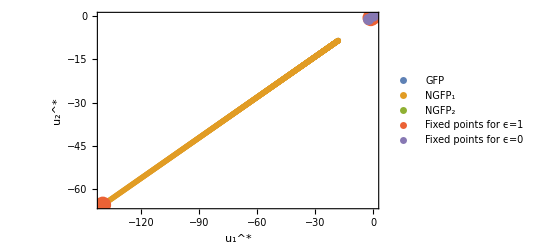

```mathematica
ListPlot[{etatrack2fp1, etatrack2fp2, etatrack2fp3, {{0, 0},{-139.99633604927695,-65.4207280850375},{-1.2720301707651622,-0.594423698976651}}, {{0,0},{-2.461203670518525,-1.150128215028504}}}, PlotLegends->{"GFP", "NGFP_1", "NGFP_2", "Fixed points for ϵ=1", "Fixed points for ϵ=0"}, PlotStyle->{PointSize[0.01],PointSize[0.01],PointSize[0.01], PointSize[0.03], PointSize[0.02]}, FrameLabel->{Style["u_1^*", FontSize->14],Style["u_2^*", FontSize->14]}, PlotRange->All, TicksStyle->Directive[FontSize->13], Frame-> True]
```

```mathematica
Export["Increasingepsilonforanomalousdimfrom0to1fullimagephi4Labeld2Framed.jpg",%,"JPEG"]
```

Increasingepsilonforanomalousdimfrom0to1fullimagephi4Labeld2Framed.jpg

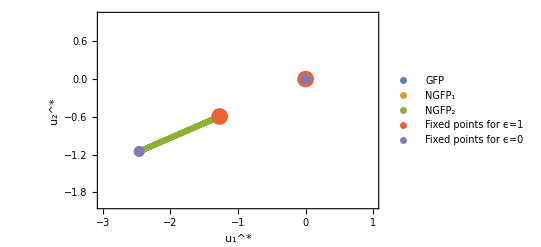

```mathematica
ListPlot[{etatrack2fp1, etatrack2fp2, etatrack2fp3, {{0, 0},{-139.99633604927695,-65.4207280850375},{-1.2720301707651622,-0.594423698976651}}, {{0,0},{-2.461203670518525,-1.150128215028504}}}, PlotLegends->{"GFP", "NGFP_1", "NGFP_2", "Fixed points for ϵ=1", "Fixed points for ϵ=0"}, PlotStyle->{PointSize[0.01],PointSize[0.01],PointSize[0.01], PointSize[0.03], PointSize[0.02]}, FrameLabel->{Style["u_1^*", FontSize->14],Style["u_2^*", FontSize->14]}, PlotRange->{{-3,1},  {-2, 1}}, TicksStyle->Directive[FontSize->13], Frame-> True]
```

```mathematica
Export["Increasingepsilonforanomalousdimfrom0to1zoomedimagephi4Labeld2Framed.jpg",%,"JPEG"]
```

Increasingepsilonforanomalousdimfrom0to1zoomedimagephi4Labeld2Framed.jpg

### Plotting the interesting FP

#### Locating the fixed point

```mathematica
U2u1value = {};
U2u2value = {};
EV2theta1 = {};
EV2theta2 = {};
```

```mathematica
EV={}
Do[S=FP2Solgen/. Nphi-> x;(*Find fixed point coordinates for Subscript[N, ϕ]=x*)
sols = S /.(lhs_->rhs_):>lhs->N[rhs];(*Make it numerical*)
FPs2 = sols[[3]];(*Save the solution for NGFP 2, which we want to study*)
evs2 = EV2s/.Nphi-> x/. FPs2; (*Find stability coefficients at NGFP 2*)
FPvalue1 = U2[4,x,1]/.FPs2[[1]];
FPvalue2 = U2[4,x,2]/.FPs2[[2]];
 U2u1value = Append[U2u1value,{x,FPvalue1}];(*Save Subscript[U, 1]-value*)
 U2u2value = Append[U2u2value,{x,FPvalue2}];(*Save Subscript[U, 2]-value*)
theta1 = -evs2[[1]];
theta2 = -evs2[[2]];
 EV2theta1 = Append[EV2theta1,{x,theta1}];(*Save EV1-value*)
 EV2theta2 = Append[EV2theta2,{x,theta2}](*Save EV2-value*), {x,2, 46}](*Finds NGFP 2 + stability coefficient for Subscript[N, ϕ]≤46*)
Do[S=FP2Solgen/. Nphi-> x;
sols = S /.(lhs_->rhs_):>lhs->N[rhs];
FPs2 = sols[[7]];
evs2 = EV2s/.Nphi-> x/. FPs2; 
FPvalue1 = U2[4,x,1]/.FPs2[[1]];
FPvalue2 = U2[4,x,2]/.FPs2[[2]];
 U2u1value = Append[U2u1value,{x,FPvalue1}];
 U2u2value = Append[U2u2value,{x,FPvalue2}];
theta1 = -evs2[[1]];
theta2 = -evs2[[2]];
Print[x];(*Counter to see how far the evaluation was*)
 EV2theta1 = Append[EV2theta1,{x,theta1}];
 EV2theta2 = Append[EV2theta2,{x,theta2}], {x,47, 1000}](*Finds NGFP 2 + stability coefficient for Subscript[N, ϕ]≥47*)
```

{}

```mathematica
DumpSave["FPphi4d2U1.mx", U2u1value];(*Saves the Subscript[U, i] and stability coefficient-values*)
DumpSave["FPphi4d2U2.mx", U2u2value];
DumpSave["FPphi4d2EV1.mx", EV2theta1];
DumpSave["FPphi4d2EV2.mx", EV2theta2];
```

```mathematica
DumpGet["FPphi4d2U1.mx"];(*Get the Subscript[U, i] and stability coefficient values from storage*)
DumpGet["FPphi4d2U2.mx"];
DumpGet["FPphi4d2EV1.mx"];
DumpGet["FPphi4d2EV2.mx"];
```

Next step is to determine the anomalous value for increasing N_ϕ.

```mathematica
AnomalousDimd2phi4 = {}
Do [eta = (6 (2 U2[4,1]+2 Nphi U2[4,1]+3 U2[4,2]+Nphi U2[4,2]))/(48 π+2 U2[4,1]+2 Nphi U2[4,1]+3 U2[4,2]+Nphi U2[4,2])/. U2[4,1]->  U2u1value[[x-1]][[2]]/. U2[4,2]-> U2u2value[[x-1]][[2]]/. Nphi-> x;
AnomalousDimd2phi4 = Append[AnomalousDimd2phi4, {x, eta}], {x, 2, 1000}]
```

{}

```mathematica
DumpSave["Anomalous dimension d2 phi^4", AnomalousDimd2phi4];
```

```mathematica
DumpGet["Anomalous dimension d2 phi^4"]
```

#### Plotting the data

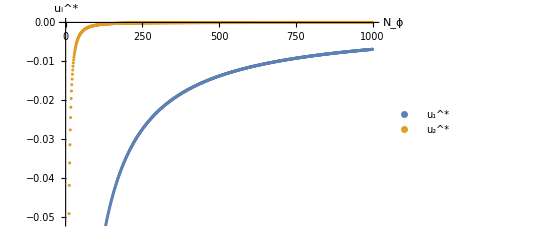

```mathematica
ListPlot[{U2u1value,U2u2value}, PlotLegends->{"u_1^*", "u_2^*"}, AxesLabel->{"N_ϕ", "u_i^*"}]
```

```mathematica
Export["Phi4IncreasingNphiUvaluesLabeld2.jpg", %, "JPEG"]
```

Phi4IncreasingNphiUvaluesLabeld2.jpg

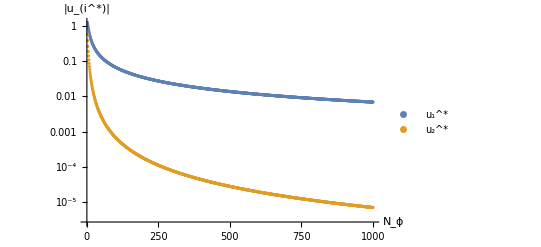

```mathematica
ListLogPlot[{U2u1value *Threaded[{1,-1}],U2u2value*Threaded[{1,-1}]}, PlotLegends->{"u_1^*", "u_2^*"}, AxesLabel->{"N_ϕ", "|u_(i^*)|"}]
```

```mathematica
Export["Phi4IncreasingNphiUvalueslogplotLabeld2.jpg", %, "JPEG"]
```

Phi4IncreasingNphiUvalueslogplotLabeld2.jpg

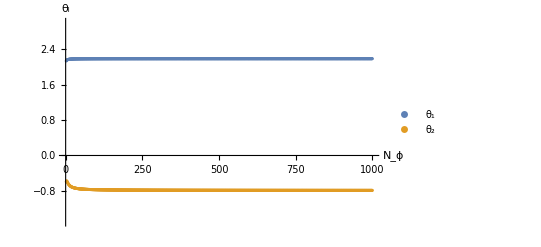

```mathematica
ListPlot[{EV2theta1,EV2theta2}, PlotRange->{{ 0, 1001 }, { -1.5, 3}}, PlotLegends->{"θ_1", "θ_2"}, AxesLabel->{"N_ϕ", "θ_i"}]
```

Export["Phi4IncreasingNphithetavaluesd2.jpg", %112, "JPEG"]

Phi4IncreasingNphithetavaluesd2.jpg

```mathematica
1/2.18
```

0.458716

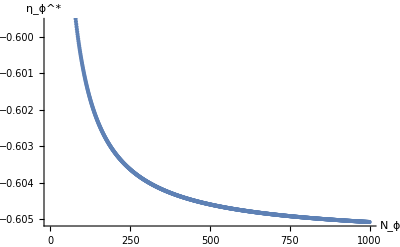

```mathematica
ListPlot[AnomalousDimd2phi4, AxesLabel->{"N_ϕ", "η_ϕ^*"}]
```

## Large N_ϕ-expansion

As again the stability coefficients seem to be independent of N_ϕ, it makes sense to look for a large N_ϕ-expansion in this case as well.

## Expanding the fixed points

### Only u_(1,1), u_(2,1)

```mathematica
Clear[ηϕ2];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[βϕ2];
U1ExpPhi4d2 = U2[4, Nphi, 1]-> U2[1,1] Nphi^-1+ U2[1,2] Nphi^-2+ U2[1,3] Nphi^-3;
U2ExpPhi4d2 = U2[4, Nphi, 2]-> U2[2,1] Nphi^-1+ U2[2,2] Nphi^-2+ U2[2,3] Nphi^-3;
RHSphi4d2Exp = Normal[Series[RHS2phi4/. U1ExpPhi4d2/.U2ExpPhi4d2, {Nphi, ∞, 1}]];
LHSphi4d2Exp = Normal[Series[LHS2finalphi4/. U1ExpPhi4d2/.U2ExpPhi4d2, {Nphi, ∞, 1}]];
```

```mathematica
ηϕ2Exp = Normal[Series[ηϕ2/. Solve[Simplify[Coefficient[RHSphi4d2Exp, X, 1]]==Coefficient[LHSphi4d2Exp, X, 1], ηϕ2], {Nphi, ∞, 0}]]
```

{(6 (2 U2[1,1]+U2[2,1]))/(48 π+2 U2[1,1]+U2[2,1])}

```mathematica
ηϕ2= ηϕ2Exp[[1]];
βϕ2[4,Nphi, 1]= 0;(*Both beta functions appearing in ∂_t Subscript[F, k] are set to 0*)
βϕ2[4,Nphi, 2]=0;
FPSolExpPhi4d2= Solve[Simplify[Coefficient[RHSphi4d2Exp, X, 2]]==Coefficient[LHSphi4d2Exp, X, 2]&&Simplify[Coefficient[RHSphi4d2Exp,S2]]==Coefficient[LHSphi4d2Exp, S2]/. k-> 1, {U2[1, 1], U2[ 2,1]}]
```

{{U2[1,1]→0,U2[2,1]→0},{U2[1,1]→12 (-11-3 √13) π,U2[2,1]→0},{U2[1,1]→12 (-11+3 √13) π,U2[2,1]→0},{U2[1,1]→12 π,U2[2,1]→-24 π},{U2[1,1]→12 (11+3 √13) π,U2[2,1]→48 (-11-3 √13) π},{U2[1,1]→12 (11-3 √13) π,U2[2,1]→48 (-11+3 √13) π}}

```mathematica
FPSolExpPhi4d2/.(lhs_->rhs_):>lhs->N[rhs]
```

{{U2[1,1]→0.,U2[2,1]→0.},{U2[1,1]→-822.468,U2[2,1]→0.},{U2[1,1]→-6.91199,U2[2,1]→0.},{U2[1,1]→37.6991,U2[2,1]→-75.3982},{U2[1,1]→822.468,U2[2,1]→-3289.87},{U2[1,1]→6.91199,U2[2,1]→-27.648}}

### u_(1,1), u_(1,2), u_(2,2)

```mathematica
Clear[ηϕ2];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[βϕ2];
U1ExpPhi4d2 = U2[4, Nphi, 1]-> U2[1,1] Nphi^-1+ U2[1,2] Nphi^-2+ U2[1,3] Nphi^-3;
U2ExpPhi4d2Extra = U2[4, Nphi, 2]->  U2[2,2] Nphi^-2+ U2[2,3] Nphi^-3;
RHSphi4d2ExpExt = Normal[Series[RHS2phi4/. U1ExpPhi4d2/.U2ExpPhi4d2Extra, {Nphi, ∞, 2}]];
LHSphi4d2ExpExt= Normal[Series[LHS2finalphi4/. U1ExpPhi4d2/.U2ExpPhi4d2Extra, {Nphi, ∞, 2}]];
ηϕ2ExpExt = Normal[Series[ηϕ2/. Solve[Simplify[Coefficient[RHSphi4d2ExpExt, X, 1]]==Coefficient[LHSphi4d2ExpExt, X, 1], ηϕ2], {Nphi, ∞, 1}]]
```

{(6 U2[1,1])/(24 π+U2[1,1])+(72 π (2 U2[1,1]+2 U2[1,2]+U2[2,2]))/(Nphi (24 π+U2[1,1])^2)}

```mathematica
ηϕ2= ηϕ2ExpExt[[1]]
βϕ2[4,Nphi, 1]= 0;(*Both beta functions appearing in ∂_t Subscript[F, k] are set to 0*)
βϕ2[4,Nphi, 2]=0;
FPSolExpPhi4d2= Solve[Simplify[Coefficient[Coefficient[RHSphi4d2ExpExt, X, 2], Nphi, -2]]==Coefficient[Coefficient[LHSphi4d2ExpExt, X, 2], Nphi, -2]&&Simplify[Coefficient[Coefficient[RHSphi4d2ExpExt,S2], Nphi, -2]]==Coefficient[Coefficient[LHSphi4d2ExpExt, S2], Nphi, -2]&&
Simplify[Coefficient[Coefficient[RHSphi4d2ExpExt, X, 2], Nphi, -1]]==Coefficient[Coefficient[LHSphi4d2ExpExt, X, 2], Nphi, -1]/. k-> 1, {U2[1, 1],U2[1,2], U2[2,2]}]
```

(6 U2[1,1])/(24 π+U2[1,1])+(72 π (2 U2[1,1]+2 U2[1,2]+U2[2,2]))/(Nphi (24 π+U2[1,1])^2)

{{U2[1,1]→0,U2[1,2]→0,U2[2,2]→0},{U2[1,1]→12 (-11-3 √13) π,U2[1,2]→6/13 (793+217 √13) π,U2[2,2]→12 (-11-3 √13) π},{U2[1,1]→12 (-11+3 √13) π,U2[1,2]→6/13 (793-217 √13) π,U2[2,2]→12 (-11+3 √13) π}}

```mathematica
FPSolExpPhi4d2/.(lhs_->rhs_):>lhs->N[rhs]
```

{{U2[1,1]→0.,U2[1,2]→0.,U2[2,2]→0.},{U2[1,1]→-822.468,U2[1,2]→2284.28,U2[2,2]→-822.468},{U2[1,1]→-6.91199,U2[1,2]→15.3629,U2[2,2]→-6.91199}}

### Check with fit

```mathematica
FitFP1phi4d3 =Fit[Take[U2u1value, -500], { 1/y,1/y^2}, y]
FitFP2phi4d3 =Fit[Take[U2u2value, -500], { 1/y,1/y^2}, y]
```

15.322/y^2-6.91196/y

-6.88143/y^2-0.0000220672/y

```mathematica
FitFP2phi4d3 =Fit[Take[U2u2value, -500], { 1/y^2}, y]
```

-6.89562/y^2

So the third solution seems to be the solution of interest: {U2[1,1]→-6.91199,U2[1,2]→15.3629,U2[2,2]→-6.91199}

### Anomalous dimension

```mathematica
ηϕ2ExpExt[[1]]/.{U2[1,1]->-6.911987904849546,U2[1,2]->15.362929238560609,U2[2,2]->-6.911987904849546}
```

-0.605551+0.481767/Nphi

## Expanding the stability matrix

Before running this, redefine the beta functions!

### Only lowest order

```mathematica
U1ExpPhi4d2 = U2[4, Nphi, 1]-> U2[1,1] Nphi^-1+ U2[1,2] Nphi^-2+ U2[1,3] Nphi^-3;
U2ExpPhi4d2= U2[4, Nphi, 2]->  U2[2,1] Nphi^-1+U2[2,2] Nphi^-2+ U2[2,3] Nphi^-3;
U2ExpPhi4d2Extra = U2[4, Nphi, 2]->  U2[2,2] Nphi^-2+ U2[2,3] Nphi^-3;
```

```mathematica
BexpPhi4d2[1,1]= Normal[Series[D[βϕ2[U2[4,Nphi, 1], U2[4,Nphi, 2]][4,Nphi, 1], U2[4, Nphi, 1]]/. U1ExpPhi4d2/.U2ExpPhi4d2/.{U2[1,1]->-6.911987904849546,U2[2,1]->0.}, {Nphi, ∞, 0}]]
BexpPhi4d2[2,1]= Normal[Series[D[βϕ2[U2[4,Nphi, 1], U2[4,Nphi, 2]][4,Nphi, 2], U2[4, Nphi, 1]]/. U1ExpPhi4d2/.U2ExpPhi4d2/.{U2[1,1]->-6.911987904849546,U2[2,1]->0.}, {Nphi, ∞, 0}]]
BexpPhi4d2[1,2]= Normal[Series[D[βϕ2[U2[4,Nphi, 1], U2[4,Nphi, 2]][4,Nphi, 1], U2[4, Nphi, 2]]/. U1ExpPhi4d2/.U2ExpPhi4d2/.{U2[1,1]->-6.911987904849546,U2[2,1]->0.}, {Nphi, ∞, 0}]]
BexpPhi4d2[2,2]= Normal[Series[D[βϕ2[U2[4,Nphi, 1], U2[4,Nphi, 2]][4,Nphi, 2], U2[4, Nphi, 2]]/. U1ExpPhi4d2/.U2ExpPhi4d2/.{U2[1,1]->-6.911987904849546,U2[2,1]->0.}, {Nphi, ∞, 0}]]
```

-2.18335

0

-1.48612

0.788897

```mathematica
Matphi4d2Exp = Table[BexpPhi4d2[a,b],{a,1,2},{b,1,2}];
%//MatrixForm
Eigenvalues[Matphi4d2Exp]
```

(-2.18335 | -1.48612
0 | 0.788897)

{-2.18335,0.788897}

### One extra order

```mathematica
BexpPhi4d2ExtraOrder[1,1]= Normal[Series[D[βϕ2[U2[4,Nphi, 1], U2[4,Nphi, 2]][4,Nphi, 1], U2[4, Nphi, 1]]/. U1ExpPhi4d2/.U2ExpPhi4d2Extra/.{U2[1,1]->-6.911987904849546,U2[1,2]->15.362929238560609,U2[2,2]->-6.911987904849546}, {Nphi, ∞, 1}]]
BexpPhi4d2ExtraOrder[2,1]= Normal[Series[D[βϕ2[U2[4,Nphi, 1], U2[4,Nphi, 2]][4,Nphi, 2], U2[4, Nphi, 1]]/. U1ExpPhi4d2/.U2ExpPhi4d2Extra/.{U2[1,1]->-6.911987904849546,U2[1,2]->15.362929238560609,U2[2,2]->-6.911987904849546}, {Nphi, ∞, 1}]]
BexpPhi4d2ExtraOrder[1,2]= Normal[Series[D[βϕ2[U2[4,Nphi, 1], U2[4,Nphi, 2]][4,Nphi, 1], U2[4, Nphi, 2]]/. U1ExpPhi4d2/.U2ExpPhi4d2Extra/.{U2[1,1]->-6.911987904849546,U2[1,2]->15.362929238560609,U2[2,2]->-6.911987904849546}, {Nphi, ∞, 1}]]
BexpPhi4d2ExtraOrder[2,2]= Normal[Series[D[βϕ2[U2[4,Nphi, 1], U2[4,Nphi, 2]][4,Nphi, 2], U2[4, Nphi, 2]]/. U1ExpPhi4d2/.U2ExpPhi4d2Extra/.{U2[1,1]->-6.911987904849546,U2[1,2]->15.362929238560609,U2[2,2]->-6.911987904849546}, {Nphi, ∞, 1}]]
```

-2.18335+1.65563/Nphi

-2.97224/Nphi

-1.48612-2.03452/Nphi

0.788897-3.28373/Nphi

```mathematica
Matphi4d2ExpExtra = Table[BexpPhi4d2ExtraOrder[a,b],{a,1,2},{b,1,2}];
%//MatrixForm
Series[Eigenvalues[Matphi4d2ExpExtra], {Nphi, ∞, 1}]
```

(-2.18335+1.65563/Nphi | -1.48612-2.03452/Nphi
-2.97224/Nphi | 0.788897-3.28373/Nphi)

{-2.18335+0.169504/Nphi+O[1/Nphi]^2,0.788897-1.79761/Nphi+O[1/Nphi]^2}

## Making figures

### Anomalous dimension

To verify previous result, we plot the original anomalous dimension data and the value it gets in the expansion

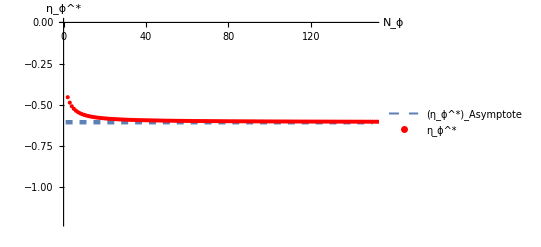

Phi4IncreasingNphiAnomalousDimension+Expansiond2.jpg

```mathematica
Show[Plot[{y=-0.6055512754639929},{y,1,150},PlotStyle->{Thickness[0.008], Dashed}, PlotLegends->{"(η_ϕ^*)_Asymptote"}],ListPlot[AnomalousDimd2phi4,PlotStyle->Red,  PlotLegends->{"η_ϕ^*"}], AxesLabel-> { "N_ϕ", "η_ϕ^*"}]
Export["Phi4IncreasingNphiAnomalousDimension+Expansiond2.jpg", %, "JPEG"]
```

To check the value the anomalous dimension approaches in the large N-limit, it is fitted with a polynomial function.

```mathematica
FitAndim2phi4 =Fit[Take[AnomalousDimd2phi4, -500], {1, 1/y, 1/y^2}, y]
```

-0.605551-0.377848/y^2+0.481766/y

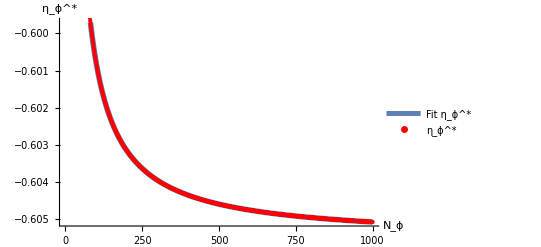

```mathematica
Show[Plot[{FitAndim2phi4},{y,1,1000},PlotStyle->{Thickness[0.01]}, PlotLegends->{"Fit η_ϕ^*"}],ListPlot[AnomalousDimd2phi4,PlotStyle->Red,  PlotLegends->{"η_ϕ^*"}], AxesLabel-> { "N_ϕ", "η_ϕ^*"}]
```

```mathematica
Export["Phi4IncreasingNphiAnomalousDimension+fitd2.jpg", %, "JPEG"]
```

Phi4IncreasingNphiAnomalousDimension+fitd2.jpg

### To the stability coefficients

As before, we plot the expansion value for the stability coefficient together with the actual value.

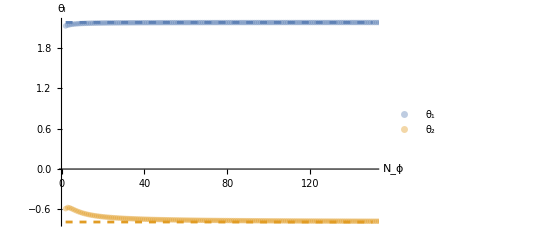

Phi4IncreasingNphiStabCoeff+Expansiond2.jpg

```mathematica
Show[Plot[{y=2.183346173608057, y= -0.7888974490720146},{y,2,150}, (*PlotLegends-> {"θ_(1,  Asymptote)", "θ_(2 Asymptote)"},*) PlotStyle->{{RGBColor[0.368417,0.506779,0.709798],Dashed}, {RGBColor[0.880722,0.611041,0.142051],Dashed}}],ListPlot[{EV2theta1, EV2theta2},PlotStyle->{{Opacity[0.4,RGBColor[0.368417,0.506779,0.709798]],PointSize[0.01]}, {Opacity[0.4,RGBColor[0.880722,0.611041,0.142051]],PointSize[0.01]}},  PlotLegends->{"θ_1", "θ_2"}], AxesLabel->{"N_ϕ","θ_i"}]
Export["Phi4IncreasingNphiStabCoeff+Expansiond2.jpg", %, "JPEG"]
```

Just as for the anomalous dimension, the fit function will be used to fit a polynomial of a+b/N_ϕ+ c/N_ϕ^2to the data of the stability coefficients to see what value this approaches in the limit.

```mathematica
FitEV1phi4d2 =Fit[Take[EV2theta1, -500], {1, 1/y,1/y^2}, y]
```

2.18335+0.150306/y^2-0.169503/y

```mathematica
FitEV2phi4d2 =Fit[Take[EV2theta2, -500], {1, 1/y,1/y^2}, y]
```

-0.788897-4.83104/y^2+1.79759/y

```mathematica
FitU210EV1phi4d2 =Fit[Take[EV2theta1, -500], {1/y^2}, y]
```

937217./y^2

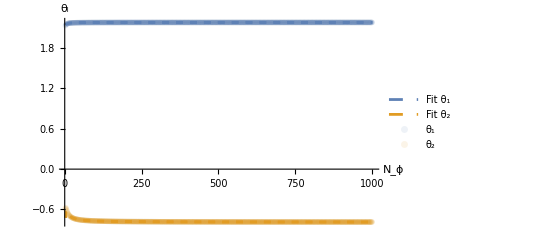

```mathematica
Show[Plot[{FitEV1phi4d2, FitEV2phi4d2 },{y,3,1001}, PlotLegends-> {"Fit θ_1", "Fit θ_2"}, PlotStyle->{{RGBColor[0.368417,0.506779,0.709798],Dashed}, {RGBColor[0.880722,0.611041,0.142051],Dashed}}],ListPlot[{EV2theta1, EV2theta2},PlotStyle->{{Opacity[0.1,RGBColor[0.368417,0.506779,0.709798]],PointSize[0.01]}, {Opacity[0.1,RGBColor[0.880722,0.611041,0.142051]],PointSize[0.01]}},  PlotLegends->{"θ_1", "θ_2"}], AxesLabel->{"N_ϕ","θ_i"}]
```

```mathematica
(*Export["Phi4IncreasingNphiStabCoeff+fitd2.jpg", %153, "JPEG"]
```

Phi4IncreasingNphiStabCoeff+fitd2.jpg

# Finding Fixed points O(ϕ^6), d=2

In the xAct file Invariant quantities for N scalar fields, we have derived the right-hand side (RHS) and left-hand side (LHS) of the Wetterich equation for spacetime dimension d=2 up to order ϕ^6.  The results are given in the two initialization cells below in the set up tab. Now we can use Mathematica without the package to work on solving the system.

## Set up

```mathematica
Clear[βϕ2](*Clear to make sure nothing accidentaly remains*)
Clear[ηϕ2]
Clear[Nphi]
```

```mathematica
pe=6;
RHS2phi6=Simplify[1/(960 k^4 π)X^3 (16 (14+3 Nphi) U2[pe,Nphi,  1]^3 (-10+ηϕ2)+24 (16+3 Nphi) U2[pe,Nphi,  1]^2 U2[pe,Nphi,  2](-10+ηϕ2)+6 (37+3 Nphi) U2[pe,Nphi,  1] U2[pe,Nphi,  2]^2 (-10+ηϕ2)+(25+Nphi) U2[pe,Nphi,  2]^3 (-10+ηϕ2)-20 U2[pe,Nphi,  1] (18 U2[pe,Nphi,  3]+2 (4+Nphi) U2[pe,Nphi, 4]+3 U2[pe,Nphi, 5]) (-8+ηϕ2)-5 U2[pe,Nphi,  2](24U2[pe,Nphi,  3]+2 (11+Nphi) U2[pe,Nphi, 4]+3 U2[pe,Nphi, 5]) (-8+ηϕ2))-1/(192 k^2 π)X^2 (4 (5+2 Nphi) U2[pe,Nphi,  1]^2 (-8+ηϕ2)+8 (4+Nphi) U2[pe,Nphi,  1] U2[pe,Nphi,  2] (-8+ηϕ2)+(11+Nphi) U2[pe,Nphi,  2]^2 (-8+ηϕ2)-2 (12 U2[pe,Nphi,  3]+2 (3+Nphi) U2[pe,Nphi, 4]+3 U2[pe,Nphi, 5]) (-6+ηϕ2))-1/(3840 k^6 π)(-8 k^2 S3(4 U2[pe,Nphi,  1] (78 U2[pe,Nphi,  2]^2 (-10+ηϕ2)-5 (4 U2[pe,Nphi, 4]+9 U2[pe,Nphi, 5]) (-8+ηϕ2))+32 U2[pe,Nphi,  1]^3 (-10+ηϕ2)+168 U2[pe,Nphi,  1]^2 U2[pe,Nphi,  2](-10+ηϕ2)+2 (71+2 Nphi) U2[pe,Nphi,  2]^3 (-10+ηϕ2)-5 U2[pe,Nphi,  2] (32 U2[pe,Nphi, 4]+3 (16+Nphi) U2[pe,Nphi, 5]) (-8+ηϕ2))+40 k^4 S2 (4 U2[pe,Nphi,  1]^2 (-8+ηϕ2)+16 U2[pe,Nphi,  1] U2[pe,Nphi,  2](-8+ηϕ2)+(11+Nphi) U2[pe,Nphi,  2]^2 (-8+ηϕ2)-(4+Nphi) (2 U2[pe,Nphi, 4]+3 U2[pe,Nphi, 5]) (-6+ηϕ2))+240 k^8 Nphi (-4+ηϕ2)-120 U2[pe,Nphi,  3](2 k^4 Nphi (-6+ηϕ2)) X^2)+1/(960 k^6 π)X (k^2 S2 (4 U2[pe,Nphi,  1](9 (19+Nphi) U2[pe,Nphi,  2]^2 (-10+ηϕ2)-5 (12 U2[pe,Nphi,  3]+2 (11+Nphi) U2[pe,Nphi, 4]+3 (6+Nphi) U2[pe,Nphi, 5]) (-8+ηϕ2))+192 U2[pe,Nphi,  1]^3 (-10+ηϕ2)+792 U2[pe,Nphi,  1]^2 U2[pe,Nphi,  2](-10+ηϕ2)+6 (34+Nphi) U2[pe,Nphi,  2]^3 (-10+ηϕ2)-5 U2[pe,Nphi,  2] (96 U2[pe,Nphi,  3]+8 (9+Nphi) U2[pe,Nphi, 4]+3 (20+Nphi) U2[pe,Nphi, 5]) (-8+ηϕ2))+20 k^6 (2 (1+Nphi) U2[pe,Nphi,  1]+(3+Nphi) U2[pe,Nphi,  2]) (-6+ηϕ2)-60 k^2 (2 (1+Nphi) U2[pe,Nphi,  1]+(3+Nphi) U2[pe,Nphi,  2]) U2[pe,Nphi,  3] (-8+ηϕ2) X^2)];(*The right-hand side of the Wetterich equation for d=2, from the xAct file!*)
```

Next we define the Left Hand Side of the Wetterich equation as well. This is given by ∂_t Γ_k:

```mathematica
LHScollectedd2order6=-ηϕ2 X +(-2U2[6, Nphi, 1] ηϕ2-2U2[6, Nphi, 1]+β2[6, Nphi, 1])X^2/k^2+(-2U2[6, Nphi, 2] ηϕ2-2U2[6, Nphi, 2]+β2[6, Nphi, 2])S2/k^2+(-3U2[6, Nphi, 3] ηϕ2-4U2[6, Nphi, 3]+β2[6, Nphi, 3])X^3/k^4+(-3U2[6, Nphi, 4] ηϕ2 -4U2[6, Nphi, 4]+β2[6, Nphi, 4])(X S2)/k^4+(-3U2[6, Nphi, 5] ηϕ2 -4U2[6, Nphi, 5]+β2[6, Nphi, 5])S3/k^4;(*LHS of Wetterich equation for d=2 up to order phi^6*)
```

To verify if the input has been performed correctly, the anomalous dimension is investigated once again.

```mathematica
Solve[Simplify[Coefficient[Coefficient[RHS2phi6, X, 1], Subscript[S, 2], 0]]==Coefficient[Coefficient[LHScollectedd2order6, X], Subscript[S, 2], 0], ηϕ2](*Solve for the anomalous dimension*)
```

{{ηϕ2→(6 (2 U2[6,Nphi,1]+2 Nphi U2[6,Nphi,1]+3 U2[6,Nphi,2]+Nphi U2[6,Nphi,2]))/(48 π+2 U2[6,Nphi,1]+2 Nphi U2[6,Nphi,1]+3 U2[6,Nphi,2]+Nphi U2[6,Nphi,2])}}

## Finding Fixed points and Beta functions

## General solution

First the anomalous dimension has to be defined:

```mathematica
ηϕ2=(6 (2 U2[6,Nphi,1]+2 Nphi U2[6,Nphi,1]+3 U2[6,Nphi,2]+Nphi U2[6,Nphi,2]))/(48 π+2 U2[6,Nphi,1]+2 Nphi U2[6,Nphi,1]+3 U2[6,Nphi,2]+Nphi U2[6,Nphi,2]);
```

### Fixed points

```mathematica
β2[6, Nphi, 1]=0;(*Set all appearing beta functions to zero, as this is the case at the fixed point position*)
β2[6, Nphi, 2]=0;
β2[6, Nphi, 3]=0;
β2[6, Nphi, 4]=0;
β2[6, Nphi, 5]=0;
```

#### Solve in two steps

```mathematica
U345solved2phi6=Simplify[Solve[Coefficient[k^4 LHScollectedd2order6, X, 3]== Coefficient[k^4 RHS2phi6, X,3]&&Coefficient[k^4 LHScollectedd2order6, S3]==Coefficient[k^4 RHS2phi6,S3]&&Simplify[k^4 Coefficient[Coefficient[LHScollectedd2order6 ,S2 ],X]]== Simplify[k^4 Coefficient[Coefficient[RHS2phi6,S2 ],X]], {U2[6, Nphi, 3], U2[6, Nphi, 4],U2[6, Nphi, 5]}]]
```

{{U2[6,Nphi,3]→(1024 (1+Nphi)^3 (200+59 Nphi+5 Nphi^2) U2[6,Nphi,1]^8+256 (1+Nphi)^2 U2[6,Nphi,1]^7 (16 (17572+10053 Nphi+1745 Nphi^2+66 Nphi^3) π+(5504+4958 Nphi+1365 Nphi^2+162 Nphi^3+3 Nphi^4) U2[6,Nphi,2])+128 (1+Nphi) U2[6,Nphi,1]^6 (768 (79810+62582 Nphi+15475 Nphi^2+1167 Nphi^3) π^2+8 (405528+511604 Nphi+212389 Nphi^2+34172 Nphi^3+1443 Nphi^4) π U2[6,Nphi,2]+(31253+49150 Nphi+28036 Nphi^2+7534 Nphi^3+923 Nphi^4+24 Nphi^5) U2[6,Nphi,2]^2)+32 U2[6,Nphi,1]^5 (221184 (37766+35497 Nphi+10350 Nphi^2+939 Nphi^3) π^3+2304 (484408+767636 Nphi+403547 Nphi^2+83890 Nphi^3+5619 Nphi^4) π^2 U2[6,Nphi,2]+48 (633233+1282310 Nphi+945619 Nphi^2+314811 Nphi^3+44624 Nphi^4+1827 Nphi^5) π U2[6,Nphi,2]^2+(189950+443299 Nphi+405643 Nphi^2+189090 Nphi^3+46488 Nphi^4+5163 Nphi^5+143 Nphi^6) U2[6,Nphi,2]^3)+16 U2[6,Nphi,1]^4 (14155776 (3058+1589 Nphi+201 Nphi^2) π^4+221184 (245888+227825 Nphi+64275 Nphi^2+5430 Nphi^3) π^3 U2[6,Nphi,2]+4608 (874375+1272519 Nphi+635335 Nphi^2+122619 Nphi^3+7296 Nphi^4) π^2 U2[6,Nphi,2]^2+8 (9366412+17441985 Nphi+12170276 Nphi^2+3837062 Nphi^3+503552 Nphi^4+19673 Nphi^5) π U2[6,Nphi,2]^3+(337228+744883 Nphi+673557 Nphi^2+312890 Nphi^3+74266 Nphi^4+7683 Nphi^5+213 Nphi^6) U2[6,Nphi,2]^4)+U2[6,Nphi,2]^3 (1698693120 (25+Nphi) π^5+7077888 (1425+1481 Nphi+62 Nphi^2) π^4 U2[6,Nphi,2]+110592 (-20375+19690 Nphi+7701 Nphi^2+312 Nphi^3) π^3 U2[6,Nphi,2]^2+384 (-463698-57105 Nphi+90711 Nphi^2+21949 Nphi^3+847 Nphi^4) π^2 U2[6,Nphi,2]^3+8 (3+Nphi)^2 (-41148+369 Nphi+1702 Nphi^2+85 Nphi^3) π U2[6,Nphi,2]^4+(3+Nphi)^3 (-56+229 Nphi+34 Nphi^2+Nphi^3) U2[6,Nphi,2]^5)+2 U2[6,Nphi,1] U2[6,Nphi,2]^2 (5096079360 (37+3 Nphi) π^5+7077888 (38456+12363 Nphi+745 Nphi^2) π^4 U2[6,Nphi,2]+110592 (799759+533129 Nphi+95479 Nphi^2+4497 Nphi^3) π^3 U2[6,Nphi,2]^2+1152 (2626686+2644365 Nphi+909049 Nphi^2+118063 Nphi^3+4685 Nphi^4) π^2 U2[6,Nphi,2]^3+16 (1698003+2344500 Nphi+1210455 Nphi^2+278261 Nphi^3+26706 Nphi^4+859 Nphi^5) π U2[6,Nphi,2]^4+(3+Nphi)^2 (8358+11995 Nphi+4855 Nphi^2+537 Nphi^3+15 Nphi^4) U2[6,Nphi,2]^5)+8 U2[6,Nphi,1]^2 U2[6,Nphi,2] (5096079360 (16+3 Nphi) π^5+10616832 (18461+8030 Nphi+693 Nphi^2) π^4 U2[6,Nphi,2]+55296 (1543279+1279422 Nphi+273977 Nphi^2+15810 Nphi^3) π^3 U2[6,Nphi,2]^2+576 (6313722+7697107 Nphi+3039851 Nphi^2+441549 Nphi^3+19899 Nphi^4) π^2 U2[6,Nphi,2]^3+24 (1714056+2749605 Nphi+1592035 Nphi^2+402529 Nphi^3+41985 Nphi^4+1422 Nphi^5) π U2[6,Nphi,2]^4+(116793+257910 Nphi+218445 Nphi^2+88414 Nphi^3+17357 Nphi^4+1460 Nphi^5+37 Nphi^6) U2[6,Nphi,2]^5)+16 U2[6,Nphi,1]^3 (1698693120 (14+3 Nphi) π^5+7077888 (15330+7540 Nphi+879 Nphi^2) π^4 U2[6,Nphi,2]+55296 (1251757+1132203 Nphi+291633 Nphi^2+20607 Nphi^3) π^3 U2[6,Nphi,2]^2+192 (19359934+26211013 Nphi+11974371 Nphi^2+2027063 Nphi^3+104995 Nphi^4) π^2 U2[6,Nphi,2]^3+16 (3286725+5732926 Nphi+3720511 Nphi^2+1064220 Nphi^3+125060 Nphi^4+4558 Nphi^5) π U2[6,Nphi,2]^4+(180998+397661 Nphi+355478 Nphi^2+157314 Nphi^3+34334 Nphi^4+3217 Nphi^5+86 Nphi^6) U2[6,Nphi,2]^5))/(60 (10871635968 π^6+64 (1+Nphi)^3 (64+19 Nphi+Nphi^2) U2[6,Nphi,1]^6+113246208 (327+59 Nphi) π^5 U2[6,Nphi,2]+3538944 (9899+4245 Nphi+388 Nphi^2) π^4 U2[6,Nphi,2]^2+12288 (704241+578313 Nphi+128331 Nphi^2+7931 Nphi^3) π^3 U2[6,Nphi,2]^3+128 (1490238+1829979 Nphi+722115 Nphi^2+107169 Nphi^3+4867 Nphi^4) π^2 U2[6,Nphi,2]^4+8 (3+Nphi)^2 (15180+18389 Nphi+3708 Nphi^2+171 Nphi^3) π U2[6,Nphi,2]^5+Nphi (3+Nphi)^3 (115+24 Nphi+Nphi^2) U2[6,Nphi,2]^6+16 (1+Nphi)^2 U2[6,Nphi,1]^5 (32 (3327+1960 Nphi+300 Nphi^2+11 Nphi^3) π+(1636+1400 Nphi+347 Nphi^2+32 Nphi^3+Nphi^4) U2[6,Nphi,2])+16 (1+Nphi) U2[6,Nphi,1]^4 (512 (28315+23878 Nphi+5876 Nphi^2+377 Nphi^3) π^2+8 (70064+85765 Nphi+33634 Nphi^2+4897 Nphi^3+212 Nphi^4) π U2[6,Nphi,2]+(4136+6053 Nphi+3141 Nphi^2+752 Nphi^3+83 Nphi^4+3 Nphi^5) U2[6,Nphi,2]^2)+8 U2[6,Nphi,1]^3 (12288 (108659+117657 Nphi+39513 Nphi^2+4019 Nphi^3) π^3+128 (921246+1453753 Nphi+750777 Nphi^2+147471 Nphi^3+8689 Nphi^4) π^2 U2[6,Nphi,2]+8 (282080+542748 Nphi+376173 Nphi^2+117425 Nphi^3+15843 Nphi^4+675 Nphi^5) π U2[6,Nphi,2]^2+(10332+22162 Nphi+18480 Nphi^2+7919 Nphi^3+1829 Nphi^4+199 Nphi^5+7 Nphi^6) U2[6,Nphi,2]^3)+4 U2[6,Nphi,1]^2 (3538944 (2569+1690 Nphi+257 Nphi^2) π^4+36864 (205257+202397 Nphi+60063 Nphi^2+5131 Nphi^3) π^3 U2[6,Nphi,2]+384 (901386+1246767 Nphi+589979 Nphi^2+107801 Nphi^3+5907 Nphi^4) π^2 U2[6,Nphi,2]^2+8 (534564+915198 Nphi+597375 Nphi^2+181149 Nphi^3+23669 Nphi^4+973 Nphi^5) π U2[6,Nphi,2]^3+(12744+25047 Nphi+21051 Nphi^2+9473 Nphi^3+2225 Nphi^4+236 Nphi^5+8 Nphi^6) U2[6,Nphi,2]^4)+U2[6,Nphi,1] (1585446912 (23+7 Nphi) π^5+7077888 (10100+5513 Nphi+637 Nphi^2) π^4 U2[6,Nphi,2]+73728 (383403+343437 Nphi+89093 Nphi^2+6435 Nphi^3) π^3 U2[6,Nphi,2]^2+256 (3376026+4245723 Nphi+1855755 Nphi^2+308113 Nphi^3+15407 Nphi^4) π^2 U2[6,Nphi,2]^3+16 (463266+758304 Nphi+483729 Nphi^2+139289 Nphi^3+17025 Nphi^4+659 Nphi^5) π U2[6,Nphi,2]^4+(3+Nphi)^2 (1380+2164 Nphi+1373 Nphi^2+226 Nphi^3+9 Nphi^4) U2[6,Nphi,2]^5))),U2[6,Nphi,4]→(-1024 (1+Nphi)^3 (-8+Nphi+Nphi^2) U2[6,Nphi,1]^8-256 (1+Nphi)^2 U2[6,Nphi,1]^7 (16 (-988-465 Nphi+19 Nphi^2) π+(-464-359 Nphi+36 Nphi^2+27 Nphi^3) U2[6,Nphi,2])+128 (1+Nphi) U2[6,Nphi,1]^6 (1536 (2723+2140 Nphi+281 Nphi^2) π^2-8 (-45810-57341 Nphi-15418 Nphi^2+145 Nphi^3) π U2[6,Nphi,2]+(4259+6112 Nphi+1861 Nphi^2-302 Nphi^3-118 Nphi^4) U2[6,Nphi,2]^2)+32 U2[6,Nphi,1]^5 (442368 (1453+1406 Nphi+273 Nphi^2) π^3+2304 (69253+108701 Nphi+46715 Nphi^2+4963 Nphi^3) π^2 U2[6,Nphi,2]+48 (114227+223073 Nphi+137818 Nphi^2+28623 Nphi^3+1061 Nphi^4+66 Nphi^5) π U2[6,Nphi,2]^2+(36326+74779 Nphi+48037 Nphi^2+8226 Nphi^3-1512 Nphi^4-405 Nphi^5+5 Nphi^6) U2[6,Nphi,2]^3)+16 U2[6,Nphi,1]^4 (28311552 (167+67 Nphi) π^4+110592 (90181+72886 Nphi+12465 Nphi^2) π^3 U2[6,Nphi,2]+2304 (403745+545399 Nphi+216518 Nphi^2+25947 Nphi^3+683 Nphi^4) π^2 U2[6,Nphi,2]^2+8 (2365396+4001223 Nphi+2275184 Nphi^2+520856 Nphi^3+43880 Nphi^4+2141 Nphi^5) π U2[6,Nphi,2]^3+(77968+132721 Nphi+74025 Nphi^2+15230 Nphi^3+466 Nphi^4-111 Nphi^5+21 Nphi^6) U2[6,Nphi,2]^4)+U2[6,Nphi,2]^3 (1698693120 (34+Nphi) π^5+14155776 (5487+1717 Nphi+46 Nphi^2) π^4 U2[6,Nphi,2]+221184 (99371+67235 Nphi+11283 Nphi^2+279 Nphi^3) π^3 U2[6,Nphi,2]^2+384 (1827792+1892079 Nphi+637731 Nphi^2+75229 Nphi^3+1729 Nphi^4) π^2 U2[6,Nphi,2]^3+8 (3+Nphi)^2 (69876+56511 Nphi+8812 Nphi^2+217 Nphi^3) π U2[6,Nphi,2]^4+(3+Nphi)^3 (28+259 Nphi+40 Nphi^2+Nphi^3) U2[6,Nphi,2]^5)+2 U2[6,Nphi,1] U2[6,Nphi,2]^2 (5096079360 (19+Nphi) π^5+7077888 (24305+9132 Nphi+373 Nphi^2) π^4 U2[6,Nphi,2]+110592 (491431+417143 Nphi+82075 Nphi^2+2871 Nphi^3) π^3 U2[6,Nphi,2]^2+1152 (1669320+2158077 Nphi+858121 Nphi^2+116599 Nphi^3+3579 Nphi^4) π^2 U2[6,Nphi,2]^3+16 (870345+1666719 Nphi+1050291 Nphi^2+274955 Nphi^3+28344 Nphi^4+802 Nphi^5) π U2[6,Nphi,2]^4+(3+Nphi)^2 (-1938+2287 Nphi+1957 Nphi^2+261 Nphi^3+9 Nphi^4) U2[6,Nphi,2]^5)+8 U2[6,Nphi,1]^2 U2[6,Nphi,2] (28028436480 π^5+10616832 (7334+2477 Nphi+87 Nphi^2) π^4 U2[6,Nphi,2]+55296 (626893+479070 Nphi+96521 Nphi^2+3744 Nphi^3) π^3 U2[6,Nphi,2]^2+576 (2587182+3122593 Nphi+1297715 Nphi^2+189747 Nphi^3+6795 Nphi^4) π^2 U2[6,Nphi,2]^3+24 (608694+975390 Nphi+613660 Nphi^2+170317 Nphi^3+18936 Nphi^4+651 Nphi^5) π U2[6,Nphi,2]^4+(6363+16764 Nphi+24252 Nphi^2+14113 Nphi^3+3440 Nphi^4+335 Nphi^5+13 Nphi^6) U2[6,Nphi,2]^5)+16 U2[6,Nphi,1]^3 (3397386240 π^5+3538944 (7515+2639 Nphi) π^4 U2[6,Nphi,2]+55296 (372253+277191 Nphi+49353 Nphi^2+1431 Nphi^3) π^3 U2[6,Nphi,2]^2+192 (6214354+7554247 Nphi+3003963 Nphi^2+422825 Nphi^3+15475 Nphi^4) π^2 U2[6,Nphi,2]^3+8 (2064414+3175880 Nphi+1830281 Nphi^2+480642 Nphi^3+52171 Nphi^4+2132 Nphi^5) π U2[6,Nphi,2]^4+(37886+54758 Nphi+33641 Nphi^2+12462 Nphi^3+2612 Nphi^4+256 Nphi^5+17 Nphi^6) U2[6,Nphi,2]^5))/(10 (10871635968 π^6+64 (1+Nphi)^3 (64+19 Nphi+Nphi^2) U2[6,Nphi,1]^6+113246208 (327+59 Nphi) π^5 U2[6,Nphi,2]+3538944 (9899+4245 Nphi+388 Nphi^2) π^4 U2[6,Nphi,2]^2+12288 (704241+578313 Nphi+128331 Nphi^2+7931 Nphi^3) π^3 U2[6,Nphi,2]^3+128 (1490238+1829979 Nphi+722115 Nphi^2+107169 Nphi^3+4867 Nphi^4) π^2 U2[6,Nphi,2]^4+8 (3+Nphi)^2 (15180+18389 Nphi+3708 Nphi^2+171 Nphi^3) π U2[6,Nphi,2]^5+Nphi (3+Nphi)^3 (115+24 Nphi+Nphi^2) U2[6,Nphi,2]^6+16 (1+Nphi)^2 U2[6,Nphi,1]^5 (32 (3327+1960 Nphi+300 Nphi^2+11 Nphi^3) π+(1636+1400 Nphi+347 Nphi^2+32 Nphi^3+Nphi^4) U2[6,Nphi,2])+16 (1+Nphi) U2[6,Nphi,1]^4 (512 (28315+23878 Nphi+5876 Nphi^2+377 Nphi^3) π^2+8 (70064+85765 Nphi+33634 Nphi^2+4897 Nphi^3+212 Nphi^4) π U2[6,Nphi,2]+(4136+6053 Nphi+3141 Nphi^2+752 Nphi^3+83 Nphi^4+3 Nphi^5) U2[6,Nphi,2]^2)+8 U2[6,Nphi,1]^3 (12288 (108659+117657 Nphi+39513 Nphi^2+4019 Nphi^3) π^3+128 (921246+1453753 Nphi+750777 Nphi^2+147471 Nphi^3+8689 Nphi^4) π^2 U2[6,Nphi,2]+8 (282080+542748 Nphi+376173 Nphi^2+117425 Nphi^3+15843 Nphi^4+675 Nphi^5) π U2[6,Nphi,2]^2+(10332+22162 Nphi+18480 Nphi^2+7919 Nphi^3+1829 Nphi^4+199 Nphi^5+7 Nphi^6) U2[6,Nphi,2]^3)+4 U2[6,Nphi,1]^2 (3538944 (2569+1690 Nphi+257 Nphi^2) π^4+36864 (205257+202397 Nphi+60063 Nphi^2+5131 Nphi^3) π^3 U2[6,Nphi,2]+384 (901386+1246767 Nphi+589979 Nphi^2+107801 Nphi^3+5907 Nphi^4) π^2 U2[6,Nphi,2]^2+8 (534564+915198 Nphi+597375 Nphi^2+181149 Nphi^3+23669 Nphi^4+973 Nphi^5) π U2[6,Nphi,2]^3+(12744+25047 Nphi+21051 Nphi^2+9473 Nphi^3+2225 Nphi^4+236 Nphi^5+8 Nphi^6) U2[6,Nphi,2]^4)+U2[6,Nphi,1] (1585446912 (23+7 Nphi) π^5+7077888 (10100+5513 Nphi+637 Nphi^2) π^4 U2[6,Nphi,2]+73728 (383403+343437 Nphi+89093 Nphi^2+6435 Nphi^3) π^3 U2[6,Nphi,2]^2+256 (3376026+4245723 Nphi+1855755 Nphi^2+308113 Nphi^3+15407 Nphi^4) π^2 U2[6,Nphi,2]^3+16 (463266+758304 Nphi+483729 Nphi^2+139289 Nphi^3+17025 Nphi^4+659 Nphi^5) π U2[6,Nphi,2]^4+(3+Nphi)^2 (1380+2164 Nphi+1373 Nphi^2+226 Nphi^3+9 Nphi^4) U2[6,Nphi,2]^5))),U2[6,Nphi,5]→(4 (256 (1+Nphi)^3 (16+7 Nphi+Nphi^2) U2[6,Nphi,1]^8+64 (1+Nphi)^2 U2[6,Nphi,1]^7 (16 (1250+771 Nphi+151 Nphi^2) π+(556+643 Nphi+240 Nphi^2+33 Nphi^3) U2[6,Nphi,2])+64 (1+Nphi) U2[6,Nphi,1]^6 (384 (5315+4201 Nphi+1046 Nphi^2) π^2+4 (38946+56527 Nphi+27170 Nphi^2+4549 Nphi^3) π U2[6,Nphi,2]+(2294+4462 Nphi+3115 Nphi^2+934 Nphi^3+107 Nphi^4) U2[6,Nphi,2]^2)+16 U2[6,Nphi,1]^5 (110592 (2413+2252 Nphi+639 Nphi^2) π^3+1152 (48317+84682 Nphi+48901 Nphi^2+9656 Nphi^3) π^2 U2[6,Nphi,2]+24 (98476+228907 Nphi+192119 Nphi^2+69021 Nphi^3+9013 Nphi^4) π U2[6,Nphi,2]^2+(22922+62491 Nphi+64978 Nphi^2+32250 Nphi^3+7746 Nphi^4+747 Nphi^5+2 Nphi^6) U2[6,Nphi,2]^3)+16 U2[6,Nphi,1]^4 (3538944 (167+97 Nphi) π^4+27648 (55385+58028 Nphi+16299 Nphi^2) π^3 U2[6,Nphi,2]+576 (329215+552471 Nphi+298549 Nphi^2+52101 Nphi^3) π^2 U2[6,Nphi,2]^2+8 (664088+1419105 Nphi+1085008 Nphi^2+352102 Nphi^3+41386 Nphi^4+151 Nphi^5) π U2[6,Nphi,2]^3+(36083+89084 Nphi+84090 Nphi^2+38422 Nphi^3+8705 Nphi^4+810 Nphi^5+6 Nphi^6) U2[6,Nphi,2]^4)+U2[6,Nphi,2]^3 (424673280 (71+2 Nphi) π^5+1769472 (27411+8359 Nphi+214 Nphi^2) π^4 U2[6,Nphi,2]+27648 (522131+396800 Nphi+67467 Nphi^2+1602 Nphi^3) π^3 U2[6,Nphi,2]^2+192 (2475063+2924019 Nphi+1055799 Nphi^2+127165 Nphi^3+2818 Nphi^4) π^2 U2[6,Nphi,2]^3+16 (3+Nphi)^2 (24975+28998 Nphi+4963 Nphi^2+118 Nphi^3) π U2[6,Nphi,2]^4+(3+Nphi)^3 (-7+446 Nphi+83 Nphi^2+2 Nphi^3) U2[6,Nphi,2]^5)+U2[6,Nphi,1] U2[6,Nphi,2]^2 (66249031680 π^5+3538944 (43735+15027 Nphi+194 Nphi^2) π^4 U2[6,Nphi,2]+110592 (612196+459449 Nphi+84571 Nphi^2+1440 Nphi^3) π^3 U2[6,Nphi,2]^2+1152 (2448567+2831268 Nphi+1092403 Nphi^2+141010 Nphi^3+2576 Nphi^4) π^2 U2[6,Nphi,2]^3+8 (3816396+5951817 Nphi+3546891 Nphi^2+924997 Nphi^3+92709 Nphi^4+1718 Nphi^5) π U2[6,Nphi,2]^4+(3+Nphi)^2 (7098+10453 Nphi+5986 Nphi^2+861 Nphi^3+18 Nphi^4) U2[6,Nphi,2]^5)+4 U2[6,Nphi,1]^2 U2[6,Nphi,2] (8918138880 π^5+69009408 (553+247 Nphi) π^4 U2[6,Nphi,2]+55296 (479098+409644 Nphi+83195 Nphi^2+639 Nphi^3) π^3 U2[6,Nphi,2]^2+1152 (1267869+1649204 Nphi+691276 Nphi^2+95496 Nphi^3+1167 Nphi^4) π^2 U2[6,Nphi,2]^3+12 (1759638+2949951 Nphi+1832669 Nphi^2+503879 Nphi^3+52833 Nphi^4+774 Nphi^5) π U2[6,Nphi,2]^4+(72756+145356 Nphi+120363 Nphi^2+51475 Nphi^3+11093 Nphi^4+989 Nphi^5+16 Nphi^6) U2[6,Nphi,2]^5)+4 U2[6,Nphi,1]^3 (1698693120 π^5+3538944 (4089+2251 Nphi) π^4 U2[6,Nphi,2]+110592 (164959+162777 Nphi+39384 Nphi^2) π^3 U2[6,Nphi,2]^2+768 (1878302+2819159 Nphi+1340526 Nphi^2+203269 Nphi^3+1046 Nphi^4) π^2 U2[6,Nphi,2]^3+16 (1771806+3365756 Nphi+2297369 Nphi^2+676353 Nphi^3+74227 Nphi^4+689 Nphi^5) π U2[6,Nphi,2]^4+(138208+304081 Nphi+261826 Nphi^2+113052 Nphi^3+24826 Nphi^4+2267 Nphi^5+28 Nphi^6) U2[6,Nphi,2]^5)))/(15 (10871635968 π^6+64 (1+Nphi)^3 (64+19 Nphi+Nphi^2) U2[6,Nphi,1]^6+113246208 (327+59 Nphi) π^5 U2[6,Nphi,2]+3538944 (9899+4245 Nphi+388 Nphi^2) π^4 U2[6,Nphi,2]^2+12288 (704241+578313 Nphi+128331 Nphi^2+7931 Nphi^3) π^3 U2[6,Nphi,2]^3+128 (1490238+1829979 Nphi+722115 Nphi^2+107169 Nphi^3+4867 Nphi^4) π^2 U2[6,Nphi,2]^4+8 (3+Nphi)^2 (15180+18389 Nphi+3708 Nphi^2+171 Nphi^3) π U2[6,Nphi,2]^5+Nphi (3+Nphi)^3 (115+24 Nphi+Nphi^2) U2[6,Nphi,2]^6+16 (1+Nphi)^2 U2[6,Nphi,1]^5 (32 (3327+1960 Nphi+300 Nphi^2+11 Nphi^3) π+(1636+1400 Nphi+347 Nphi^2+32 Nphi^3+Nphi^4) U2[6,Nphi,2])+16 (1+Nphi) U2[6,Nphi,1]^4 (512 (28315+23878 Nphi+5876 Nphi^2+377 Nphi^3) π^2+8 (70064+85765 Nphi+33634 Nphi^2+4897 Nphi^3+212 Nphi^4) π U2[6,Nphi,2]+(4136+6053 Nphi+3141 Nphi^2+752 Nphi^3+83 Nphi^4+3 Nphi^5) U2[6,Nphi,2]^2)+8 U2[6,Nphi,1]^3 (12288 (108659+117657 Nphi+39513 Nphi^2+4019 Nphi^3) π^3+128 (921246+1453753 Nphi+750777 Nphi^2+147471 Nphi^3+8689 Nphi^4) π^2 U2[6,Nphi,2]+8 (282080+542748 Nphi+376173 Nphi^2+117425 Nphi^3+15843 Nphi^4+675 Nphi^5) π U2[6,Nphi,2]^2+(10332+22162 Nphi+18480 Nphi^2+7919 Nphi^3+1829 Nphi^4+199 Nphi^5+7 Nphi^6) U2[6,Nphi,2]^3)+4 U2[6,Nphi,1]^2 (3538944 (2569+1690 Nphi+257 Nphi^2) π^4+36864 (205257+202397 Nphi+60063 Nphi^2+5131 Nphi^3) π^3 U2[6,Nphi,2]+384 (901386+1246767 Nphi+589979 Nphi^2+107801 Nphi^3+5907 Nphi^4) π^2 U2[6,Nphi,2]^2+8 (534564+915198 Nphi+597375 Nphi^2+181149 Nphi^3+23669 Nphi^4+973 Nphi^5) π U2[6,Nphi,2]^3+(12744+25047 Nphi+21051 Nphi^2+9473 Nphi^3+2225 Nphi^4+236 Nphi^5+8 Nphi^6) U2[6,Nphi,2]^4)+U2[6,Nphi,1] (1585446912 (23+7 Nphi) π^5+7077888 (10100+5513 Nphi+637 Nphi^2) π^4 U2[6,Nphi,2]+73728 (383403+343437 Nphi+89093 Nphi^2+6435 Nphi^3) π^3 U2[6,Nphi,2]^2+256 (3376026+4245723 Nphi+1855755 Nphi^2+308113 Nphi^3+15407 Nphi^4) π^2 U2[6,Nphi,2]^3+16 (463266+758304 Nphi+483729 Nphi^2+139289 Nphi^3+17025 Nphi^4+659 Nphi^5) π U2[6,Nphi,2]^4+(3+Nphi)^2 (1380+2164 Nphi+1373 Nphi^2+226 Nphi^3+9 Nphi^4) U2[6,Nphi,2]^5)))}}

As in the four and three dimensional studies, the next step (solve the U1 and U2 value) is very computationally intensive, and therefore will be solved numerically after the number of fields is determined.

### Beta functions

```mathematica
Clear[β2] (*Since for the fixed point evaluation beta was set to zero, it must be cleared so the equation governing its evolution can be found*)
```

```mathematica
Simplify[Solve[Coefficient[k^4 LHScollectedd2order6, S3]==Coefficient[k^4 RHS2phi6, S3], β2[6, Nphi, 5]]]
```

{{β2[6,Nphi,5]→(-128 (1+Nphi) U_2[6,Nphi,1]^4-480 (71+2 Nphi) π U_2[6,Nphi,2]^3-4 (213+77 Nphi+2 Nphi^2) U_2[6,Nphi,2]^4-32 U_2[6,Nphi,1]^3 (240 π+(27+23 Nphi) U_2[6,Nphi,2])+46080 π^2 U_2[6,Nphi,5]+5 (3+Nphi) U_2[6,Nphi,2]^2 (32 U_2[6,Nphi,4]+3 (16+Nphi) U_2[6,Nphi,5])+480 π U_2[6,Nphi,2] (64 U_2[6,Nphi,4]+(129+17 Nphi) U_2[6,Nphi,5])-8 U_2[6,Nphi,1]^2 (5040 π U_2[6,Nphi,2]+6 (47+33 Nphi) U_2[6,Nphi,2]^2-5 (1+Nphi) (4 U_2[6,Nphi,4]+9 U_2[6,Nphi,5]))+U_2[6,Nphi,1] (-74880 π U_2[6,Nphi,2]^2-8 (305+151 Nphi+2 Nphi^2) U_2[6,Nphi,2]^3+960 π (16 U_2[6,Nphi,4]+(47+11 Nphi) U_2[6,Nphi,5])+10 U_2[6,Nphi,2] (8 (7+5 Nphi) U_2[6,Nphi,4]+3 (34+23 Nphi+Nphi^2) U_2[6,Nphi,5])))/(240 π (48 π+2 (1+Nphi) U_2[6,Nphi,1]+(3+Nphi) U_2[6,Nphi,2]))}}

```mathematica
β2[U2_[6, Nphi, 1], U2_[6, Nphi, 2], U2_[6, Nphi, 3], U2_[6, Nphi, 4], U2_[6, Nphi, 5]][6,Nphi,5] = (-128 (1+Nphi) U2[6,Nphi,1]^4-480 (71+2 Nphi) π U2[6,Nphi,2]^3-4 (213+77 Nphi+2 Nphi^2) U2[6,Nphi,2]^4-32 U2[6,Nphi,1]^3 (240 π+(27+23 Nphi) U2[6,Nphi,2])+46080 π^2 U2[6,Nphi,5]+5 (3+Nphi) U2[6,Nphi,2]^2 (32 U2[6,Nphi,4]+3 (16+Nphi) U2[6,Nphi,5])+480 π U2[6,Nphi,2] (64 U2[6,Nphi,4]+(129+17 Nphi) U2[6,Nphi,5])-8 U2[6,Nphi,1]^2 (5040 π U2[6,Nphi,2]+6 (47+33 Nphi) U2[6,Nphi,2]^2-5 (1+Nphi) (4 U2[6,Nphi,4]+9 U2[6,Nphi,5]))+U2[6,Nphi,1] (-74880 π U2[6,Nphi,2]^2-8 (305+151 Nphi+2 Nphi^2) U2[6,Nphi,2]^3+960 π (16 U2[6,Nphi,4]+(47+11 Nphi) U2[6,Nphi,5])+10 U2[6,Nphi,2] (8 (7+5 Nphi) U2[6,Nphi,4]+3 (34+23 Nphi+Nphi^2) U2[6,Nphi,5])))/(240 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]));
```

```mathematica
Simplify[Solve[Simplify[k^4 Coefficient[Coefficient[LHScollectedd2order6, S2],X]]== Simplify[k^4 Coefficient[Coefficient[RHS2phi6, S2],X]], β2[6, Nphi, 4]]]
```

{{β2[6,Nphi,4]→(-768 (1+Nphi) U_2[6,Nphi,1]^4-1440 (34+Nphi) π U_2[6,Nphi,2]^3-12 (102+37 Nphi+Nphi^2) U_2[6,Nphi,2]^4-96 U_2[6,Nphi,1]^3 (480 π+(45+37 Nphi) U_2[6,Nphi,2])+92160 π^2 U_2[6,Nphi,4]+5 (3+Nphi) U_2[6,Nphi,2]^2 (96 U_2[6,Nphi,3]+8 (9+Nphi) U_2[6,Nphi,4]+3 (20+Nphi) U_2[6,Nphi,5])+960 π U_2[6,Nphi,2] (96 U_2[6,Nphi,3]+(105+19 Nphi) U_2[6,Nphi,4]+3 (20+Nphi) U_2[6,Nphi,5])-8 U_2[6,Nphi,1]^2 (23760 π U_2[6,Nphi,2]+18 (52+31 Nphi+Nphi^2) U_2[6,Nphi,2]^2-5 (1+Nphi) (12 U_2[6,Nphi,3]+2 (11+Nphi) U_2[6,Nphi,4]+3 (6+Nphi) U_2[6,Nphi,5]))+2 U_2[6,Nphi,1] (-4320 (19+Nphi) π U_2[6,Nphi,2]^2-12 (205+101 Nphi+4 Nphi^2) U_2[6,Nphi,2]^3+960 π (24 U_2[6,Nphi,3]+5 (11+3 Nphi) U_2[6,Nphi,4]+6 (6+Nphi) U_2[6,Nphi,5])+5 U_2[6,Nphi,2] (24 (7+5 Nphi) U_2[6,Nphi,3]+4 (51+34 Nphi+3 Nphi^2) U_2[6,Nphi,4]+3 (56+39 Nphi+3 Nphi^2) U_2[6,Nphi,5])))/(480 π (48 π+2 (1+Nphi) U_2[6,Nphi,1]+(3+Nphi) U_2[6,Nphi,2]))}}

```mathematica
β2[U2_[6, Nphi, 1], U2_[6, Nphi, 2], U2_[6, Nphi, 3], U2_[6, Nphi, 4], U2_[6, Nphi, 5]][6,Nphi,4] = (-768 (1+Nphi) U2[6,Nphi,1]^4-1440 (34+Nphi) π U2[6,Nphi,2]^3-12 (102+37 Nphi+Nphi^2) U2[6,Nphi,2]^4-96 U2[6,Nphi,1]^3 (480 π+(45+37 Nphi) U2[6,Nphi,2])+92160 π^2 U2[6,Nphi,4]+5 (3+Nphi) U2[6,Nphi,2]^2 (96 U2[6,Nphi,3]+8 (9+Nphi) U2[6,Nphi,4]+3 (20+Nphi) U2[6,Nphi,5])+960 π U2[6,Nphi,2] (96 U2[6,Nphi,3]+(105+19 Nphi) U2[6,Nphi,4]+3 (20+Nphi) U2[6,Nphi,5])-8 U2[6,Nphi,1]^2 (23760 π
 U2[6,Nphi,2]+18 (52+31 Nphi+Nphi^2) U2[6,Nphi,2]^2-5 (1+Nphi) (12 U2[6,Nphi,3]+2 (11+Nphi) U2[6,Nphi,4]+3 (6+Nphi) U2[6,Nphi,5]))+2 U2[6,Nphi,1] (-4320 (19+Nphi) π U2[6,Nphi,2]^2-12 (205+101 Nphi+4 Nphi^2) U2[6,Nphi,2]^3+960 π (24 U2[6,Nphi,3]+5 (11+3 Nphi) U2[6,Nphi,4]+6 (6+Nphi) U2[6,Nphi,5])+5 U2[6,Nphi,2] (24 (7+5 Nphi) U2[6,Nphi,3]+4 (51+34 Nphi+3 Nphi^2) U2[6,Nphi,4]+3 (56+39 Nphi+3 Nphi^2) U2[6,Nphi,5])))/(480 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]));
```

```mathematica
Simplify[Solve[Coefficient[k^4 LHScollectedd2order6, X, 3]== Coefficient[k^4 RHS2phi6, X,3], β2[6, Nphi, 3]]]
```

{{β2[6,Nphi,3]→(-64 (14+17 Nphi+3 Nphi^2) U_2[6,Nphi,1]^4-240 (25+Nphi) π U_2[6,Nphi,2]^3-2 (75+28 Nphi+Nphi^2) U_2[6,Nphi,2]^4-64 U_2[6,Nphi,1]^3 (60 (14+3 Nphi) π+(45+40 Nphi+6 Nphi^2) U_2[6,Nphi,2])+92160 π^2 U_2[6,Nphi,3]+5 (3+Nphi) U_2[6,Nphi,2]^2 (12 (5+Nphi) U_2[6,Nphi,3]+2 (11+Nphi) U_2[6,Nphi,4]+3 U_2[6,Nphi,5])+960 π U_2[6,Nphi,2] ((93+23 Nphi) U_2[6,Nphi,3]+2 (11+Nphi) U_2[6,Nphi,4]+3 U_2[6,Nphi,5])-8 U_2[6,Nphi,1]^2 (720 (16+3 Nphi) π U_2[6,Nphi,2]+3 (133+90 Nphi+9 Nphi^2) U_2[6,Nphi,2]^2-5 (1+Nphi) (6 (4+Nphi) U_2[6,Nphi,3]+2 (4+Nphi) U_2[6,Nphi,4]+3 U_2[6,Nphi,5]))+2 U_2[6,Nphi,1] (-720 (37+3 Nphi) π U_2[6,Nphi,2]^2-4 (179+82 Nphi+5 Nphi^2) U_2[6,Nphi,2]^3+960 π ((59+23 Nphi) U_2[6,Nphi,3]+4 (4+Nphi) U_2[6,Nphi,4]+6 U_2[6,Nphi,5])+5 U_2[6,Nphi,2] (12 (17+13 Nphi+2 Nphi^2) U_2[6,Nphi,3]+(70+52 Nphi+6 Nphi^2) U_2[6,Nphi,4]+3 (7+3 Nphi) U_2[6,Nphi,5])))/(480 π (48 π+2 (1+Nphi) U_2[6,Nphi,1]+(3+Nphi) U_2[6,Nphi,2]))}}

```mathematica
β2[U2_[6, Nphi, 1], U2_[6, Nphi, 2], U2_[6, Nphi, 3], U2_[6, Nphi, 4], U2_[6, Nphi, 5]][6,Nphi,3] = (-64 (14+17 Nphi+3 Nphi^2) U2[6,Nphi,1]^4-240 (25+Nphi) π U2[6,Nphi,2]^3-2 (75+28 Nphi+Nphi^2) U2[6,Nphi,2]^4-64 U2[6,Nphi,1]^3 (60 (14+3 Nphi) π+(45+40 Nphi+6 Nphi^2) U2[6,Nphi,2])+92160 π^2 U2[6,Nphi,3]+5 (3+Nphi) U2[6,Nphi,2]^2 (12 (5+Nphi) U2[6,Nphi,3]+2 (11+Nphi) U2[6,Nphi,4]+3 U2[6,Nphi,5])+960 π U2[6,Nphi,2] ((93+23 Nphi) U2[6,Nphi,3]+2 (11+Nphi) U2[6,Nphi,4]+3 U2[6,Nphi,5])-8 U2[6,Nphi,1]^2 (720 (16+3 Nphi) π U2[6,Nphi,2]+3 (133+90 Nphi+9 Nphi^2) U2[6,Nphi,2]^2-5 (1+Nphi) (6 (4+Nphi) U2[6,Nphi,3]+2 (4+Nphi) U2[6,Nphi,4]+3 U2[6,Nphi,5]))+2 U2[6,Nphi,1] (-720 (37+3 Nphi) π U2[6,Nphi,2]^2-4 (179+82 Nphi+5 Nphi^2) U2[6,Nphi,2]^3+960 π ((59+23 Nphi) U2[6,Nphi,3]+4 (4+Nphi) U2[6,Nphi,4]+6 U2[6,Nphi,5])+5 U2[6,Nphi,2] (12 (17+13 Nphi+2 Nphi^2) U2[6,Nphi,3]+(70+52 Nphi+6 Nphi^2) U2[6,Nphi,4]+3 (7+3 Nphi) U2[6,Nphi,5])))/(480 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]));
```

```mathematica
Simplify[Solve[Simplify[k^2 Coefficient[Coefficient[LHScollectedd2order6, S2],X, 0]]== Simplify[k^2 Coefficient[Coefficient[RHS2phi6, S2],X,0]], β2[6, Nphi, 2]]]
```

{{β2[6,Nphi,2]→(8 (1+Nphi) U_2[6,Nphi,1]^3+4608 π^2 U_2[6,Nphi,2]+96 (43+9 Nphi) π U_2[6,Nphi,2]^2+(33+14 Nphi+Nphi^2) U_2[6,Nphi,2]^3+4 U_2[6,Nphi,1]^2 (192 π+(11+9 Nphi) U_2[6,Nphi,2])+2 U_2[6,Nphi,1] U_2[6,Nphi,2] (96 (23+7 Nphi) π+(35+20 Nphi+Nphi^2) U_2[6,Nphi,2])-144 (4+Nphi) π (2 U_2[6,Nphi,4]+3 U_2[6,Nphi,5]))/(48 π (48 π+2 (1+Nphi) U_2[6,Nphi,1]+(3+Nphi) U_2[6,Nphi,2]))}}

```mathematica
β2[U2_[6, Nphi, 1], U2_[6, Nphi, 2], U2_[6, Nphi, 3], U2_[6, Nphi, 4], U2_[6, Nphi, 5]][6,Nphi,2] = (8 (1+Nphi) U2[6,Nphi,1]^3+4608 π^2 U2[6,Nphi,2]+96 (43+9 Nphi) π U2[6,Nphi,2]^2+(33+14 Nphi+Nphi^2) U2[6,Nphi,2]^3+4 U2[6,Nphi,1]^2 (192 π+(11+9 Nphi) U2[6,Nphi,2])+2 U2[6,Nphi,1] U2[6,Nphi,2] (96 (23+7 Nphi) π+(35+20 Nphi+Nphi^2) U2[6,Nphi,2])-144 (4+Nphi) π (2 U2[6,Nphi,4]+3 U2[6,Nphi,5]))/(48 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]));
```

```mathematica
Simplify[Solve[Coefficient[k^2 LHScollectedd2order6, X, 2]==Coefficient[k^2 RHS2phi6, X,2] , β2[6, Nphi, 1]]]
```

{{β2[6,Nphi,1]→(8 (5+7 Nphi+2 Nphi^2) U_2[6,Nphi,1]^3+192 (11+Nphi) π U_2[6,Nphi,2]^2+(33+14 Nphi+Nphi^2) U_2[6,Nphi,2]^3+4 U_2[6,Nphi,1]^2 (96 (17+11 Nphi) π+(31+31 Nphi+6 Nphi^2) U_2[6,Nphi,2])+2 U_2[6,Nphi,1] (4608 π^2+96 (53+15 Nphi) π U_2[6,Nphi,2]+(59+40 Nphi+5 Nphi^2) U_2[6,Nphi,2]^2)-288 π (6 (2+Nphi) U_2[6,Nphi,3]+2 (3+Nphi) U_2[6,Nphi,4]+3 U_2[6,Nphi,5]))/(96 π (48 π+2 (1+Nphi) U_2[6,Nphi,1]+(3+Nphi) U_2[6,Nphi,2]))}}

```mathematica
β2[U2_[6, Nphi, 1], U2_[6, Nphi, 2], U2_[6, Nphi, 3], U2_[6, Nphi, 4], U2_[6, Nphi, 5]][6,Nphi,1] = (8 (5+7 Nphi+2 Nphi^2) U2[6,Nphi,1]^3+192 (11+Nphi) π U2[6,Nphi,2]^2+(33+14 Nphi+Nphi^2) U2[6,Nphi,2]^3+4 U2[6,Nphi,1]^2 (96 (17+11 Nphi) π+(31+31 Nphi+6 Nphi^2) U2[6,Nphi,2])+2 U2[6,Nphi,1] (4608 π^2+96 (53+15 Nphi) π U2[6,Nphi,2]+(59+40 Nphi+5 Nphi^2) U2[6,Nphi,2]^2)-288 π (6 (2+Nphi) U2[6,Nphi,3]+2 (3+Nphi) U2[6,Nphi,4]+3 U2[6,Nphi,5]))/(96 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]));
```

### Stability matrix

```mathematica
matphi6d2:=Table[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6,Nphi, a], U2[6,Nphi, b]],{a,1,5},{b,1,5}](*Generates the stability matrix*)
matphi6d2//MatrixForm(*Prints the stability matrix in Matrixform*)
EVphi6d2 = Eigenvalues[%](*Determines the eigenvalues of the stability matrix*)
```

((24 (5+7 Nphi+2 Nphi^2) U2[6,Nphi,1]^2+8 U2[6,Nphi,1] (96 (17+11 Nphi) π+(31+31 Nphi+6 Nphi^2) U2[6,Nphi,2])+2 (4608 π^2+96 (53+15 Nphi) π U2[6,Nphi,2]+(59+40 Nphi+5 Nphi^2) U2[6,Nphi,2]^2))/(96 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]))-((1+Nphi) (8 (5+7 Nphi+2 Nphi^2) U2[6,Nphi,1]^3+192 (11+Nphi) π U2[6,Nphi,2]^2+(33+14 Nphi+Nphi^2) U2[6,Nphi,2]^3+4 U2[6,Nphi,1]^2 (96 (17+11 Nphi) π+(31+31 Nphi+6 Nphi^2) U2[6,Nphi,2])+2 U2[6,Nphi,1] (4608 π^2+96 (53+15 Nphi) π U2[6,Nphi,2]+(59+40 Nphi+5 Nphi^2) U2[6,Nphi,2]^2)-288 π (6 (2+Nphi) U2[6,Nphi,3]+2 (3+Nphi) U2[6,Nphi,4]+3 U2[6,Nphi,5])))/(48 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])^2) | (4 (31+31 Nphi+6 Nphi^2) U2[6,Nphi,1]^2+384 (11+Nphi) π U2[6,Nphi,2]+3 (33+14 Nphi+Nphi^2) U2[6,Nphi,2]^2+2 U2[6,Nphi,1] (96 (53+15 Nphi) π+2 (59+40 Nphi+5 Nphi^2) U2[6,Nphi,2]))/(96 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]))-((3+Nphi) (8 (5+7 Nphi+2 Nphi^2) U2[6,Nphi,1]^3+192 (11+Nphi) π U2[6,Nphi,2]^2+(33+14 Nphi+Nphi^2) U2[6,Nphi,2]^3+4 U2[6,Nphi,1]^2 (96 (17+11 Nphi) π+(31+31 Nphi+6 Nphi^2) U2[6,Nphi,2])+2 U2[6,Nphi,1] (4608 π^2+96 (53+15 Nphi) π U2[6,Nphi,2]+(59+40 Nphi+5 Nphi^2) U2[6,Nphi,2]^2)-288 π (6 (2+Nphi) U2[6,Nphi,3]+2 (3+Nphi) U2[6,Nphi,4]+3 U2[6,Nphi,5])))/(96 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])^2) | -(18 (2+Nphi))/(48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]) | -(6 (3+Nphi))/(48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]) | -9/(48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])
(24 (1+Nphi) U2[6,Nphi,1]^2+8 U2[6,Nphi,1] (192 π+(11+9 Nphi) U2[6,Nphi,2])+2 U2[6,Nphi,2] (96 (23+7 Nphi) π+(35+20 Nphi+Nphi^2) U2[6,Nphi,2]))/(48 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]))-((1+Nphi) (8 (1+Nphi) U2[6,Nphi,1]^3+4608 π^2 U2[6,Nphi,2]+96 (43+9 Nphi) π U2[6,Nphi,2]^2+(33+14 Nphi+Nphi^2) U2[6,Nphi,2]^3+4 U2[6,Nphi,1]^2 (192 π+(11+9 Nphi) U2[6,Nphi,2])+2 U2[6,Nphi,1] U2[6,Nphi,2] (96 (23+7 Nphi) π+(35+20 Nphi+Nphi^2) U2[6,Nphi,2])-144 (4+Nphi) π (2 U2[6,Nphi,4]+3 U2[6,Nphi,5])))/(24 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])^2) | (4608 π^2+4 (11+9 Nphi) U2[6,Nphi,1]^2+192 (43+9 Nphi) π U2[6,Nphi,2]+2 (35+20 Nphi+Nphi^2) U2[6,Nphi,1] U2[6,Nphi,2]+3 (33+14 Nphi+Nphi^2) U2[6,Nphi,2]^2+2 U2[6,Nphi,1] (96 (23+7 Nphi) π+(35+20 Nphi+Nphi^2) U2[6,Nphi,2]))/(48 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]))-((3+Nphi) (8 (1+Nphi) U2[6,Nphi,1]^3+4608 π^2 U2[6,Nphi,2]+96 (43+9 Nphi) π U2[6,Nphi,2]^2+(33+14 Nphi+Nphi^2) U2[6,Nphi,2]^3+4 U2[6,Nphi,1]^2 (192 π+(11+9 Nphi) U2[6,Nphi,2])+2 U2[6,Nphi,1] U2[6,Nphi,2] (96 (23+7 Nphi) π+(35+20 Nphi+Nphi^2) U2[6,Nphi,2])-144 (4+Nphi) π (2 U2[6,Nphi,4]+3 U2[6,Nphi,5])))/(48 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])^2) | 0 | -(6 (4+Nphi))/(48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]) | -(9 (4+Nphi))/(48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])
(-256 (14+17 Nphi+3 Nphi^2) U2[6,Nphi,1]^3-192 U2[6,Nphi,1]^2 (60 (14+3 Nphi) π+(45+40 Nphi+6 Nphi^2) U2[6,Nphi,2])-16 U2[6,Nphi,1] (720 (16+3 Nphi) π U2[6,Nphi,2]+3 (133+90 Nphi+9 Nphi^2) U2[6,Nphi,2]^2-5 (1+Nphi) (6 (4+Nphi) U2[6,Nphi,3]+2 (4+Nphi) U2[6,Nphi,4]+3 U2[6,Nphi,5]))+2 (-720 (37+3 Nphi) π U2[6,Nphi,2]^2-4 (179+82 Nphi+5 Nphi^2) U2[6,Nphi,2]^3+960 π ((59+23 Nphi) U2[6,Nphi,3]+4 (4+Nphi) U2[6,Nphi,4]+6 U2[6,Nphi,5])+5 U2[6,Nphi,2] (12 (17+13 Nphi+2 Nphi^2) U2[6,Nphi,3]+(70+52 Nphi+6 Nphi^2) U2[6,Nphi,4]+3 (7+3 Nphi) U2[6,Nphi,5])))/(480 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]))-((1+Nphi) (-64 (14+17 Nphi+3 Nphi^2) U2[6,Nphi,1]^4-240 (25+Nphi) π U2[6,Nphi,2]^3-2 (75+28 Nphi+Nphi^2) U2[6,Nphi,2]^4-64 U2[6,Nphi,1]^3 (60 (14+3 Nphi) π+(45+40 Nphi+6 Nphi^2) U2[6,Nphi,2])+92160 π^2 U2[6,Nphi,3]+5 (3+Nphi) U2[6,Nphi,2]^2 (12 (5+Nphi) U2[6,Nphi,3]+2 (11+Nphi) U2[6,Nphi,4]+3 U2[6,Nphi,5])+960 π U2[6,Nphi,2] ((93+23 Nphi) U2[6,Nphi,3]+2 (11+Nphi) U2[6,Nphi,4]+3 U2[6,Nphi,5])-8 U2[6,Nphi,1]^2 (720 (16+3 Nphi) π U2[6,Nphi,2]+3 (133+90 Nphi+9 Nphi^2) U2[6,Nphi,2]^2-5 (1+Nphi) (6 (4+Nphi) U2[6,Nphi,3]+2 (4+Nphi) U2[6,Nphi,4]+3 U2[6,Nphi,5]))+2 U2[6,Nphi,1] (-720 (37+3 Nphi) π U2[6,Nphi,2]^2-4 (179+82 Nphi+5 Nphi^2) U2[6,Nphi,2]^3+960 π ((59+23 Nphi) U2[6,Nphi,3]+4 (4+Nphi) U2[6,Nphi,4]+6 U2[6,Nphi,5])+5 U2[6,Nphi,2] (12 (17+13 Nphi+2 Nphi^2) U2[6,Nphi,3]+(70+52 Nphi+6 Nphi^2) U2[6,Nphi,4]+3 (7+3 Nphi) U2[6,Nphi,5]))))/(240 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])^2) | (-64 (45+40 Nphi+6 Nphi^2) U2[6,Nphi,1]^3-720 (25+Nphi) π U2[6,Nphi,2]^2-8 (75+28 Nphi+Nphi^2) U2[6,Nphi,2]^3-8 U2[6,Nphi,1]^2 (720 (16+3 Nphi) π+6 (133+90 Nphi+9 Nphi^2) U2[6,Nphi,2])+10 (3+Nphi) U2[6,Nphi,2] (12 (5+Nphi) U2[6,Nphi,3]+2 (11+Nphi) U2[6,Nphi,4]+3 U2[6,Nphi,5])+960 π ((93+23 Nphi) U2[6,Nphi,3]+2 (11+Nphi) U2[6,Nphi,4]+3 U2[6,Nphi,5])+2 U2[6,Nphi,1] (-1440 (37+3 Nphi) π U2[6,Nphi,2]-12 (179+82 Nphi+5 Nphi^2) U2[6,Nphi,2]^2+5 (12 (17+13 Nphi+2 Nphi^2) U2[6,Nphi,3]+(70+52 Nphi+6 Nphi^2) U2[6,Nphi,4]+3 (7+3 Nphi) U2[6,Nphi,5])))/(480 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]))-((3+Nphi) (-64 (14+17 Nphi+3 Nphi^2) U2[6,Nphi,1]^4-240 (25+Nphi) π U2[6,Nphi,2]^3-2 (75+28 Nphi+Nphi^2) U2[6,Nphi,2]^4-64 U2[6,Nphi,1]^3 (60 (14+3 Nphi) π+(45+40 Nphi+6 Nphi^2) U2[6,Nphi,2])+92160 π^2 U2[6,Nphi,3]+5 (3+Nphi) U2[6,Nphi,2]^2 (12 (5+Nphi) U2[6,Nphi,3]+2 (11+Nphi) U2[6,Nphi,4]+3 U2[6,Nphi,5])+960 π U2[6,Nphi,2] ((93+23 Nphi) U2[6,Nphi,3]+2 (11+Nphi) U2[6,Nphi,4]+3 U2[6,Nphi,5])-8 U2[6,Nphi,1]^2 (720 (16+3 Nphi) π U2[6,Nphi,2]+3 (133+90 Nphi+9 Nphi^2) U2[6,Nphi,2]^2-5 (1+Nphi) (6 (4+Nphi) U2[6,Nphi,3]+2 (4+Nphi) U2[6,Nphi,4]+3 U2[6,Nphi,5]))+2 U2[6,Nphi,1] (-720 (37+3 Nphi) π U2[6,Nphi,2]^2-4 (179+82 Nphi+5 Nphi^2) U2[6,Nphi,2]^3+960 π ((59+23 Nphi) U2[6,Nphi,3]+4 (4+Nphi) U2[6,Nphi,4]+6 U2[6,Nphi,5])+5 U2[6,Nphi,2] (12 (17+13 Nphi+2 Nphi^2) U2[6,Nphi,3]+(70+52 Nphi+6 Nphi^2) U2[6,Nphi,4]+3 (7+3 Nphi) U2[6,Nphi,5]))))/(480 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])^2) | (92160 π^2+240 (1+Nphi) (4+Nphi) U2[6,Nphi,1]^2+960 (93+23 Nphi) π U2[6,Nphi,2]+60 (3+Nphi) (5+Nphi) U2[6,Nphi,2]^2+2 U2[6,Nphi,1] (960 (59+23 Nphi) π+60 (17+13 Nphi+2 Nphi^2) U2[6,Nphi,2]))/(480 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])) | (80 (1+Nphi) (4+Nphi) U2[6,Nphi,1]^2+1920 (11+Nphi) π U2[6,Nphi,2]+10 (3+Nphi) (11+Nphi) U2[6,Nphi,2]^2+2 U2[6,Nphi,1] (3840 (4+Nphi) π+5 (70+52 Nphi+6 Nphi^2) U2[6,Nphi,2]))/(480 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])) | (120 (1+Nphi) U2[6,Nphi,1]^2+2880 π U2[6,Nphi,2]+15 (3+Nphi) U2[6,Nphi,2]^2+2 U2[6,Nphi,1] (5760 π+15 (7+3 Nphi) U2[6,Nphi,2]))/(480 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]))
(-3072 (1+Nphi) U2[6,Nphi,1]^3-288 U2[6,Nphi,1]^2 (480 π+(45+37 Nphi) U2[6,Nphi,2])-16 U2[6,Nphi,1] (23760 π U2[6,Nphi,2]+18 (52+31 Nphi+Nphi^2) U2[6,Nphi,2]^2-5 (1+Nphi) (12 U2[6,Nphi,3]+2 (11+Nphi) U2[6,Nphi,4]+3 (6+Nphi) U2[6,Nphi,5]))+2 (-4320 (19+Nphi) π U2[6,Nphi,2]^2-12 (205+101 Nphi+4 Nphi^2) U2[6,Nphi,2]^3+960 π (24 U2[6,Nphi,3]+5 (11+3 Nphi) U2[6,Nphi,4]+6 (6+Nphi) U2[6,Nphi,5])+5 U2[6,Nphi,2] (24 (7+5 Nphi) U2[6,Nphi,3]+4 (51+34 Nphi+3 Nphi^2) U2[6,Nphi,4]+3 (56+39 Nphi+3 Nphi^2) U2[6,Nphi,5])))/(480 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]))-((1+Nphi) (-768 (1+Nphi) U2[6,Nphi,1]^4-1440 (34+Nphi) π U2[6,Nphi,2]^3-12 (102+37 Nphi+Nphi^2) U2[6,Nphi,2]^4-96 U2[6,Nphi,1]^3 (480 π+(45+37 Nphi) U2[6,Nphi,2])+92160 π^2 U2[6,Nphi,4]+5 (3+Nphi) U2[6,Nphi,2]^2 (96 U2[6,Nphi,3]+8 (9+Nphi) U2[6,Nphi,4]+3 (20+Nphi) U2[6,Nphi,5])+960 π U2[6,Nphi,2] (96 U2[6,Nphi,3]+(105+19 Nphi) U2[6,Nphi,4]+3 (20+Nphi) U2[6,Nphi,5])-8 U2[6,Nphi,1]^2 (23760 π U2[6,Nphi,2]+18 (52+31 Nphi+Nphi^2) U2[6,Nphi,2]^2-5 (1+Nphi) (12 U2[6,Nphi,3]+2 (11+Nphi) U2[6,Nphi,4]+3 (6+Nphi) U2[6,Nphi,5]))+2 U2[6,Nphi,1] (-4320 (19+Nphi) π U2[6,Nphi,2]^2-12 (205+101 Nphi+4 Nphi^2) U2[6,Nphi,2]^3+960 π (24 U2[6,Nphi,3]+5 (11+3 Nphi) U2[6,Nphi,4]+6 (6+Nphi) U2[6,Nphi,5])+5 U2[6,Nphi,2] (24 (7+5 Nphi) U2[6,Nphi,3]+4 (51+34 Nphi+3 Nphi^2) U2[6,Nphi,4]+3 (56+39 Nphi+3 Nphi^2) U2[6,Nphi,5]))))/(240 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])^2) | (-96 (45+37 Nphi) U2[6,Nphi,1]^3-4320 (34+Nphi) π U2[6,Nphi,2]^2-48 (102+37 Nphi+Nphi^2) U2[6,Nphi,2]^3-8 U2[6,Nphi,1]^2 (23760 π+36 (52+31 Nphi+Nphi^2) U2[6,Nphi,2])+10 (3+Nphi) U2[6,Nphi,2] (96 U2[6,Nphi,3]+8 (9+Nphi) U2[6,Nphi,4]+3 (20+Nphi) U2[6,Nphi,5])+960 π (96 U2[6,Nphi,3]+(105+19 Nphi) U2[6,Nphi,4]+3 (20+Nphi) U2[6,Nphi,5])+2 U2[6,Nphi,1] (-8640 (19+Nphi) π U2[6,Nphi,2]-36 (205+101 Nphi+4 Nphi^2) U2[6,Nphi,2]^2+5 (24 (7+5 Nphi) U2[6,Nphi,3]+4 (51+34 Nphi+3 Nphi^2) U2[6,Nphi,4]+3 (56+39 Nphi+3 Nphi^2) U2[6,Nphi,5])))/(480 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]))-((3+Nphi) (-768 (1+Nphi) U2[6,Nphi,1]^4-1440 (34+Nphi) π U2[6,Nphi,2]^3-12 (102+37 Nphi+Nphi^2) U2[6,Nphi,2]^4-96 U2[6,Nphi,1]^3 (480 π+(45+37 Nphi) U2[6,Nphi,2])+92160 π^2 U2[6,Nphi,4]+5 (3+Nphi) U2[6,Nphi,2]^2 (96 U2[6,Nphi,3]+8 (9+Nphi) U2[6,Nphi,4]+3 (20+Nphi) U2[6,Nphi,5])+960 π U2[6,Nphi,2] (96 U2[6,Nphi,3]+(105+19 Nphi) U2[6,Nphi,4]+3 (20+Nphi) U2[6,Nphi,5])-8 U2[6,Nphi,1]^2 (23760 π U2[6,Nphi,2]+18 (52+31 Nphi+Nphi^2) U2[6,Nphi,2]^2-5 (1+Nphi) (12 U2[6,Nphi,3]+2 (11+Nphi) U2[6,Nphi,4]+3 (6+Nphi) U2[6,Nphi,5]))+2 U2[6,Nphi,1] (-4320 (19+Nphi) π U2[6,Nphi,2]^2-12 (205+101 Nphi+4 Nphi^2) U2[6,Nphi,2]^3+960 π (24 U2[6,Nphi,3]+5 (11+3 Nphi) U2[6,Nphi,4]+6 (6+Nphi) U2[6,Nphi,5])+5 U2[6,Nphi,2] (24 (7+5 Nphi) U2[6,Nphi,3]+4 (51+34 Nphi+3 Nphi^2) U2[6,Nphi,4]+3 (56+39 Nphi+3 Nphi^2) U2[6,Nphi,5]))))/(480 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])^2) | (480 (1+Nphi) U2[6,Nphi,1]^2+92160 π U2[6,Nphi,2]+480 (3+Nphi) U2[6,Nphi,2]^2+2 U2[6,Nphi,1] (23040 π+120 (7+5 Nphi) U2[6,Nphi,2]))/(480 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])) | (92160 π^2+80 (1+Nphi) (11+Nphi) U2[6,Nphi,1]^2+960 (105+19 Nphi) π U2[6,Nphi,2]+40 (3+Nphi) (9+Nphi) U2[6,Nphi,2]^2+2 U2[6,Nphi,1] (4800 (11+3 Nphi) π+20 (51+34 Nphi+3 Nphi^2) U2[6,Nphi,2]))/(480 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])) | (120 (1+Nphi) (6+Nphi) U2[6,Nphi,1]^2+2880 (20+Nphi) π U2[6,Nphi,2]+15 (3+Nphi) (20+Nphi) U2[6,Nphi,2]^2+2 U2[6,Nphi,1] (5760 (6+Nphi) π+15 (56+39 Nphi+3 Nphi^2) U2[6,Nphi,2]))/(480 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]))
(-512 (1+Nphi) U2[6,Nphi,1]^3-74880 π U2[6,Nphi,2]^2-8 (305+151 Nphi+2 Nphi^2) U2[6,Nphi,2]^3-96 U2[6,Nphi,1]^2 (240 π+(27+23 Nphi) U2[6,Nphi,2])+960 π (16 U2[6,Nphi,4]+(47+11 Nphi) U2[6,Nphi,5])+10 U2[6,Nphi,2] (8 (7+5 Nphi) U2[6,Nphi,4]+3 (34+23 Nphi+Nphi^2) U2[6,Nphi,5])-16 U2[6,Nphi,1] (5040 π U2[6,Nphi,2]+6 (47+33 Nphi) U2[6,Nphi,2]^2-5 (1+Nphi) (4 U2[6,Nphi,4]+9 U2[6,Nphi,5])))/(240 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]))-((1+Nphi) (-128 (1+Nphi) U2[6,Nphi,1]^4-480 (71+2 Nphi) π U2[6,Nphi,2]^3-4 (213+77 Nphi+2 Nphi^2) U2[6,Nphi,2]^4-32 U2[6,Nphi,1]^3 (240 π+(27+23 Nphi) U2[6,Nphi,2])+46080 π^2 U2[6,Nphi,5]+5 (3+Nphi) U2[6,Nphi,2]^2 (32 U2[6,Nphi,4]+3 (16+Nphi) U2[6,Nphi,5])+480 π U2[6,Nphi,2] (64 U2[6,Nphi,4]+(129+17 Nphi) U2[6,Nphi,5])-8 U2[6,Nphi,1]^2 (5040 π U2[6,Nphi,2]+6 (47+33 Nphi) U2[6,Nphi,2]^2-5 (1+Nphi) (4 U2[6,Nphi,4]+9 U2[6,Nphi,5]))+U2[6,Nphi,1] (-74880 π U2[6,Nphi,2]^2-8 (305+151 Nphi+2 Nphi^2) U2[6,Nphi,2]^3+960 π (16 U2[6,Nphi,4]+(47+11 Nphi) U2[6,Nphi,5])+10 U2[6,Nphi,2] (8 (7+5 Nphi) U2[6,Nphi,4]+3 (34+23 Nphi+Nphi^2) U2[6,Nphi,5]))))/(120 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])^2) | (-32 (27+23 Nphi) U2[6,Nphi,1]^3-1440 (71+2 Nphi) π U2[6,Nphi,2]^2-16 (213+77 Nphi+2 Nphi^2) U2[6,Nphi,2]^3-8 U2[6,Nphi,1]^2 (5040 π+12 (47+33 Nphi) U2[6,Nphi,2])+10 (3+Nphi) U2[6,Nphi,2] (32 U2[6,Nphi,4]+3 (16+Nphi) U2[6,Nphi,5])+480 π (64 U2[6,Nphi,4]+(129+17 Nphi) U2[6,Nphi,5])+U2[6,Nphi,1] (-149760 π U2[6,Nphi,2]-24 (305+151 Nphi+2 Nphi^2) U2[6,Nphi,2]^2+10 (8 (7+5 Nphi) U2[6,Nphi,4]+3 (34+23 Nphi+Nphi^2) U2[6,Nphi,5])))/(240 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2]))-((3+Nphi) (-128 (1+Nphi) U2[6,Nphi,1]^4-480 (71+2 Nphi) π U2[6,Nphi,2]^3-4 (213+77 Nphi+2 Nphi^2) U2[6,Nphi,2]^4-32 U2[6,Nphi,1]^3 (240 π+(27+23 Nphi) U2[6,Nphi,2])+46080 π^2 U2[6,Nphi,5]+5 (3+Nphi) U2[6,Nphi,2]^2 (32 U2[6,Nphi,4]+3 (16+Nphi) U2[6,Nphi,5])+480 π U2[6,Nphi,2] (64 U2[6,Nphi,4]+(129+17 Nphi) U2[6,Nphi,5])-8 U2[6,Nphi,1]^2 (5040 π U2[6,Nphi,2]+6 (47+33 Nphi) U2[6,Nphi,2]^2-5 (1+Nphi) (4 U2[6,Nphi,4]+9 U2[6,Nphi,5]))+U2[6,Nphi,1] (-74880 π U2[6,Nphi,2]^2-8 (305+151 Nphi+2 Nphi^2) U2[6,Nphi,2]^3+960 π (16 U2[6,Nphi,4]+(47+11 Nphi) U2[6,Nphi,5])+10 U2[6,Nphi,2] (8 (7+5 Nphi) U2[6,Nphi,4]+3 (34+23 Nphi+Nphi^2) U2[6,Nphi,5]))))/(240 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])^2) | 0 | (160 (1+Nphi) U2[6,Nphi,1]^2+30720 π U2[6,Nphi,2]+160 (3+Nphi) U2[6,Nphi,2]^2+U2[6,Nphi,1] (15360 π+80 (7+5 Nphi) U2[6,Nphi,2]))/(240 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])) | (46080 π^2+360 (1+Nphi) U2[6,Nphi,1]^2+480 (129+17 Nphi) π U2[6,Nphi,2]+15 (3+Nphi) (16+Nphi) U2[6,Nphi,2]^2+U2[6,Nphi,1] (960 (47+11 Nphi) π+30 (34+23 Nphi+Nphi^2) U2[6,Nphi,2]))/(240 π (48 π+2 (1+Nphi) U2[6,Nphi,1]+(3+Nphi) U2[6,Nphi,2])))

Clearly this result is long and very complicated. To do something with this, it is necessary to first define the number of fields involved (N_ϕ).

```mathematica
EVphi6d2/.U2[6, Nphi,1]->0/.U2[6, Nphi,2]->0/.U2[6, Nphi,3]-> 0/.U2[6, Nphi,4]->0/.U2[6, Nphi,5]->0
```

{(Root6.86 × 10^7Root[95735899582776150589440000 π^12-129850124217090048000 π^9 #1+63599070412800 π^6 #1^2-13271040 π^3 #1^3+#1^4&,1]6.858092301255435e7)/(1105920 π^3),(Root6.86 × 10^7Root[95735899582776150589440000 π^12-129850124217090048000 π^9 #1+63599070412800 π^6 #1^2-13271040 π^3 #1^3+#1^4&,2]6.858092301255435e7)/(1105920 π^3),(Root1.37 × 10^8Root[95735899582776150589440000 π^12-129850124217090048000 π^9 #1+63599070412800 π^6 #1^2-13271040 π^3 #1^3+#1^4&,3]1.371618460251087e8)/(1105920 π^3),(Root1.37 × 10^8Root[95735899582776150589440000 π^12-129850124217090048000 π^9 #1+63599070412800 π^6 #1^2-13271040 π^3 #1^3+#1^4&,4]1.371618460251087e8)/(1105920 π^3),4}

```mathematica
N[%114]
```

{2.,2.,4.,4.,4.}

## For specific N_ϕ-values

```mathematica
β2[6, Nphi, 1]=0;(*Set all appearing beta functions to zero again, to find the U1 and U2 coordinate of the fixed points *)
β2[6, Nphi, 2]=0;
β2[6, Nphi, 3]=0;
β2[6, Nphi, 4]=0;
β2[6, Nphi, 5]=0;
```

#### N_ϕ=2

```mathematica
U12solved2phi6N2=FindRoot[{Coefficient[k^2 LHScollectedd2order6, X, 2]== Simplify[Coefficient[k^2 RHS2phi6, X,2]/. U345solved2phi6][[1]],Coefficient[Coefficient[k^2 LHScollectedd2order6, S2, 1], X, 0]== Simplify[k^2 Coefficient[Coefficient[RHS2phi6, S2],X,0]/.U345solved2phi6][[1]]}/.Nphi-> 2,{{U2[6,2,1],0.4 U2u1value[[1,2]]},{U2[6,2,2],0.4U2u1value[[1,2]]}}, WorkingPrecision->100, MaxIterations->500]
```

{U2[6,2,1]→-0.5867099151654693801462373613858889443246848295134936932605589805747334302088855464515134055700020763,U2[6,2,2]→-0.4002161098776931942683261157984146447049551067033578440546033050605738507163766823660323888557884505}

```mathematica
U345solved2phi6/. Nphi-> 2/.U12solved2phi6N2;(*Find the Subscript[U, 3], Subscript[U, 4] and Subscript[U, 5] value, by substituting in Subscript[N, ϕ] and the values for Subscript[U, 1] and Subscript[U, 2]*)
%/.(lhs_->rhs_):>lhs->N[rhs](*Make sure the result is a numerical value*)
ηϕ2/. Nphi-> 2/.%[[]]/.U12solved2phi6N2(*Find the value for the anomalous dimension*)
EVphi6d2/. Nphi-> 2/.%%[[]]/.U12solved2phi6N2(*Find the value for the eigenvalues of the stability matrix*)
```

{{U2[6,2,3]→-0.655378,U2[6,2,4]→-0.966444,U2[6,2,5]→-0.488404}}

{-0.228036591063022125584767144457490592193983206357604670920761661045516394415023781569826179332923857}

{{-2.06579,0.718887,2.50625,2.82303,3.058299262514263251545724620792631281954646842526734360758527430809321376619746186378130946748539772}}

#### Writing the loop

```mathematica
FPphi6d2U1={};(*First define 10 lists, in which the 5 fixed point values and the 5 stability coefficients can be saved*)
FPphi6d2U2={};
FPphi6d2U3={};
FPphi6d2U4={};
FPphi6d2U5={};
FPphi6d2EV1={};
FPphi6d2EV2={};
FPphi6d2EV3={};
FPphi6d2EV4={};
FPphi6d2EV5={};
```

```mathematica
FPvaluesfordifferentNphi6d2[Nmin_,Nmax_, step_]:= Do[y=x-1;
Phi4val1d2 = U2u1value[[y,2]];
Phi4val2d2 = U2u2value[[y,2]](*Get the NGFP solution of the order ϕ^4-evaluation that was the  only robust candidate*);U12solved2phi6=FindRoot[{Coefficient[k^2 LHScollectedd2order6, X, 2]==  Simplify[Coefficient[k^2 RHS2phi6, X,2]/. U345solved2phi6][[1]],Coefficient[Coefficient[k^2 LHScollectedd2order6, S2, 1], X, 0]== Simplify[k^2 Coefficient[Coefficient[RHS2phi6, S2],X,0]/.U345solved2phi6][[1]]}//.k-> 1//.Nphi-> x,{{U2[6,x,1],2/3 Phi4val1d2 },{U2[6,x,2],2/3 Phi4val2d2}}, WorkingPrecision->100](*Use FindRoot with a guess of 2/3 the previously found fixed point value. This is closer to the actual step size :)*);
U345solved2phi6num= {U345solved2phi6/. Nphi-> x/.U12solved2phi6}/.(lhs_->rhs_):>lhs->N[rhs]; (*Make the solution numerical*)
EVSold2 = N[EVphi6d2/. Nphi-> x/.U345solved2phi6num/.U12solved2phi6][[1]];(*Substitute the FP solution into the eigenvalue equations to get a numerical solution for those as well*)
AppendTo[FPphi6d2U1, {x,U2[6, x, 1]/. U12solved2phi6}];(*Save {Subscript[N, ϕ], Subscript[U, i]} in Subscript[U, i] list*)
AppendTo[FPphi6d2U2, {x,U2[6, x, 2]/. U12solved2phi6}];
AppendTo[FPphi6d2U3,{x, U2[6, x, 3]/.U345solved2phi6num[[1]]}];
AppendTo[FPphi6d2U4,{x, U2[6, x, 4]/.U345solved2phi6num[[1]]}];
AppendTo[FPphi6d2U5,{x, U2[6, x, 5]/.U345solved2phi6num[[1]]}]; 
AppendTo[FPphi6d2EV1, {x, -N[EVSold2[[1]][[1]]]}];(*Save {Subscript[N, ϕ], Subscript[θ, 1]} in Subscript[EV, 1] list*)
AppendTo[FPphi6d2EV2, {x,-N[ EVSold2[[1]][[2]]]}];
AppendTo[FPphi6d2EV3, {x, -N[EVSold2[[1]][[3]]]}];
AppendTo[FPphi6d2EV4, {x,-N[ EVSold2[[1]][[4]]]}];
AppendTo[FPphi6d2EV5, {x,-N[ EVSold2[[1]][[5]]]}];, {x, Nmin, Nmax,step}](*Since the U3 phi4 values are determined up to 2000, this can also only be applied up to that number.*)
```

```mathematica
FPvaluesfordifferentNphi6d2[2,3, 1](*Check some random values to see if the evaluation is working*)
FPvaluesfordifferentNphi6d2[200,201, 1]
FPvaluesfordifferentNphi6d2[900,901, 1]
```

```mathematica
FPvaluesfordifferentNphi6d2[2,1000, 1]
```

```mathematica
AnomalousDimd2phi6 = {}(*Define list to save anomalous dimension value*)
Do [eta = (6 (2 U2[6,1]+2 Nphi U2[6,1]+3 U2[6,2]+Nphi U2[6,2]))/(48 π+2 U2[6,1]+2 Nphi U2[6,1]+3 U2[6,2]+Nphi U2[6,2])/. U2[6,1]->  FPphi6d2U1[[x-1]][[2]]/. U2[6,2]-> FPphi6d2U2[[x-1]][[2]]/. Nphi-> x;
AnomalousDimd2phi6 = Append[AnomalousDimd2phi6, {x, eta}], {x, 2, 1000}]
```

{}

```mathematica
DumpSave["FPphi6d2U1.mx", FPphi6d2U1];
DumpSave["FPphi6d2U2.mx", FPphi6d2U2];
DumpSave["FPphi6d2U3.mx", FPphi6d2U3];
DumpSave["FPphi6d2U4.mx", FPphi6d2U4];
DumpSave["FPphi6d2U5.mx", FPphi6d2U5];
DumpSave["FPphi6d2EV1.mx", FPphi6d2EV1];
DumpSave["FPphi6d2EV2.mx", FPphi6d2EV2];
DumpSave["FPphi6d2EV3.mx", FPphi6d2EV3];
DumpSave["FPphi6d2EV4.mx", FPphi6d2EV4];
DumpSave["FPphi6d2EV5.mx", FPphi6d2EV5];
DumpSave["Anomalous dimension d2 phi^6", AnomalousDimd2phi6];
```

```mathematica
DumpGet["FPphi6d2U1.mx"];
DumpGet["FPphi6d2U2.mx"];
DumpGet["FPphi6d2U3.mx"];
DumpGet["FPphi6d2U4.mx"];
DumpGet["FPphi6d2U5.mx"];
DumpGet["FPphi6d2EV1.mx"];
DumpGet["FPphi6d2EV2.mx"];
DumpGet["FPphi6d2EV3.mx"];
DumpGet["FPphi6d2EV4.mx"];
DumpGet["FPphi6d2EV5.mx"];
DumpGet["Anomalous dimension d2 phi^6"];
```

#### Making the figures

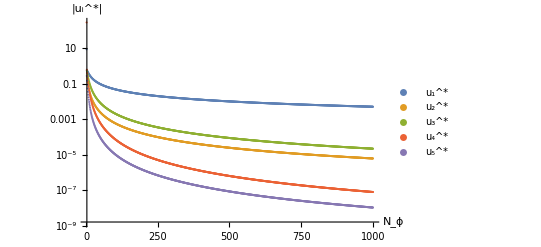

absvalueU12345phi6d2expansionlogplotLabels.jpg

```mathematica
ListLogPlot[{Partition[Flatten[FPphi6d2U1],2]*Threaded[{1,-1}], Partition[Flatten[FPphi6d2U2],2]*Threaded[{1,-1}],Partition[Flatten[FPphi6d2U3],2]*Threaded[{1,-1}],Partition[Flatten[FPphi6d2U4],2]*Threaded[{1,-1}], Partition[Flatten[FPphi6d2U5],2]*Threaded[{1,-1}]},AxesLabel->{Style["N_ϕ", FontSize->14],Style["|u_i^*|", FontSize->14]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotLegends->{Style["u_1^*", FontSize->14], Style["u_2^*", FontSize->14], Style["u_3^*", FontSize->14],Style["u_4^*", FontSize->14],Style["u_5^*", FontSize->14]}, PlotRange->{{3, 1000}, Automatic}, TicksStyle->Directive[FontSize->13]]
Export["absvalueU12345phi6d2expansionlogplotLabels.jpg",%,"JPEG"]
```

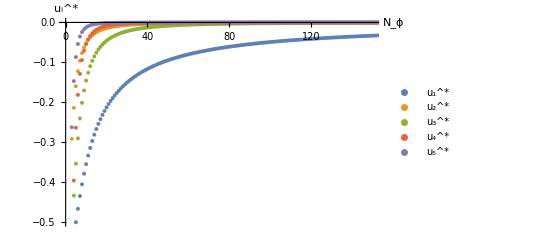

```mathematica
ListPlot[{FPphi6d2U1, FPphi6d2U2,Partition[Flatten[FPphi6d2U3],2],Partition[Flatten[FPphi6d2U4],2], Partition[Flatten[FPphi6d2U5],2]},AxesLabel->{Style["N_ϕ", FontSize->14],Style["u_i^*", FontSize->14]},PlotLabel->None,LabelStyle->{GrayLevel[0]},  PlotLegends->{Style["u_1^*", FontSize->14], Style["u_2^*", FontSize->14], Style["u_3^*", FontSize->14],Style["u_4^*", FontSize->14],Style["u_5^*", FontSize->14]}, PlotRange->{{0, 150}, {-0.5,0}}, PlotStyle->{PointSize[0.007]}, TicksStyle->Directive[FontSize->13]]
```

```mathematica
Export["ValueU12345phi6d2expansionlinplotLabel.jpg",%,"JPEG"]
```

ValueU12345phi6d2expansionlinplotLabel.jpg

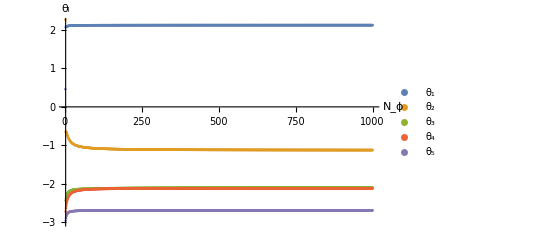

```mathematica
ListPlot[{FPphi6d2EV1, FPphi6d2EV2,Partition[Flatten[FPphi6d2EV3],2],Partition[Flatten[FPphi6d2EV4],2], Partition[Flatten[FPphi6d2EV5],2]},AxesLabel->{HoldForm["N_ϕ"],HoldForm["θ_i"]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotLegends->{"θ_1", "θ_2", "θ_3", "θ_4","θ_5"}, PlotRange->{{3, 1000}, {-3,2.2}}]
(*Export["StabilityCoefficientsphi6d2plot.jpg",%,"JPEG"]*)
```

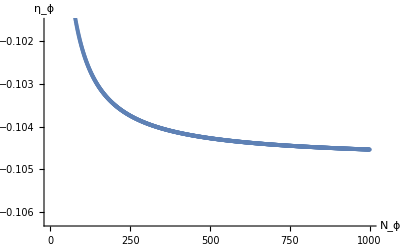

```mathematica
ListPlot[AnomalousDimd2phi6, AxesLabel->{"N_ϕ", "η_ϕ"}]
```

## Large N_ϕ-expansion

From the figures showing the evolution of U_i and θ_i it looks like the function asymptotes to a constant for very large N_ϕ. This means it should be possible to make a quite good large N_ϕ-expansion. The θ_i definitely should at highest order be constant in N_ϕ.

## Expanding the fixed point values

### From scratch

```mathematica
Clear[ηϕ2];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[βϕ2];
U1ExpPhi6d2= U2[6, Nphi, 1]-> U2[1,1] Nphi^-1+ U2[1,2] Nphi^-2+ U2[1,3] Nphi^-3;
U2ExpPhi6d2= U2[6, Nphi, 2]-> U2[2,1] Nphi^-1+ U2[2,2] Nphi^-2+ U2[2,3] Nphi^-3;
U3ExpPhi6d2= U2[6, Nphi, 3]-> U2[3,1] Nphi^-1+ U2[3,2] Nphi^-2+ U2[3,3] Nphi^-3;
U4ExpPhi6d2= U2[6, Nphi, 4]-> U2[4,1] Nphi^-1+ U2[4,2] Nphi^-2+ U2[4,3] Nphi^-3;
U5ExpPhi6d2= U2[6, Nphi, 5]-> U2[5,1] Nphi^-1+ U2[5,2] Nphi^-2+ U2[5,3] Nphi^-3;
```

```mathematica
RHSphi6d2Exp = Normal[Series[RHS2phi6/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2, {Nphi, ∞, 1}]];
LHSphi6d2Exp = Normal[Series[LHScollectedd2order6/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2, {Nphi, ∞, 1}]];
ηϕ2Expphi6 = Normal[Series[ηϕ2/. Solve[Simplify[Coefficient[Coefficient[RHSphi6d2Exp, X], S2, 0]]==Coefficient[Coefficient[LHSphi6d2Exp, X, 1],S2, 0], ηϕ2], {Nphi, ∞, 1}]]
```

{(6 (2 U2[1,1]+U2[2,1]))/(48 π+2 U2[1,1]+U2[2,1])+(288 π (2 U2[1,1]+2 U2[1,2]+3 U2[2,1]+U2[2,2]))/(Nphi (48 π+2 U2[1,1]+U2[2,1])^2)}

```mathematica
RHSphi6d2ExpEps = Normal[Series[RHSphi6d2Exp/.ηϕ2-> ηϕ2Expphi6[[1]], {Nphi, ∞, 1}]];
LHSphi6d2ExpEps = Normal[Series[LHSphi6d2Exp/.ηϕ2-> ηϕ2Expphi6[[1]], {Nphi, ∞, 1}]];
```

```mathematica
β2[6, Nphi, 1]=0;(*Set all appearing beta functions to zero *)
β2[6, Nphi, 2]=0;
β2[6, Nphi, 3]=0;
β2[6, Nphi, 4]=0;
β2[6, Nphi, 5]=0;
FPsolved2phi6ExpNphi0Of1=Simplify[Solve[Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d2ExpEps, S2],X, 0],Nphi, 0]]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d2ExpEps, S2],X, 0], Nphi,0]]&&
Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d2ExpEps, S2, 0],X, 2], Nphi, 0]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d2ExpEps, S2,0],X,2], Nphi, 0]]]&&Coefficient[Simplify[Coefficient[k^8 LHSphi6d2ExpEps, X, 3]], Nphi,-1]== Coefficient[Simplify[Coefficient[k^8 RHSphi6d2ExpEps, X,3]], Nphi, -1]&&Coefficient[Simplify[Coefficient[k^8 LHSphi6d2ExpEps, S3]], Nphi, -1]==Coefficient[Simplify[Coefficient[k^8 RHSphi6d2ExpEps, S3]], Nphi, -1]&&Simplify[Coefficient[k^8 Coefficient[Coefficient[LHSphi6d2ExpEps, S2],X], Nphi, -1]]== Simplify[Coefficient[k^8 Coefficient[Coefficient[RHSphi6d2ExpEps, S2],X], Nphi, -1]], {U2[1,1], U2[2,1],U2[3,1],U2[4,1],U2[5,1]}]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{U2[1,1]→-(3072 π^2+544 π U2[2,1]+U2[2,1]^2)/(704 π+2 U2[2,1]),U2[3,1]→-1/3 U2[4,1],U2[5,1]→-2/3 U2[4,1]},{U2[3,1]→0,U2[4,1]→0,U2[5,1]→0}}

### With the vanishing coefficient set to zero from the beginning

#### u_(3,1)= u_(4,1)= u_(5,1)= 0

```mathematica
Clear[ηϕ2];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[βϕ2];
U1ExpPhi6d2= U2[6, Nphi, 1]-> U2[1,1] Nphi^-1+ U2[1,2] Nphi^-2+ U2[1,3] Nphi^-3;
U2ExpPhi6d2= U2[6, Nphi, 2]-> U2[2,1] Nphi^-1+ U2[2,2] Nphi^-2+ U2[2,3] Nphi^-3;
U3ExpPhi6d2= U2[6, Nphi, 3]-> U2[3,2] Nphi^-2+ U2[3,3] Nphi^-3;
U4ExpPhi6d2= U2[6, Nphi, 4]-> U2[4,2] Nphi^-2+ U2[4,3] Nphi^-3;
U5ExpPhi6d2= U2[6, Nphi, 5]-> U2[5,2] Nphi^-2+ U2[5,3] Nphi^-3;
```

```mathematica
RHSphi6d2Exp = Normal[Series[RHS2phi6/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2, {Nphi, ∞, 2}]];
LHSphi6d2Exp = Normal[Series[LHScollectedd2order6/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2, {Nphi, ∞, 2}]];
ηϕ2Expphi6 = Normal[Series[ηϕ2/. Solve[Simplify[Coefficient[Coefficient[RHSphi6d2Exp, X], S2, 0]]==Coefficient[Coefficient[LHSphi6d2Exp, X, 1],S2, 0], ηϕ2], {Nphi, ∞, 2}]];
```

```mathematica
RHSphi6d2ExpEps = Normal[Series[RHSphi6d2Exp/.ηϕ2-> ηϕ2Expphi6[[1]], {Nphi, ∞, 2}]];
LHSphi6d2ExpEps = Normal[Series[LHSphi6d2Exp/.ηϕ2-> ηϕ2Expphi6[[1]], {Nphi, ∞, 2}]];
```

```mathematica
FPsolved2phi6ExpNphi0Of1=Simplify[Solve[Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d2ExpEps, S2],X, 0],Nphi, -1]]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d2ExpEps, S2],X, 0], Nphi,-1]]&&
Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d2ExpEps, S2, 0],X, 2], Nphi, -1]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d2ExpEps, S2,0],X,2], Nphi, -1]]]&&
Coefficient[Simplify[Coefficient[k^8 LHSphi6d2ExpEps, X, 3]], Nphi,-2]== Coefficient[Simplify[Coefficient[k^8 RHSphi6d2ExpEps, X,3]], Nphi, -2]&&Coefficient[Simplify[Coefficient[k^8 LHSphi6d2ExpEps, S3]], Nphi, -2]==Coefficient[Simplify[Coefficient[k^8 RHSphi6d2ExpEps, S3]], Nphi, -2]&&Simplify[Coefficient[k^8 Coefficient[Coefficient[LHSphi6d2ExpEps, S2],X], Nphi, -2]]== Simplify[Coefficient[k^8 Coefficient[Coefficient[RHSphi6d2ExpEps, S2],X], Nphi, -2]], {U2[1,1], U2[2,1],U2[3,2],U2[4,2],U2[5,2]}]]
```

{{U2[1,1]→0,U2[2,1]→0,U2[3,2]→0,U2[4,2]→0,U2[5,2]→0},{U2[1,1]→π Root-3.20Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,1]-3.1991993493182687,U2[2,1]→0,U2[3,2]→1/108 π^2 Root-3.20Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,1]-3.1991993493182687 (576+264 Root-3.20Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,1]-3.1991993493182687+(Root-3.20Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,1]-3.1991993493182687)^2),U2[4,2]→0,U2[5,2]→0},{U2[1,1]→π Root-1.62Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,2]-1.621923332915249,U2[2,1]→0,U2[3,2]→1/108 π^2 Root-1.62Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,2]-1.621923332915249 (576+264 Root-1.62Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,2]-1.621923332915249+(Root-1.62Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,2]-1.621923332915249)^2),U2[4,2]→0,U2[5,2]→0},{U2[1,1]→π Root-178.-104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,3]-178.38943865888325,U2[2,1]→0,U2[3,2]→1/108 π^2 Root-178.-104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,3]-178.38943865888325 (576+264 Root-178.-104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,3]-178.38943865888325+(Root-178.-104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,3]-178.38943865888325)^2),U2[4,2]→0,U2[5,2]→0},{U2[1,1]→π Root-178.+104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,4]-178.38943865888325,U2[2,1]→0,U2[3,2]→1/108 π^2 Root-178.+104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,4]-178.38943865888325 (576+264 Root-178.+104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,4]-178.38943865888325+(Root-178.+104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,4]-178.38943865888325)^2),U2[4,2]→0,U2[5,2]→0},{U2[1,1]→12 π,U2[2,1]→-24 π,U2[3,2]→288 π^2,U2[4,2]→-864 π^2,U2[5,2]→576 π^2},{U2[1,1]→-1/20 π Root-64.0Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,1]-63.98398698636537,U2[2,1]→π Root-12.8Root[283115520+66355200 #1+3548160 #1^2+7232 #1^3+5 #1^4&,1]-12.796797397273075,U2[3,2]→(π^2 Root-64.0Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,1]-63.98398698636537 (230400+5280 Root-64.0Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,1]-63.98398698636537+(Root-64.0Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,1]-63.98398698636537)^2))/2592000,U2[4,2]→-(π^2 Root-64.0Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,1]-63.98398698636537 (230400+5280 Root-64.0Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,1]-63.98398698636537+(Root-64.0Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,1]-63.98398698636537)^2))/216000,U2[5,2]→(π^2 Root-64.0Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,1]-63.98398698636537 (230400+5280 Root-64.0Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,1]-63.98398698636537+(Root-64.0Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,1]-63.98398698636537)^2))/81000},{U2[1,1]→-1/20 π Root-32.4Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,2]-32.438466658304975,U2[2,1]→π Root-6.49Root[283115520+66355200 #1+3548160 #1^2+7232 #1^3+5 #1^4&,2]-6.487693331660996,U2[3,2]→(π^2 Root-32.4Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,2]-32.438466658304975 (230400+5280 Root-32.4Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,2]-32.438466658304975+(Root-32.4Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,2]-32.438466658304975)^2))/2592000,U2[4,2]→-(π^2 Root-32.4Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,2]-32.438466658304975 (230400+5280 Root-32.4Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,2]-32.438466658304975+(Root-32.4Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,2]-32.438466658304975)^2))/216000,U2[5,2]→(π^2 Root-32.4Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,2]-32.438466658304975 (230400+5280 Root-32.4Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,2]-32.438466658304975+(Root-32.4Root[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,2]-32.438466658304975)^2))/81000},{U2[1,1]→-1/20 π Root-3.57 × 10^3-2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,3]-3567.788773177665,U2[2,1]→π Root-714.-416. ⅈRoot[283115520+66355200 #1+3548160 #1^2+7232 #1^3+5 #1^4&,3]-713.557754635533,U2[3,2]→(π^2 Root-3.57 × 10^3-2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,3]-3567.788773177665 (230400+5280 Root-3.57 × 10^3-2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,3]-3567.788773177665+(Root-3.57 × 10^3-2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,3]-3567.788773177665)^2))/2592000,U2[4,2]→-(π^2 Root-3.57 × 10^3-2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,3]-3567.788773177665 (230400+5280 Root-3.57 × 10^3-2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,3]-3567.788773177665+(Root-3.57 × 10^3-2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,3]-3567.788773177665)^2))/216000,U2[5,2]→(π^2 Root-3.57 × 10^3-2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,3]-3567.788773177665 (230400+5280 Root-3.57 × 10^3-2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,3]-3567.788773177665+(Root-3.57 × 10^3-2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,3]-3567.788773177665)^2))/81000},{U2[1,1]→-1/20 π Root-3.57 × 10^3+2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,4]-3567.788773177665,U2[2,1]→π Root-714.+416. ⅈRoot[283115520+66355200 #1+3548160 #1^2+7232 #1^3+5 #1^4&,4]-713.557754635533,U2[3,2]→(π^2 Root-3.57 × 10^3+2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,4]-3567.788773177665 (230400+5280 Root-3.57 × 10^3+2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,4]-3567.788773177665+(Root-3.57 × 10^3+2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,4]-3567.788773177665)^2))/2592000,U2[4,2]→-(π^2 Root-3.57 × 10^3+2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,4]-3567.788773177665 (230400+5280 Root-3.57 × 10^3+2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,4]-3567.788773177665+(Root-3.57 × 10^3+2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,4]-3567.788773177665)^2))/216000,U2[5,2]→(π^2 Root-3.57 × 10^3+2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,4]-3567.788773177665 (230400+5280 Root-3.57 × 10^3+2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,4]-3567.788773177665+(Root-3.57 × 10^3+2.08 × 10^3 ⅈRoot[35389440000+1658880000 #1+17740800 #1^2+7232 #1^3+#1^4&,4]-3567.788773177665)^2))/81000},{U2[1,1]→(π (-1734347396837463576912691200-32943965663949328694400 Root-2.22 × 10^5Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,1]-221709.4282083359+1020002666176360 (Root-2.22 × 10^5Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,1]-221709.4282083359)^2+168554101 (Root-2.22 × 10^5Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,1]-221709.4282083359)^3))/541809449626726198177632000,U2[2,1]→π Root-24.0Root[4090134528+139118303232 #1+5719445760 #1^2-2884760 #1^3+9245 #1^4&,1]-23.981549833243474,U2[3,2]→1/26452298660389493690716842500174700000 π^2 (216842731559914727816725452297090969600+51494797027562082507475381656220800 Root-2.22 × 10^5Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,1]-221709.4282083359+268840354821493225545230532520 (Root-2.22 × 10^5Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,1]-221709.4282083359)^2+1009058359137084197917 (Root-2.22 × 10^5Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,1]-221709.4282083359)^3),U2[4,2]→-(π^2 (2391577388818190917272007490764800+8555002036110700383563928036480 Root-2.22 × 10^5Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,1]-221709.4282083359+52983271413486410155602280 (Root-2.22 × 10^5Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,1]-221709.4282083359)^2+946348736343953623 (Root-2.22 × 10^5Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,1]-221709.4282083359)^3))/2177143922665801949853238065858000,U2[5,2]→(π^2 (-151350853228037700454250066534400-553796296829513939796252821760 Root-2.22 × 10^5Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,1]-221709.4282083359+8639314935142567033154720 (Root-2.22 × 10^5Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,1]-221709.4282083359)^2+660778441530745133 (Root-2.22 × 10^5Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,1]-221709.4282083359)^3))/1632857941999351462389928549393500},{U2[1,1]→(π (-1734347396837463576912691200-32943965663949328694400 Root-272.Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,2]-272.13608660308336+1020002666176360 (Root-272.Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,2]-272.13608660308336)^2+168554101 (Root-272.Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,2]-272.13608660308336)^3))/541809449626726198177632000,U2[2,1]→π Root-0.0294Root[4090134528+139118303232 #1+5719445760 #1^2-2884760 #1^3+9245 #1^4&,2]-0.029436028837542816,U2[3,2]→(π^2 (216842731559914727816725452297090969600+51494797027562082507475381656220800 Root-272.Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,2]-272.13608660308336+268840354821493225545230532520 (Root-272.Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,2]-272.13608660308336)^2+1009058359137084197917 (Root-272.Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,2]-272.13608660308336)^3))/26452298660389493690716842500174700000,U2[4,2]→-(π^2 (2391577388818190917272007490764800+8555002036110700383563928036480 Root-272.Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,2]-272.13608660308336+52983271413486410155602280 (Root-272.Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,2]-272.13608660308336)^2+946348736343953623 (Root-272.Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,2]-272.13608660308336)^3))/2177143922665801949853238065858000,U2[5,2]→(π^2 (-151350853228037700454250066534400-553796296829513939796252821760 Root-272.Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,2]-272.13608660308336+8639314935142567033154720 (Root-272.Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,2]-272.13608660308336)^2+660778441530745133 (Root-272.Root[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,2]-272.13608660308336)^3))/1632857941999351462389928549393500},{U2[1,1]→(π (-1734347396837463576912691200-32943965663949328694400 Root1.55 × 10^6-7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,3]1.5533707821474695e6+1020002666176360 (Root1.55 × 10^6-7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,3]1.5533707821474695e6)^2+168554101 (Root1.55 × 10^6-7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,3]1.5533707821474695e6)^3))/541809449626726198177632000,U2[2,1]→π Root168.-774. ⅈRoot[4090134528+139118303232 #1+5719445760 #1^2-2884760 #1^3+9245 #1^4&,3]168.02279958328498,U2[3,2]→1/26452298660389493690716842500174700000 π^2 (216842731559914727816725452297090969600+51494797027562082507475381656220800 Root1.55 × 10^6-7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,3]1.5533707821474695e6+268840354821493225545230532520 (Root1.55 × 10^6-7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,3]1.5533707821474695e6)^2+1009058359137084197917 (Root1.55 × 10^6-7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,3]1.5533707821474695e6)^3),U2[4,2]→-1/2177143922665801949853238065858000 π^2 (2391577388818190917272007490764800+8555002036110700383563928036480 Root1.55 × 10^6-7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,3]1.5533707821474695e6+52983271413486410155602280 (Root1.55 × 10^6-7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,3]1.5533707821474695e6)^2+946348736343953623 (Root1.55 × 10^6-7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,3]1.5533707821474695e6)^3),U2[5,2]→1/1632857941999351462389928549393500 π^2 (-151350853228037700454250066534400-553796296829513939796252821760 Root1.55 × 10^6-7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,3]1.5533707821474695e6+8639314935142567033154720 (Root1.55 × 10^6-7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,3]1.5533707821474695e6)^2+660778441530745133 (Root1.55 × 10^6-7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,3]1.5533707821474695e6)^3)},{U2[1,1]→(π (-1734347396837463576912691200-32943965663949328694400 Root1.55 × 10^6+7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,4]1.5533707821474695e6+1020002666176360 (Root1.55 × 10^6+7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,4]1.5533707821474695e6)^2+168554101 (Root1.55 × 10^6+7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,4]1.5533707821474695e6)^3))/541809449626726198177632000,U2[2,1]→π Root168.+774. ⅈRoot[4090134528+139118303232 #1+5719445760 #1^2-2884760 #1^3+9245 #1^4&,4]168.02279958328498,U2[3,2]→1/26452298660389493690716842500174700000 π^2 (216842731559914727816725452297090969600+51494797027562082507475381656220800 Root1.55 × 10^6+7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,4]1.5533707821474695e6+268840354821493225545230532520 (Root1.55 × 10^6+7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,4]1.5533707821474695e6)^2+1009058359137084197917 (Root1.55 × 10^6+7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,4]1.5533707821474695e6)^3),U2[4,2]→-1/2177143922665801949853238065858000 π^2 (2391577388818190917272007490764800+8555002036110700383563928036480 Root1.55 × 10^6+7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,4]1.5533707821474695e6+52983271413486410155602280 (Root1.55 × 10^6+7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,4]1.5533707821474695e6)^2+946348736343953623 (Root1.55 × 10^6+7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,4]1.5533707821474695e6)^3),U2[5,2]→1/1632857941999351462389928549393500 π^2 (-151350853228037700454250066534400-553796296829513939796252821760 Root1.55 × 10^6+7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,4]1.5533707821474695e6+8639314935142567033154720 (Root1.55 × 10^6+7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,4]1.5533707821474695e6)^2+660778441530745133 (Root1.55 × 10^6+7.15 × 10^6 ⅈRoot[3231903158842281984000+11890444855196620800 #1+52876276051200 #1^2-2884760 #1^3+#1^4&,4]1.5533707821474695e6)^3)}}

```mathematica
FPsolved2phi6ExpNphi0Of1/.(lhs_->rhs_):>lhs->N[rhs]
```

{{U2[1,1]→0.,U2[2,1]→0.,U2[3,2]→0.,U2[4,2]→0.,U2[5,2]→0.},{U2[1,1]→-10.0506,U2[2,1]→0.,U2[3,2]→75.5322,U2[4,2]→0.,U2[5,2]→0.},{U2[1,1]→-5.09542,U2[2,1]→0.,U2[3,2]→-22.2986,U2[4,2]→0.,U2[5,2]→0.},{U2[1,1]→-560.427-326.544 ⅈ,U2[2,1]→0.,U2[3,2]→507307.+85006.3 ⅈ,U2[4,2]→0.,U2[5,2]→0.},{U2[1,1]→-560.427+326.544 ⅈ,U2[2,1]→0.,U2[3,2]→507307.-85006.3 ⅈ,U2[4,2]→0.,U2[5,2]→0.},{U2[1,1]→37.6991,U2[2,1]→-75.3982,U2[3,2]→2842.45,U2[4,2]→-8527.34,U2[5,2]→5684.89},{U2[1,1]→10.0506,U2[2,1]→-40.2023,U2[3,2]→25.1774,U2[4,2]→-302.129,U2[5,2]→805.677},{U2[1,1]→5.09542,U2[2,1]→-20.3817,U2[3,2]→-7.43287,U2[4,2]→89.1945,U2[5,2]→-237.852},{U2[1,1]→560.427+326.544 ⅈ,U2[2,1]→-2241.71-1306.17 ⅈ,U2[3,2]→169102.+28335.4 ⅈ,U2[4,2]→-2.02923×10^6-340025. ⅈ,U2[5,2]→5.41127×10^6+906734. ⅈ},{U2[1,1]→560.427-326.544 ⅈ,U2[2,1]→-2241.71+1306.17 ⅈ,U2[3,2]→169102.-28335.4 ⅈ,U2[4,2]→-2.02923×10^6+340025. ⅈ,U2[5,2]→5.41127×10^6-906734. ⅈ},{U2[1,1]→32.5747,U2[2,1]→-75.3403,U2[3,2]→747.648,U2[4,2]→-3172.16,U2[5,2]→3264.54},{U2[1,1]→-10.0043,U2[2,1]→-0.092476,U2[3,2]→75.6849,U2[4,2]→-0.305436,U2[5,2]→-0.0000187299},{U2[1,1]→-824.357+1541.74 ⅈ,U2[2,1]→527.859-2430.4 ⅈ,U2[3,2]→-4.94736×10^6-2.24797×10^6 ⅈ,U2[4,2]→1.26531×10^7+4.26689×10^6 ⅈ,U2[5,2]→-3.48747×10^6+118066. ⅈ},{U2[1,1]→-824.357-1541.74 ⅈ,U2[2,1]→527.859+2430.4 ⅈ,U2[3,2]→-4.94736×10^6+2.24797×10^6 ⅈ,U2[4,2]→1.26531×10^7-4.26689×10^6 ⅈ,U2[5,2]→-3.48747×10^6-118066. ⅈ}}

Taking into account the lowest order solution: Most likely {U2[1,1]→-5.09542,U2[2,1]→0.,U2[3,2]→-22.2986,U2[4,2]→0.,U2[5,2]→0.} is NGFP2 in the large N limit

#### u_(2,1)=u_(3,1)= u_(4,1)= u_(5,1)= u_(4,2)= u_(5,2)=0

```mathematica
Clear[ηϕ2];(*Clear to be sure none of the results of the previous run remain in there*)
Clear[βϕ2];
U1ExpPhi6d2= U2[6, Nphi, 1]-> U2[1,1] Nphi^-1+ U2[1,2] Nphi^-2+ U2[1,3] Nphi^-3;
U2ExpPhi6d2= U2[6, Nphi, 2]->  U2[2,2] Nphi^-2+ U2[2,3] Nphi^-3;
U3ExpPhi6d2= U2[6, Nphi, 3]->  U2[3,2] Nphi^-2+ U2[3,3] Nphi^-3;
U4ExpPhi6d2= U2[6, Nphi, 4]->  U2[4,3] Nphi^-3;
U5ExpPhi6d2= U2[6, Nphi, 5]-> U2[5,3] Nphi^-3;
RHSphi6d2Exp = Normal[Series[RHS2phi6/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2, {Nphi, ∞, 3}]];
LHSphi6d2Exp = Normal[Series[LHScollectedd2order6/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2, {Nphi, ∞, 3}]];
ηϕ2Expphi6 = Normal[Series[ηϕ2/. Solve[Simplify[Coefficient[Coefficient[RHSphi6d2Exp, X], S2, 0]]==Coefficient[Coefficient[LHSphi6d2Exp, X, 1],S2, 0], ηϕ2], {Nphi, ∞, 3}]];
```

```mathematica
RHSphi6d2ExpEps = Normal[Series[RHSphi6d2Exp/.ηϕ2-> ηϕ2Expphi6[[1]], {Nphi, ∞, 3}]];
LHSphi6d2ExpEps = Normal[Series[LHSphi6d2Exp/.ηϕ2-> ηϕ2Expphi6[[1]], {Nphi, ∞, 3}]];
```

```mathematica
β2[6, Nphi, 1]=0;(*Set all appearing beta functions to zero *)
β2[6, Nphi, 2]=0;
β2[6, Nphi, 3]=0;
β2[6, Nphi, 4]=0;
β2[6, Nphi, 5]=0;
FPsolved2phi6ExpNphi0Of1=Simplify[Solve[Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d2ExpEps, S2],X, 0],Nphi, -2]]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d2ExpEps, S2],X, 0], Nphi,-2]]&&
Simplify[Coefficient[k^4 Coefficient[Coefficient[LHSphi6d2ExpEps, S2, 0],X, 2], Nphi, -1]== Simplify[Coefficient[k^4 Coefficient[Coefficient[RHSphi6d2ExpEps, S2,0],X,2], Nphi, -1]]]&&
Coefficient[Simplify[Coefficient[k^8 LHSphi6d2ExpEps, X, 3]], Nphi,-2]== Coefficient[Simplify[Coefficient[k^8 RHSphi6d2ExpEps, X,3]], Nphi, -2]&&
Coefficient[Simplify[Coefficient[k^8 LHSphi6d2ExpEps, S3]], Nphi, -3]==Coefficient[Simplify[Coefficient[k^8 RHSphi6d2ExpEps, S3]], Nphi, -3]&&Simplify[Coefficient[k^8 Coefficient[Coefficient[LHSphi6d2ExpEps, S2],X], Nphi, -3]]== Simplify[Coefficient[k^8 Coefficient[Coefficient[RHSphi6d2ExpEps, S2],X], Nphi, -3]], {U2[1,1], U2[2,2],U2[3,2],U2[4,3],U2[5,3]}]]
```

{{U2[1,1]→0,U2[2,2]→0,U2[3,2]→0,U2[4,3]→0,U2[5,3]→0},{U2[1,1]→π Root-3.20Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,1]-3.1991993493182687,U2[2,2]→-(π Root-3.20Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,1]-3.1991993493182687 (8330775552+967 (Root-16.0Root[138240000+25920000 #1+1108800 #1^2+1808 #1^3+#1^4&,1]-15.995996746591343)^3+5222455872 Root-3.20Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,1]-3.1991993493182687+43322360 (Root-3.20Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,1]-3.1991993493182687)^2))/21302784,U2[3,2]→1/108 π^2 Root-3.20Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,1]-3.1991993493182687 (576+264 Root-3.20Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,1]-3.1991993493182687+(Root-3.20Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,1]-3.1991993493182687)^2),U2[4,3]→(π^2 (16197120+10447680 Root-3.20Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,1]-3.1991993493182687+248080 (Root-3.20Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,1]-3.1991993493182687)^2+963 (Root-3.20Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,1]-3.1991993493182687)^3))/12060,U2[5,3]→(π^2 (391680+277440 Root-3.20Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,1]-3.1991993493182687+14960 (Root-3.20Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,1]-3.1991993493182687)^2+227 (Root-3.20Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,1]-3.1991993493182687)^3))/18090},{U2[1,1]→π Root-1.62Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,2]-1.621923332915249,U2[2,2]→-(π Root-1.62Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,2]-1.621923332915249 (8330775552+967 (Root-8.11Root[138240000+25920000 #1+1108800 #1^2+1808 #1^3+#1^4&,2]-8.109616664576244)^3+5222455872 Root-1.62Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,2]-1.621923332915249+43322360 (Root-1.62Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,2]-1.621923332915249)^2))/21302784,U2[3,2]→1/108 π^2 Root-1.62Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,2]-1.621923332915249 (576+264 Root-1.62Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,2]-1.621923332915249+(Root-1.62Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,2]-1.621923332915249)^2),U2[4,3]→(π^2 (16197120+10447680 Root-1.62Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,2]-1.621923332915249+248080 (Root-1.62Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,2]-1.621923332915249)^2+963 (Root-1.62Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,2]-1.621923332915249)^3))/12060,U2[5,3]→(π^2 (391680+277440 Root-1.62Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,2]-1.621923332915249+14960 (Root-1.62Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,2]-1.621923332915249)^2+227 (Root-1.62Root[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,2]-1.621923332915249)^3))/18090},{U2[1,1]→π Root-178.-104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,3]-178.38943865888325,U2[2,2]→-(π Root-178.-104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,3]-178.38943865888325 (8330775552+967 (Root-892.-520. ⅈRoot[138240000+25920000 #1+1108800 #1^2+1808 #1^3+#1^4&,3]-891.9471932944163)^3+5222455872 Root-178.-104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,3]-178.38943865888325+43322360 (Root-178.-104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,3]-178.38943865888325)^2))/21302784,U2[3,2]→1/108 π^2 Root-178.-104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,3]-178.38943865888325 (576+264 Root-178.-104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,3]-178.38943865888325+(Root-178.-104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,3]-178.38943865888325)^2),U2[4,3]→(π^2 (16197120+10447680 Root-178.-104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,3]-178.38943865888325+248080 (Root-178.-104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,3]-178.38943865888325)^2+963 (Root-178.-104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,3]-178.38943865888325)^3))/12060,U2[5,3]→(π^2 (391680+277440 Root-178.-104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,3]-178.38943865888325+14960 (Root-178.-104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,3]-178.38943865888325)^2+227 (Root-178.-104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,3]-178.38943865888325)^3))/18090},{U2[1,1]→π Root-178.+104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,4]-178.38943865888325,U2[2,2]→-(π Root-178.+104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,4]-178.38943865888325 (8330775552+967 (Root-892.+520. ⅈRoot[138240000+25920000 #1+1108800 #1^2+1808 #1^3+#1^4&,4]-891.9471932944163)^3+5222455872 Root-178.+104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,4]-178.38943865888325+43322360 (Root-178.+104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,4]-178.38943865888325)^2))/21302784,U2[3,2]→1/108 π^2 Root-178.+104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,4]-178.38943865888325 (576+264 Root-178.+104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,4]-178.38943865888325+(Root-178.+104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,4]-178.38943865888325)^2),U2[4,3]→(π^2 (16197120+10447680 Root-178.+104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,4]-178.38943865888325+248080 (Root-178.+104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,4]-178.38943865888325)^2+963 (Root-178.+104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,4]-178.38943865888325)^3))/12060,U2[5,3]→(π^2 (391680+277440 Root-178.+104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,4]-178.38943865888325+14960 (Root-178.+104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,4]-178.38943865888325)^2+227 (Root-178.+104. ⅈRoot[1105920+1036800 #1+221760 #1^2+1808 #1^3+5 #1^4&,4]-178.38943865888325)^3))/18090}}

```mathematica
FPsolved2phi6ExpNphi0Of1/.(lhs_->rhs_):>lhs->N[rhs]
```

{{U2[1,1]→0.,U2[2,2]→0.,U2[3,2]→0.,U2[4,3]→0.,U2[5,3]→0.},{U2[1,1]→-10.0506,U2[2,2]→-3744.87,U2[3,2]→75.5322,U2[4,3]→-12046.1,U2[5,3]→-191.077},{U2[1,1]→-5.09542,U2[2,2]→-6.26628,U2[3,2]→-22.2986,U2[4,3]→-81.6057,U2[5,3]→-10.8684},{U2[1,1]→-560.427-326.544 ⅈ,U2[2,2]→-707.527+444.876 ⅈ,U2[3,2]→507307.+85006.3 ⅈ,U2[4,3]→2.83812×10^6-295156. ⅈ,U2[5,3]→157780.-802935. ⅈ},{U2[1,1]→-560.427+326.544 ⅈ,U2[2,2]→-707.527-444.876 ⅈ,U2[3,2]→507307.-85006.3 ⅈ,U2[4,3]→2.83812×10^6+295156. ⅈ,U2[5,3]→157780.+802935. ⅈ}}

So the coordinates are: {U2[1,1]→-5.09542,U2[2,2]→-6.26628,U2[3,2]→-22.2986,U2[4,3]→-81.6057,U2[5,3]→-10.8684}

### Anomalous dimension

```mathematica
Series[ηϕ2Expphi6, {Nphi, ∞, 0}]
```

{(6 U2[1,1])/(24 π+U2[1,1])+O[1/Nphi]^1}

```mathematica
Series[ηϕ2Expphi6, {Nphi, ∞, 0}]/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}
```

{-0.434869+O[1/Nphi]^1}

## Expanding the stability matrix

Rerun the beta functions as these were zero in the previous part of the analysis.

```mathematica
U1ExpPhi6d2= U2[6, Nphi, 1]-> U2[1,1] Nphi^-1+ U2[1,2] Nphi^-2+ U2[1,3] Nphi^-3;
U2ExpPhi6d2= U2[6, Nphi, 2]->  U2[2,2] Nphi^-2+ U2[2,3] Nphi^-3;
U3ExpPhi6d2= U2[6, Nphi, 3]->  U2[3,2] Nphi^-2+ U2[3,3] Nphi^-3;
U4ExpPhi6d2= U2[6, Nphi, 4]->  U2[4,3] Nphi^-3;
U5ExpPhi6d2= U2[6, Nphi, 5]-> U2[5,3] Nphi^-3;
```

```mathematica
BexpPhi6d2[1,1]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 1], U2[6, Nphi, 1]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 0}]]
BexpPhi6d2[2,1]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 2], U2[6, Nphi, 1]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 1}]]
BexpPhi6d2[3,1]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 3], U2[6, Nphi, 1]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 1}]]
BexpPhi6d2[4,1]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 4], U2[6, Nphi, 1]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 2}]]
BexpPhi6d2[5,1]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 5], U2[6, Nphi, 1]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 2}]]
```

-1.0147

-2.37812/Nphi

-27.1489/Nphi

-102.275/Nphi^2

-20.4889/Nphi^2

```mathematica
BexpPhi6d2[1,2]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 1], U2[6, Nphi, 2]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 0}]]
BexpPhi6d2[2,2]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 2], U2[6, Nphi, 2]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 0}]]
BexpPhi6d2[3,2]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 3], U2[6, Nphi, 2]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 1}]]
BexpPhi6d2[4,2]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 4], U2[6, Nphi, 2]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 2}]]
BexpPhi6d2[5,2]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 5], U2[6, Nphi, 2]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 2}]]
```

-1.07248

1.13026

-13.5744/Nphi

-130.926/Nphi^2

-32.7158/Nphi^2

```mathematica
BexpPhi6d2[1,3]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 1], U2[6, Nphi, 3]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, -1}]]
BexpPhi6d2[2,3]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 2], U2[6, Nphi, 3]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 1}]]
BexpPhi6d2[3,3]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 3], U2[6, Nphi, 3]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 0}]]
BexpPhi6d2[4,3]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 4], U2[6, Nphi, 3]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 1}]]
BexpPhi6d2[5,3]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 5], U2[6, Nphi, 3]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 3}]]
```

-0.128018 Nphi

0

0.985305

-3.42018/Nphi

0

```mathematica
BexpPhi6d2[1,4]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 1], U2[6, Nphi, 4]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, -1}]]
BexpPhi6d2[2,4]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 2], U2[6, Nphi, 4]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, -1}]]
BexpPhi6d2[3,4]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 3], U2[6, Nphi, 4]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 0}]]
BexpPhi6d2[4,4]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 4], U2[6, Nphi, 4]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 0}]]
BexpPhi6d2[5,4]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 5], U2[6, Nphi, 4]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 1}]]
```

-0.0426726 Nphi

-0.0426726 Nphi

-0.570029

2.12536

-2.28012/Nphi

```mathematica
BexpPhi6d2[1,5]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 1], U2[6, Nphi, 5]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 0}]]
BexpPhi6d2[2,5]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 2], U2[6, Nphi, 5]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, -1}]]
BexpPhi6d2[3,5]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 3], U2[6, Nphi, 5]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 1}]]
BexpPhi6d2[4,5]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 4], U2[6, Nphi, 5]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 0}]]
BexpPhi6d2[5,5]= Normal[Series[D[β2[U2[6, Nphi, 1], U2[6, Nphi, 2], U2[6, Nphi, 3], U2[6, Nphi, 4], U2[6, Nphi, 5]][6, Nphi, 5], U2[6, Nphi, 5]]/. U1ExpPhi6d2/.U2ExpPhi6d2/. U3ExpPhi6d2/.U4ExpPhi6d2/.U5ExpPhi6d2/.{U2[1,1]->-5.09542,U2[2,2]->-6.26628,U2[3,2]->-22.2986,U2[4,3]->-81.6057,U2[5,3]->-10.8684}, {Nphi, ∞, 0}]]
```

-0.0640088

-0.0640088 Nphi

-0.855044/Nphi

-0.855044

2.69539

```mathematica
MatPhi6d2Exp = Table[BexpPhi6d2[a,b],{a,1,5},{b,1,5}];
%//MatrixForm
```

(-1.0147 | -1.07248 | -0.128018 Nphi | -0.0426726 Nphi | -0.0640088
-2.37812/Nphi | 1.13026 | 0 | -0.0426726 Nphi | -0.0640088 Nphi
-27.1489/Nphi | -13.5744/Nphi | 0.985305 | -0.570029 | -0.855044/Nphi
-102.275/Nphi^2 | -130.926/Nphi^2 | -3.42018/Nphi | 2.12536 | -0.855044
-20.4889/Nphi^2 | -32.7158/Nphi^2 | 0 | -2.28012/Nphi | 2.69539)

```mathematica
CharPolyP6d2 =Det[MatPhi6d2Exp-λ IdentityMatrix[5]](*This is the determinant of the previously matrix-λI. It will generate the characteristic polynomial*)
```

1/Nphi^6 1. (-121.592 Nphi^2-90.8569 Nphi^3-53.6833 Nphi^4-28.5016 Nphi^5-28.9773 Nphi^6+45.4421 Nphi^2 λ+101.33 Nphi^3 λ+100.217 Nphi^4 λ+117.411 Nphi^5 λ+50.2128 Nphi^6 λ-26.5749 Nphi^3 λ^2-40.1994 Nphi^4 λ^2-88.2835 Nphi^5 λ^2-20.4863 Nphi^6 λ^2+1.31147 Nphi^4 λ^3+18.4951 Nphi^5 λ^3-6.52718 Nphi^6 λ^3+5.92163 Nphi^6 λ^4-1. Nphi^6 λ^5)

```mathematica
Series[CharPolyP6d2, {Nphi, ∞, 0}]
```

1. (-28.9773+50.2128 λ-20.4863 λ^2-6.52718 λ^3+5.92163 λ^4-1. λ^5)+O[1/Nphi]^1

```mathematica
Solve[-28.977330319865693+50.21277164672098 λ-20.486309522280546 λ^2-6.527177202300653 λ^3+5.92162656719241 λ^4-1. λ^5==0, λ]
```

{{λ→-2.13024},{λ→1.13026},{λ→2.10085},{λ→2.12536},{λ→2.69539}}

## Making a fit to the data

### To the anomalous dimension

To find the value the anomalous dimension approaches in the large N-limit, it is fitted with a polynomial function.

```mathematica
FitAndim2phi6 =Fit[Take[AnomalousDimd2phi6, -500], {1, 1/z, 1/z^2}, z](*Fit a polynomial to the anomalous dimension value, to see what it approaches*)
```

-0.434869356596843435372590013549693718231769742492945643681836756522952553577582632582574036483867883-1.7154521479185152886731092883115649199003820089627831813970488110380134634117060285814547450753838/z^2+0.919086915090559054064183774649101496585616753690057221548283177543630863846426975626652288726994842/z

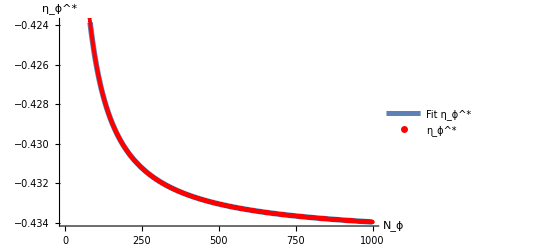

Phi6IncreasingNphiAnomalousDimension+fitd2.jpg

```mathematica
Show[Plot[{FitAndim2phi6},{z,2,1000},PlotStyle->{Thickness[0.01]}, PlotLegends->{"Fit η_ϕ^*"}],ListPlot[AnomalousDimd2phi6,PlotStyle->Red,  PlotLegends->{"η_ϕ^*"}], AxesLabel-> { "N_ϕ", "η_ϕ^*"}]
Export["Phi6IncreasingNphiAnomalousDimension+fitd2.jpg", %, "JPEG"]
```

### To the stability coefficients

Just as for the anomalous dimension, the fit function will be used to fit a polynomial of a+b/N_ϕ+ c/N_ϕ^2to the data of the stability coefficients to see what value the stability coefficients approach in the limit N_ϕ-> ∞.

```mathematica
FitEV1phi6d2=Fit[Take[FPphi6d2EV1, -500], {1, 1/z,1/z^2}, z]
```

2.13024+0.584243/z^2-0.29486/z

```mathematica
FitEV2phi6d2=Fit[Take[FPphi6d2EV2, -500], {1, 1/z,1/z^2}, z]
```

-1.13026-15.566/z^2+5.0894/z

```mathematica
FitEV3phi6d2=Fit[Take[FPphi6d2EV3, -500], {1, 1/z,1/z^2}, z]
```

-2.10084+39.8506/z^2-3.24638/z

```mathematica
FitEV4phi6d2=Fit[Take[FPphi6d2EV4, -500], {1, 1/z,1/z^2}, z]
```

-2.12537-38.5701/z^2-1.03439/z

```mathematica
FitEV5phi6d2=Fit[Take[FPphi6d2EV5, -500], {1, 1/z,1/z^2}, z]
```

-2.69539-2.01971/z^2-0.521485/z

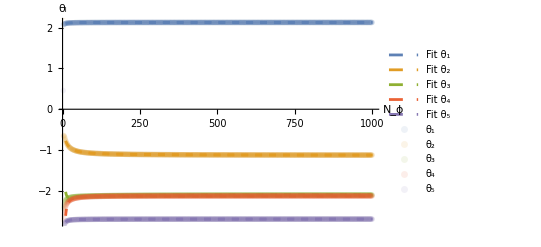

```mathematica
Show[Plot[{FitEV1phi6d2, FitEV2phi6d2, FitEV3phi6d2, FitEV4phi6d2, FitEV5phi6d2},{z,10,1001}, PlotLegends-> {"Fit θ_1", "Fit θ_2", "Fit θ_3", "Fit θ_4", "Fit θ_5"}, PlotStyle->{{RGBColor[0.368417,0.506779,0.709798],Dashed}, {RGBColor[0.880722,0.611041,0.142051],Dashed}, {RGBColor[0.560181,0.691569,0.194885],Dashed}, {RGBColor[0.922526,0.385626,0.209179],Dashed}, {RGBColor[0.528488,0.470624,0.701351],Dashed}}],ListPlot[{FPphi6d2EV1,FPphi6d2EV2, FPphi6d2EV3, FPphi6d2EV4, FPphi6d2EV5},PlotStyle->{{Opacity[0.1,RGBColor[0.368417,0.506779,0.709798]],PointSize[0.01]}, {Opacity[0.1,RGBColor[0.880722,0.611041,0.142051]],PointSize[0.01]}, {Opacity[0.1,RGBColor[0.560181,0.691569,0.194885]],PointSize[0.01]}, {Opacity[0.1,RGBColor[0.922526,0.385626,0.209179]],PointSize[0.01]}, {Opacity[0.1,RGBColor[0.528488,0.470624,0.701351]],PointSize[0.01]}},  PlotLegends->{"θ_1", "θ_2", "θ_3", "θ_4", "θ_5"}], AxesLabel->{"N_ϕ","θ_i"}]
(*Export["Phi6IncreasingNphiStabCoeff+fitd2.jpg", %, "JPEG"]*)
```

## Making figures

### Anomalous dimension

To verify the expansion, it is plotted together with the actual data points!

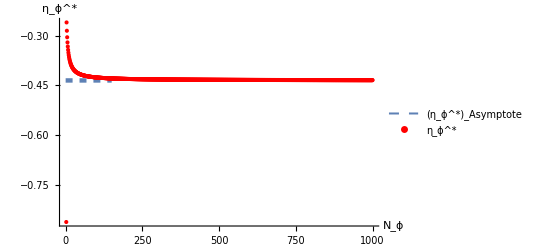

Phi6IncreasingNphiAnomalousDimension+Expansiond2.jpg

```mathematica
Show[Plot[{y=-0.4348691431494182},{y,0,150},PlotStyle->{Thickness[0.008], Dashed}, PlotLegends->{"(η_ϕ^*)_Asymptote"}],ListPlot[AnomalousDimd2phi6,PlotStyle->Red,  PlotLegends->{"η_ϕ^*"}, PlotRange->{{2,150},{0,-0.9}}], AxesLabel-> { "N_ϕ", "η_ϕ^*"}, PlotRange->{{0,150},{0,-0.8}}]
Export["Phi6IncreasingNphiAnomalousDimension+Expansiond2.jpg", %, "JPEG"]
```

```mathematica
"Phi6IncreasingNphiAnomalousDimension+Expansiond2.jpg"
```

Phi6IncreasingNphiAnomalousDimension+Expansiond2.jpg

### Stability coefficients

Again we plot the original data together with the expansion value for the stability coefficients

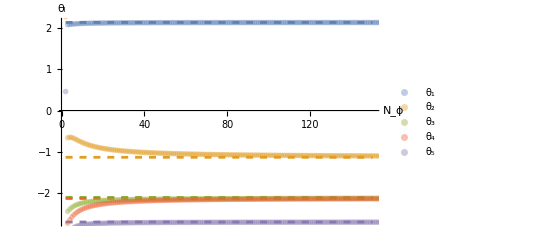

Phi6IncreasingNphiStabCoeff+Expansiond2.jpg

```mathematica
Show[Plot[{y=2.130241900968667, y=-1.1302617137011615, y=-2.100850969860431, y=-2.1253632140486,y=-2.6953925705517334},{y,2,150}, (*PlotLegends-> {"θ_(1,  Asymptote)", "θ_(2,  Asymptote)", "θ_(3,  Asymptote)", "θ_(4,  Asymptote)", "θ_(5,  Asymptote)"}, *)PlotStyle->{{RGBColor[0.368417,0.506779,0.709798],Dashed}, {RGBColor[0.880722,0.611041,0.142051],Dashed}, {RGBColor[0.560181,0.691569,0.194885],Dashed}, {RGBColor[0.922526,0.385626,0.209179],Dashed}, {RGBColor[0.528488,0.470624,0.701351],Dashed}}],ListPlot[{FPphi6d2EV1,FPphi6d2EV2, FPphi6d2EV3, FPphi6d2EV4, FPphi6d2EV5},PlotStyle->{{Opacity[0.4,RGBColor[0.368417,0.506779,0.709798]],PointSize[0.01]}, {Opacity[0.4,RGBColor[0.880722,0.611041,0.142051]],PointSize[0.01]}, {Opacity[0.4,RGBColor[0.560181,0.691569,0.194885]],PointSize[0.01]}, {Opacity[0.4,RGBColor[0.922526,0.385626,0.209179]],PointSize[0.01]}, {Opacity[0.4,RGBColor[0.528488,0.470624,0.701351]],PointSize[0.01]}},  PlotLegends->{"θ_1", "θ_2", "θ_3", "θ_4", "θ_5"}], AxesLabel->{"N_ϕ","θ_i"}]
Export["Phi6IncreasingNphiStabCoeff+Expansiond2.jpg", %, "JPEG"]
```